## README

### Message to the Reader

You will notice that some functions are identically defined multiple times for different figures. This is by choice; sometimes specific functions required small modifications when used for different numerical purposes. It is recommended that when trying to reproduce results for a particular figure, to run the functions under the section heading ONLY. Make sure to clear all stored memory, or quit the local kernel, before running numerics for a different figure.

Also note: when initializing any cell for the first time, a pop-up will showing asking if you want to initialize the “initialization cells” in the notebook (these are the grey cells). Click yes, as these are cells that have data stored explicitly (NOT any functions for numerics). If not selected you will manually have to initialize the data cells. All data relevant for a particular figure is stored under the folder name for that figure.

### Gain/Loss Mode Confusion

There may be some confusion about what we call the gain and loss mode. Form the paper we define the adiabatic frame as λ σz - 1/2 D[θ] σy. The sign of λ here determines what mode is consider the gain and loss mode. You will find for some numerics this was switch, and we used a -λ instead. This only changes the labeling for the dynamics, not the dynamics themselves. This whole issue came from recognizing that there are two different ways to define θ, which lead to two different adiabatic frames, one where λ is positive and the other where it is negative. The difference is in using θ=ArcTan[y/-x] or θ=-ArcTan[y/x], which are identical expressions but lead to subtly different frame transformations. Numerically this changes what we call the gain or loss mode, but again the dynamics that are solved for are identical in either case.

### Useful error message suppression

```mathematica
ParallelEvaluate[Off[Power::infy]];
ParallelEvaluate[Off[FindMinimum::nrnum]];
ParallelEvaluate[Off[FindMinimum::lstol]];
ParallelEvaluate[Off[FindMinimum::cvmit]];
ParallelEvaluate[Off[FindMinimum::precw]];
ParallelEvaluate[Off[FindRoot::lstol]];
ParallelEvaluate[Off[FindRoot::cvmit]];
ParallelEvaluate[Off[FindRoot::jsing]];
ParallelEvaluate[Off[Divide::infy]];
ParallelEvaluate[Off[Infinity::indet]];
ParallelEvaluate[Off[FindRoot::nlnum]];
ParallelEvaluate[Off[FindRoot::precw]];
ParallelEvaluate[Off[ReplaceAll::reps]];
ParallelEvaluate[Off[General::munfl]];
ParallelEvaluate[Off[FindMinimum::sdprec]];
ParallelEvaluate[Off[InterpolatingFunction::dmval]]; 
ParallelEvaluate[Off[InterpolatingFunction::dprec]];
ParallelEvaluate[Off[NDSolve::ndsz]]; 
ParallelEvaluate[Off[Inverse::luc]];
```

## Riemann Surface (Fig. 3)

### Functions used for numerics

```mathematica
(*choosen contour*)
ΔCircPath:=Function[{Δ0,φ,x},
Δ0 Sin[2 π x+φ]
];

ΩCircPath:=Function[{Δ0,Ω0,φ,x},
Ω0 + Δ0 Cos[2π x+φ]
];
(*the holomorphic eigenvalue*)
EigCircPath:= Function[{Δ0,Ω0,Γ,φ,dir,x},

(Cos[π UnitStep[(1-dir)/2+(x-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(x-3/2+φ/(2π))]])Sqrt[((ΔCircPath[Δ0,φ,x]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,x])^2)]

];
(*time dependant parametrization of contour*)
ωCirc1:=#1(6(#3/#2)^5-15(#3/#2)^4+10(#3/#2)^3)&;
ωCirc1DL:=(ωCirc1[#1,#2,#3]UnitStep[#2-#3]+((#1)+ωCirc1[#1,#2,#3-#2])UnitStep[#3-#2])&;
```

### 3a

```mathematica
(*plotting the argument of eigenvalues written in polar form*)
```

```mathematica
ComplexExpand[Sqrt[(Δ+ⅈ/2 )^2+Ω^2]]//FullSimplify
```

ⅇ^(1/2 ⅈ Arg[(ⅈ/2+Δ)^2+Ω^2]) (Δ^2+(-1/4+Δ^2+Ω^2)^2)^(1/4)

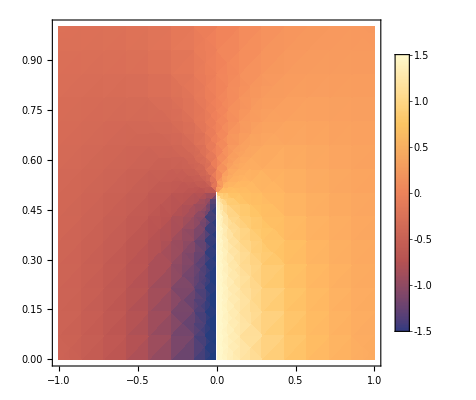

```mathematica
DensityPlot[N[Arg[ⅇ^(1/2 ⅈ Arg[(ⅈ/2+Δ)^2+Ω^2]) (Δ^2+(-1/4+Δ^2+Ω^2)^2)^(1/4)]],{Δ,-1,1},{Ω,0,1},PlotLegends->Automatic]
```

```mathematica
ComplexExpand[-Sqrt[(Δ+ⅈ/2 )^2+Ω^2]]//FullSimplify
```

-ⅇ^(1/2 ⅈ Arg[(ⅈ/2+Δ)^2+Ω^2]) (Δ^2+(-1/4+Δ^2+Ω^2)^2)^(1/4)

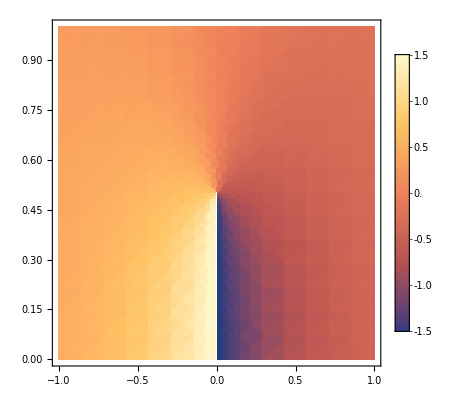

```mathematica
DensityPlot[N[Arg[ⅇ^(-1/2 ⅈ Arg[(ⅈ/2+Δ)^2+Ω^2]) (Δ^2+(-1/4+Δ^2+Ω^2)^2)^(1/4)]],{Δ,-1,1},{Ω,0,1},PlotLegends->Automatic]
```

```mathematica
(*ϕ=0 and ϕ=π contours*)
```

```mathematica
Δ0=1/2;
Ω0=1/2;
φ=0;
Γ=1;
```

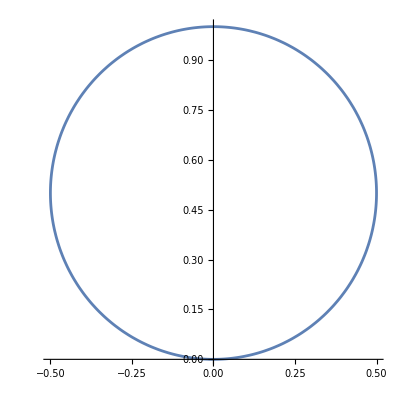

```mathematica
ParametricPlot[{{ΔCircPath[Δ0,φ,x],ΩCircPath[Δ0,Ω0,φ,x]}},{x,0,1}]
```

```mathematica
Δ0=1/2;
Ω0=1/2;
φ=π;
Γ=1;
```

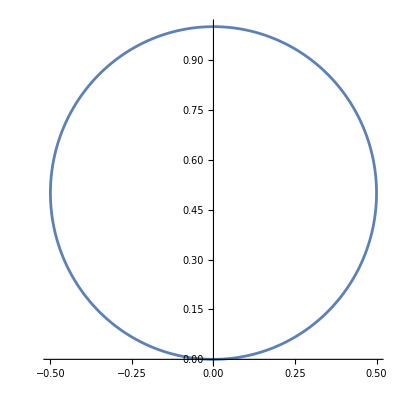

```mathematica
ParametricPlot[{{ΔCircPath[Δ0,φ,x],ΩCircPath[Δ0,Ω0,φ,x]}},{x,0,1}]
```

```mathematica
(*EP located at 0,0.5 - red dot*)
(*ϕ=0 located at 0,1 - purple cross*)
(*ϕ=π located at 0,0 - orange cross*)
```

### 3b

```mathematica
(*plotting the Riemann Surface*)
```

```mathematica
ϵ=10^-6;
aa=Plot3D[Re[ⅇ^(1/2 Log[(Δ+ⅈ/2 )^2+Ω^2])],{Δ,-1,-ϵ},{Ω,-1,1},BoxRatios->{1,1,1.5},PlotRange->All,PlotPoints->50,Mesh->30,MeshFunctions->{Im[Log[#1+ⅈ #2]]&,Re[Log[#1+ⅈ #2]]&},ImageSize->Large,ColorFunction->"BlueGreenYellow",PlotLegends->Automatic];
bb=Plot3D[Re[ⅇ^(1/2 Log[(Δ+ⅈ/2 )^2+Ω^2])],{Δ,ϵ,1},{Ω,-1,1},BoxRatios->{1,1,1.5},PlotRange->All,PlotPoints->50,Mesh->30,MeshFunctions->{Im[Log[#1+ⅈ #2]]&,Re[Log[#1+ⅈ #2]]&},ImageSize->Large,ColorFunction->"BlueGreenYellow",PlotLegends->Automatic];
cc=Plot3D[-Re[ⅇ^(1/2 Log[(Δ+ⅈ/2 )^2+Ω^2])],{Δ,-1,-ϵ},{Ω,-1,1},BoxRatios->{1,1,1.5},PlotRange->All,PlotPoints->50,Mesh->30,MeshFunctions->{Im[Log[#1+ⅈ #2]]&,Re[Log[#1+ⅈ #2]]&},ImageSize->Large,ColorFunction->"BlueGreenYellow",PlotLegends->Automatic];
dd=Plot3D[-Re[ⅇ^(1/2 Log[(Δ+ⅈ/2 )^2+Ω^2])],{Δ,ϵ,1},{Ω,-1,1},BoxRatios->{1,1,1.5},PlotRange->All,PlotPoints->50,Mesh->30,MeshFunctions->{Im[Log[#1+ⅈ #2]]&,Re[Log[#1+ⅈ #2]]&},ImageSize->Large,ColorFunction->"BlueGreenYellow",PlotLegends->Automatic];
```

```mathematica
Show[aa,bb,cc,dd]
```

-Graphics3D-

```mathematica
(*contours used for ϕ=0 and ϕ=π on the Riemann Surface*)
```

```mathematica
Δ0=1/2;
Ω0=1/2;
φ=0;
Γ=1;
dir=1;
```

```mathematica
ParametricPlot3D[{{ΔCircPath[Δ0,φ,x],ΩCircPath[Δ0,Ω0,φ,x],Re[EigCircPath[Δ0,Ω0,Γ,φ,dir,x]]}},{x,0,1},BoxRatios->{1,1,1.5},PlotRange->All,PlotStyle->{Black,Arrowheads[{{0.03,0.5}}]},PlotLegends->Automatic,Background->Transparent]
```

-Graphics3D-

```mathematica
Δ0=1/2;
Ω0=1/2;
φ=π;
Γ=1;
dir=1;
```

```mathematica
ParametricPlot3D[{{ΔCircPath[Δ0,φ,x],ΩCircPath[Δ0,Ω0,φ,x],Re[EigCircPath[Δ0,Ω0,Γ,φ,dir,x]]}},{x,0,1},BoxRatios->{1,1,1.5},PlotRange->All,PlotStyle->{Black,Arrowheads[{{0.03,0.5}}]},PlotLegends->Automatic,Background->Transparent]
```

-Graphics3D-

```mathematica
(*EP located at 0,0.5,0 - red dot*)
(*ϕ=0 start/end located at 0,1,±8660254037844386 - purple crosses*)
(*ϕ=π start/end located at 0,0,0 - orange cross*)
```

### 3c

```mathematica
(*plotting the eigenvalue braids for ϕ=0, ϕ=π*)
```

```mathematica
Δ0=1/2;
Ω0=1/2;
φ=0;
Γ=1;
dir=1;
```

```mathematica
ParametricPlot3D[{{Re[EigCircPath[Δ0,Ω0,Γ,φ,dir,x]],Im[EigCircPath[Δ0,Ω0,Γ,φ,dir,x]],x},{Re[-EigCircPath[Δ0,Ω0,Γ,φ,dir,x]],Im[-EigCircPath[Δ0,Ω0,Γ,φ,dir,x]],x}},{x,0,1}]
```

-Graphics3D-

```mathematica
(*purple crosses for λ+ for ϕ=0 at +0.8660254037844386,0,0 at ϵ=0 and -0.8660254037844386,0,1 at ϵ=1 respectively*)
```

```mathematica
(*purple crosses for λ- for ϕ=0 at -0.8660254037844386,0,0 at ϵ=0 and +0.8660254037844386,0,1 at ϵ=1 respectively*)
```

```mathematica
Δ0=1/2;
Ω0=1/2;
φ=π;
Γ=1;
dir=1;
```

```mathematica
ParametricPlot3D[{{Re[EigCircPath[Δ0,Ω0,Γ,φ,dir,x]],Im[EigCircPath[Δ0,Ω0,Γ,φ,dir,x]],x},{Re[-EigCircPath[Δ0,Ω0,Γ,φ,dir,x]],Im[-EigCircPath[Δ0,Ω0,Γ,φ,dir,x]],x}},{x,0,1}]
```

-Graphics3D-

```mathematica
(*purple crosses for λ+ for ϕ=π at 0,-0.5,0 at ϵ=0 and 0,0.5,0 at ϵ=1 respectively*)
```

```mathematica
(*purple crosses for λ- for ϕ=π at 0,0.5,0 at ϵ=0 and 0,-0.5,0 at ϵ=1 respectively*)
```

## Non-reciprocal dynamics for 2-mode (Fig. 4)

### Functions used for numerics

```mathematica
σx=({{0, 1}, {1, 0}});
σy=({{0, -ⅈ}, {ⅈ, 0}});
σz=({{1, 0}, {0, -1}});
```

```mathematica
(*choosen contour*)
ΔCircPath:=Function[{Δ0,φ,x},
Δ0 Sin[2 π x+φ]
];

ΩCircPath:=Function[{Δ0,Ω0,φ,x},
Ω0 + Δ0 Cos[2π x+φ]
];
(*time dependant parametrization of contour for single (ωCirc1) and double loop (ωCirc1DL)*)
ωCirc1:=#1(6(#3/#2)^5-15(#3/#2)^4+10(#3/#2)^3)&;
ωCirc1DL:=(ωCirc1[#1,#2,#3]UnitStep[#2-#3]+((#1)+ωCirc1[#1,#2,#3-#2])UnitStep[#3-#2])&;
```

```mathematica
(*constucting the holomorphic eigenvalue, works for a double loop*)
EigCircPath:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},

(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2)

];
```

```mathematica
(*constucting thederivative of the holomorphic eigenvalue, works for a double loop*)
EigDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])(2 ⅈ π Δ0 (Γ Cos[φ+2 π ω[dir,t0,t]]+2 ⅈ Ω0 Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,1][ω][dir,t0,t])/(√(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]]))
];
```

```mathematica
(*constucting the holomorphic pseduo rotation angle into the adiabatic frame, works for a double loop*)
θDiagCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
-2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)+(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]
];
```

```mathematica
(*constucting the derivative of the pseduo rotation angle into the adiabatic frame.*)
θDiagDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(4 π Δ0 (2 Δ0+2 Ω0 Cos[φ+2 π ω[dir,t0,t]]+ⅈ Γ Sin[φ+2 π ω[dir,t0,t]]))/(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])Derivative[0,0,1][ω][dir,t0,t]
];
```

```mathematica
(*constucting the 2nd derivative of the pseduo rotation angle into the adiabatic frame.*)
θDiagDDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(4 π Δ0 (2 π (Γ^2+4 (Δ0-Ω0) (Δ0+Ω0)) (-ⅈ Γ Cos[φ+2 π ω[dir,t0,t]]+2 Ω0 Sin[φ+2 π ω[dir,t0,t]]) (Derivative[0,0,1][ω][dir,t0,t])^2+(4 Δ0 (-Γ^2+2 Δ0^2+4 Ω0^2)-2 Ω0 (Γ^2-4 (3 Δ0^2+Ω0^2)) Cos[φ+2 π ω[dir,t0,t]]+2 Δ0 (Γ^2+4 Ω0^2) Cos[2 (φ+2 π ω[dir,t0,t])]+ⅈ Γ (-Γ^2+4 (3 Δ0^2+Ω0^2)+16 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]) Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,2][ω][dir,t0,t]))/(Γ^2-4 (Δ0^2+Ω0^2)-8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]-4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])^2
];
```

```mathematica
(*the adiabatic Hamiltonian*)
DynMatAd:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σz-1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σy
];
```

```mathematica
(*solving for the UC dynamics in the adiabatic frame*)
SolCircPathAdDoubleLoop:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{U},
First[U[t]/.NDSolve[{U'[t]==-ⅈ DynMatAd[Δ0,Ω0,Γ,φ,ω,dir,t0,t].U[t],U[0]==IdentityMatrix[2]},U,{t,0,2t0},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->30,MaxSteps->10^6,Method->{"DiscontinuityProcessing" -> False }]]
]
];
```

### 4a

```mathematica
(*transition probabilities for P(+,i)*)
```

```mathematica
Γ=1;
Δ0=1/2 Γ;
Ω0=1/2 Γ;
φ=0;
dir=1;
ω=ωCirc1DL;
t0=50/Γ;
```

```mathematica
U[t_]=SolCircPathAdDoubleLoop[Δ0,Ω0,Γ,φ,ω,dir,t0]
```

InterpolatingFunction[{{0, 100.000000000000000000000000000}}, <>][t]

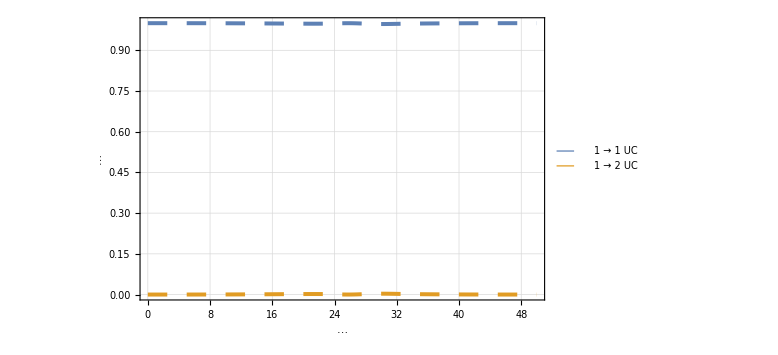

```mathematica
Plot[{Abs[({{1, 0}}).U[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).U[t].({{1}, {0}})]^2+Abs[({{0, 1}}).U[t].({{1}, {0}})]^2),Abs[({{0, 1}}).U[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).U[t].({{1}, {0}})]^2+Abs[({{0, 1}}).U[t].({{1}, {0}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{Style["(*GraphicsBox[{Thickness[0.023441162681669007`], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGIlIGYCYvldC/al6sk7GGitFL7QourQG9Htz/hB1sHn
BLvt7KtaDhJNMlMMLn+3R+frg9SraDk88HuZ8Hf+bzi/D6R/A4sDjL/Na4PF
nJ8sDnMWKe/881wTzk9NAwI2BN8YBC5LwPlgcwTE4ea1KrCrnpkiBrcPxoe5
B51vAjZQFGJP2h/7qvs/bhl7i0LNY3OA8c+AQA8nnH+ge1+TyWMeOP8giL9Y
CM4XqZxUcpZFxAFmPowPs999zdHlDDOE4HyYeTA+WN9mHocdwVYR/9XF4fy1
Qjp86fck4HzpeXGapw004fyaTxsCsn9pws2Dha/6J5WXszoF4Hywe5aIwvkz
ZgKBpQyc/2Xfx63pZbIO56+GvdG/reEQ8PbyxxmKcvD4R08PAE9E2P4=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJLIGYC4h0OTY+O31B3EKmcVHKWRcYBxpfftWBfqp+M
w6MI8e0XD6g7GBgDQbGMwya9vMWMcxD8jVC+PpTfwHK037AcIT9jAn+VWba6
Q8jbyx9nOGLyZZe/8NCLV3dQ/6TycpamjINoj9crFhN1h/Q0EJCG8LeoORzs
3tdkwizpcOFq2Bv92aoOZ0BgjajDjJlAYKkC53fbeO5Ka1KG8/fm17ydWars
sFZIhy/9nhicX3P/xy3j1+IOe9D4qOolHNzXHF3O0KHs8MA13nFWoaSD38WJ
Mf+SVR2eJC68ZqKv4uBzgt129lR1OD8+JEh9AacGnO+xv1bWwh2TP6W9Nery
HASfAQQeqDiIT73CmaGE4M9ZpLzzz3J1OP8pyJx+VThfZl6c5ukCNYfzoHCJ
1nBIANnfqeYgDRLfgOBPBtm3B8EH2/scwQfTnprQ8FRz+A8C9ZoOW8x/HEp5
pQrng+V3IvgbVJ80z9NVdVgPonM1If76o+KwGaRvlYYDC2eXfDKfCty9K769
rDhzQRHO548NuG8UjuCDzZXH5L8q3ir6OxvBh4Wn84RmoTQvBB8cb/sQ/NLD
21xn3lWG86tB8eyt5LAj2Cri/3FpiH4pJYcY1QiZczJSkPjmUHI4AEpviyXh
fFj6g/HByfOYGCRdXFRymAkOFxFIuKqrwPmQ+FKD82H5qz+i259xg7QDev4D
AHbzfLc=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJ5IGYC4tQ0IFim6xD09vLHGYyiDjA+iEo7Ju4QcEu6
JtFI18HEGAguSzqkxN5xY7bQgfMz8j+0nizRhvPBtLC2w5d9H7emT5OA8zU+
qbyc1SkO58eoRsicqxFzYOHskk/Og+o3FnU4fthpbaadDpy/VvVJ87xeBF9m
Xpzm6Qs6DiKVk0rOpog6uO+vlbVg13V44BrvOOuiqINoj9crFhFdiH0vRR3+
g4A8bv5fNP6b4q2iv7V1HRhAwAHBh4UPjN8f0e3PWCAMt/8zyL9hAg4tvP7r
pyzVdtjutcFiTiWXg8TUK5wZSdoO/k88L5kGc8L5YO985sDJ3wbWz+HwIEJ8
+8UGbYi7/7M7yCx/4aE3H8E/vmtHL9sFBB8Wf2dAgIffAT1+AcZ8zHk=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJLIGYC4hgFx4/JOaYOIpWTSs6yyDjA+PK7FuxL9ZNx
KFjTfTsjwdTBwBgIimUcIsS3X2Tww+TrQ/mOTY+Oz7BGyPucYLedbWrqEPL2
8scZjpj8CcElKtP1TR3UP6m8nKUp48DlplrKJGXqkJ4GAtIQ/i0Th4Pd+5pM
mCUdXmRpf5vua+JwBgTWiELoOcZwfo/XKxYTRwRf9UnzvLNWxg5rhXT40u+J
wfk193/cMn4t7qCCxkdVL+Hgf3FizD9nY4cHrvGOswolHVa88ND7b2ji8CRx
4TUTfRUHNZB6L1M430BrpfCFFgR/yf19fHMWY/KntLdGXZ6D4DOAwAMViPsn
Ivh+IPuDEfxPGwKyZ7mbwPk8/uunpO4wcTh/NeyNfrQGxP4jJg7S8+I0T29A
8CeD7NuD4Hvsr5W1eI7gJ4QEqS/w1ISGp4nDfxCo13S4JV2TaFSK4IPlYxD8
G0KfHM+LmTisBwVcrqbD6cNOazP/GTtsNv9xKGWVhkMjy9F+w3ZjuHt5Qe7N
MILz7UHpRRvBB5vLj8l/VbxV9Hc2gg8Lz9sg96ki+I9BdDyCXwLUdjrPGM73
BqW/pUYOO4KtIv4fl3awrYxYYdpr5BCjGiFzTkYKEt/NRg4HQOltsSScD0t/
MD44eR4Tc6j/bVVw7oWRw0wQ2CkCic/JxnA+OL6Om8D5sPzVH9Htz7hB2gE9
/wEAO+WEmw==
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAwBWIQ3RdcojI93tJBpHJSyVkWGQcYP+Tt5Y8zHGUcFt/f
xzcn2NLBwBgIimUcur1esZg4IvjeJ9htZ6si+OJTr3BmKFk6yO9asC/VT8YB
JGwsbOmwXkiHL71O2sHv4sSYf4ctHHYEW0X8Vxd3uC70yfG8m4XDGRBYI+qw
4oWH3v+H5nD+iyztb9P3IvgH25aHn5pk7vDANd5x1kUEnwEEHMThfPVPKi9n
dUo4fNoQkD1ru7mD+5qjyxl+SDpovOXdZ3DT3CE9DQSkHUq2iv4+vc7CodPG
c1eakhJUvQXE3cFKDraVEStMz1o4rPz2suLMAQQfHF4mynC+DygcTFUc/n4r
fTCn0MJhSntr1GUZVYeNenmLGe+Yw/kmIHMPm8H5EqDwCjKDuG+FIpzPHxtw
36gcwQ/nFGs3jleEuDfODOIeB0VIeBYj+OD460fwwfonmTl8WLRe4WwEVP88
M4e1oPhYp+iQEnvHjfmFmUMEyPz1yhD3xpg7/Hz7+oDlYhVIeF5C8E8edlqb
+Q7Bh8Q31L9zEPyZIHBTGc6vvP/jlrG1ssMW8x+HUn5B469QCR7f1SD514oO
B2plLdJLzCHpI10ezoekJ3mHGAXHj8k8sPiUgppn5tCuwK56xkQK7h+I+ZJw
/pd9H7emT5OA8/siuv0ZC8QcwMnAzRzi3p0i8PQB44Pj86MFnA/LH/0g/Ruk
HdDzDwDQs2oE
"], {{25.2781, 12.739099999999999`}, {25.2781, 12.917200000000001`}, {25.134399999999996`, 13.131299999999996`}, {24.873399999999997`, 13.131299999999996`}, {24.598399999999998`, 13.131299999999996`}, {24.2891, 12.8688}, {24.2891, 12.5594}, {24.2891, 12.260899999999998`}, {24.5391, 12.165599999999998`}, {24.6828, 12.165599999999998`}, {25.004699999999996`, 12.165599999999998`}, {25.2781, 12.4766}, {25.2781, 12.739099999999999`}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxdlQ1MW1UUx8tYhiw6HFtbPsrKa0twbG6TD53vvZb/08nULM6ACVU3EaV0
6hQUFocBl4iOMJjowjbARgfMsCU4NEoEDBXFpdMVWAMhZlPLDLoRQcUQAtm0
9t7bd1/0Ji/NLzfn63/OuRWeKct3Ret0uqjwVxH+VoQ/szL/rH9OwfqqY5Uj
K01Q+bG58fkWxQTfRvHYxWsKtmWFT4UJH8ibJ9p+0vjQDbF89JLG/ZeP/O0a
U2AeOOV1PRKx9ynoid+8xv16MpoXVxW1nFaQSu7PGVHXVfhd5n4FfnK69Zgu
bp/M3qoxtTdrTP3HKGglp19jHTkwcn4yzWkarU5AoKwoZjRRrS+J+0v/yzbT
Vp+EF2KXT7klBW+mxqT5J0wIkXNIwf3v1MaXigJn6+TPBTqPhfNn9yx9XbLa
htnbvNtaH1bQXPfWE+OmNKbPJDjfurun2VWu8ePGzwO6DcCuCzH293Js+PD6
g1tCX+Wy+vwW1BA9+3Jxp2Be2G+wYVfg3T3/FORy+1+IPmUOzkcLKm0ni+yc
aX5jMvPnsSJ9jiQo48rGlO5QtJXdN8lMr6dtGDocbkC8zO2pXaPE+cualO3u
bI0LSf6/i/B0WPtv+iL5fSoyf1NWyFXOMzk1Io9nPD4Ruy9fjMQVOMftfTSY
+arGhbGGuqwiAZW9+hsXnxJxdnHmoB8C81+h8Z7U8IA2atxE6m8S4SoNnzwB
NxcPTHnaRZBxzBqP3I+JqAouXc6SrGghcxMrYXnut6F7O204HfSu8dRqTO+/
1biL9OeqhLvlwfwTisY7yHwcsXJW66X+hiW4ST4GCy4M3/fRc+ck/NnRkzri
FNi+OCUcJPk0pODjLS91RpkkDDV438juTGR2qySsI/NakoCtGWfXXZoW0Vcg
OkPpBs53kPmd0XNm86/n9mw/1vP+qazGV1mtP5/se5Se5eOR+H7R+tolLHjn
e92Lelx7ftPiyUGJvQ/txsjcRu5PJLA+x8nsN2hi+VXKGCyrnms9LsA2Xfv+
yGsy26+BsB4rzzfd5ZPZfs1aULL3h7zo7XY4yTz0WNl9nZ3rT+f/DzvvzwJd
eAdnFldjGm91LmzUv5Xzzu7zXbolC2c2LxqzflnYXP3q4O+Bj/TT64CH6LNs
5szeDzNuyUs7sKLNwftL51Fx4G1nw+6o2xPwfXJ1cWaOA3kkvtOIb8j+WRyY
PfxiQ2aygbPaX5XV/tJ+7nDw/tH9eUVjJ9nPUY3tZB9/dGDqgSKlLaBn79FS
xH+9ke1HTy7fR/ou9Ub0OSOAjEdWBv67DwGNuxuu7NPFKZxpfjaF662yqrfK
9fJDA6UdAkj40HUgSPJbu4G93z6gjuiZnRypA2ik+iWx+J+A1fNyImd1/lSm
epcbUDw8vsl1FVwP+l5nKJypHn0aq/9/tB9fJOP//4//AvvkPH0=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGBQBmIQvfNW19/U6S4O6WkgIOUA48vvWrAvdZ2Ug96EBT8M
+1wcau7/uGX8WsrB4trRXJMOBN+h6dHxGc0I/ooXHnr/G10c/oPAfSmHtuXh
p4xKXBzuu8Y7ziqUcnjDu89gppCLg0jlpJKzKWIOM0Gg0dnhDAisEXU4oWk1
6bQ7gl//26rg3AcnOP93TO7Rf4ecHEyMgeCyOJw/HWROpDScDzafRQbO/7Lv
49Z0M1mHi/nx7OduOkHco6jgoP6ked5ZLWc4f6Ne3mLGEAQf7L/dzg7lh7e5
ztRVcGBZPMmKkdXFQfnao2CGOQoOtSD3VbhA3OejCA+PtUI6fOnrlOB8sLyM
MpzfANKnoQLxv6eLw5T21qjLMqoQdU+c4fwp39jiZ7gg+Pqg+Ihzgui7qQTn
w/wH47cqsKueMZGA+HcnVP1OEbh5MD44fkRc4HyU9HBM0gE9fQAAZ8MLqw==

"], {{40.6703, 9.556249999999999}, {40.6703, 8.304689999999999}, {38.762499999999996`, 8.304689999999999}, {38.262499999999996`, 8.304689999999999}, {37.7609, 8.304689999999999}, {38.2734, 10.1391}, {39.406299999999995`, 10.318799999999998`}, {39.787499999999994`, 10.318799999999998`}, {40.3125, 10.318799999999998`}, {40.6703, 10.007799999999998`}, {40.6703, 9.556249999999999}}}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{63.99483437110834, 24.508064757160646`},PlotRange->{{0., 42.660000000000004`}, {0., 16.34}}])",15],Style["(*GraphicsBox[{Thickness[0.018857250612860643`], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAwBmIQLVI5qeTsEmWHjPwPrSdD1B1gfOl5cZqnDTQdHrjG
O84SVHKQmHqFM+ORlkPA28sfZyjKwfmqn1RezjrJB+dv9dpgMecnD5wvs1Fs
PpMCJp+Fs0s+OQ/BlwHbh9AP4/M48nnNyOSD86NVI2TOyQhh8P+DgSacP6W9
NeryHtz818VbRX93azqcAYE3gnD/bgPbz+bwpi2322i3hINdiWPtaRk2h76I
bn9GAXGHF7WPs8+/YXVoVWBXPTNFzOEvyNr6f/YwPtg/D37B+RDzfmDwZ4LA
TlE438QYBEQd3oDMX/MLzhdvkplicPk3nJ8zNaHQovg/nH+we1+TyWJGh6r7
P24Ze4s69IPcWcAM588AW8QH54PdYSKAxhd0gJkHCx8Yf62QDl96HYIvDEof
LMIYfHB4SYvB+TD/uq85upxhhhCcD46m+4Jwfot4LWsmGx+c3wty/wdehxqQ
+14j+OB0mSIO54eA0uFCcbj+L/s+bk3/Jg5NT1DzTCTg/gH7Q08JYr+8FJzv
PKFZKC1KAc6HpX9wepmj4oCePwCVdT16
"], {{8.82031, 11.915599999999998`}, {8.82031, 11.6063}, {8.665629999999998, 10.592199999999998`}, {8.117189999999999, 10.0438}, {7.914059999999999, 9.82969}, {7.3421899999999996`, 9.37656}, {6.2562500000000005`, 9.37656}, {4.57656, 9.37656}, {5.387499999999999, 12.6313}, {5.4937499999999995`, 13.071899999999998`}, {5.54219, 13.095300000000002`}, {6.0062500000000005`, 13.095300000000002`}, {7.185939999999999, 13.095300000000002`}, {8.081249999999999, 13.095300000000002`}, {8.82031, 12.809399999999997`}, {8.82031, 11.915599999999998`}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxFk2tIFFEYhlfXDImU1F2tVndnZ2ZnZy9mrhqlwUcXu1BqFrmFWparXRHS
8EpGJpJmaam5JWr6QyxlhW4qKpYIUl6x+mGBBgaaSiEhltW2Z2b2zAfnxzMz
58z3vu/5iDPpcRapRCJxcazdjuXqWG4eJcqzd4LA7CEvNtlIcPKRyc35yVco
UNQlse/GjFBZXHRyQkGDHVW9AfNCxgvZ6lM95lCTo+7rYCb58cdQGwUhHLOQ
M7UyaYogobaR7PyTxsLb/l1t569RILt98Jtbphbvl6C6zmD+u3x1urZCgzkl
8XOU1F8DqVxRfL8jwr5pUnhOwyc2oNUuJaGm3Cs3fB0NPen5i9YqArNXYuxU
SJbI8Uj/KQKixysS/pE0tCzPZQ8BwZ8fLXJg8+z+oAKRb66PsVUW0WBBv40i
4PSxOKahhQYk2zQhvF+jEb539GN1VI4Gfi3O921voqCdnimsu8xg5vy1i/xs
28qbFJ0Wxj4cX9gSIfKe8kLv1BISs1Mvd94iA2moH7kafqNz+hn40WhTDZsJ
wT8GslEepQF8DnUa6CvtvRHatJHPL0MDPjn3ModT/GGwq6PMPVgDHUd3mO2M
HLN2iZp7OCfDzPkPMrwfybR2+sJXdA9GReby3MBg5v1jQNXV0GvxlMFzpOcJ
A69RP1I5n3s3A75cP3KhXy3sax1oltQECPq0UGYujXFpD4TwyJ646i9aSKDN
ipFuJZ+LOwtt3gbPtCQVBOtafMYoltc3o8L3MQ/5MU9A3lJ77MVcFm5FHuhK
VatBgfJW6iCr/+Ve62GS969DJ+RLwrTZ79W4RA9GQvnzklzIr16P8+Pythow
j6IcV0WevaBffpBohE1ozsopGELVauT9OUHxc/TdAIcG1+58FEZBG8q3zIDn
1clcvlqRufyr1RCG/HAx8vffooYCt4G7W+NF9qt673HONQizc/45f1dEdv7v
P3WExDg=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{21.2359, 8.57813}, {21.2359, 9.71094}, {20.496899999999997`, 10.5563}, {19.412499999999998`, 10.5563}, {17.8391, 10.5563}, {16.2891, 8.840629999999999}, {16.2891, 7.159379999999999}, {16.2891, 6.02656}, {17.0281, 5.1812499999999995`}, {18.112499999999997`, 5.1812499999999995`}, {19.698400000000003`, 5.1812499999999995`}, {21.2359, 6.8968799999999995`}, {21.2359, 8.57813}}, CompressedData["
1:eJxTTMoPSmViYGAQBmIQDQYFJg63NWXX/GdWcoDxwznF2o35FSF8AxMHkcpJ
JWdZZB026uUtZtxj7BCjGiFzTkbKoWSr6O/TdsYONfd/3DJ+LeZwXeiT4/lp
Rg5nQGCNqMN/EJBH8BtZjvYbthvC+elpQCBm6NCqwK56Zoo4nA8xTwrOh9gn
69AfXKIyPd7QofzwNteZfxUcbkvXJBptNXRYK6TDl66n5HD6sNPaTDsjB9+L
E2P+Mas4qL/l3Wfw0sjh59vXBywXq0DMSzOG88H++YPgw/wfAfL/emUH9PAB
ADKNeF8=
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGDQBGIQvb9W1iLdxMohnFOs3The0QHGX/HtZcWZCcoO3ifY
bWdPtXSY0t4adVlG1UF6Xpzm6Q0WcP6yFx56/wURfImpVzgzmswddBXlv+SI
qTjw+a+fkuph7nAGBOYoOzSyHO03VLeA8Hu0HLaY/ziUomXhoK+1UvjCEi2H
wjXdtzMMLBwSQoLUF5xE8OcsUt755zmC38ILNFhV22GjXt5iRh7cfL+LE2P+
JZs7pKcBAZu2AwMIGJg7PIgQ336RQRviXiZzh4z8D60nv2g5ODQ9Oj7jtJkD
C2eXfPI7Lah/zCD0Iy2Iu3PMHDaA7LmD4IPV5yH4MqBwMtBymDGBv8qsG8Hn
clMtZVqF4HuBwtfVHINf82lDQPYvTTgfHL57EPyAW9I1iZM0HWwrI1aY6po7
mNnsDZr2UANijoK5g2iP1yuWEg2HL0BjZl03g4SnpppDyVbR36f/mTrEqEbI
nNsj5zAhuERl+ntTh4r7P24Zd8vC+W/acruNdsvA+WD1Mgg+OBwdxB1eZGl/
mz7XzGEmCOwUgYc3jP9l562uv0ct4HxY+jIxBoLL0g7o6Q8AseMHzA==
"], CompressedData["
1:eJxTTMoPSmViYGAQAWIQvVEvbzHjGQsH9U8qL2d1Sjn8B4F6C4cv+z5uTf8m
7rDk/j6+OZ/NHc6AwBpRh0aWo/2G6Qi+1wl229msCL7qk+Z5Z2eZOTxwjXec
dVEMzoeZD+PHqEbInJORgZi/2MxBpHJSyVkWWYj8LTOH8sPbXGfqKjjIzIvT
PK1g7mAMAsFKDjeEPjmeVzN3uK0pu+Z/s5LDtAn8VWa3zR1+vn19wHKxisMW
8x+HUlZZwPnSIP0GlnB+hPj2iwx5lg4ZaUAwTRnO/7BovcLZCCU4/w7IfGNF
B17/9VNSJSzh7kMPLwCx0pM9
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{28.593799999999987`, 5.871880000000001}, {28.593799999999987`, 6.2171899999999996`}, {28.3078, 6.456250000000001}, {28.021900000000002`, 6.456250000000001}, {27.674999999999997`, 6.456250000000001}, {27.437499999999996`, 6.17031}, {27.437499999999996`, 5.88438}, {27.437499999999996`, 5.539059999999999}, {27.723399999999994`, 5.300000000000001}, {28.009399999999996`, 5.300000000000001}, {28.354699999999998`, 5.300000000000001}, {28.593799999999987`, 5.585939999999999}, {28.593799999999987`, 5.871880000000001}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJ5IGYC4jMg8MbeIejt5Y8zGEUdYPw0EDgm7nCgbXn4
qU32DibGQHBZ0sHnBLvtbFMk/sWJMf8u28H5YHqxncOXfR+3pk+TgPM1Pqm8
nNUpDufHqEbInKsRc5CZF6d5+gJUv7GoQ+1vq4JzFvZwfv6a7tsZCQj+0hce
ev8b7R1EKieVnE0RdbCtjFhhOtfe4YFrvOOsi6IOS+7v45uz2B5i30tRhxkz
gWAlbv50NH5/cInK9PX2Dgwg4IDgw8IHxu+P6PZnLBCG2/8Z5N8wAYcYBceP
yW/sHLZ7bbCYU8nloPKked7ZU3YO/k88L5kGc8L5YO985sDJ3wbWz+HA4aZa
ynTLzuE/GLA7aLzl3WfwEsH/8630wRxGezgfFn9gmoffAT1+Af1C3uk=
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAwBmIQfaBW1iL9jqtDRv6H1pMh6g4wvvS8OM3TBpoOXzYE
ZM8qd3WQmHqFM+ORlsPOW11/U7e7wPnHNa0mnb7vBOerPmmed/YQgn9buibR
aCsmn4WzSz45D8GXAduH0A/jX8yPZz93E8Ev2Sr6+7SZMwb/PxhowvlT2luj
Lu/BzX9dDGR0azrU/7YqOGfgDPcv2P4kJ4c3bbndRrslHFgXT7JiDHVy6Ivo
9mcUEHdY/sJD73+gk0OrArvqmSliDk8SF14zee4I59/fxzfH+BSC/zsm9+i/
XZj8mSCwUxTONzEGAVEHd9VSplknEHyw/y8i+CBnn36H4At/cjyfxuvkUHX/
xy1jb1GI/VoI/hkQuIPgg837icaXdIabBwsfGB/sPicEvzJihenZYEw+OLyk
xeB8mH91Jyz4YejmjBpe+gi+fdOj4zMuO6GG3yUnhxqQ+14j+CKVk0rOpojD
+SFvL3+csVAcrv/Lvo9b07+JQ9LTVah5JhJw/6wV0uFL11OC2G/uAueD/c/p
CufD0j84vcxRcUDPHwCDDFd4
"], {{42.720299999999995`, 11.915599999999998`}, {42.720299999999995`, 11.6063}, {42.565599999999996`, 10.592199999999998`}, {42.0172, 10.0438}, {41.814099999999996`, 9.82969}, {41.2422, 9.37656}, {40.156299999999995`, 9.37656}, {38.47659999999999, 9.37656}, {39.287499999999994`, 12.6313}, {39.3938, 13.071899999999998`}, {39.44219999999999, 13.095300000000002`}, {39.906299999999995`, 13.095300000000002`}, {41.08590000000001, 13.095300000000002`}, {41.981300000000005`, 13.095300000000002`}, {42.720299999999995`, 12.809399999999997`}, {42.720299999999995`, 11.915599999999998`}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{44.7688, 8.459380000000001}, {44.7688, 8.634379999999998}, {44.64059999999999, 8.760939999999998}, {44.45779999999999, 8.760939999999998}, {44.251599999999996`, 8.760939999999998}, {44.021899999999995`, 8.57031}, {44.021899999999995`, 8.331249999999999}, {44.021899999999995`, 8.156249999999998}, {44.148399999999995`, 8.02969}, {44.3313, 8.02969}, {44.537499999999994`, 8.02969}, {44.7688, 8.22031}, {44.7688, 8.459380000000001}}, CompressedData["
1:eJxTTMoPSmViYGAwB2IQ7XOC3XZ2qZtD5f0ft4y7hRxg/GjVCJlzd6D8XDeH
VgV21TNfhBzSwADBf7CPb45xFIJvce1orkkEVP8eIYdb0jWJRqFuDtUg87OF
HBQcPyafsXVz+A8C+/kdNurlLWYUcXNIBRmrxuuQw/lzQfprVzj/SeLCayb3
EfxfMblH/11ydbjBe1sstQzBf1H7OPu8Dj+cPxMEIgUclr3w0Pt/09XhDAi8
EYCY99zVQf2TystZLwUdSraK/j7N5uYQA3JvjQjEf2puDn0R3f6MAuIOO291
/U3Vh4bPaXEHh6ZHx2dYu0HUHZOA8x+6xjvOCpSE83cEW0X8fy4FcY+Qm4NI
5aSSsywycP/A+AdqZS3SaxD8i/nx7OcCXR0egMybKA7ng81TR/DXCunwpd8T
c6j9bVVwLsLVYQ2Iv0/MIaREZfr/BARfb8KCH4Z5CD7Y/nxXB4VdC/alvhOD
xF+RqwMDCDiIQ8KjD+oeFylI/O91dQh4e/njDEVpSHzdQfDB+l8h+GD/fHF1
cF9zdDnDDyk4vx2UPkQQ/APd+5pMDktC4vuzKzz8erxesZi8dIWknxgJSHo5
6+pQBQp/bTEHialXODM2QcNHUATODwLZzygCcf80aHgdF4SE10RXB3mQf/0E
IemgB5EeYPxgkP5EBD8dFL/LoOlxs6uDfYlj7ekYbrj7YPwNoPDwcYPzYfkH
bJ4iIj/B8hcANHN/1g==
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJJIGYC4h6vVywmje4OvRHd/owGPA4wfvDbyx9nKAo4
uKmWMs3KcHfYGWwV8b9d0GGjXt5iRhsEn8d//ZRUCTR5FneHg937mkwWC8D5
BctLNvzr54fzW8RrWTOP8TrsvNX1N1Xc3eE/GHA7sCyeZMVoi+CLfHI8nxaK
4E/5xhY/I8XdwcQYCD7z4OT7P/G8ZHqZwyENBMKg8sasqPbZM0LEhd0dCkHu
42eE+F/Q3aEfFB4fGOB86Y1i85kWIPj2JY61p2UYHBIOX9ZOlXR3yJmaUGhR
/N8eHB4KCD7YPToIPix8GUDgAIsDevgDAFc8oR4=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}}}, {{{50.882799999999996`, 8.459380000000001}, {50.882799999999996`, 8.60938}, {50.762499999999996`, 8.760939999999998}, {50.57189999999999, 8.760939999999998}, {50.3344, 8.760939999999998}, {50.12659999999999, 8.53906}, {50.12659999999999, 8.331249999999999}, {50.12659999999999, 8.181249999999999}, {50.2469, 8.02969}, {50.43749999999999, 8.02969}, {50.675, 8.02969}, {50.882799999999996`, 8.25156}, {50.882799999999996`, 8.459380000000001}}, CompressedData["
1:eJxTTMoPSmViYGAwAGIQrTthwQ9DN0+Hmvs/bhm/Fnfo9nrFYuLp6XAGBHwk
HIxBwNvTQX7Xgn2pfQj+zmCriP/sknD+DhD/uJTDPBudK7PkPB1EKieVnGWR
cbBvenR8xmMPOP/zhoDsWeUIvqtqKdMsCw+HB67xjrMmisP5YPPUEfy1Qjp8
6ffEHI5rWk06be/hsAbE3wfluyP4v2Jyj/4LQvA36uUtZgzxcPiy7+PW9Gti
EPdGezj0RXT7MwaIO1zMj2c/V+nhEPz28scZjZIO3ifYbWev9XAIAPEVpR14
/NdPSX2A4Ms7fkw+8xXBX/7CQ+8/IzR81knB+WD5hZJwPtg+A0mH1d23Mxj+
w9wnAXHfHw94eO+vlbVIn+Ph4P/E85LpZQ4HlsWTrBh7PRwmgPR/YIG7v3B5
yYZ/5xkcbkrXJBrJIvhgc3gQfB+Qf/66Q/j8jA4OoPj47e4gvVFsPpMCI8Q8
aWj4iDE5PE5ceM1EHuqeM8xwvgxIfQILnJ8GAs9Y4fZt9dpgMWcnm8MXUPx+
d4fzl4H8fxPBB6ePfe4OB7v3NZkos8L56p9UXs7iZIbzwe5bwODQtjz8lNET
dwcW/V9cl3j+2euB0qucB5wPlo9B45/xgPirmNHhDe8+g5mvoOEpzOmAnt4B
eMpEFw==
"]}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{79.54099128268992, 24.508064757160646`},PlotRange->{{0., 53.03}, {0., 16.34}}])", 15]}, PlotLegends->Placed[{"1 → 1 UC", "1 → 2 UC"},Right],ImageSize->Large, PlotStyle->{{Dashing[Large],Thickness[0.005]},{Dashing[Large],Thickness[0.005]}, {Dashing[Medium],Thickness[0.005]}, {Dashing[Medium],Thickness[0.005]},{Dashing[Small],Thickness[0.005]},{Dashing[Small],Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

### 4b

```mathematica
(*transition probabilities for P(-,i)*)
```

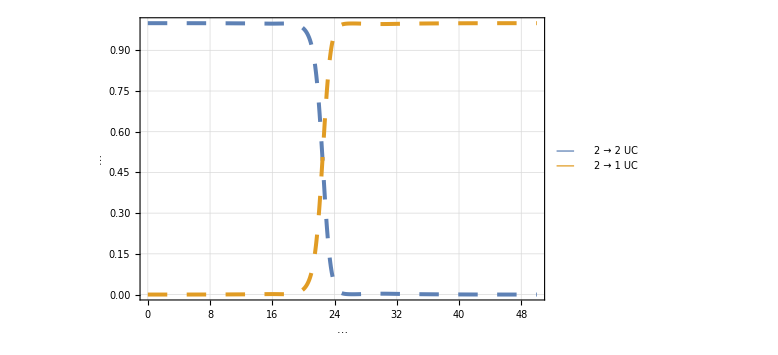

```mathematica
Plot[{Abs[({{0, 1}}).U[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).U[t].({{0}, {1}})]^2+Abs[({{0, 1}}).U[t].({{0}, {1}})]^2),Abs[({{1, 0}}).U[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).U[t].({{0}, {1}})]^2+Abs[({{0, 1}}).U[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{Style["(*GraphicsBox[{Thickness[0.023441162681669007`], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGIlIGYCYvldC/al6sk7GGitFL7QourQG9Htz/hB1sHn
BLvt7KtaDhJNMlMMLn+3R+frg9SraDk88HuZ8Hf+bzi/D6R/A4sDjL/Na4PF
nJ8sDnMWKe/881wTzk9NAwI2BN8YBC5LwPlgcwTE4ea1KrCrnpkiBrcPxoe5
B51vAjZQFGJP2h/7qvs/bhl7i0LNY3OA8c+AQA8nnH+ge1+TyWMeOP8giL9Y
CM4XqZxUcpZFxAFmPowPs999zdHlDDOE4HyYeTA+WN9mHocdwVYR/9XF4fy1
Qjp86fck4HzpeXGapw004fyaTxsCsn9pws2Dha/6J5WXszoF4Hywe5aIwvkz
ZgKBpQyc/2Xfx63pZbIO56+GvdG/reEQ8PbyxxmKcvD4R08PAE9E2P4=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJLIGYC4h0OTY+O31B3EKmcVHKWRcYBxpfftWBfqp+M
w6MI8e0XD6g7GBgDQbGMwya9vMWMcxD8jVC+PpTfwHK037AcIT9jAn+VWba6
Q8jbyx9nOGLyZZe/8NCLV3dQ/6TycpamjINoj9crFhN1h/Q0EJCG8LeoORzs
3tdkwizpcOFq2Bv92aoOZ0BgjajDjJlAYKkC53fbeO5Ka1KG8/fm17ydWars
sFZIhy/9nhicX3P/xy3j1+IOe9D4qOolHNzXHF3O0KHs8MA13nFWoaSD38WJ
Mf+SVR2eJC68ZqKv4uBzgt129lR1OD8+JEh9AacGnO+xv1bWwh2TP6W9Nery
HASfAQQeqDiIT73CmaGE4M9ZpLzzz3J1OP8pyJx+VThfZl6c5ukCNYfzoHCJ
1nBIANnfqeYgDRLfgOBPBtm3B8EH2/scwQfTnprQ8FRz+A8C9ZoOW8x/HEp5
pQrng+V3IvgbVJ80z9NVdVgPonM1If76o+KwGaRvlYYDC2eXfDKfCty9K769
rDhzQRHO548NuG8UjuCDzZXH5L8q3ir6OxvBh4Wn84RmoTQvBB8cb/sQ/NLD
21xn3lWG86tB8eyt5LAj2Cri/3FpiH4pJYcY1QiZczJSkPjmUHI4AEpviyXh
fFj6g/HByfOYGCRdXFRymAkOFxFIuKqrwPmQ+FKD82H5qz+i259xg7QDev4D
AHbzfLc=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJ5IGYC4tQ0IFim6xD09vLHGYyiDjA+iEo7Ju4QcEu6
JtFI18HEGAguSzqkxN5xY7bQgfMz8j+0nizRhvPBtLC2w5d9H7emT5OA8zU+
qbyc1SkO58eoRsicqxFzYOHskk/Og+o3FnU4fthpbaadDpy/VvVJ87xeBF9m
Xpzm6Qs6DiKVk0rOpog6uO+vlbVg13V44BrvOOuiqINoj9crFhFdiH0vRR3+
g4A8bv5fNP6b4q2iv7V1HRhAwAHBh4UPjN8f0e3PWCAMt/8zyL9hAg4tvP7r
pyzVdtjutcFiTiWXg8TUK5wZSdoO/k88L5kGc8L5YO985sDJ3wbWz+HwIEJ8
+8UGbYi7/7M7yCx/4aE3H8E/vmtHL9sFBB8Wf2dAgIffAT1+AcZ8zHk=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJLIGYC4hgFx4/JOaYOIpWTSs6yyDjA+PK7FuxL9ZNx
KFjTfTsjwdTBwBgIimUcIsS3X2Tww+TrQ/mOTY+Oz7BGyPucYLedbWrqEPL2
8scZjpj8CcElKtP1TR3UP6m8nKUp48DlplrKJGXqkJ4GAtIQ/i0Th4Pd+5pM
mCUdXmRpf5vua+JwBgTWiELoOcZwfo/XKxYTRwRf9UnzvLNWxg5rhXT40u+J
wfk193/cMn4t7qCCxkdVL+Hgf3FizD9nY4cHrvGOswolHVa88ND7b2ji8CRx
4TUTfRUHNZB6L1M430BrpfCFFgR/yf19fHMWY/KntLdGXZ6D4DOAwAMViPsn
Ivh+IPuDEfxPGwKyZ7mbwPk8/uunpO4wcTh/NeyNfrQGxP4jJg7S8+I0T29A
8CeD7NuD4Hvsr5W1eI7gJ4QEqS/w1ISGp4nDfxCo13S4JV2TaFSK4IPlYxD8
G0KfHM+LmTisBwVcrqbD6cNOazP/GTtsNv9xKGWVhkMjy9F+w3ZjuHt5Qe7N
MILz7UHpRRvBB5vLj8l/VbxV9Hc2gg8Lz9sg96ki+I9BdDyCXwLUdjrPGM73
BqW/pUYOO4KtIv4fl3awrYxYYdpr5BCjGiFzTkYKEt/NRg4HQOltsSScD0t/
MD44eR4Tc6j/bVVw7oWRw0wQ2CkCic/JxnA+OL6Om8D5sPzVH9Htz7hB2gE9
/wEAO+WEmw==
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAwBWIQ3RdcojI93tJBpHJSyVkWGQcYP+Tt5Y8zHGUcFt/f
xzcn2NLBwBgIimUcur1esZg4IvjeJ9htZ6si+OJTr3BmKFk6yO9asC/VT8YB
JGwsbOmwXkiHL71O2sHv4sSYf4ctHHYEW0X8Vxd3uC70yfG8m4XDGRBYI+qw
4oWH3v+H5nD+iyztb9P3IvgH25aHn5pk7vDANd5x1kUEnwEEHMThfPVPKi9n
dUo4fNoQkD1ru7mD+5qjyxl+SDpovOXdZ3DT3CE9DQSkHUq2iv4+vc7CodPG
c1eakhJUvQXE3cFKDraVEStMz1o4rPz2suLMAQQfHF4mynC+DygcTFUc/n4r
fTCn0MJhSntr1GUZVYeNenmLGe+Yw/kmIHMPm8H5EqDwCjKDuG+FIpzPHxtw
36gcwQ/nFGs3jleEuDfODOIeB0VIeBYj+OD460fwwfonmTl8WLRe4WwEVP88
M4e1oPhYp+iQEnvHjfmFmUMEyPz1yhD3xpg7/Hz7+oDlYhVIeF5C8E8edlqb
+Q7Bh8Q31L9zEPyZIHBTGc6vvP/jlrG1ssMW8x+HUn5B469QCR7f1SD514oO
B2plLdJLzCHpI10ezoekJ3mHGAXHj8k8sPiUgppn5tCuwK56xkQK7h+I+ZJw
/pd9H7emT5OA8/siuv0ZC8QcwMnAzRzi3p0i8PQB44Pj86MFnA/LH/0g/Ruk
HdDzDwDQs2oE
"], {{25.2781, 12.739099999999999`}, {25.2781, 12.917200000000001`}, {25.134399999999996`, 13.131299999999996`}, {24.873399999999997`, 13.131299999999996`}, {24.598399999999998`, 13.131299999999996`}, {24.2891, 12.8688}, {24.2891, 12.5594}, {24.2891, 12.260899999999998`}, {24.5391, 12.165599999999998`}, {24.6828, 12.165599999999998`}, {25.004699999999996`, 12.165599999999998`}, {25.2781, 12.4766}, {25.2781, 12.739099999999999`}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxdlQ1MW1UUx8tYhiw6HFtbPsrKa0twbG6TD53vvZb/08nULM6ACVU3EaV0
6hQUFocBl4iOMJjowjbARgfMsCU4NEoEDBXFpdMVWAMhZlPLDLoRQcUQAtm0
9t7bd1/0Ji/NLzfn63/OuRWeKct3Ret0uqjwVxH+VoQ/szL/rH9OwfqqY5Uj
K01Q+bG58fkWxQTfRvHYxWsKtmWFT4UJH8ibJ9p+0vjQDbF89JLG/ZeP/O0a
U2AeOOV1PRKx9ynoid+8xv16MpoXVxW1nFaQSu7PGVHXVfhd5n4FfnK69Zgu
bp/M3qoxtTdrTP3HKGglp19jHTkwcn4yzWkarU5AoKwoZjRRrS+J+0v/yzbT
Vp+EF2KXT7klBW+mxqT5J0wIkXNIwf3v1MaXigJn6+TPBTqPhfNn9yx9XbLa
htnbvNtaH1bQXPfWE+OmNKbPJDjfurun2VWu8ePGzwO6DcCuCzH293Js+PD6
g1tCX+Wy+vwW1BA9+3Jxp2Be2G+wYVfg3T3/FORy+1+IPmUOzkcLKm0ni+yc
aX5jMvPnsSJ9jiQo48rGlO5QtJXdN8lMr6dtGDocbkC8zO2pXaPE+cualO3u
bI0LSf6/i/B0WPtv+iL5fSoyf1NWyFXOMzk1Io9nPD4Ruy9fjMQVOMftfTSY
+arGhbGGuqwiAZW9+hsXnxJxdnHmoB8C81+h8Z7U8IA2atxE6m8S4SoNnzwB
NxcPTHnaRZBxzBqP3I+JqAouXc6SrGghcxMrYXnut6F7O204HfSu8dRqTO+/
1biL9OeqhLvlwfwTisY7yHwcsXJW66X+hiW4ST4GCy4M3/fRc+ck/NnRkzri
FNi+OCUcJPk0pODjLS91RpkkDDV438juTGR2qySsI/NakoCtGWfXXZoW0Vcg
OkPpBs53kPmd0XNm86/n9mw/1vP+qazGV1mtP5/se5Se5eOR+H7R+tolLHjn
e92Lelx7ftPiyUGJvQ/txsjcRu5PJLA+x8nsN2hi+VXKGCyrnms9LsA2Xfv+
yGsy26+BsB4rzzfd5ZPZfs1aULL3h7zo7XY4yTz0WNl9nZ3rT+f/DzvvzwJd
eAdnFldjGm91LmzUv5Xzzu7zXbolC2c2LxqzflnYXP3q4O+Bj/TT64CH6LNs
5szeDzNuyUs7sKLNwftL51Fx4G1nw+6o2xPwfXJ1cWaOA3kkvtOIb8j+WRyY
PfxiQ2aygbPaX5XV/tJ+7nDw/tH9eUVjJ9nPUY3tZB9/dGDqgSKlLaBn79FS
xH+9ke1HTy7fR/ou9Ub0OSOAjEdWBv67DwGNuxuu7NPFKZxpfjaF662yqrfK
9fJDA6UdAkj40HUgSPJbu4G93z6gjuiZnRypA2ik+iWx+J+A1fNyImd1/lSm
epcbUDw8vsl1FVwP+l5nKJypHn0aq/9/tB9fJOP//4//AvvkPH0=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGBQBmIQvfNW19/U6S4O6WkgIOUA48vvWrAvdZ2Ug96EBT8M
+1wcau7/uGX8WsrB4trRXJMOBN+h6dHxGc0I/ooXHnr/G10c/oPAfSmHtuXh
p4xKXBzuu8Y7ziqUcnjDu89gppCLg0jlpJKzKWIOM0Gg0dnhDAisEXU4oWk1
6bQ7gl//26rg3AcnOP93TO7Rf4ecHEyMgeCyOJw/HWROpDScDzafRQbO/7Lv
49Z0M1mHi/nx7OduOkHco6jgoP6ked5ZLWc4f6Ne3mLGEAQf7L/dzg7lh7e5
ztRVcGBZPMmKkdXFQfnao2CGOQoOtSD3VbhA3OejCA+PtUI6fOnrlOB8sLyM
MpzfANKnoQLxv6eLw5T21qjLMqoQdU+c4fwp39jiZ7gg+Pqg+Ihzgui7qQTn
w/wH47cqsKueMZGA+HcnVP1OEbh5MD44fkRc4HyU9HBM0gE9fQAAZ8MLqw==

"], {{40.6703, 9.556249999999999}, {40.6703, 8.304689999999999}, {38.762499999999996`, 8.304689999999999}, {38.262499999999996`, 8.304689999999999}, {37.7609, 8.304689999999999}, {38.2734, 10.1391}, {39.406299999999995`, 10.318799999999998`}, {39.787499999999994`, 10.318799999999998`}, {40.3125, 10.318799999999998`}, {40.6703, 10.007799999999998`}, {40.6703, 9.556249999999999}}}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{63.99483437110834, 24.508064757160646`},PlotRange->{{0., 42.660000000000004`}, {0., 16.34}}])",15],Style["(*GraphicsBox[{Thickness[0.018857250612860643`], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAwBmIQLVI5qeTsEmWHjPwPrSdD1B1gfOl5cZqnDTQdHrjG
O84SVHKQmHqFM+ORlkPA28sfZyjKwfmqn1RezjrJB+dv9dpgMecnD5wvs1Fs
PpMCJp+Fs0s+OQ/BlwHbh9AP4/M48nnNyOSD86NVI2TOyQhh8P+DgSacP6W9
NeryHtz818VbRX93azqcAYE3gnD/bgPbz+bwpi2322i3hINdiWPtaRk2h76I
bn9GAXGHF7WPs8+/YXVoVWBXPTNFzOEvyNr6f/YwPtg/D37B+RDzfmDwZ4LA
TlE438QYBEQd3oDMX/MLzhdvkplicPk3nJ8zNaHQovg/nH+we1+TyWJGh6r7
P24Ze4s69IPcWcAM588AW8QH54PdYSKAxhd0gJkHCx8Yf62QDl96HYIvDEof
LMIYfHB4SYvB+TD/uq85upxhhhCcD46m+4Jwfot4LWsmGx+c3wty/wdehxqQ
+14j+OB0mSIO54eA0uFCcbj+L/s+bk3/Jg5NT1DzTCTg/gH7Q08JYr+8FJzv
PKFZKC1KAc6HpX9wepmj4oCePwCVdT16
"], {{8.82031, 11.915599999999998`}, {8.82031, 11.6063}, {8.665629999999998, 10.592199999999998`}, {8.117189999999999, 10.0438}, {7.914059999999999, 9.82969}, {7.3421899999999996`, 9.37656}, {6.2562500000000005`, 9.37656}, {4.57656, 9.37656}, {5.387499999999999, 12.6313}, {5.4937499999999995`, 13.071899999999998`}, {5.54219, 13.095300000000002`}, {6.0062500000000005`, 13.095300000000002`}, {7.185939999999999, 13.095300000000002`}, {8.081249999999999, 13.095300000000002`}, {8.82031, 12.809399999999997`}, {8.82031, 11.915599999999998`}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxFk2tIFFEYhlfXDImU1F2tVndnZ2ZnZy9mrhqlwUcXu1BqFrmFWparXRHS
8EpGJpJmaam5JWr6QyxlhW4qKpYIUl6x+mGBBgaaSiEhltW2Z2b2zAfnxzMz
58z3vu/5iDPpcRapRCJxcazdjuXqWG4eJcqzd4LA7CEvNtlIcPKRyc35yVco
UNQlse/GjFBZXHRyQkGDHVW9AfNCxgvZ6lM95lCTo+7rYCb58cdQGwUhHLOQ
M7UyaYogobaR7PyTxsLb/l1t569RILt98Jtbphbvl6C6zmD+u3x1urZCgzkl
8XOU1F8DqVxRfL8jwr5pUnhOwyc2oNUuJaGm3Cs3fB0NPen5i9YqArNXYuxU
SJbI8Uj/KQKixysS/pE0tCzPZQ8BwZ8fLXJg8+z+oAKRb66PsVUW0WBBv40i
4PSxOKahhQYk2zQhvF+jEb539GN1VI4Gfi3O921voqCdnimsu8xg5vy1i/xs
28qbFJ0Wxj4cX9gSIfKe8kLv1BISs1Mvd94iA2moH7kafqNz+hn40WhTDZsJ
wT8GslEepQF8DnUa6CvtvRHatJHPL0MDPjn3ModT/GGwq6PMPVgDHUd3mO2M
HLN2iZp7OCfDzPkPMrwfybR2+sJXdA9GReby3MBg5v1jQNXV0GvxlMFzpOcJ
A69RP1I5n3s3A75cP3KhXy3sax1oltQECPq0UGYujXFpD4TwyJ646i9aSKDN
ipFuJZ+LOwtt3gbPtCQVBOtafMYoltc3o8L3MQ/5MU9A3lJ77MVcFm5FHuhK
VatBgfJW6iCr/+Ve62GS969DJ+RLwrTZ79W4RA9GQvnzklzIr16P8+Pythow
j6IcV0WevaBffpBohE1ozsopGELVauT9OUHxc/TdAIcG1+58FEZBG8q3zIDn
1clcvlqRufyr1RCG/HAx8vffooYCt4G7W+NF9qt673HONQizc/45f1dEdv7v
P3WExDg=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{21.2359, 8.57813}, {21.2359, 9.71094}, {20.496899999999997`, 10.5563}, {19.412499999999998`, 10.5563}, {17.8391, 10.5563}, {16.2891, 8.840629999999999}, {16.2891, 7.159379999999999}, {16.2891, 6.02656}, {17.0281, 5.1812499999999995`}, {18.112499999999997`, 5.1812499999999995`}, {19.698400000000003`, 5.1812499999999995`}, {21.2359, 6.8968799999999995`}, {21.2359, 8.57813}}, CompressedData["
1:eJxTTMoPSmViYGAQBmIQDQYFJg63NWXX/GdWcoDxwznF2o35FSF8AxMHkcpJ
JWdZZB026uUtZtxj7BCjGiFzTkbKoWSr6O/TdsYONfd/3DJ+LeZwXeiT4/lp
Rg5nQGCNqMN/EJBH8BtZjvYbthvC+elpQCBm6NCqwK56Zoo4nA8xTwrOh9gn
69AfXKIyPd7QofzwNteZfxUcbkvXJBptNXRYK6TDl66n5HD6sNPaTDsjB9+L
E2P+Mas4qL/l3Wfw0sjh59vXBywXq0DMSzOG88H++YPgw/wfAfL/emUH9PAB
ADKNeF8=
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGDQBGIQvb9W1iLdxMohnFOs3The0QHGX/HtZcWZCcoO3ifY
bWdPtXSY0t4adVlG1UF6Xpzm6Q0WcP6yFx56/wURfImpVzgzmswddBXlv+SI
qTjw+a+fkuph7nAGBOYoOzSyHO03VLeA8Hu0HLaY/ziUomXhoK+1UvjCEi2H
wjXdtzMMLBwSQoLUF5xE8OcsUt755zmC38ILNFhV22GjXt5iRh7cfL+LE2P+
JZs7pKcBAZu2AwMIGJg7PIgQ336RQRviXiZzh4z8D60nv2g5ODQ9Oj7jtJkD
C2eXfPI7Lah/zCD0Iy2Iu3PMHDaA7LmD4IPV5yH4MqBwMtBymDGBv8qsG8Hn
clMtZVqF4HuBwtfVHINf82lDQPYvTTgfHL57EPyAW9I1iZM0HWwrI1aY6po7
mNnsDZr2UANijoK5g2iP1yuWEg2HL0BjZl03g4SnpppDyVbR36f/mTrEqEbI
nNsj5zAhuERl+ntTh4r7P24Zd8vC+W/acruNdsvA+WD1Mgg+OBwdxB1eZGl/
mz7XzGEmCOwUgYc3jP9l562uv0ct4HxY+jIxBoLL0g7o6Q8AseMHzA==
"], CompressedData["
1:eJxTTMoPSmViYGAQAWIQvVEvbzHjGQsH9U8qL2d1Sjn8B4F6C4cv+z5uTf8m
7rDk/j6+OZ/NHc6AwBpRh0aWo/2G6Qi+1wl229msCL7qk+Z5Z2eZOTxwjXec
dVEMzoeZD+PHqEbInJORgZi/2MxBpHJSyVkWWYj8LTOH8sPbXGfqKjjIzIvT
PK1g7mAMAsFKDjeEPjmeVzN3uK0pu+Z/s5LDtAn8VWa3zR1+vn19wHKxisMW
8x+HUlZZwPnSIP0GlnB+hPj2iwx5lg4ZaUAwTRnO/7BovcLZCCU4/w7IfGNF
B17/9VNSJSzh7kMPLwCx0pM9
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{28.593799999999987`, 5.871880000000001}, {28.593799999999987`, 6.2171899999999996`}, {28.3078, 6.456250000000001}, {28.021900000000002`, 6.456250000000001}, {27.674999999999997`, 6.456250000000001}, {27.437499999999996`, 6.17031}, {27.437499999999996`, 5.88438}, {27.437499999999996`, 5.539059999999999}, {27.723399999999994`, 5.300000000000001}, {28.009399999999996`, 5.300000000000001}, {28.354699999999998`, 5.300000000000001}, {28.593799999999987`, 5.585939999999999}, {28.593799999999987`, 5.871880000000001}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJ5IGYC4jMg8MbeIejt5Y8zGEUdYPw0EDgm7nCgbXn4
qU32DibGQHBZ0sHnBLvtbFMk/sWJMf8u28H5YHqxncOXfR+3pk+TgPM1Pqm8
nNUpDufHqEbInKsRc5CZF6d5+gJUv7GoQ+1vq4JzFvZwfv6a7tsZCQj+0hce
ev8b7R1EKieVnE0RdbCtjFhhOtfe4YFrvOOsi6IOS+7v45uz2B5i30tRhxkz
gWAlbv50NH5/cInK9PX2Dgwg4IDgw8IHxu+P6PZnLBCG2/8Z5N8wAYcYBceP
yW/sHLZ7bbCYU8nloPKked7ZU3YO/k88L5kGc8L5YO985sDJ3wbWz+HA4aZa
ynTLzuE/GLA7aLzl3WfwEsH/8630wRxGezgfFn9gmoffAT1+Af1C3uk=
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAwBmIQfaBW1iL9jqtDRv6H1pMh6g4wvvS8OM3TBpoOXzYE
ZM8qd3WQmHqFM+ORlsPOW11/U7e7wPnHNa0mnb7vBOerPmmed/YQgn9buibR
aCsmn4WzSz45D8GXAduH0A/jX8yPZz93E8Ev2Sr6+7SZMwb/PxhowvlT2luj
Lu/BzX9dDGR0azrU/7YqOGfgDPcv2P4kJ4c3bbndRrslHFgXT7JiDHVy6Ivo
9mcUEHdY/sJD73+gk0OrArvqmSliDk8SF14zee4I59/fxzfH+BSC/zsm9+i/
XZj8mSCwUxTONzEGAVEHd9VSplknEHyw/y8i+CBnn36H4At/cjyfxuvkUHX/
xy1jb1GI/VoI/hkQuIPgg837icaXdIabBwsfGB/sPicEvzJihenZYEw+OLyk
xeB8mH91Jyz4YejmjBpe+gi+fdOj4zMuO6GG3yUnhxqQ+14j+CKVk0rOpojD
+SFvL3+csVAcrv/Lvo9b07+JQ9LTVah5JhJw/6wV0uFL11OC2G/uAueD/c/p
CufD0j84vcxRcUDPHwCDDFd4
"], {{42.720299999999995`, 11.915599999999998`}, {42.720299999999995`, 11.6063}, {42.565599999999996`, 10.592199999999998`}, {42.0172, 10.0438}, {41.814099999999996`, 9.82969}, {41.2422, 9.37656}, {40.156299999999995`, 9.37656}, {38.47659999999999, 9.37656}, {39.287499999999994`, 12.6313}, {39.3938, 13.071899999999998`}, {39.44219999999999, 13.095300000000002`}, {39.906299999999995`, 13.095300000000002`}, {41.08590000000001, 13.095300000000002`}, {41.981300000000005`, 13.095300000000002`}, {42.720299999999995`, 12.809399999999997`}, {42.720299999999995`, 11.915599999999998`}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{44.7688, 8.459380000000001}, {44.7688, 8.634379999999998}, {44.64059999999999, 8.760939999999998}, {44.45779999999999, 8.760939999999998}, {44.251599999999996`, 8.760939999999998}, {44.021899999999995`, 8.57031}, {44.021899999999995`, 8.331249999999999}, {44.021899999999995`, 8.156249999999998}, {44.148399999999995`, 8.02969}, {44.3313, 8.02969}, {44.537499999999994`, 8.02969}, {44.7688, 8.22031}, {44.7688, 8.459380000000001}}, CompressedData["
1:eJxTTMoPSmViYGAwB2IQ7XOC3XZ2qZtD5f0ft4y7hRxg/GjVCJlzd6D8XDeH
VgV21TNfhBzSwADBf7CPb45xFIJvce1orkkEVP8eIYdb0jWJRqFuDtUg87OF
HBQcPyafsXVz+A8C+/kdNurlLWYUcXNIBRmrxuuQw/lzQfprVzj/SeLCayb3
EfxfMblH/11ydbjBe1sstQzBf1H7OPu8Dj+cPxMEIgUclr3w0Pt/09XhDAi8
EYCY99zVQf2TystZLwUdSraK/j7N5uYQA3JvjQjEf2puDn0R3f6MAuIOO291
/U3Vh4bPaXEHh6ZHx2dYu0HUHZOA8x+6xjvOCpSE83cEW0X8fy4FcY+Qm4NI
5aSSsywycP/A+AdqZS3SaxD8i/nx7OcCXR0egMybKA7ng81TR/DXCunwpd8T
c6j9bVVwLsLVYQ2Iv0/MIaREZfr/BARfb8KCH4Z5CD7Y/nxXB4VdC/alvhOD
xF+RqwMDCDiIQ8KjD+oeFylI/O91dQh4e/njDEVpSHzdQfDB+l8h+GD/fHF1
cF9zdDnDDyk4vx2UPkQQ/APd+5pMDktC4vuzKzz8erxesZi8dIWknxgJSHo5
6+pQBQp/bTEHialXODM2QcNHUATODwLZzygCcf80aHgdF4SE10RXB3mQf/0E
IemgB5EeYPxgkP5EBD8dFL/LoOlxs6uDfYlj7ekYbrj7YPwNoPDwcYPzYfkH
bJ4iIj/B8hcANHN/1g==
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJJIGYC4h6vVywmje4OvRHd/owGPA4wfvDbyx9nKAo4
uKmWMs3KcHfYGWwV8b9d0GGjXt5iRhsEn8d//ZRUCTR5FneHg937mkwWC8D5
BctLNvzr54fzW8RrWTOP8TrsvNX1N1Xc3eE/GHA7sCyeZMVoi+CLfHI8nxaK
4E/5xhY/I8XdwcQYCD7z4OT7P/G8ZHqZwyENBMKg8sasqPbZM0LEhd0dCkHu
42eE+F/Q3aEfFB4fGOB86Y1i85kWIPj2JY61p2UYHBIOX9ZOlXR3yJmaUGhR
/N8eHB4KCD7YPToIPix8GUDgAIsDevgDAFc8oR4=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}}}, {{{50.882799999999996`, 8.459380000000001}, {50.882799999999996`, 8.60938}, {50.762499999999996`, 8.760939999999998}, {50.57189999999999, 8.760939999999998}, {50.3344, 8.760939999999998}, {50.12659999999999, 8.53906}, {50.12659999999999, 8.331249999999999}, {50.12659999999999, 8.181249999999999}, {50.2469, 8.02969}, {50.43749999999999, 8.02969}, {50.675, 8.02969}, {50.882799999999996`, 8.25156}, {50.882799999999996`, 8.459380000000001}}, CompressedData["
1:eJxTTMoPSmViYGAwAGIQrTthwQ9DN0+Hmvs/bhm/Fnfo9nrFYuLp6XAGBHwk
HIxBwNvTQX7Xgn2pfQj+zmCriP/sknD+DhD/uJTDPBudK7PkPB1EKieVnGWR
cbBvenR8xmMPOP/zhoDsWeUIvqtqKdMsCw+HB67xjrMmisP5YPPUEfy1Qjp8
6ffEHI5rWk06be/hsAbE3wfluyP4v2Jyj/4LQvA36uUtZgzxcPiy7+PW9Gti
EPdGezj0RXT7MwaIO1zMj2c/V+nhEPz28scZjZIO3ifYbWev9XAIAPEVpR14
/NdPSX2A4Ms7fkw+8xXBX/7CQ+8/IzR81knB+WD5hZJwPtg+A0mH1d23Mxj+
w9wnAXHfHw94eO+vlbVIn+Ph4P/E85LpZQ4HlsWTrBh7PRwmgPR/YIG7v3B5
yYZ/5xkcbkrXJBrJIvhgc3gQfB+Qf/66Q/j8jA4OoPj47e4gvVFsPpMCI8Q8
aWj4iDE5PE5ceM1EHuqeM8xwvgxIfQILnJ8GAs9Y4fZt9dpgMWcnm8MXUPx+
d4fzl4H8fxPBB6ePfe4OB7v3NZkos8L56p9UXs7iZIbzwe5bwODQtjz8lNET
dwcW/V9cl3j+2euB0qucB5wPlo9B45/xgPirmNHhDe8+g5mvoOEpzOmAnt4B
eMpEFw==
"]}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{79.54099128268992, 24.508064757160646`},PlotRange->{{0., 53.03}, {0., 16.34}}])", 15]}, PlotLegends->Placed[{"2 → 2 UC", "2 → 1 UC"},Right],ImageSize->Large, PlotStyle->{{Dashing[Large],Thickness[0.005]},{Dashing[Large],Thickness[0.005]}, {Dashing[Medium],Thickness[0.005]}, {Dashing[Medium],Thickness[0.005]},{Dashing[Small],Thickness[0.005]},{Dashing[Small],Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

## Dynamics using ϕ=π (Fig. 5)

### Functions used for numerics

```mathematica
σx=({{0, 1}, {1, 0}});
σy=({{0, -ⅈ}, {ⅈ, 0}});
σz=({{1, 0}, {0, -1}});
```

```mathematica
(*choosen contour*)
ΔCircPath:=Function[{Δ0,φ,x},
Δ0 Sin[2 π x+φ]
];

ΩCircPath:=Function[{Δ0,Ω0,φ,x},
Ω0 + Δ0 Cos[2π x+φ]
];
(*time dependant parametrization of contour for single (ωCirc1) and double loop (ωCirc1DL)*)
ωCirc1:=#1(6(#3/#2)^5-15(#3/#2)^4+10(#3/#2)^3)&;
ωCirc1DL:=(ωCirc1[#1,#2,#3]UnitStep[#2-#3]+((#1)+ωCirc1[#1,#2,#3-#2])UnitStep[#3-#2])&;
```

```mathematica
(*constucting the holomorphic eigenvalue, works for a double loop*)
EigCircPath:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},

(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2)

];
```

```mathematica
(*constucting the derivative of the holomorphic eigenvalue, works for a double loop*)
EigDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])(2 ⅈ π Δ0 (Γ Cos[φ+2 π ω[dir,t0,t]]+2 ⅈ Ω0 Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,1][ω][dir,t0,t])/(√(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]]))
];
```

```mathematica
(*constucting the holomorphic pseduo rotation angle into the adiabatic frame, works for a double loop*)θDiagCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
-2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)+(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]
];
```

```mathematica
(*constucting the derivative of the pseduo rotation angle into the adiabatic frame.*)
θDiagDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(4 π Δ0 (2 Δ0+2 Ω0 Cos[φ+2 π ω[dir,t0,t]]+ⅈ Γ Sin[φ+2 π ω[dir,t0,t]]))/(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])Derivative[0,0,1][ω][dir,t0,t]
];
```

```mathematica
(*constucting the 2nd derivative of the pseduo rotation angle into the adiabatic frame.*)
θDiagDDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(4 π Δ0 (2 π (Γ^2+4 (Δ0-Ω0) (Δ0+Ω0)) (-ⅈ Γ Cos[φ+2 π ω[dir,t0,t]]+2 Ω0 Sin[φ+2 π ω[dir,t0,t]]) (Derivative[0,0,1][ω][dir,t0,t])^2+(4 Δ0 (-Γ^2+2 Δ0^2+4 Ω0^2)-2 Ω0 (Γ^2-4 (3 Δ0^2+Ω0^2)) Cos[φ+2 π ω[dir,t0,t]]+2 Δ0 (Γ^2+4 Ω0^2) Cos[2 (φ+2 π ω[dir,t0,t])]+ⅈ Γ (-Γ^2+4 (3 Δ0^2+Ω0^2)+16 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]) Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,2][ω][dir,t0,t]))/(Γ^2-4 (Δ0^2+Ω0^2)-8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]-4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])^2
];
```

```mathematica
(*the adiabatic Hamiltonian*)
DynMatAd:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
-EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σz-1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σy
];
```

```mathematica
(*the SATD correction Hamiltonian in the adiabatic frame*)
WSATDAd:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
1/2(1/(4 EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]^2+θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]^2))(2EigDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t] θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]-2EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t] θDiagDDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])σx
];
```

```mathematica
(*solving for the UC dynamics in the adiabatic frame*)
SolCircPathAdDoubleLoop:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{U},
First[U[t]/.NDSolve[{U'[t]==-ⅈ DynMatAd[Δ0,Ω0,Γ,φ,ω,dir,t0,t].U[t],U[0]==IdentityMatrix[2]},U,{t,0,2t0},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->30,MaxSteps->10^6,Method->{"DiscontinuityProcessing" -> False }]]
]
];
```

```mathematica
(*solving for final transition probabilities given loop time*)
FinalAmp:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{U,UC},
(*finding the flow matrix at the final loop time*)
U= SolCircPathAdDoubleLoop[Δ0,Ω0,Γ,φ,ω,dir,t0]/.t->t0;
(*all the transition probabilities for the gain and loss modes*)
UC=Flatten[{Abs[({{1, 0}}).U.({{1}, {0}})]^2/(Abs[({{1, 0}}).U.({{1}, {0}})]^2+Abs[({{0, 1}}).U.({{1}, {0}})]^2),Abs[({{0, 1}}).U.({{1}, {0}})]^2/(Abs[({{1, 0}}).U.({{1}, {0}})]^2+Abs[({{0, 1}}).U.({{1}, {0}})]^2),Abs[({{1, 0}}).U.({{0}, {1}})]^2/(Abs[({{1, 0}}).U.({{0}, {1}})]^2+Abs[({{0, 1}}).U.({{0}, {1}})]^2),Abs[({{0, 1}}).U.({{0}, {1}})]^2/(Abs[({{1, 0}}).U.({{0}, {1}})]^2+Abs[({{0, 1}}).U.({{0}, {1}})]^2)}];
(*outputing results as a list of lists. this was done so for previous numerical reasons not relevant to this paper (explained in comments under "Data for 5c/5d"), and while may seem uncessary, the code used to generate the results in the paper require this formalism.*)
{UC}
]
];
```

### Data for 5c/5d

```mathematica
(*note that the data here includes more elements than the numerical function "FinalAmp" would suggest. this is becasue when generating the data for the transition probabilities, we simultaneous compared those results with the 2nd and 4th order Magnus Expansion estimates for the transition probabilities. However for this notebook we have eliminated all references to the Magnus results, except the in final output data. Each element follows this description: {loop time, {{transition probabilities},{2nd order Mag Expansion transition probabilities}, {4th order Mag Expansion transition probabilities}}. For the results outputed in this folder, we eliminated the code that generated the Magnus Expansion results as they were not needed. All the relevant data is stored in these data cells nonetheless.*)
```

```mathematica
FinalprobsUCMag={{0.1,{0.9990327882893095,0.9992079933422964}},{0.2,{0.9957292469175251,0.9971337170948087}},{0.30000000000000004,{0.9894088097181869,0.9941631255369954}},{0.4,{0.9792947069818068,0.9906029556108147}},{0.5,{0.9645377397198309,0.986693034761129}},{0.6,{0.9442631353014663,0.9826179264012869}},{0.7000000000000001,{0.9176458493189129,0.9785173221588088}},{0.8,{0.8840154381705234,0.9744949687426111}},{0.9,{0.8429834401686734,0.9706261366212858}},{1.,{0.794574667529989,0.9669637516156663}},{1.1,{0.7393322271501412,0.9635433590128999}},{1.2000000000000002,{0.6783605610056745,0.9603871003691943}},{1.3,{0.6132778554238322,0.9575068735216319}},{1.4,{0.5460709850860822,0.954906827353783}},{1.5,{0.47887647781888365,0.9525853208499411}},{1.6,{0.4137363700083887,0.950536454336893}},{1.7000000000000002,{0.35238538453113005,0.9487512611979495}},{1.8000000000000003,{0.29611211246233976,0.9472186313837636}},{1.9000000000000001,{0.24570995724000438,0.9459260238188629}},{2.,{0.20150705317081966,0.9448600131117397}},{2.1,{0.16344835777832306,0.9440067065044783}},{2.2,{0.1312000244016622,0.9433520594035705}},{2.3000000000000003,{0.10425220994424503,0.9428821117866095}},{2.4000000000000004,{0.08200599688425418,0.9425831629923361}},{2.5000000000000004,{0.06383881369987991,0.9424418986237711}},{2.6000000000000005,{0.04914869447756473,0.9424454803218929}},{2.7000000000000006,{0.03738081487782663,0.942581606834018}},{2.8000000000000007,{0.028040723704627946,0.9428385529681464}},{2.9000000000000004,{0.0206984443351647,0.9432051915902122}},{3.0000000000000004,{0.014986839684710923,0.9436710026954901}},{3.1000000000000005,{0.010596743248225059,0.9442260727041206}},{3.2000000000000006,{0.007270566771950719,0.9448610864398606}},{3.3000000000000003,{0.004795475199154862,0.9455673137100977}},{3.4000000000000004,{0.0029967728361137403,0.9463365919805675}},{3.5000000000000004,{0.0017318425341722368,0.9471613063059153}},{3.6000000000000005,{0.000884786459414795,0.9480343674162055}},{3.7,{0.0003618004890661563,0.9489491886551664}},{3.8000000000000003,{0.00008724899660697928,0.9498996623054955}},{3.9000000000000004,{3.7423740970204215*^-7,0.9508801357109059}},{4.,{0.00005256194796637562,0.9518853875060117}},{4.1,{0.00020508368321837692,0.9529106041881162}},{4.199999999999999,{0.00042724146487357363,0.9539513572044328}},{4.3,{0.0006948482037683204,0.9550035806811552}},{4.3999999999999995,{0.0009889861555512545,0.9560635498839222}},{4.5,{0.0012949942979456886,0.9571278604705241}},{4.6,{0.001601643437099003,0.9581934085743822}},{4.699999999999999,{0.0019004648331321658,0.9592573717401353}},{4.8,{0.002185204133591212,0.9603171907192548}},{4.9,{0.0024513774662278036,0.961370552123499}},{5.,{0.002695910762761054,0.9624153719262525}},{5.1000000000000005,{0.002916846872434899,0.9634497797958799}},{5.2,{0.0031131078876361464,0.9644721042409768}},{5.300000000000001,{0.00328430244480302,0.9654808585441839}},{5.4,{0.0034305696719129225,0.9664747274589999}},{5.5,{0.0035524530058879955,0.967452554642524}},{5.6000000000000005,{0.0036507983642586036,0.9684133307960694}},{5.7,{0.0037266721793238573,0.9693561824850949}},{5.8,{0.003781295634317917,0.9702803616097015}},{5.9,{0.003815992116182278,0.9711852354970317}},{6.,{0.0038321454480525294,0.9720702775871681}},{6.1000000000000005,{0.003831166910568647,0.9729350586845567}},{6.2,{0.0038144694241448065,0.9737792387475461}},{6.300000000000001,{0.003783447559994496,0.9746025591892677}},{6.4,{0.0037394622890169074,0.9754048356637093}},{6.5,{0.0036838295745228538,0.9761859513116521}},{6.6,{0.003617812075826226,0.9769458504418405}},{6.7,{0.0035426133615391433,0.9776845326235305}},{6.8,{0.0034593741393501303,0.9784020471673912}},{6.9,{0.003369170097719838,0.9790984879724204}},{7.,{0.0032730110276302654,0.9797739887173719}},{7.1,{0.003171840952345392,0.9804287183759075}},{7.2,{0.0030665390423590595,0.9810628770353809}},{7.3,{0.002957921133162334,0.9816766919999159}},{7.3999999999999995,{0.0028467416968977356,0.9822704141590314}},{7.5,{0.0027336961464189628,0.9828443146037519}},{7.6,{0.0026194233729805766,0.9833986814726646}},{7.7,{0.002504508437457014,0.9839338170109772}},{7.8,{0.0023894853504172874,0.9844500348260498}},{7.9,{0.0022748398890571433,0.984947657323368}},{8.,{0.002161012409461754,0.9854270133072168}},{8.1,{0.002048400621260727,0.985888435730619}},{8.2,{0.0019373622987947914,0.986332259579355}},{8.299999999999999,{0.001828217908710677,0.9867588198749114}},{8.4,{0.0017212531386328618,0.9871684497812846}},{8.5,{0.0016167213154336401,0.9875614788004043}},{8.6,{0.0015148457047721344,0.9879382310407183}},{8.7,{0.0014158216861314375,0.988299023543098}},{8.799999999999999,{0.0013198187996779805,0.9886441646475737}},{8.9,{0.0012269826629397835,0.9889739523836829}},{9.,{0.0011374367566950284,0.98928867286612}},{9.1,{0.0010512840805839184,0.9895885986760496}},{9.200000000000001,{0.0009686086799127043,0.989873987206716}},{9.3,{0.0008894770458982852,0.9901450789500182}},{9.4,{0.0008139393923626325,0.9904020956977936}},{9.5,{0.0007420308124826731,0.9906452386287197}},{9.6,{0.0006737723198748258,0.9908746862475126}},{9.700000000000001,{0.0006091717789214841,0.9910905921383216}},{9.8,{0.0005482247299030047,0.991293082488338}},{9.9,{0.0004909151152255538,0.9914822533302597}},{10.000000000000002,{0.00043721591380399164,0.9916581674433194}},{10.100000000000001,{0.00038708969149904473,0.9918208508415441}},{10.200000000000001,{0.00034048907641334226,0.9919702887642423}},{10.3,{0.0002973571688010727,0.9921064210669005}},{10.4,{0.00025762789634602097,0.9922291368895183}},{10.5,{0.0002212263265355225,0.9923382684533608}},{10.6,{0.00018806894882113017,0.9924335838040431}},{10.7,{0.0001580639400937722,0.9925147782775691}},{10.8,{0.00013111142770600237,0.9925814644133063}},{10.9,{0.00010710376472997481,0.9926331599710331}},{11.,{0.00008592583228032416,0.9926692736236966}},{11.1,{0.00006745538351173799,0.9926890877867404}},{11.2,{0.000051563443180332094,0.9926917379017787}},{11.3,{0.000038114775429719026,0.9926761873049931}},{11.4,{0.00002696843065721546,0.9926411965638999}},{11.5,{0.000017978379904823298,0.9925852858389205}},{11.600000000000001,{0.00001099424223542211,0.9925066883880095}},{11.700000000000001,{5.862107025227573*^-6,0.9924032927417177}},{11.8,{2.4254491598489327*^-6,0.9922725702692178}},{11.9,{5.261308459975815*^-7,0.9921114837473471}},{12.,{5.479385129432964*^-9,0.991916371000314}},{12.1,{7.054259638799588*^-7,0.9916827955043493}},{12.2,{2.4696865483529685*^-6,0.9914053527557707}},{12.299999999999999,{5.144962567623195*^-6,0.9910774167293182}},{12.4,{8.582136450326915*^-6,0.9906908042057596}},{12.5,{0.00001263743543760762,0.9902353250095116}},{12.6,{0.00001717353657641165,0.9896981714714843}},{12.7,{0.000022060586478817258,0.9890630777597863}},{12.799999999999999,{0.000027177111319389458,0.9883091441180293}},{12.9,{0.00003241079555854808,0.9874091639255299}},{13.,{0.0000376591118760896,0.9863271976376213}},{13.1,{0.00004282978956116263,0.9850149793745977}},{13.200000000000001,{0.000047841113869667606,0.9834064671112251}},{13.3,{0.00005262205433882586,0.981409354602333}},{13.4,{0.00005711222544542778,0.9788914467730152}},{13.5,{0.00006126168803369165,0.9756580249801883}},{13.6,{0.00006503060438094466,0.9714127255607634}},{13.700000000000001,{0.00006838876342745482,0.9656867437575763}},{13.8,{0.00007131499544846446,0.9577036320098443}},{13.9,{0.000073796497230273,0.9461041459448534}},{14.000000000000002,{0.00007582808963476755,0.9283423550216116}},{14.100000000000001,{0.0000774114293571687,0.8992369911575085}},{14.200000000000001,{0.000078554195803798,0.8471333589268706}},{14.3,{0.00007926927247848184,0.7428680780880623}},{14.4,{0.00007957394021922868,0.5121055889117021}},{14.5,{0.00007948909723396511,0.09746495568439138}},{14.6,{0.00007903851829554639,0.13073394262316682}},{14.7,{0.00007824816281342966,0.5584707103427043}},{14.8,{0.000077145538921442,0.7798020083074454}},{14.9,{0.00007575912829804324,0.8761175668317126}},{15.,{0.00007411787424813139,0.9227920559538377}},{15.1,{0.00007225073365364183,0.9481290360246163}},{15.2,{0.00007018629178597548,0.963171348180272}},{15.3,{0.0000679524376585619,0.9727364786032622}},{15.4,{0.00006557609658080754,0.9791519069734058}},{15.5,{0.00006308301583415729,0.9836405579636497}},{15.600000000000001,{0.00006049759889701954,0.9868903027303044}},{15.700000000000001,{0.00005784278336588447,0.9893102401083625}},{15.8,{0.00005513995762989231,0.9911551771906658}},{15.9,{0.00005240891139972686,0.9925900955907481}},{16.,{0.00004966781536721691,0.9937253956806668}},{16.1,{0.00004693322552137576,0.9946370755362217}},{16.200000000000003,{0.00004422010796370295,0.9953787527081698}},{16.3,{0.00004154188041774608,0.9959890778052358}},{16.400000000000002,{0.000038910467001426074,0.9964964466083515}},{16.5,{0.000036336363208690004,0.996922076090515}},{16.6,{0.00003382870841829411,0.997282060582531}},{16.700000000000003,{0.00003139536360471463,0.9975887756659223}},{16.8,{0.000029042992260472753,0.9978518551628982}},{16.900000000000002,{0.000026777142849687816,0.998078882858613}},{17.000000000000004,{0.000024602331394333114,0.9982758899776027}},{17.1,{0.000022522123048416747,0.9984477181077502}},{17.200000000000003,{0.00002053921174097839,0.9985982874499665}},{17.3,{0.000018655497165965602,0.9987307974890575}},{17.400000000000002,{0.000016872158568258483,0.9988478787845032}},{17.500000000000004,{0.000015189724924880664,0.9989517089714839}},{17.6,{0.000013608141242210487,0.9990441022588245}},{17.700000000000003,{0.000012126830799367418,0.9991265790933144}},{17.800000000000004,{0.00001074475325230917,0.9992004208356442}},{17.900000000000002,{9.460458587159026*^-6,0.9992667130054607}},{18.000000000000004,{8.272136968675176*^-6,0.9993263797338409}},{18.1,{7.177664576218433*^-6,0.999380211398095}},{18.200000000000003,{6.174645556514344*^-6,0.999428886930216}},{18.300000000000004,{5.260450249221103*^-6,0.9994729919345127}},{18.400000000000002,{4.432249863479833*^-6,0.9995130334856647}},{18.500000000000004,{3.6870477970861645*^-6,0.9995494522807213}},{18.600000000000005,{3.0217078008764073*^-6,0.9995826326692167}},{18.700000000000003,{2.43297919690261*^-6,0.9996129109720742}},{18.800000000000004,{1.9175193622255598*^-6,0.9996405824130695}},{18.900000000000002,{1.4719136910927917*^-6,0.999665906919581}},{19.000000000000004,{1.0926932478678914*^-6,0.9996891139973555}},{19.100000000000005,{7.763503207548564*^-7,0.9997104068434464}},{19.200000000000003,{5.193520839213389*^-7,0.9997299658295934}},{19.300000000000004,{3.1815257238297995*^-7,0.9997479514631297}},{19.400000000000006,{1.6920317030068425*^-7,0.9997645069125662}},{19.500000000000004,{6.896180978279312*^-8,0.9997797601690374}},{19.600000000000005,{1.3901073414420394*^-8,0.9997938259020228}},{19.700000000000003,{5.153897296369697*^-10,0.9998068070574916}},{19.800000000000004,{2.532750665961251*^-8,0.9998187962382725}},{19.900000000000006,{8.489442333089004*^-8,0.9998298768997103}},{20.000000000000004,{1.7581295528221625*^-7,0.9998401243881464}},{20.1,{2.947251018841709*^-7,0.9998496068452569}},{20.200000000000003,{4.383233770979651*^-7,0.9998583859975598}},{20.3,{6.03356255310046*^-7,0.9998665178473533}},{20.400000000000002,{7.86633872315552*^-7,0.9998740532788023}},{20.5,{9.850341073078355*^-7,0.9998810385908065}},{20.6,{1.1955091540808616*^-6,0.9998875159664927}},{20.700000000000003,{1.4150926689565817*^-6,0.9998935238877532}},{20.8,{1.6409075579592212*^-6,0.9998990975019857}},{20.900000000000002,{1.8701744371051551*^-6,0.9999042689471802}},{21.000000000000004,{2.1002207669475965*^-6,0.9999090676406122}},{21.1,{2.3284906261885084*^-6,0.9999135205356722}},{21.200000000000003,{2.5525550495879957*^-6,0.9999176523507337}},{21.3,{2.7701228137818982*^-6,0.9999214857734311}},{21.400000000000002,{2.9790515117335233*^-6,0.9999250416432597}},{21.500000000000004,{3.1773587144466636*^-6,0.9999283391150392}},{21.6,{3.363232978646168*^-6,0.9999313958054235}},{21.700000000000003,{3.5350444239827373*^-6,0.9999342279243796}},{21.800000000000004,{3.6913545746180335*^-6,0.999936850393305}},{21.900000000000002,{3.83092514120883*^-6,0.9999392769512231}},{22.000000000000004,{3.952725410647008*^-6,0.9999415202503449}},{22.1,{4.055937916437486*^-6,0.9999435919420961}},{22.200000000000003,{4.139962082063664*^-6,0.9999455027545865}},{22.300000000000004,{4.204415564053689*^-6,0.9999472625623669}},{22.400000000000002,{4.249133071234245*^-6,0.9999488804492225}},{22.500000000000004,{4.274162499690417*^-6,0.9999503647646396}},{22.600000000000005,{4.2797582975176116*^-6,0.9999517231745263}},{22.700000000000003,{4.26637205757633*^-6,0.9999529627066545}},{22.800000000000004,{4.234640423637402*^-6,0.9999540897912629}},{22.900000000000002,{4.1853704849455275*^-6,0.9999551102971708}},{23.000000000000004,{4.119522918430755*^-6,0.9999560295637046}},{23.100000000000005,{4.0381932141076535*^-6,0.9999568524286916}},{23.200000000000003,{3.942591382879181*^-6,0.9999575832527148}},{23.300000000000004,{3.834020593428222*^-6,0.9999582259397813}},{23.400000000000006,{3.713855214528893*^-6,0.9999587839545032}},{23.500000000000004,{3.5835187487009*^-6,0.9999592603358461}},{23.600000000000005,{3.4444621338268676*^-6,0.9999596577074451}},{23.700000000000003,{3.2981428610583154*^-6,0.9999599782844327}},{23.800000000000004,{3.146005313546963*^-6,0.9999602238766708}},{23.900000000000006,{2.9894626731532536*^-6,0.999960395888206}},{24.000000000000004,{2.829880675750276*^-6,0.9999604953126958}},{24.1,{2.6685634232742135*^-6,0.9999605227244698}},{24.200000000000003,{2.5067413868346396*^-6,0.9999604782647806}},{24.3,{2.3455616624320204*^-6,0.9999603616226902}},{24.400000000000002,{2.1860804737569585*^-6,0.9999601720098823}},{24.5,{2.0292578558919404*^-6,0.9999599081285213}},{24.6,{1.8759544027919249*^-6,0.9999595681310606}},{24.700000000000003,{1.7269299201415772*^-6,0.9999591495706339}},{24.8,{1.5828437945434853*^-6,0.9999586493403361}},{24.900000000000002,{1.4442568697242731*^-6,0.999958063599267}},{25.000000000000004,{1.3116346088939743*^-6,0.9999573876827125}},{25.1,{1.1853513214411147*^-6,0.9999566159931128}},{25.200000000000003,{1.065695235365444*^-6,0.9999557418676627}},{25.3,{9.528742088591475*^-7,0.9999547574172236}},{25.400000000000002,{8.470218893975974*^-7,0.9999536533297929}},{25.500000000000004,{7.482041468665992*^-7,0.9999524186298703}},{25.6,{6.564256279158124*^-7,0.9999510403825285}},{25.700000000000003,{5.716362997535629*^-7,0.999949503327639}},{25.800000000000004,{4.937378728164833*^-7,0.9999477894251738}},{25.900000000000002,{4.225900121741564*^-7,0.999945877286363}},{26.000000000000004,{3.5801626671611033*^-7,0.9999437414570499}},{26.1,{2.9980966270559753*^-7,0.9999413515079055}},{26.200000000000003,{2.4773792398158445*^-7,0.9999386708697647}},{26.300000000000004,{2.0154829482641583*^-7,0.9999356553290855}},{26.400000000000002,{1.6097195326193055*^-7,0.9999322510650642}},{26.500000000000004,{1.257280123792202*^-7,0.9999283920611283}},{26.600000000000005,{9.552711534404408*^-8,0.9999239966512207}},{26.700000000000003,{7.007463608665755*^-8,0.9999189628524292}},{26.800000000000004,{4.907350262164354*^-8,0.9999131619685716}},{26.900000000000002,{3.222666349942955*^-8,0.9999064296883371}},{27.000000000000004,{1.9239220409052627*^-8,0.9998985534845115}},{27.100000000000005,{9.820251465841714*^-9,0.9998892544383545}},{27.200000000000003,{3.684350485409357*^-9,0.999878160466568}},{27.300000000000004,{5.529076490680024*^-10,0.999864765944358}},{27.400000000000006,{1.551565994292774*^-10,0.9998483691699147}},{27.500000000000004,{2.229012230175405*^-9,0.9998279725285338}},{27.600000000000005,{6.521722388263466*^-9,0.999802117452946}},{27.700000000000003,{1.2790355456971555*^-8,0.999768600307085}},{27.800000000000004,{2.0802144411521676*^-8,0.9997239593559253}},{27.900000000000006,{3.0334706489087947*^-8,0.9996624939105103}},{28.000000000000004,{4.117615614196878*^-8,0.9995742536886152}},{28.1,{5.3125127480622156*^-8,0.9994405421950527}},{28.200000000000003,{6.599072098207462*^-8,0.999222664953842}},{28.3,{7.959238787665205*^-8,0.9988291753598784}},{28.400000000000002,{9.375976432374115*^-8,0.9979973834161464}},{28.5,{1.0833246626724514*^-7,0.9956867832976409}},{28.6,{1.2315985473064363*^-7,0.9838720807223785}},{28.700000000000003,{1.3810078023749382*^-7,0.027221041248793782}},{28.8,{1.5302331410511815*^-7,0.9835956073464217}},{28.900000000000002,{1.678044734185905*^-7,0.9960740950165732}},{29.000000000000004,{1.8232994569406645*^-7,0.9983225425204132}},{29.1,{1.964938184536265*^-7,0.9990909168494455}},{29.200000000000003,{2.1019831822729722*^-7,0.99943886069966}},{29.3,{2.2335356279945164*^-7,0.9996239391798168}},{29.400000000000002,{2.3587732994887547*^-7,0.9997332595649002}},{29.500000000000004,{2.476948451169628*^-7,0.9998027753691512}},{29.6,{2.5873859014322376*^-7,0.9998494697381388}},{29.700000000000003,{2.6894813424499156*^-7,0.9998821906460086}},{29.800000000000004,{2.782699880416415*^-7,0.9999059048214639}},{29.900000000000002,{2.8665748068762226*^-7,0.9999235691744819}},{30.000000000000004,{2.94070659531539*^-7,0.9999370299051096}},{30.1,{3.004762110330352*^-7,0.9999474859774037}},{30.200000000000003,{3.058474009554228*^-7,0.9999557422111401}},{30.300000000000004,{3.1016403111317554*^-7,0.9999623543056284}},{30.400000000000002,{3.1341240921012124*^-7,0.9999677154038715}},{30.500000000000004,{3.155853274796647*^-7,0.9999721096084645}},{30.600000000000005,{3.166820452204403*^-7,0.9999757460913103}},{30.700000000000003,{3.1670826942256955*^-7,0.9999787814242215}},{30.800000000000004,{3.1567612720105625*^-7,0.9999813345484895}},{30.900000000000002,{3.1360412306163094*^-7,0.9999834970239848}},{31.000000000000004,{3.105170736775099*^-7,0.9999853401804536}},{31.100000000000005,{3.0644601256161866*^-7,0.999986920193271}},{31.200000000000003,{3.0142805700981734*^-7,0.9999882817422708}},{31.300000000000004,{2.9550622988184257*^-7,0.9999894606866574}},{31.400000000000006,{2.8872922933571275*^-7,0.9999904860459852}},{31.500000000000004,{2.8115114042040273*^-7,0.9999913814847216}},{31.600000000000005,{2.72831083655057*^-7,0.999992166436994}},{31.700000000000003,{2.6383279715497493*^-7,0.9999928569673822}},{31.800000000000004,{2.5422415077937934*^-7,0.9999934664358914}},{31.900000000000006,{2.4407659279553924*^-7,0.9999940060161409}},{32.00000000000001,{2.334645319308651*^-7,0.9999944851024584}},{32.1,{2.2246466011418863*^-7,0.9999949116321291}},{32.2,{2.1115522371671285*^-7,0.9999952923422987}},{32.300000000000004,{1.9961525350517955*^-7,0.9999956329761504}},{32.4,{1.879237657172964*^-7,0.9999959384494064}},{32.5,{1.7615894854133487*^-7,0.9999962129855895}},{32.6,{1.6439734970617815*^-7,0.9999964602265137}},{32.7,{1.5271308174305365*^-7,0.9999966833230165}},{32.800000000000004,{1.4117706173577226*^-7,0.9999968850098383}},{32.900000000000006,{1.2985630195349821*^-7,0.9999970676677105}},{33.00000000000001,{1.1881326668119628*^-7,0.999997233375064}},{33.10000000000001,{1.0810530884464967*^-7,0.9999973839512827}},{33.2,{9.778419777445311*^-8,0.9999975209930227}},{33.300000000000004,{8.789574674542277*^-8,0.9999976459048341}},{33.400000000000006,{7.847954591323122*^-8,0.9999977599250659}},{33.50000000000001,{6.95688031010166*^-8,0.9999978641478634}},{33.60000000000001,{6.119029172570844*^-8,0.9999979595419046}},{33.7,{5.336440211504705*^-8,0.9999980469664134}},{33.800000000000004,{4.6105289742230624*^-8,0.9999981271848821}},{33.900000000000006,{3.9421111545397935*^-8,0.9999982008768709}},{34.,{3.331433962830937*^-8,0.999998268648175}},{34.1,{2.77821402838534*^-8,0.9999983310396136}},{34.2,{2.281680546120322*^-8,0.9999983885346411}},{34.300000000000004,{1.8406223501934752*^-8,0.9999984415659599}},{34.400000000000006,{1.4534376152078139*^-8,0.9999984905212725}},{34.5,{1.1181849457588755*^-8,0.9999985357482994}},{34.6,{8.326347099055439*^-9,0.9999985775591627}},{34.7,{5.943195928143754*^-9,0.9999986162342238}},{34.8,{4.00583485561346*^-9,0.9999986520254479}},{34.9,{2.486279727182109*^-9,0.9999986851593589}},{35.,{1.355558336198619*^-9,0.9999987158396343}},{35.1,{5.841111999407179*^-10,0.9999987442493936}},{35.2,{1.421551203014083*^-10,0.9999987705532078}},{35.300000000000004,{7.820624318390671*^-15,0.9999987948988747}},{35.400000000000006,{1.2837307485229797*^-10,0.9999988174189794}},{35.50000000000001,{4.985867076493879*^-10,0.9999988382322704}},{35.6,{1.082824640228061*^-9,0.9999988574448679}},{35.7,{1.8542747891908793*^-9,0.9999988751513267}},{35.800000000000004,{2.7872751037657306*^-9,0.9999988914355639}},{35.900000000000006,{3.857420363781012*^-9,0.999998906371668}},{36.00000000000001,{5.041640572278887*^-9,0.9999989200245994}},{36.1,{6.318253880894143*^-9,0.9999989324507904}},{36.2,{7.66699700006195*^-9,0.9999989436986513}},{36.300000000000004,{9.069035987503632*^-9,0.9999989538089922}},{36.4,{1.0506960193223477*^-8,0.9999989628153598}},{36.5,{1.1964761983018608*^-8,0.999998970744297}},{36.6,{1.3427804674633251*^-8,0.9999989776155213}},{36.7,{1.4882780918548157*^-8,0.9999989834420278}},{36.800000000000004,{1.6317663539330014*^-8,0.9999989882301104}},{36.900000000000006,{1.7721650642357764*^-8,0.9999989919793028}},{37.00000000000001,{1.908510657494076*^-8,0.9999989946822283}},{37.10000000000001,{2.0399500133474287*^-8,0.9999989963243586}},{37.2,{2.1657341213416743*^-8,0.9999989968836653}},{37.300000000000004,{2.2852116925332728*^-8,0.9999989963301569}},{37.400000000000006,{2.3978228035097407*^-8,0.9999989946252823}},{37.50000000000001,{2.5030926442101515*^-8,0.9999989917211828}},{37.60000000000001,{2.600625427657688*^-8,0.9999989875597658}},{37.7,{2.6900985082068426*^-8,0.9999989820715715}},{37.800000000000004,{2.771256744589837*^-8,0.9999989751743878}},{37.900000000000006,{2.84390713538668*^-8,0.9999989667715701}},{38.,{2.9079137466585656*^-8,0.9999989567499983}},{38.1,{2.963192945189638*^-8,0.9999989449775928}},{38.2,{3.0097089450924276*^-8,0.9999989313002886}},{38.300000000000004,{3.0474696710856376*^-8,0.99999891553834}},{38.400000000000006,{3.076522937559621*^-8,0.9999988974817824}},{38.50000000000001,{3.096952939574878*^-8,0.9999988768848441}},{38.60000000000001,{3.1088770492304556*^-8,0.9999988534590171}},{38.70000000000001,{3.1124429082414296*^-8,0.9999988268644203}},{38.800000000000004,{3.107825806403392*^-8,0.9999987966989559}},{38.900000000000006,{3.095226333203978*^-8,0.9999987624846003}},{39.00000000000001,{3.0748682888231125*^-8,0.9999987236499247}},{39.10000000000001,{3.0469968399198995*^-8,0.9999986795076181}},{39.20000000000001,{3.011876903563081*^-8,0.9999986292253038}},{39.300000000000004,{2.9697917418074494*^-8,0.9999985717872513}},{39.400000000000006,{2.9210417489162393*^-8,0.999998505943577}},{39.50000000000001,{2.8659434108919472*^-8,0.999998430142006}},{39.6,{2.804828415788304*^-8,0.9999983424349675}},{39.7,{2.73804289337062*^-8,0.9999982403512225}},{39.800000000000004,{2.665946758216908*^-8,0.9999981207155735}},{39.900000000000006,{2.5889131320198574*^-8,0.9999979793910537}},{40.00000000000001,{2.5073278162198595*^-8,0.9999978109028089}},{40.1,{2.4215887867319684*^-8,0.9999976078769305}},{40.2,{2.3321056787782654*^-8,0.9999973601817945}},{40.300000000000004,{2.2392992306034236*^-8,0.9999970535759717}},{40.4,{2.143600651393231*^-8,0.9999966675081003}},{40.5,{2.0454508794283804*^-8,0.9999961713981764}},{40.6,{1.9452996957684313*^-8,0.9999955180660356}},{40.7,{1.843604659271896*^-8,0.999994631487759}},{40.800000000000004,{1.7408298300234334*^-8,0.9999933824772833}},{40.900000000000006,{1.637444251701694*^-8,0.9999915364095838}},{41.00000000000001,{1.5339201661682535*^-8,0.9999886289507159}},{41.10000000000001,{1.4307309400071667*^-8,0.9999836286737437}},{41.2,{1.3283486895368699*^-8,0.9999738346311302}},{41.300000000000004,{1.2272415989878609*^-8,0.999950103288126}},{41.400000000000006,{1.1278709381607396*^-8,0.999862720813012}},{41.50000000000001,{1.030687796041406*^-8,0.9986116918330111}},{41.60000000000001,{9.361295619529764*^-9,0.9991360435629059}},{41.7,{8.446161973309143*^-9,0.9998940132266585}},{41.800000000000004,{7.565463581311562*^-9,0.9999621462758193}},{41.900000000000006,{6.722934392540317*^-9,0.9999811273779387}},{42.,{5.922016266192873*^-9,0.9999888933285203}},{42.1,{5.1658205262411994*^-9,0.9999927776963744}},{42.2,{4.457091586975047*^-9,0.9999949785824742}},{42.300000000000004,{3.798173729073703*^-9,0.9999963365768751}},{42.400000000000006,{3.1909821046837646*^-9,0.999997228160241}},{42.50000000000001,{2.636979002421826*^-9,0.9999978418722935}},{42.60000000000001,{2.1371563024080445*^-9,0.9999982803512076}},{42.7,{1.6920249047637549*^-9,0.9999986032170344}},{42.800000000000004,{1.3016117217131568*^-9,0.999998846948418}},{42.900000000000006,{9.654645920759994*^-10,0.9999990348356232}},{43.00000000000001,{6.826652208274937*^-10,0.9999991822866268}},{43.1,{4.5184997545313604*^-10,0.999999299806556}},{43.2,{2.712381011338749*^-10,0.9999993947454869}},{43.300000000000004,{1.3866666329641696*^-10,0.9999994723628047}},{43.4,{5.163130169641546*^-11,0.9999995364966772}},{43.5,{7.33169824394508*^-12,0.9999995899972243}},{43.6,{2.7205292095241457*^-12,0.9999996350138669}},{43.7,{3.455459752749279*^-11,0.9999996731902111}},{43.800000000000004,{9.9446824071668*^-11,0.999999705798863}},{43.900000000000006,{1.9391781583490956*^-10,0.9999997338363724}},{44.00000000000001,{3.1444581862978015*^-10,0.9999997580911786}},{44.1,{4.575139935648972*^-10,0.9999997791929568}},{44.2,{6.196541206367136*^-10,0.999999797648937}},{44.300000000000004,{7.97486017263544*^-10,0.9999998138709674}},{44.400000000000006,{9.877521545496113*^-10,0.9999998281959064}},{44.50000000000001,{1.1873471475495864*^-9,0.999999840901153}},{44.60000000000001,{1.3933419803283512*^-9,0.9999998522165839}},{44.70000000000001,{1.6030029934426887*^-9,0.9999998623338177}},{44.800000000000004,{1.8138058063757294*^-9,0.9999998714134573}},{44.900000000000006,{2.0234444666709774*^-9,0.9999998795908048}},{45.00000000000001,{2.22983620959769*^-9,0.9999998869803955}},{45.10000000000001,{2.431122278074923*^-9,0.9999998936796247}},{45.2,{2.625665292408129*^-9,0.9999998997716669}},{45.300000000000004,{2.81204367841171*^-9,0.9999999053278386}},{45.400000000000006,{2.9890436602302896*^-9,0.9999999104095201}},{45.5,{3.155649307646492*^-9,0.999999915069733}},{45.6,{3.311031098423488*^-9,0.9999999193544327}},{45.7,{3.4545334177670003*^-9,0.999999923303581}},{45.800000000000004,{3.5856613739664567*^-9,0.999999926952035}},{45.900000000000006,{3.7040672614290275*^-9,0.9999999303302883}},{46.00000000000001,{3.809536955961179*^-9,0.9999999334650927}},{46.10000000000001,{3.901976479701596*^-9,0.9999999363799799}},{46.2,{3.98139892946119*^-9,0.9999999390957023}},{46.300000000000004,{4.047911921068704*^-9,0.9999999416306061}},{46.400000000000006,{4.101705666025724*^-9,0.9999999440009483}},{46.50000000000001,{4.143041763181517*^-9,0.9999999462211663}},{46.6,{4.172242760834081*^-9,0.9999999483041104}},{46.7,{4.189682519950525*^-9,0.9999999502612404}},{46.800000000000004,{4.1957773895308475*^-9,0.9999999521027967}},{46.9,{4.19097818882227*^-9,0.9999999538379466}},{47.,{4.175762977872196*^-9,0.9999999554749122}},{47.1,{4.1506305886359925*^-9,0.9999999570210789}},{47.2,{4.116094880724947*^-9,0.9999999584830922}},{47.300000000000004,{4.072679681447028*^-9,0.9999999598669397}},{47.400000000000006,{4.020914365903682*^-9,0.9999999611780238}},{47.50000000000001,{3.9613300319118265*^-9,0.9999999624212256}},{47.6,{3.894456223139015*^-9,0.9999999636009588}},{47.7,{3.8208181549370414*^-9,0.9999999647212191}},{47.800000000000004,{3.740934398331203*^-9,0.9999999657856259}},{47.900000000000006,{3.6553149793957604*^-9,0.999999966797461}},{48.00000000000001,{3.564459853296697*^-9,0.9999999677596983}},{48.10000000000001,{3.468857714870833*^-9,0.9999999686750363}},{48.20000000000001,{3.3689851099120772*^-9,0.9999999695459197}},{48.300000000000004,{3.2653058140116604*^-9,0.9999999703745635}},{48.400000000000006,{3.1582704483718433*^-9,0.9999999711629715}},{48.50000000000001,{3.048316304327969*^-9,0.9999999719129534}},{48.60000000000001,{2.9358673506945646*^-9,0.9999999726261392}},{48.7,{2.8213344002050767*^-9,0.9999999733039909}},{48.800000000000004,{2.7051154130824032*^-9,0.9999999739478146}},{48.900000000000006,{2.5875959176396125*^-9,0.9999999745587677}},{49.,{2.469149529030508*^-9,0.999999975137868}},{49.1,{2.350138548783907*^-9,0.9999999756859975}},{49.2,{2.230914627972469*^-9,0.9999999762039078}},{49.300000000000004,{2.1118194783170357*^-9,0.9999999766922224}},{49.400000000000006,{1.9931856149862206*^-9,0.9999999771514374}},{49.50000000000001,{1.875337115284937*^-9,0.9999999775819222}},{49.60000000000001,{1.7585903769478399*^-9,0.9999999779839164}},{49.7,{1.6432548590460869*^-9,0.9999999783575262}},{49.800000000000004,{1.5296337873855366*^-9,0.9999999787027191}},{49.900000000000006,{1.4180248054513937*^-9,0.9999999790193154}},{50.00000000000001,{1.3087205496643874*^-9,0.9999999793069777}}};
```

```mathematica
PhiPiUCFlow={{0.1,{0.0008752398874505934,0.9040351099214479,1.1042162802756454,0.000875239841314875}},{0.2,{0.0034989859095791876,0.8157911584787105,1.2172407866036152,0.0034989855405947027}},{0.30000000000000004,{0.007865322130278402,0.7347634024035175,1.3396573877332383,0.00786532088625871}},{0.4,{0.013964405627005563,0.6604721075260226,1.4720776020588024,0.013964402682745762}},{0.5,{0.021782492036299103,0.5924618303563273,1.6151411778296012,0.02178248629722897}},{0.6,{0.0313019712180994,0.5303006841771014,1.7695166318811497,0.03130196132504071}},{0.7000000000000001,{0.04250141293942379,0.4735795931534539,1.9359017417054853,0.0425013972747023}},{0.8,{0.05535562245038778,0.42191153774095075,2.1150239854292017,0.05535559914496998}},{0.9,{0.06983570579769062,0.3749307944536101,2.307640924025421,0.06983567273942376}},{1.,{0.08590914469372843,0.3322921728399456,2.5145405198409967,0.08590909953681239}},{1.1,{0.10353988073324903,0.29367025230796795,2.736541385280401,0.10353982090824077}},{1.2000000000000002,{0.12268840872254717,0.25875862123795357,2.9744929552525927,0.12268833144851632}},{1.3000000000000003,{0.14331187886280694,0.22726912062939508,3.229275576755328,0.14331178115916887}},{1.4000000000000001,{0.1653642075021835,0.19893109433822395,3.501800508749899,0.1653640862022067}},{1.5000000000000002,{0.18879619614978155,0.17349064778233242,3.793009825265413,0.18879604791464272}},{1.6,{0.21355565842030602,0.1507099168181918,4.10387621446144,0.2135554797542009}},{1.7000000000000002,{0.23958755455745287,0.1303663483265854,4.4354026661951895,0.23958734182308103}},{1.8000000000000003,{0.26683413316199966,0.11225199388507894,4.7886220404445945,0.2668338825972271}},{1.9000000000000001,{0.2952350797323328,0.09617281775501592,5.164596508792289,0.2952347874669353}},{2.,{0.32472767160499666,0.08194802026490713,5.56441686101295,0.3247273336783645}},{2.1,{0.35524693886614767,0.06940937753615066,5.989201668676486,0.3552465512451749}},{2.2,{0.3867258307891409,0.05840059836711745,6.440096297598403,0.38672538938685236}},{2.3000000000000003,{0.41909538733748025,0.04877669896863652,6.9182717608469195,0.419094888031283}},{2.4000000000000004,{0.45228491525766257,0.04040339612845274,7.424923403961465,0.4522843539089496}},{2.5000000000000004,{0.48622216827956893,0.03315651927444765,7.961269414070514,0.486221540752493}},{2.6,{0.5208335309238772,0.026921441803127732,8.52854914449795,0.5208328331046259}},{2.7,{0.5560442054093216,0.021592531945696623,9.1280212465047,0.5560434332256018}},{2.8000000000000003,{0.5917784011512253,0.017072623355472657,9.760961599999634,0.5917775505910979}},{2.9000000000000004,{0.6279595263216592,0.013272505516936576,10.42866103491258,0.627958593452901}},{3.0000000000000004,{0.6645103809531738,0.010110434001694393,11.132422835338208,0.6645093619421951}},{3.1,{0.70135335105468,0.007511660525363909,11.87356001858609,0.7013522421842713}},{3.2,{0.7384106031989228,0.005407982694958871,12.653392381391306,0.7384094008876186}},{3.3000000000000003,{0.7756042790688455,0.0037373132777674145,13.473243306274451,0.7756029798877219}},{3.4000000000000004,{0.8128566894137462,0.0024432687679630215,14.334436320776273,0.8128552901040205}},{3.5000000000000004,{0.8500905068953369,0.0014747769792389299,15.238291403092221,0.8500890043845278}},{3.6,{0.8872289572963062,0.0007857033474995763,16.1861210279078,0.8872273487146694}},{3.7,{0.9241960085821972,0.00033449558856552035,17.179225946940672,0.9241942912775469}},{3.8000000000000003,{0.9609165572905701,0.00008384632095407926,18.218890698858125,0.9609147288426722}},{3.9000000000000004,{0.9973166117519234,3.732333250873026*^-7,19.306378844238765,0.9973146699862535}},{4.,{1.033323471662124,0.00005431634952307041,20.442927922080756,1.0333214146616372}},{4.1,{1.068865903482129,0.0002192519213444505,21.629744124065244,1.0688637296}},{4.2,{1.1038743112687324,0.0004718224599017713,22.867996685848478,1.1038720191381977}},{4.3,{1.1382809023923448,0.0007914824005356178,24.15881199242931,1.138278490936303}},{4.3999999999999995,{1.172019847791617,0.0011602588834701485,25.50326739918451,1.1720173162310716}},{4.5,{1.2050274362627837,0.0015625271225425674,26.90238476783752,1.205024784123844}},{4.6,{1.2372422224336046,0.0019847998272797584,28.35712372054762,1.2372394495537817}},{4.7,{1.2686051680159485,0.0024155301390261135,29.86837461504575,1.2686022745486936}},{4.8,{1.2990597759631803,0.002844927539636348,31.436951245292942,1.299056762381542}},{4.9,{1.3285522171975068,0.0032647861912464857,33.063583273991036,1.3285490842961856}},{5.,{1.3570314495852123,0.0036683251676427314,34.74890840461338,1.357028198481629}},{5.1,{1.384449328842165,0.004050040041505926,36.493464301794155,1.3844459609761408}},{5.2,{1.4107607111084486,0.004405565297399534,38.29768027138563,1.4107572282406877}},{5.3,{1.435923546996741,0.004731547047487615,40.1618687146216,1.4359199512048235}},{5.4,{1.45989896664743,0.005025525534521416,42.08621636450686,1.459895260323214}},{5.5,{1.4826513560104406,0.0052858269180651824,44.07077533263499,1.4826475418533187}},{5.6,{1.504148423750525,0.005511463848230607,46.1154539736305,1.504144504760824}},{5.7,{1.5243612588804045,0.005702044344733265,48.22000759510616,1.5243572383513109}},{5.8,{1.5432643789311242,0.005857688510644694,50.38402903467555,1.5432602604393206}},{5.9,{1.5608357685687364,0.005978952623587377,52.60693912989261,1.5608315559636614}},{6.,{1.5770569085004211,0.006066760160560493,54.887977106265595,1.5770526058928132}},{6.1,{1.5919127948780054,0.006122339328096646,57.22619092242567,1.591908406626731}},{6.2,{1.605391948877419,0.006147166682115116,59.62042759570041,1.6053874795756624}},{6.3,{1.6174864166861815,0.006142916438746543,62.069323551508,1.6174818711464767}},{6.4,{1.6281917598571478,0.006111415091541206,64.57129503286987,1.6281871430952046}},{6.5,{1.6375070361161561,0.006054600966233771,67.12452861266975,1.637502353333996}},{6.6,{1.645434770732089,0.005974488359673197,69.7269718541608,1.6454300273002331}},{6.7,{1.651980918527508,0.005873135924784261,72.37632416597795,1.6519761199664198}},{6.8,{1.6571548167968773,0.005752618979457218,75.07002790782211,1.657149968757527}},{6.9,{1.6609691290855038,0.005615005431348718,77.80525979170842,1.6609642373292095}},{7.,{1.6634397803870276,0.005462335027786491,80.57892265222495,1.663434850765335}},{7.1,{1.6645858835459335,0.005296601652155439,83.38763762714763,1.6645809219788252}},{7.2,{1.6644296574720812,0.005119738405605893,86.22773682875872,1.6644246699267253}},{7.3,{1.6629963373969776,0.004933605225918655,89.09525657265418,1.6629913298658754}},{7.4,{1.660314077106527,0.004739978808561893,91.98593121634725,1.6603090555851014}},{7.5,{1.6564138440880718,0.004540544611767086,94.89518771419067,1.6564088145526261}},{7.6,{1.6513293073142585,0.004336890737029264,97.81814093454602,1.651324275698982}},{7.7,{1.6450967184370802,0.00413050349260669,100.74958984238049,1.6450916906118644}},{7.8,{1.6377547866549442,0.003922764458494894,103.68401462670555,1.637749768403144}},{7.9,{1.6293445473621453,0.003714948883262237,106.61557484278133,1.6293395443577714}},{8.,{1.6199092256902923,0.003508225257234001,109.53810870379125,1.6199042434766695}},{8.1,{1.6094940943983567,0.0033036559137071594,112.44513355560862,1.6094891383660226}},{8.2,{1.5981463274759924,0.0031021985252758736,115.32984769090041,1.598141402841365}},{8.3,{1.5859148493032107,0.0029047083690462885,118.18513356419997,1.5859099610882141}},{8.4,{1.5728501800230672,0.0027119412463457587,121.00356252303409,1.572845333034788}},{8.5,{1.5590042776604862,0.0025245569515815747,123.77740116595223,1.5589994764718245}},{8.6,{1.5444303772588777,0.002343123193414312,126.49861941997983,1.5444256261892688}},{8.7,{1.529182828038566,0.0021681198811428263,129.15890048953096,1.5291781311382011}},{8.8,{1.513316927821203,0.001999943694495008,131.74965268780284,1.5133122888507686}},{8.9,{1.4968887572448726,0.001838912867696207,134.2620234317684,1.4968841796628436}},{9.,{1.4799550119475033,0.0016852721192964209,136.68691532408718,1.4799504988921326}},{9.1,{1.462572835378665,0.0015391976725394037,139.01500462379164,1.4625683896583646}},{9.2,{1.444799650547803,0.001400802311533237,141.23676202917724,1.4447952746239505}},{9.3,{1.42669299348656,0.001270140430007332,143.34247609929227,1.4266886894646458}},{9.4,{1.4083103472129002,0.001147213030145041,145.32227927870116,1.4083061168329696}},{9.5,{1.3897089769305613,0.0010319726367590885,147.16617665972495,1.3897048215565975}},{9.6,{1.370945768196104,0.0009243280973460794,148.86407773048998,1.3709416888118207}},{9.700000000000001,{1.352077066318371,0.0008241492401868484,150.40583099800696,1.352073063517586}},{9.8,{1.3331585198610683,0.0007312713705183525,151.7812618525491,1.33315459384503}},{9.9,{1.3142449268893146,0.0006454995852214736,152.98021359713846,1.314241077463781}},{10.,{1.2953900851445772,0.0005666128919819525,153.9925918294538,1.2953863117185818}},{10.1,{1.2766466466776365,0.0004943681214196139,154.80841229786589,1.2766429482643284}},{10.200000000000001,{1.2580659764917128,0.0004285036232056141,155.41785223225963,1.2580623517075076}},{10.3,{1.2396980172069998,0.00036874274086248077,155.8113054413012,1.2396944642769256}},{10.4,{1.221591158305628,0.0003147970608136346,155.9794410523063,1.2215876750671888}},{10.5,{1.2037921115422205,0.0002663694346808099,155.9132661274644,1.203788695452425}},{10.6,{1.1863457922618583,0.00022315677494946548,155.60419216398844,1.186342440404035}},{10.700000000000001,{1.1692952073104017,0.00018485262613466508,155.04410559727154,1.1692919164041182}},{10.8,{1.1526813495250048,0.0001511495148553786,154.22544233188847,1.152678115936745}},{10.9,{1.1365430992270393,0.00012174108363353033,153.14126637418835,1.1365399189818617}},{11.,{1.1209171331631516,0.00009632401430541477,151.78535263812904,1.1209140019605854}},{11.1,{1.1058378403647633,0.00007459974777821605,150.15227385629134,1.1058347535905693}},{11.200000000000001,{1.0913372464098994,0.00005627600788056756,148.237491790849,1.0913341991546452}},{11.3,{1.0774449449889383,0.00004106813741898002,146.0374525817794,1.0774419320651123}},{11.4,{1.064188037698195,0.000028700255301749054,143.54968633180118,1.0641850536590443}},{11.5,{1.0515910819361114,0.000018906243879480418,140.77291087487916,1.0515881210957734}},{11.6,{1.0396760470419497,0.00001143057597806293,137.70713969858204,1.0396731034964404}},{11.700000000000001,{1.0284622786927222,6.028991291601601*^-6,134.35379396097778,1.028459346340838}},{11.8,{1.0179664721369257,2.4690319131805654*^-6,130.71581860177204,1.017963544709093}},{11.9,{1.0082026526454215,5.304467936624351*^-7,126.79780224518686,1.0081997237187204}},{12.,{0.9991821659915036,5.4749039319516935*^-9,122.60610115423974,0.9991792290204268}},{12.1,{0.9909136760898428,6.990167281808654*^-7,118.14896673659975,0.9909107244302229}},{12.200000000000001,{0.9834031714687766,2.4287035823229205*^-6,113.43667667723976,0.9834001984037624}},{12.3,{0.9766539799148949,5.024874020964723*^-6,108.48166944860768,0.9766509786814582}},{12.4,{0.9706667913353216,8.330466344240154*^-6,103.29868201924577,0.9706637551512184}},{12.5,{0.9654396885137311,0.000012200835919780456,97.9048905170332,0.9654366106044943}},{12.6,{0.9609681860225602,0.000016503505714985883,92.3200536439363,0.9609650596496147}},{12.700000000000001,{0.9572452762669176,0.000021117858071076877,86.56665848071034,0.9572420947508041}},{12.8,{0.9542614848325427,0.000025934775433379362,80.67006860223778,0.9542582415941155}},{12.9,{0.9520049293266185,0.00003085623721033069,74.6586736592689,0.95200161789476}},{13.,{0.9504613900228088,0.00003579487982427811,68.56404084436912,0.950458004072728}},{13.1,{0.9496143845401299,0.00004067352629267682,62.42106715205206,0.9496109179243302}},{13.200000000000001,{0.9494452484099639,0.0000454246914100393,56.26813225593327,0.9494416951734677}},{13.3,{0.9499332244361636,0.00004999006833462709,50.1472517470572,0.9499295788502484}},{13.4,{0.9510555557969274,0.000054320001649978373,44.10422990943301,0.95105181238172}},{13.5,{0.9527875856911032,0.000058372951862548827,38.1888117338107,0.9527837392405876}},{13.6,{0.9551028618738951,0.00006211495572676514,32.4548335262503,0.9550989074784315}},{13.700000000000001,{0.9579732467039543,0.00006551908650796978,26.96037156319201,0.9579691797767774}},{13.8,{0.9613690301614161,0.0000685649177170577,21.767888092669907,0.9613648464545396}},{13.9,{0.9652590488972411,0.00007123799384286701,16.94437413969467,0.9652547445249176}},{14.,{0.9696108079457888,0.00007352931084292252,12.561488309775058,0.969606379406327}},{14.1,{0.9743906051337866,0.00007543480901198435,8.695690901682092,0.9743860493222517}},{14.200000000000001,{0.9795636598435739,0.00007695488066639964,5.428372587680674,0.9795589740718721}},{14.3,{0.9850942430222174,0.00007809389441330786,2.845976814073121,0.9850894250333634}},{14.4,{0.9909458096734328,0.00007885973779950885,1.0401151149777614,0.9909408576550419}},{14.5,{0.9970811328383156,0.00007926337969284602,0.10767445895180017,0.9970760454346473}},{7273/500,{0.99992067406625873300589002775408233795`28.07506079035968,0.0000793259337412669941099722459176620537242443961347679452`28.075706879119114,2.5749992662546163340138597566066224992105382672708598`28.075706826162666*^-6,0.99999742500073374538366598614024339338`28.07635387744786}},{14.6,{1.0034624387050168,0.00007931845353352393,0.15091572581357307,1.003457215027297}},{14.700000000000001,{1.0100515424056218,0.0000790408623424398,1.2775623768902749,1.0100461820404831}},{14.8,{1.016809984058126,0.0000784484061454467,3.600878350356467,1.0168044870745558}},{14.9,{1.0236991646131508,0.00007756043226126721,7.239734182814668,1.023693531567427}},{15.,{1.0306804810679047,0.00007639750870673743,12.318660329387592,1.0306747130066771}},{15.1,{1.03771546041971,0.00007498112077997419,18.967886623489672,1.0377095588794338}},{15.200000000000001,{1.044765893280178,0.00007333339083258405,27.32336682020655,1.0447598602940606}},{15.3,{1.0517939626808617,0.00007147682070292515,37.52678704504853,1.051787800764836}},{15.4,{1.0587623744010253,0.0000694340569342682,49.72555714565726,1.0587560865569028}},{15.5,{1.0656344816683812,0.0000672276778052995,64.07278367914276,1.065628071375527}},{15.6,{1.0723744078769504,0.00006488000187949183,80.72722344806922,1.0723678790836946}},{15.700000000000001,{1.0789471655443805,0.00006241291729663494,99.85321638218232,1.0789405226569144}},{15.8,{1.0853187718866926,0.000059847731098108246,121.62059664089793,1.0853120197618547}},{15.9,{1.0914563587621973,0.00005720503765677918,146.20458056790025,1.0914495026853153}},{16.,{1.0973282799895119,0.00005450460553242246,173.78563062129604,1.0973213256641399}},{16.1,{1.1029042122467614,0.000051765281633490404,204.5492937656263,1.1028971657754023}},{16.200000000000003,{1.108155251416671,0.00004900491186067287,238.68601334902647,1.108148119281774}},{16.3,{1.1130540032737815,0.00004624027721054421,276.3909132121715,1.1130467923164764}},{16.400000000000002,{1.1175746681278396,0.00004348704434690596,317.86355280788814,1.1175673855220651}},{16.500000000000004,{1.1216931213002308,0.000040759729724592446,363.3076528080866,1.121685774541292}},{16.6,{1.1253869826424918,0.000038071676009159826,412.93078821739465,1.1253795795004287}},{16.700000000000003,{1.1286356861774043,0.00003543504024077306,466.9440511658257,1.128628234687453}},{16.8,{1.131420537362868,0.00003286079228567363,525.561678707594,1.1314130457858995}},{16.900000000000002,{1.1337247678261209,0.000030358722980203452,589.000647914578,1.133717244630081}},{17.000000000000004,{1.1355335787547018,0.000027937460740595175,657.4802338786424,1.1355260325720236}},{17.1,{1.1368341819298655,0.000025604495998676587,731.2215338083059,1.1368266215328835}},{17.200000000000003,{1.137615830267562,0.000023366212341374528,810.4469527107337,1.1376082645340968}},{17.3,{1.1378698424500557,0.00002122792363853672,895.3796520800287,1.1378622803300045}},{17.400000000000002,{1.1375896200691662,0.000019193916298250336,986.2429602258651,1.1375820705503557}},{17.500000000000004,{1.136770657479833,0.0000172674958783084,1083.259743785375,1.1367631295532856}},{17.6,{1.1354105443650304,0.00001545103731551499,1186.6517399517395,1.1354030469900092}},{17.700000000000003,{1.133508961039688,0.000013746038075974545,1296.6388490692666,1.1335015031083928}},{17.8,{1.1310676665439046,0.00001215317357153042,1413.438387356216,1.1310602568458237}},{17.900000000000002,{1.128090479599228,0.000010672354230194038,1537.2642996451711,1.128083126785826}},{18.000000000000004,{1.1245832522692025,9.302783649328661*^-6,1668.3263317856806,1.1245759648163123}},{18.1,{1.1205538382426592,8.043017320599442*^-6,1806.8291655470966,1.120546624423491}},{18.200000000000003,{1.1160120504883186,6.891021398178855*^-6,1952.9715083452618,1.1160049183265777}},{18.3,{1.1109696174372192,5.8442311442112206*^-6,2106.9451516204726,1.1109625746809557}},{18.400000000000002,{1.105440128602197,4.899608575362622*^-6,2268.93398461248,1.1054331826860173}},{18.500000000000004,{1.0994389772384194,4.0536990052403875*^-6,2439.1129764860884,1.0994321352592784}},{18.6,{1.092983292469961,3.302686120836916*^-6,2617.6471128718454,1.0929765611424571}},{18.700000000000003,{1.0860918713918393,2.642445358043577*^-6,2804.6903089840857,1.086085257025988}},{18.8,{1.0787851012714116,2.0685952859315953*^-6,3000.3842798726096,1.078778609738567}},{18.900000000000002,{1.0710848787817966,1.5765468179369217*^-6,3204.8573835526495,1.0710785154933196}},{19.000000000000004,{1.0630145235588033,1.1615500614855538*^-6,3418.2234323618754,1.0630082934285134}},{19.1,{1.0545986870179416,8.187386645607531*^-7,3640.5804757411693,1.054592594454263}},{19.200000000000003,{1.045863256958561,5.431715440952499*^-7,3872.0095572853493,1.0458573058177847}},{19.300000000000004,{1.0368352593308432,3.298719098435625*^-7,4112.573452847261,1.036829452909295}},{19.400000000000002,{1.027542755287394,1.738635212321808*^-7,4362.315385187464,1.0275370963004122}},{19.500000000000004,{1.018014734466214,7.020414331155457*^-8,4621.2577189138,1.018009225018057}},{19.6,{1.0082810099792028,1.4016188537036585*^-8,4889.400662617775,1.0082756515874807}},{19.700000000000003,{0.9983721005528159,5.145507272257971*^-10,5166.720914732806,0.9983668940749552}},{19.800000000000004,{0.9883191242117084,2.503165983422339*^-8,5453.170365924258,0.9883140698733293}},{19.900000000000002,{0.9781536802042567,8.30397996593596*^-8,5748.674754989819,0.9781487775793836}},{20.000000000000004,{0.9679077335614843,1.7017074899628283*^-7,6053.132346228268,0.9679029815642886}},{20.1,{0.9576134990169314,2.82232819244525*^-7,6366.4126184194465,0.9576088959033159}},{20.200000000000003,{0.9473033224179666,4.1522537342072263*^-7,6688.354955508257,0.9472988657742811}},{20.300000000000004,{0.9370095648681429,5.653509233529613*^-7,7018.7673749451415,0.9370052516174459}},{20.400000000000002,{0.9267644851975563,7.290249091909073*^-7,7357.425269709979,0.9267603116010911}},{20.500000000000004,{0.9166001240057017,9.028832742784956*^-7,7704.070188131229,0.9165960856683592}},{20.6,{0.9065481883916904,1.083787953519114*^-6,8058.408649215007,0.9065442802609871}},{20.700000000000003,{0.8966399410038948,1.2688304027199983*^-6,8420.111029279531,0.8966361574164735}},{20.800000000000004,{0.8869060840221076,1.455333284539682*^-6,8788.81044022387,0.8869024186623666}},{20.900000000000002,{0.8773766548839479,1.6408504603514377*^-6,9164.10175324453,0.8773731008358658}},{21.000000000000004,{0.8680809178064173,1.8231654000164388*^-6,9545.540631245784,0.8680774675628996}},{21.1,{0.8590472610725406,2.000288152512154*^-6,9932.64266349734,0.8590439065552132}},{21.200000000000003,{0.8503030973539123,2.170451005027766*^-6,10324.882584035251,0.8502998299361098}},{21.300000000000004,{0.841874767903534,2.3321029611287945*^-6,10721.693587571965,0.8418715784361532}},{21.400000000000002,{0.8337874506017372,2.4839031648553395*^-6,11122.466748091007,0.833784329439481}},{21.500000000000004,{0.8260650727298119,2.624713397195278*^-6,11526.550556523644,0.8260620097617112}},{21.6,{0.81873022841442,2.7535897657890046*^-6,11933.250583601332,0.8187272130957156}},{21.700000000000003,{0.8118041003785096,2.8697737031810106*^-6,12341.829268142421,0.8118011217615975}},{21.800000000000004,{0.80530638916802,2.972682396847309*^-6,12751.505884112334,0.8053034359463019}},{21.900000000000002,{0.7992552435375431,3.061898736619672*^-6,13161.456598971086,0.7992523040712888}},{22.000000000000004,{0.7936672018349735,3.1371609166264223*^-6,13570.814779306142,0.7936642641979588}},{22.1,{0.7885571354330723,3.1983517571973404*^-6,13978.671415796713,0.7885541874513631}},{22.200000000000003,{0.7839382000431271,3.2454878590551853*^-6,14384.075765260497,0.7839352293374972}},{22.300000000000004,{0.7798217923885088,3.2787086661605643*^-6,14786.03617793036,0.7798187864169431}},{22.400000000000002,{0.7762175139666427,3.298265523842375*^-6,15183.52114845964,0.7762144600678597}},{22.500000000000004,{0.7731331419367217,3.3045108065475017*^-6,15575.460603349675,0.7731300273824716}},{22.6,{0.7705746031038184,3.297887165636623*^-6,15960.747353050972,0.7705714151278691}},{22.700000000000003,{0.7685459619450594,3.2789170060830903*^-6,16338.238937505701,0.7685426878193842}},{22.800000000000004,{0.7670494049255354,3.248192171950764*^-6,16706.759516760383,0.7670460319768846}},{22.900000000000002,{0.7660852418199559,3.2063639798881973*^-6,17065.102240112537,0.7660817574922617}},{23.000000000000004,{0.7656519071047179,3.1541335723746565*^-6,17412.031756322278,0.7656482990028186}},{23.1,{0.7657459724345228,3.092242676683315*^-6,17746.287108338005,0.7657422283821831}},{23.200000000000003,{0.7663621604257748,3.0214647622594293*^-6,18066.58480730893,0.7663582685003882}},{23.300000000000004,{0.7674933705580291,2.942596670018607*^-6,18371.62234118782,0.7674893191402099}},{23.400000000000002,{0.7691307091972391,2.856450703449823*^-6,18660.081950999345,0.7691264870201038}},{23.500000000000004,{0.7712635255122773,2.7638472081525666*^-6,18930.634723855976,0.7712591217029605}},{23.6,{0.7738794556729327,2.66560766279683*^-6,19181.94507344903,0.7738748598099627}},{23.700000000000003,{0.7769644693984946,2.562548269691854*^-6,19412.67547539992,0.7769596715351165}},{23.800000000000004,{0.7805029274126781,2.4554740818081088*^-6,19621.491679623083,0.7804979181312004}},{23.900000000000002,{0.7844776413224688,2.345173637469132*^-6,19807.068203479448,0.7844724117783053}},{24.000000000000004,{0.7888699385076693,2.2324141121289192*^-6,19968.094179243624,0.7888644804565359}},{24.1,{0.7936597355494841,2.1179369926650263*^-6,20103.27965731739,0.7936540413925581}},{24.200000000000003,{0.7988256137775963,2.002454246556196*^-6,20211.362214256304,0.7988196765948866}},{24.300000000000004,{0.8043449003069107,1.8866449867748236*^-6,20291.11396064877,0.8043387138886887}},{24.400000000000002,{0.8101937543774268,1.7711526182860258*^-6,20341.348954128414,0.8101873132574545}},{24.500000000000004,{0.8163472564656238,1.6565824449517377*^-6,20360.93096227888,0.8163405559458584}},{24.6,{0.8227795023505338,1.5434997254960611*^-6,20348.781638758668,0.8227725385282881}},{24.700000000000003,{0.8294637007280129,1.432428156161875*^-6,20303.889083575927,0.8294564705192169}},{24.800000000000004,{0.8363722717150907,1.3238487556754817*^-6,20225.316728195365,0.836364772869272}},{24.900000000000002,{0.8434769529284848,1.2181991431135892*^-6,20112.21271393527,0.843469184058921}},{25.000000000000004,{0.8507489010732301,1.1158731657437709*^-6,19963.819471984814,0.8507408616520953}},{25.1,{0.8581588026844849,1.0172208765375058*^-6,19779.483838032964,0.8581504930649229}},{25.200000000000003,{0.8656769819534618,9.225488181900817*^-7,19558.66740856252,0.8656684033761842}},{25.300000000000004,{0.8732735105483057,8.321205983880298*^-7,19300.95725762861,0.8732646651419912}},{25.400000000000002,{0.8809183198107504,7.461577316624613*^-7,19006.077015869585,0.880909210594518}},{25.500000000000004,{0.8885813120139221,6.648407199134818*^-7,18673.898229553924,0.8885719428958675}},{25.6,{0.89623247206582,5.883103494165836*^-7,18304.45202371909,0.8962228478334693}},{25.700000000000003,{0.9038419787516478,5.166691796427882*^-7,17897.941038345147,0.9038321050641334}},{25.800000000000004,{0.9113803157333124,4.499832005911303*^-7,17454.75162799297,0.9113701991079768}},{25.900000000000002,{0.9188183805681989,3.8828363471380296*^-7,16975.46627355229,0.9188080283607564}},{26.000000000000004,{0.9261275936006106,3.3156886227076954*^-7,16460.87622323007,0.9261170139948158}},{26.1,{0.9332800022186817,2.7980644656353185*^-7,15911.99425643115,0.933269204186925}},{26.200000000000003,{0.9402483865465787,2.3293524101664278*^-7,15330.067657678353,0.9402373798347892}},{26.300000000000004,{0.9470063591610294,1.9086755534765288*^-7,14716.59123750434,0.9469951542554653}},{26.400000000000002,{0.9535284628009247,1.5349136385419755*^-7,14073.320444479457,0.9535170708838678}},{26.500000000000004,{0.9597902679395459,1.206725378612538*^-7,13402.284554291444,0.9597787008817215}},{26.6,{0.9657684580448092,9.225708370031034*^-8,12705.799719237113,0.9657567283280152}},{26.700000000000003,{0.9714409212154211,6.807337380435043*^-8,11986.482115789207,0.9714290419108098}},{26.800000000000004,{0.9767868295061913,4.7934353389186745*^-8,11247.260871236216,0.976774814203936}},{26.900000000000002,{0.981786722288069,3.1639711347385657*^-8,10491.390941465992,0.9817745851307544}},{27.000000000000004,{0.9864225672834508,1.8978001553527246*^-8,9722.465578549489,0.9864103227912828}},{27.1,{0.990677839902996,9.728705605002452*^-9,8944.428801263275,0.990665503002406}},{27.200000000000003,{0.9945375785897236,3.664225023820848*^-9,8161.5873275688755,0.9945251645314044}},{27.300000000000004,{0.9979884444794812,5.517954449368207*^-10,7378.622224457343,0.9979759688003581}},{27.400000000000002,{1.0010187673976432,1.5531466793959235*^-10,6600.600035361889,1.0010062458320585}},{27.500000000000004,{1.0036185935303383,2.2370781243759684*^-9,5832.983450868391,1.003606041966989}},{27.6,{1.0057797217539992,6.559416171757738*^-9,5081.641344178671,1.0057671561673467}},{27.700000000000003,{1.0074957361296453,1.2886228751335632*^-8,4352.85815869731,1.0074831725212805}},{27.800000000000004,{1.008762028039212,2.0984413820644903*^-8,3653.3425354300484,1.0087494823620402}},{27.900000000000002,{1.0095758175871148,3.062518703381846*^-8,2990.2351493625015,1.0095633056901512}},{28.000000000000004,{1.0099361622857714,4.1585290824004985*^-8,2371.115618756065,1.0099236998391727}},{28.1,{1.0098439633617509,5.3648092139265744*^-8,1804.008450180885,1.009831565796984}},{28.200000000000003,{1.009301962252416,6.660456857292607*^-8,1297.3879068679062,1.009289644687863}},{28.300000000000004,{1.0083147324055413,8.025418367089122*^-8,860.1817297392627,1.0083025095841416}},{28.400000000000002,{1.0068886628834584,9.44056525836428*^-8,501.7736143469608,1.0068765491057294}},{28.500000000000004,{1.0050319355432182,1.0887760005038419*^-7,232.00435888628525,1.0050199445925674}},{28.6,{1.0027544975035692,1.234991134533197*^-7,61.171591525997265,1.0027426426195036}},{28.700000000000003,{1.0000680212019197,1.381101930917003*^-7,0.02798433700169772,1.000056314957603}},{14351/500,{0.99999986159935472157699443681684465643`27.91141587043511,1.384006452784230055631831553435744820562405065479356`27.91155253957615*^-7,0.0001371340659259887927029942222898797905375532863644641136`27.911552520812364,0.99986286593407401120729700577771012021`27.91168923296984}},{28.800000000000004,{0.9969858661301318,1.5256210469667914*^-7,59.777864557993816,0.9969743204106799}},{28.900000000000002,{0.9935230257922217,1.6671763614613333*^-7,252.07212694963277,0.9935116516852093}},{29.000000000000004,{0.9896960839017465,1.8045126613255154*^-7,589.0013603890827,0.989684891795902}},{29.1,{0.9855231320152286,1.936492414358399*^-7,1083.0870842093802,0.9855121313085604}},{29.200000000000003,{0.9810237244046942,2.062095803559839*^-7,1747.2710218491347,0.981012923610812}},{29.300000000000004,{0.9762187947715175,2.18041994589879*^-7,2594.902301289899,0.9762082014257563}},{29.400000000000002,{0.9711305811777771,2.2906774255279704*^-7,3639.722505512278,0.9711202017921279}},{29.500000000000004,{0.9657825433070797,2.3921941673443516*^-7,4895.84848031704,0.9657723833253898}},{29.6,{0.9601992752141322,2.484406710069773*^-7,6377.752815596819,0.9601893389707828}},{29.700000000000003,{0.9544064132703461,2.566858931959373*^-7,8100.241914271817,0.9543967039530163}},{29.800000000000004,{0.9484305418027807,2.6391982896703513*^-7,10078.431587296547,0.9484210614200057}},{29.900000000000002,{0.9422990906089771,2.701171607989887*^-7,12327.720047265295,0.9422898399586996}},{30.000000000000004,{0.9360402334609484,2.752620497439406*^-7,14863.75829293083,0.9360312120794931}},{30.1,{0.9296827874520145,2.7934764537363746*^-7,17702.417884196668,0.9296739937018876}},{30.200000000000003,{0.9232560907749661,2.823755621432573*^-7,20859.755639700114,0.9232475216631532}},{30.300000000000004,{0.9167899051732612,2.8435534086752434*^-7,24351.975939690747,0.916781556437075}},{30.400000000000002,{0.9103142996768375,2.8530388721787727*^-7,28195.389941410856,0.910306165810413}},{30.500000000000004,{0.9038595292703019,2.8524489556034385*^-7,32406.371688654497,0.9038516034244161}},{30.6,{0.8974559289968616,2.8420826909332566*^-7,37001.31174325509,0.8974482030485667}},{30.700000000000003,{0.8911337924662637,2.822295306205627*^-7,41996.567436241654,0.891126257010777}},{30.800000000000004,{0.8849232574261419,2.793492349586062*^-7,47408.41034188808,0.8849159017884485}},{30.900000000000002,{0.8788541893499885,2.756123837838736*^-7,53252.97068881941,0.8788470016034405}},{31.000000000000004,{0.8729560666421445,2.710678474342854*^-7,59546.178831890546,0.8729490336308086}},{31.1,{0.8672578652534115,2.6576779611324643*^-7,66303.70364894491,0.8672509726198839}},{31.200000000000003,{0.8617879482611863,2.5976714509989364*^-7,73540.88823107578,0.8617811804831952}},{31.300000000000004,{0.8565739523660297,2.5312301407844113*^-7,81272.6823182197,0.8565672927878556}},{31.400000000000002,{0.8516426808204384,2.458942058997169*^-7,89513.57216495275,0.8516361117015823}},{31.500000000000004,{0.847019998002114,2.3814070535164817*^-7,98277.50757516385,0.847013500561486}},{31.6,{0.8427307263432086,2.299232000280158*^-7,107577.82615952466,0.842724280816487}},{31.700000000000003,{0.8387985475169981,2.213026254270879*^-7,117427.17506153008,0.838792133207535}},{31.800000000000004,{0.8352459075931513,2.1233973553184307*^-7,127837.430223179,0.8352395029455133}},{31.900000000000002,{0.8320939247300828,2.0309469960523545*^-7,138819.6130320606,0.8320875073777865}},{32.,{0.8293623050434412,1.9362672755382675*^-7,150383.80528386022,0.8293558518927043}},{32.1,{0.8270692599635648,1.8399372274098228*^-7,162539.0616055026,0.8270627472640191}},{32.2,{0.8252314314472423,1.7425196431944142*^-7,175293.32045157396,0.8252248348700875}},{32.300000000000004,{0.8238638201145206,1.644558181339477*^-7,188653.31296250012,0.8238571148326109}},{32.400000000000006,{0.822979721918502,1.5465747751564027*^-7,202624.4709171658,0.8229728826917652}},{32.5,{0.8225906687187658,1.4490673280689248*^-7,217210.8330459527,0.8225836699730141}},{32.6,{0.8227063800101208,1.3525077069513197*^-7,232414.95168738306,0.8226991959615273}},{32.7,{0.8233347103444497,1.2573400012425423*^-7,248237.79596444708,0.8233273150411442}},{32.800000000000004,{0.8244816172284233,1.1639790860821796*^-7,264678.65824992,0.8244739846769434}},{32.900000000000006,{0.8261511275835551,1.0728094421392347*^-7,281735.05855322885,0.8261432318411744}},{33.,{0.8283453118970485,9.841842414022817*^-8,299402.6493079013,0.8283371271652731}},{33.1,{0.8310642680754896,8.984246908247699*^-8,317675.1217184865,0.8310557687982962}},{33.2,{0.8343061115890908,8.15819617967295*^-8,336544.1130219747,0.834297272549535}},{33.300000000000004,{0.838066974212259,7.366252899574001*^-8,355999.1158880429,0.8380577706581454}},{33.400000000000006,{0.8423410042535787,6.610654470589961*^-8,376027.3874048393,0.8423314119545764}},{33.5,{0.847120384149933,5.893315530775329*^-8,396613.8646393946,0.8471103795230366}},{33.6,{0.8523953480769658,5.215832320609284*^-8,417741.08028807346,0.8523849082825287}},{33.7,{0.858154208956441,4.579488872727534*^-8,439389.08262381644,0.8581433119909858}},{33.800000000000004,{0.8643833938091534,3.985264865733306*^-8,461535.3600655874,0.8643720186036068}},{33.900000000000006,{0.8710674852307632,3.433844985251733*^-8,484154.7699010576,0.8710556117436752}},{34.,{0.8781892699730834,2.925629657251831*^-8,507219.47222264076,0.8781768792804221}},{34.1,{0.8857297959788493,2.4607470129164207*^-8,530698.8705698518,0.8857168703637653}},{34.2,{0.8936684341491149,2.039065927404923*^-8,554559.5579353055,0.8936549571869207}},{34.300000000000004,{0.9019829485207181,1.6602100051007786*^-8,578765.2709564766,0.9019689051605462}},{34.400000000000006,{0.9106495716063902,1.32357236088361*^-8,603276.8512185061,0.9106349482480073}},{34.5,{0.9196430878360837,1.0283310677891103*^-8,628052.2163753216,0.9196278724083974}},{34.6,{0.9289369184727612,7.734651280723619*^-9,653046.3375607266,0.9289211004939739}},{34.7,{0.9385032185441822,5.577708540152499*^-9,678211.2310702552,0.9384867891957452}},{34.800000000000004,{0.9483129726338209,3.798785175014456*^-9,703495.9563626514,0.9482959248115271}},{34.900000000000006,{0.9583361020089264,2.3826916281787123*^-9,728846.6300404359,0.9583184303789235}},{35.,{0.9685415682669799,1.312914598593001*^-9,754206.446121539,0.9685232693123}},{35.1,{0.9788974919141196,5.717849889537285*^-10,779515.7173095304,0.9788785639821863}},{35.2,{0.9893712615778003,1.4064419073251728*^-10,804711.9199055074,0.9893517049032763}},{35.300000000000004,{0.9999296600713874,7.820074224986477*^-15,829729.7636492483,0.9999094768133423}},{35.400000000000006,{1.0105389831370777,1.2972599653879194*^-10,854501.2687545919,1.010518177393485}},{35.5,{1.0211651672403517,5.091393789469714*^-10,878955.8641952676,1.021143745074857}},{35.6,{1.0317739145268023,1.1172302190083689*^-9,903020.4987139539,1.0317518839584527}},{35.7,{1.0423308231585187,1.932767770964416*^-9,926619.7724966387,1.0423081941720482}},{35.800000000000004,{1.0528015171562786,2.934447466163786*^-9,949676.0857895544,1.0527783016907946}},{35.900000000000006,{1.0631517783686728,4.101023335490558*^-9,972109.8078022926,1.0631279903050987}},{36.,{1.07334767410288,5.411433209168331*^-9,993839.4612407323,1.0733233292279307}},{36.1,{1.0833556926392107,6.844916352671558*^-9,1.0147819346509347*^6,1.0833308086419695}},{36.2,{1.0931428687111886,8.381123159343655*^-9,1.0348527073940253*^6,1.0931174651110782}},{36.300000000000004,{1.1026769143290707,1.000021670932407*^-8,1.053966102342125*^6,1.10265101244704}},{36.400000000000006,{1.1119263466097324,1.168296598437988*^-8,1.0720355597900047*^6,1.1118999695134835}},{36.5,{1.1208606101625163,1.3410830577188049*^-8,1.0889739311141353*^6,1.120833782599419}},{36.6,{1.1294502007730929,1.5166036889405962*^-8,1.1046937996121862*^6,1.1294229491023875}},{36.7,{1.137666782821046,1.6931645739016237*^-8,1.1191078221393619*^6,1.137639134937803}},{36.800000000000004,{1.145483307451662,1.8691611505921557*^-8,1.1321290992904752*^6,1.1454552927024737}},{36.900000000000006,{1.15287411894357,2.043083273262653*^-8,1.143671562541897*^6,1.1528457680332675}},{37.,{1.1598150659230215,2.213519456287975*^-8,1.1536503954570217*^6,1.1597864108214346}},{37.1,{1.1662835988132136,2.379160291505015*^-8,1.1619824712239753*^6,1.1662546726437315}},{37.2,{1.1722588703514618,2.5388010895458084*^-8,1.168586823764105*^6,1.1722297072785683}},{37.300000000000004,{1.177721821773434,2.6913437391712095*^-8,1.173385135530725*^6,1.177692456897034}},{37.400000000000006,{1.182655270460499,2.8357978441950807*^-8,1.17630225807707*^6,1.182625739683723}},{37.5,{1.1870439853617305,2.9712811424878733*^-8,1.1772667519910866*^6,1.1870143252619916}},{37.6,{1.1908747601212408,3.0970192628593944*^-8,1.1762114561907754*^6,1.190845007823699}},{37.7,{1.1941364742506144,3.212344834377057*^-8,1.1730740769572*^6,1.1941066672884832}},{37.800000000000004,{1.1968201539192629,3.3166960155217215*^-8,1.167797808017355*^6,1.1967903301015352}},{37.900000000000006,{1.1989190144241537,3.4096144368455205*^-8,1.1603319637104303*^6,1.1988892116687708}},{38.,{1.200428505651511,3.490742654978334*^-8,1.1506326457178134*^6,1.2003987618524274}},{38.1,{1.2013463424262711,3.559821112055721*^-8,1.1386634251077378*^6,1.2013166952863823}},{38.2,{1.201672535791587,3.6166846888933066*^-8,1.1243960541969338*^6,1.2016430227298414}},{38.300000000000004,{1.201409393589441,3.661258801098037*^-8,1.1078111775213596*^6,1.2013800514960105}},{38.400000000000006,{1.2005615428457173,3.693555238143728*^-8,1.0888990904363221*^6,1.2005324079863287}},{38.50000000000001,{1.199135922266475,3.713667634434463*^-8,1.0676604950198533*^6,1.1991070301195195}},{38.6,{1.1971417708470895,3.721766691764415*^-8,1.0441072768132789*^6,1.1971131559362669}},{38.7,{1.1945906123062018,3.7180951952554434*^-8,1.0182632998342841*^6,1.1945623080526897}},{38.800000000000004,{1.1914962244065526,3.7029628295557604*^-8,990165.2085050762,1.19146826297699}},{38.900000000000006,{1.187874604444117,3.6767408700148175*^-8,959863.24437067,1.1878470165931034}},{39.00000000000001,{1.183743924837243,3.639856768488211*^-8,927422.0699604843,1.1837167397793016}},{39.1,{1.179124476690265,3.592788663845167*^-8,892921.5958620423,1.179097721925836}},{39.2,{1.174038610890268,3.536059882528372*^-8,856457.8161956243,1.174012312083147}},{39.300000000000004,{1.1685106667512646,3.470233431391617*^-8,818143.6412685184,1.1684848475866247}},{39.400000000000006,{1.16256689336228,3.3959065306544967*^-8,778109.7290015946,1.1625415754175188}},{39.50000000000001,{1.1562353642101073,3.31370521847149*^-8,736505.3119889046,1.156210566825708}},{39.6,{1.149545883403214,3.224279049485243*^-8,693499.0154958578,1.1495216235663057}},{39.7,{1.14252988491096,3.1282959174847505*^-8,649279.6638912301,1.142506177134179}},{39.800000000000004,{1.135220324871553,3.02643702564585*^-8,604057.0717903003,1.1351971811082102}},{39.900000000000006,{1.1276515646116132,2.9193920195205536*^-8,558062.8145489334,1.1276289941180013}},{40.00000000000001,{1.1198592596794605,2.8078543424784905*^-8,511550.98188828665,1.1198372689913314}},{40.1,{1.111880216422518,2.692516729483807*^-8,464798.89087072964,1.1118588091982633}},{40.2,{1.1037522759217884,2.5740670106653346*^-8,418107.78370273835,1.1037314529159075}},{40.300000000000004,{1.0955141717682497,2.453184096898909*^-8,371803.47853714245,1.0954939307714304}},{40.400000000000006,{1.0872053853221744,2.3305342221299248*^-8,326236.9814574021,1.0871857210912177}},{40.50000000000001,{1.0788660056330215,2.2067674651495393*^-8,281785.0560256053,1.0788469098618128}},{40.6,{1.070536575706049,2.082514515464697*^-8,238850.73887181244,1.0705180369296523}},{40.7,{1.062257954114457,1.9583837496562996*^-8,197863.80427218188,1.0622399579422552}},{40.800000000000004,{1.0540711364619613,1.8349585092699893*^-8,159281.15929679142,1.0540536652034782}},{40.900000000000006,{1.0460171217707237,1.7127947512770482*^-8,123587.18349166216,1.0460001546740911}},{41.00000000000001,{1.0381367466158495,1.5924189152990494*^-8,91293.98962321616,1.0381202598359838}},{41.1,{1.0304705275489712,1.4743260876379696*^-8,62941.60950381583,1.0304544941712581}},{41.2,{1.0230585027227637,1.358978439461988*^-8,39098.09678768968,1.0230428928005386}},{41.300000000000004,{1.0159400780912102,1.2468039412237842*^-8,20359.541324903857,1.0159248587067176}},{41.400000000000006,{1.0091538635599175,1.1381953276547574*^-8,7349.988640281235,1.0091389988760073}},{41.50000000000001,{1.0027375283219466,1.0335093437607217*^-8,721.259814943872,1.0027229797294746}},{519307/12500,{0.99999999011789901580708330397092682962`27.99037351834872,9.8821009841929166960290731703741708269791999295006`27.991084433966293*^-9,7.35372902479306377982528012149294241220745718358143`27.99108443407201*^-8,0.99999992646270975206936220174719878507`27.9917965153945}},{41.6,{0.9967276360645171,9.330662140773176*^-9,1152.6648835084802,0.9967133621488405}},{41.7,{0.9911595054847573,8.371493795382335*^-9,9350.604633572379,0.991145462214815}},{41.800000000000004,{0.9860670603131056,7.460054489818362*^-9,26048.05463108189,0.986053201131427}},{41.900000000000006,{0.9814826891126377,6.59844377068578*^-9,52003.92606226304,0.9814689651203218}},{42.00000000000001,{0.9774370965080482,5.788398418861936*^-9,88002.29684799562,0.9774234564637847}},{42.1,{0.9739591908919102,5.031298406051125*^-9,134851.5096988961,0.9739455815406182}},{42.2,{0.9710759351073562,4.328174400009084*^-9,193383.12738355718,0.9710623011742665}},{42.300000000000004,{0.9688122434519949,3.679717225458055*^-9,264450.7461416636,0.9687985279216556}},{42.400000000000006,{0.9671908555743258,3.0862887218030393*^-9,348928.65494996053,0.9671769998294085}},{42.50000000000001,{0.9662322374777859,2.5479341284329145*^-9,447710.3432625552,0.9662181814999597}},{42.6,{0.9659544761763562,2.064395701016155*^-9,561706.8449542396,0.9659401587409329}},{42.7,{0.9663731910236911,1.6351275092749404*^-9,691844.9206585444,0.9663585499069046}},{42.800000000000004,{0.967501451895954,1.2593112322023053*^-9,839065.0718387206,0.9674864240963672}},{42.900000000000006,{0.9693497026537139,9.358728161511966*^-10,1.004319380688016*^6,0.9693342246099175}},{43.00000000000001,{0.9719256974730704,6.634998713479261*^-10,1.1885691765452372*^6,0.9719097052999391}},{43.1,{0.975234446475636,4.406596608972497*^-10,1.3927825254007338*^6,0.975217876181319}},{43.2,{0.9792781682717286,2.65617550912413*^-10,1.6179315350208685*^6,0.9792609560171729}},{43.300000000000004,{0.9840562595974087,1.3645579803674582*^-10,1.8649894885966512*^6,0.9840383419435189}},{43.400000000000006,{0.9895652598989589,5.1092542486276976*^-11,2.134927769818015*^6,0.9895465740223112}},{43.50000000000001,{0.9957988482126141,7.300896666766687*^-12,2.428712639813847*^6,0.9957793321790794}},{43.6,{1.0027478349415755,2.7280047744716606*^-12,2.747301805646284*^6,1.0027274279686187}},{43.7,{1.0104001650993506,3.4913971047924425*^-11,3.0916408012413406*^6,1.0103788077762221}},{43.800000000000004,{1.0187409419468239,1.0131055123641352*^-10,3.4626592108952976*^6,1.0187185765027997}},{43.900000000000006,{1.027752452283526,1.992995108058709*^-10,3.8612666902313572*^6,1.0277290228368468}},{44.00000000000001,{1.0374142067712278,3.2621055960652793*^-10,4.288348820943808*^6,1.0373896595788858}},{44.1,{1.0477029910204536,4.793387797129242*^-10,4.74476279455904*^6,1.047677274723739}},{44.2,{1.0585929239505103,6.559614678108913*^-10,5.231332912565629*^6,1.058565989802912}},{44.300000000000004,{1.070055532875001,8.533543258429548*^-10,5.748845950683383*^6,1.070027334976833}},{44.400000000000006,{1.0820598342095762,1.0688069336451084*^-9,6.2980463491587*^6,1.082030329763294}},{44.50000000000001,{1.0945724261016891,1.2996374494596377*^-9,6.879631261301434*^6,1.0945415756021164}},{44.6,{1.1075575878880404,1.5432064849861572*^-9,7.494245444444388*^6,1.107525355341558}},{44.7,{1.120977397732903,1.79693012702893*^-9,8.142476074254789*^6,1.1209437508851567}},{44.800000000000004,{1.1347918494280367,2.0582920492582425*^-9,8.824847381000318*^6,1.1347567599258812}},{44.900000000000006,{1.1489589844935701,2.3248547043106753*^-9,9.541815217034021*^6,1.148922428082161}},{45.00000000000001,{1.1634350311437538,2.5942695657552118*^-9,1.0293761525155084*^7,1.1633969878402513}},{45.1,{1.1781745518317546,2.864286407374192*^-9,1.1080988733835882*^7,1.1781350060811182}},{45.2,{1.193130598019199,3.132761608755577*^-9,1.1903714088829199*^7,1.1930895388422063}},{45.300000000000004,{1.2082548692161932,3.3976654764258386*^-9,1.276206391306593*^7,1.2082122903265864}},{45.400000000000006,{1.2234978892571122,3.657088620119881*^-9,1.365606794879264*^7,1.2234537892021782}},{45.50000000000001,{1.2388091714403553,3.909247316503059*^-9,1.4585653522825846*^7,1.2387635536694008}},{45.6,{1.2541374062349684,4.152487967478232*^-9,1.55506399069672*^7,1.2540902792075386}},{45.7,{1.2694306443247299,4.385290597500191*^-9,1.6550732623534018*^7,1.2693820215601186}},{45.800000000000004,{1.2846364842740299,4.606271437768861*^-9,1.758551781575881*^7,1.284586384405734}},{45.900000000000006,{1.2997022676082959,4.814184636886664*^-9,1.8654456759117156*^7,1.299650714424961}},{46.00000000000001,{1.3145752740459131,5.00792310696199*^-9,1.975688046236632*^7,1.31452229647429}},{46.1,{1.329202919193169,5.186518547712514*^-9,2.0891984417825695*^7,1.3291485513209733}},{46.2,{1.3435329552124724,5.3491406908602306*^-9,2.2058823557634424*^7,1.3434772362285707}},{46.300000000000004,{1.3575136687054048,5.495095784792967*^-9,2.3256307365014113*^7,1.3574566428879433}},{46.400000000000006,{1.3710940837705807,5.623824395127272*^-9,2.4483195317646857*^7,1.3710358003924865}},{46.50000000000001,{1.3842241587319053,5.734898523000766*^-9,2.5738092512135006*^7,1.3841646719865701}},{46.6,{1.3968549862681974,5.828018128736607*^-9,2.7019445697707616*^7,1.3967943551648743}},{46.7,{1.4089389886045418,5.903007076968334*^-9,2.832553961053034*^7,1.4088772768192506}},{46.800000000000004,{1.420430107676546,5.959808554226711*^-9,2.9654493661183447*^7,1.42036738343943}},{46.900000000000006,{1.4312839968379742,5.998480037884562*^-9,3.100425915702634*^7,1.4312203327310855}},{47.00000000000001,{1.4414582056659067,6.019187834491094*^-9,3.2372616953211043*^7,1.441393678460112}},{47.1,{1.4509123548586036,6.022201226510835*^-9,3.375717551634377*^7,1.4508470453048767}},{47.2,{1.4596083138469889,6.007886333218033*^-9,3.515536973383718*^7,1.4595423064423192}},{47.300000000000004,{1.467510363501381,5.9766996640619634*^-9,3.656446013615716*^7,1.467443746250492}},{47.400000000000006,{1.474585358331741,5.929181474896011*^-9,3.798153293106659*^7,1.474518222495101}},{47.50000000000001,{1.48080287422105,5.865948920246485*^-9,3.9403500564598136*^7,1.4807353140192727}},{47.6,{1.4861353532236603,5.787689097339422*^-9,4.082710316997444*^7,1.4860674655633217}},{47.7,{1.490558233961191,5.695151983082682*^-9,4.224891065277886*^7,1.4904901181075696}},{47.800000000000004,{1.4940500777360228,5.589143349556758*^-9,4.366532576984883*^7,1.4939818350002787}},{47.900000000000006,{1.4965926774377467,5.4705176518801384*^-9,4.507258789119689*^7,1.4965244108357934}},{48.00000000000001,{1.4981711612138384,5.34017097653845*^-9,4.646677783434814*^7,1.4981029751207224}},{48.1,{1.4987740806256484,5.199034050460971*^-9,4.784382356029517*^7,1.4987060803961791}},{48.2,{1.498393491744088,5.0480653794851955*^-9,4.919950702601041*^7,1.4983257833648516}},{48.300000000000004,{1.4970250164013372,4.88824450573358*^-9,5.052947185887869*^7,1.4969577060815626}},{48.400000000000006,{1.4946678997924692,4.720565472951381*^-9,5.1829232424527474*^7,1.4946010936044118}},{48.50000000000001,{1.4913250448419166,4.54603046310249*^-9,5.309418370429104*^7,1.491258848296987}},{48.6,{1.4870030429123704,4.3656436968799316*^-9,5.4319612678662546*^7,1.4869375605645796}},{48.7,{1.4817121853735677,4.180405571596287*^-9,5.550071076289516*^7,1.4816475204218629}},{48.800000000000004,{1.475466460607031,3.991307074881541*^-9,5.6632587458841905*^7,1.4754027144871855}},{48.900000000000006,{1.4682835420615534,3.7993245091967924*^-9,5.771028550520725*^7,1.468220814034023}},{49.00000000000001,{1.460184756264945,3.605414512154165*^-9,5.87287971228754*^7,1.4601231429979544}},{49.1,{1.451195042466147,3.410509419121966*^-9,5.9683081875016175*^7,1.451134637621039}},{49.2,{1.4413428922833385,3.215512949486762*^-9,6.056808564553425*^7,1.4412837861458139}},{49.300000000000004,{1.430660283029697,3.0212962589378213*^-9,6.137876138738372*^7,1.4306025620895038}},{49.400000000000006,{1.419182586638351,2.8286943223621316*^-9,6.211009086307178*^7,1.4191263331896153}},{49.50000000000001,{1.406948476311264,2.6385027018732137*^-9,6.275710832004999*^7,1.4068937680713869}},{49.6,{1.3939998117392116,2.4514746587139282*^-9,6.33149253342684*^7,1.3939467214973025}},{49.7,{1.3803815137570834,2.2683186335428454*^-9,6.377875721323802*^7,1.3803301090013254}},{49.800000000000004,{1.3661414264487035,2.089696087442307*^-9,6.4143950933312476*^7,1.3660917690017094}},{49.900000000000006,{1.3513301661080546,1.916219698610226*^-9,6.44060145378144*^7,1.3512823118213513}},{50.,{1.3360009587927402,1.7484519114221434*^-9,6.456064802960808*^7,1.335954957211684}}};
```

### 5a

```mathematica
(*eigenspectrum with antisymmetric imaginary component*)
```

```mathematica
Δ0=1/2;
Ω0=1/2;
φ=π;
Γ=1;
```

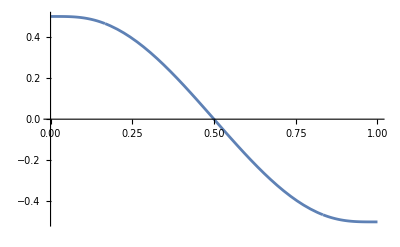

```mathematica
Plot[Im[(Cos[π UnitStep[(1-dir)/2+(x-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(x-3/2+φ/(2π))]])Sqrt[((ΔCircPath[Δ0,φ,x]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,x])^2)]],{x,0,1}]
```

### 5b

```mathematica
(*final transition probabilities for non-adiabatic transitions 1->2 and 2->1 using ϕ=π*)
```

```mathematica
Γ=1;
Δ0=1/2 Γ;
Ω0=1/2 Γ;
φ=π-10^(-6); (*value chosen for numerical bennefits*)
dir=-1;
ω=ωCirc1DL;
```

```mathematica
AbsoluteTiming[FinalprobsUCMag=ParallelMap[{#,FinalAmp[Δ0,Ω0,Γ,φ,ω,dir,#][[1,2;;3]]}&,Range[0.1,50,0.1]];]
```

{13.1299,Null}

```mathematica
FinalprobsUCMag1to2=Map[{FinalprobsUCMag[[#,1]],FinalprobsUCMag[[#,2,1]]}&,Range[1,Length[FinalprobsUCMag]]];
FinalprobsUCMag2to1=Map[{FinalprobsUCMag[[#,1]],FinalprobsUCMag[[#,2,2]]}&,Range[1,Length[FinalprobsUCMag]]];
```

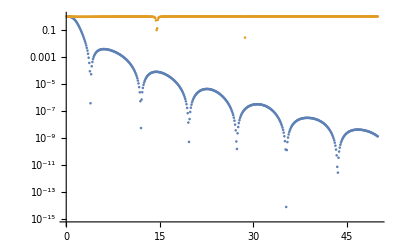

```mathematica
ListLogPlot[{FinalprobsUCMag1to2,FinalprobsUCMag2to1}, PlotRange->All]
```

```mathematica
(*added data about transition probabilities using same function FinalAmp at the special loop times 7273/500,14351/500,519307/12500, which correspond to the sharp dips in the 2->1 transition probabilities*)
```

```mathematica
Map[{#,FinalAmp[Δ0,Ω0,Γ,φ,ω,dir,#]}&,{7273/500,14351/500,519307/12500}]
```

{{7273/500,{{0.9999206742704903353915220982,0.00007932572950966460847790177928,2.575866001381854532295179494×10^-6,0.9999974241339986181454677048}}},{14351/500,{{0.999999861600164497581528306,1.38399835502418471694045751×10^-7,0.000137529293845690576195212588,0.999862470706154309423804787}}},{519307/12500,{{0.999999990117970253943598511,9.88202974605640148907646734×10^-9,0.000051472034307180289627349705,0.99994852796569281971037265}}}}

```mathematica
OnetoTwo=Sort[Join[FinalprobsUCMag1to2,{{N[7273/500],0.0000793259337412669941099722459176620537242443961347679452`28.075706879119114},{N[14351/500],1.384006452784230055631831553435744820562405065479356`27.91155253957615*^-7},{N[519307/12500],9.8821009841929166960290731703741708269791999295006`27.991084433966293*^-9}}],#1[[1]]<#2[[1]]&];
TwotoOne=Sort[Join[FinalprobsUCMag2to1,{{N[7273/500],2.5749992662546163340138597566066224992105382672708598`28.075706826162666*^-6},{N[14351/500],0.0001371340659259887927029942222898797905375532863644641136`27.911552520812364},{N[519307/12500],7.35372902479306377982528012149294241220745718358143`27.99108443407201*^-8}}],#1[[1]]<#2[[1]]&];
```

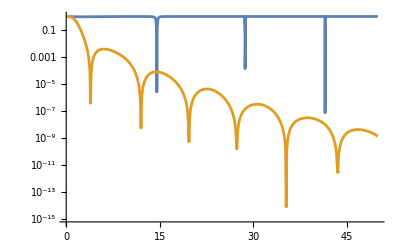

```mathematica
ListLogPlot[{TwotoOne,OnetoTwo}, PlotRange->All, Joined->True]
```

### 5c

```mathematica
(*using spectral norm to check if final flow matrix is indeed unitary*)
```

```mathematica
Γ=1;
Δ0=1/2 Γ;
Ω0=1/2 Γ;
φ=π-10^(-10);
dir=-1;
ω=ωCirc1DL;
```

```mathematica
(*using special loop times to generate final transition probabilities*)
```

```mathematica
FinalAmp[Δ0,Ω0,Γ,φ,ω,dir,1454622445/100000000 Γ]
FinalAmp[Δ0,Ω0,Γ,φ,ω,dir,28702150505541/1000000000000 1/Γ Γ]
FinalAmp[Δ0,Ω0,Γ,φ,ω,dir,4154456/100000 Γ]
```

{{0.9999206756908332395821485804,0.00007932430916676041785141959745,8.49184760775905651494037614×10^-9,0.9999999915081523922409434851},{0.9999189963807626813686,0.0000810036192373186314142,0.9969691923085484827257,0.003030807691451517274327},{0.9999287439523443862801,0.00007125604765561371990124,0.8649488472320528368026,0.1350511527679471631974}}

{{0.999999861579394730836290546,1.38420605269163709453550477×10^-7,3.89411548466824544085045386×10^-6,0.99999610588451533175455915},{0.9999998899573605459082,1.100426394540917531136×10^-7,0.9992744516082299168711,0.0007255483917700831288856},{0.9999998576881192620168,1.42311880737983177612×10^-7,0.9931273788327540641054,0.006872621167245935894567}}

{{0.999999990118122770278165108,9.88187722972183489183396984×10^-9,0.000507133013619346128306540183,0.99949286698638065387169346},{0.9999999895096949327981,1.049030506720191285541×10^-8,0.9998480765232478265599,0.0001519234767521734401186},{0.9999999900546500903542,9.945349909645839385753×10^-9,0.998674906396665903094,0.001325093603334096905779}}

```mathematica
PhiPiUCFlow=Sort[Join[ParallelMap[{FinalprobsUCMag[[#,1]],FinalprobsUCMag[[#,2,1]]}&,Range[1,Length[FinalprobsUCMag]]],{{7273/500,{0.99992067569083323958214858040255012956`28.08795200911264,0.0000793243091667604178514195974498704442790305112217671312`28.08854795828811,8.4918476077590565149403761399600678033835482022255`28.08854789462716*^-9,0.99999999150815239224094348505962386004`28.08914467895145}},{14351/500,{0.99999986157939473083629054644952301417`27.896261832109754,1.384206052691637094535504769858337215943550898654953`27.896412634993784*^-7,3.8941154846682454408504538614266945086189860926062582`27.89641263438704*^-6,0.9999961058845153317545591495461385733`27.896563489669095}},{519307/12500,{0.99999999011812277027816510816603016156`27.99325728026225,9.881877229721834891833969838445701300728234595631`27.99396320395863*^-9,0.0005071330136193461283065401834865645602278496578596086207`27.993962850919033,0.99949286698638065387169345981651343544`27.994669928569202}}}],#1[[1]]<#2[[1]]&];
```

```mathematica
PhiPiUCFlowMatrices=ParallelMap[{{#[[2,1]],#[[2,3]]},{#[[2,2]],#[[2,4]]}}&,PhiPiUCFlow];
PhiPiUCFlowNorm=ParallelMap[Norm[ConjugateTranspose[#]-Inverse[#],2]&,PhiPiUCFlowMatrices];
PhiPiUCFlowNormList=ParallelMap[{PhiPiUCFlow[[#,1]],PhiPiUCFlowNorm[[#]]}&,Range[1,Length[PhiPiUCFlow]]];
```

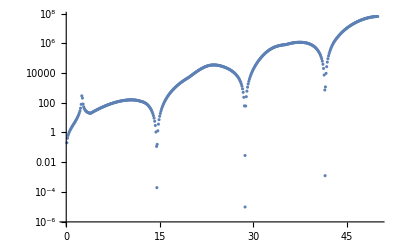

```mathematica
ListLogPlot[PhiPiUCFlowNormList]
```

### 5d

```mathematica
(*transition probabilities for P(i,j)*)
```

```mathematica
Γ=1;
Δ0=1/2 Γ;
Ω0=1/2 Γ;
φ=π(1-10^-3);
dir=1;
ω=ωCirc1DL;
t0= 145462242/10000000 Γ;
```

```mathematica
U[t_]=SolCircPathAdDoubleLoop[Δ0,Ω0,Γ,φ,ω,dir,t0]
```

InterpolatingFunction[{{0, 29.0924484000000000000000000000}}, <>][t]

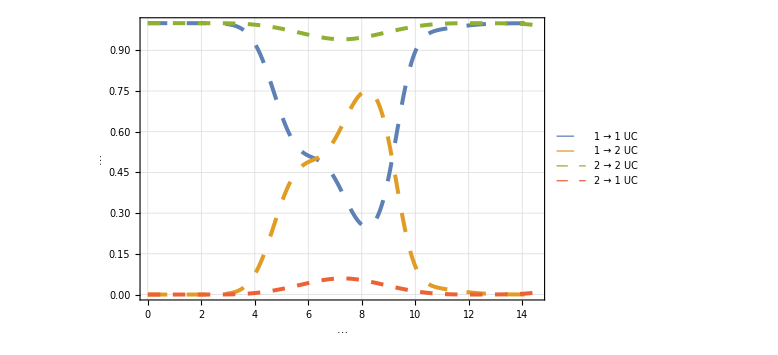

```mathematica
Plot[{Abs[({{1, 0}}).U[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).U[t].({{1}, {0}})]^2+Abs[({{0, 1}}).U[t].({{1}, {0}})]^2),Abs[({{0, 1}}).U[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).U[t].({{1}, {0}})]^2+Abs[({{0, 1}}).U[t].({{1}, {0}})]^2),Abs[({{0, 1}}).U[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).U[t].({{0}, {1}})]^2+Abs[({{0, 1}}).U[t].({{0}, {1}})]^2),Abs[({{1, 0}}).U[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).U[t].({{0}, {1}})]^2+Abs[({{0, 1}}).U[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{Style["(*GraphicsBox[{Thickness[0.023441162681669007`], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGIlIGYCYvldC/al6sk7GGitFL7QourQG9Htz/hB1sHn
BLvt7KtaDhJNMlMMLn+3R+frg9SraDk88HuZ8Hf+bzi/D6R/A4sDjL/Na4PF
nJ8sDnMWKe/881wTzk9NAwI2BN8YBC5LwPlgcwTE4ea1KrCrnpkiBrcPxoe5
B51vAjZQFGJP2h/7qvs/bhl7i0LNY3OA8c+AQA8nnH+ge1+TyWMeOP8giL9Y
CM4XqZxUcpZFxAFmPowPs999zdHlDDOE4HyYeTA+WN9mHocdwVYR/9XF4fy1
Qjp86fck4HzpeXGapw004fyaTxsCsn9pws2Dha/6J5WXszoF4Hywe5aIwvkz
ZgKBpQyc/2Xfx63pZbIO56+GvdG/reEQ8PbyxxmKcvD4R08PAE9E2P4=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJLIGYC4h0OTY+O31B3EKmcVHKWRcYBxpfftWBfqp+M
w6MI8e0XD6g7GBgDQbGMwya9vMWMcxD8jVC+PpTfwHK037AcIT9jAn+VWba6
Q8jbyx9nOGLyZZe/8NCLV3dQ/6TycpamjINoj9crFhN1h/Q0EJCG8LeoORzs
3tdkwizpcOFq2Bv92aoOZ0BgjajDjJlAYKkC53fbeO5Ka1KG8/fm17ydWars
sFZIhy/9nhicX3P/xy3j1+IOe9D4qOolHNzXHF3O0KHs8MA13nFWoaSD38WJ
Mf+SVR2eJC68ZqKv4uBzgt129lR1OD8+JEh9AacGnO+xv1bWwh2TP6W9Nery
HASfAQQeqDiIT73CmaGE4M9ZpLzzz3J1OP8pyJx+VThfZl6c5ukCNYfzoHCJ
1nBIANnfqeYgDRLfgOBPBtm3B8EH2/scwQfTnprQ8FRz+A8C9ZoOW8x/HEp5
pQrng+V3IvgbVJ80z9NVdVgPonM1If76o+KwGaRvlYYDC2eXfDKfCty9K769
rDhzQRHO548NuG8UjuCDzZXH5L8q3ir6OxvBh4Wn84RmoTQvBB8cb/sQ/NLD
21xn3lWG86tB8eyt5LAj2Cri/3FpiH4pJYcY1QiZczJSkPjmUHI4AEpviyXh
fFj6g/HByfOYGCRdXFRymAkOFxFIuKqrwPmQ+FKD82H5qz+i259xg7QDev4D
AHbzfLc=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJ5IGYC4tQ0IFim6xD09vLHGYyiDjA+iEo7Ju4QcEu6
JtFI18HEGAguSzqkxN5xY7bQgfMz8j+0nizRhvPBtLC2w5d9H7emT5OA8zU+
qbyc1SkO58eoRsicqxFzYOHskk/Og+o3FnU4fthpbaadDpy/VvVJ87xeBF9m
Xpzm6Qs6DiKVk0rOpog6uO+vlbVg13V44BrvOOuiqINoj9crFhFdiH0vRR3+
g4A8bv5fNP6b4q2iv7V1HRhAwAHBh4UPjN8f0e3PWCAMt/8zyL9hAg4tvP7r
pyzVdtjutcFiTiWXg8TUK5wZSdoO/k88L5kGc8L5YO985sDJ3wbWz+HwIEJ8
+8UGbYi7/7M7yCx/4aE3H8E/vmtHL9sFBB8Wf2dAgIffAT1+AcZ8zHk=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJLIGYC4hgFx4/JOaYOIpWTSs6yyDjA+PK7FuxL9ZNx
KFjTfTsjwdTBwBgIimUcIsS3X2Tww+TrQ/mOTY+Oz7BGyPucYLedbWrqEPL2
8scZjpj8CcElKtP1TR3UP6m8nKUp48DlplrKJGXqkJ4GAtIQ/i0Th4Pd+5pM
mCUdXmRpf5vua+JwBgTWiELoOcZwfo/XKxYTRwRf9UnzvLNWxg5rhXT40u+J
wfk193/cMn4t7qCCxkdVL+Hgf3FizD9nY4cHrvGOswolHVa88ND7b2ji8CRx
4TUTfRUHNZB6L1M430BrpfCFFgR/yf19fHMWY/KntLdGXZ6D4DOAwAMViPsn
Ivh+IPuDEfxPGwKyZ7mbwPk8/uunpO4wcTh/NeyNfrQGxP4jJg7S8+I0T29A
8CeD7NuD4Hvsr5W1eI7gJ4QEqS/w1ISGp4nDfxCo13S4JV2TaFSK4IPlYxD8
G0KfHM+LmTisBwVcrqbD6cNOazP/GTtsNv9xKGWVhkMjy9F+w3ZjuHt5Qe7N
MILz7UHpRRvBB5vLj8l/VbxV9Hc2gg8Lz9sg96ki+I9BdDyCXwLUdjrPGM73
BqW/pUYOO4KtIv4fl3awrYxYYdpr5BCjGiFzTkYKEt/NRg4HQOltsSScD0t/
MD44eR4Tc6j/bVVw7oWRw0wQ2CkCic/JxnA+OL6Om8D5sPzVH9Htz7hB2gE9
/wEAO+WEmw==
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAwBWIQ3RdcojI93tJBpHJSyVkWGQcYP+Tt5Y8zHGUcFt/f
xzcn2NLBwBgIimUcur1esZg4IvjeJ9htZ6si+OJTr3BmKFk6yO9asC/VT8YB
JGwsbOmwXkiHL71O2sHv4sSYf4ctHHYEW0X8Vxd3uC70yfG8m4XDGRBYI+qw
4oWH3v+H5nD+iyztb9P3IvgH25aHn5pk7vDANd5x1kUEnwEEHMThfPVPKi9n
dUo4fNoQkD1ru7mD+5qjyxl+SDpovOXdZ3DT3CE9DQSkHUq2iv4+vc7CodPG
c1eakhJUvQXE3cFKDraVEStMz1o4rPz2suLMAQQfHF4mynC+DygcTFUc/n4r
fTCn0MJhSntr1GUZVYeNenmLGe+Yw/kmIHMPm8H5EqDwCjKDuG+FIpzPHxtw
36gcwQ/nFGs3jleEuDfODOIeB0VIeBYj+OD460fwwfonmTl8WLRe4WwEVP88
M4e1oPhYp+iQEnvHjfmFmUMEyPz1yhD3xpg7/Hz7+oDlYhVIeF5C8E8edlqb
+Q7Bh8Q31L9zEPyZIHBTGc6vvP/jlrG1ssMW8x+HUn5B469QCR7f1SD514oO
B2plLdJLzCHpI10ezoekJ3mHGAXHj8k8sPiUgppn5tCuwK56xkQK7h+I+ZJw
/pd9H7emT5OA8/siuv0ZC8QcwMnAzRzi3p0i8PQB44Pj86MFnA/LH/0g/Ruk
HdDzDwDQs2oE
"], {{25.2781, 12.739099999999999`}, {25.2781, 12.917200000000001`}, {25.134399999999996`, 13.131299999999996`}, {24.873399999999997`, 13.131299999999996`}, {24.598399999999998`, 13.131299999999996`}, {24.2891, 12.8688}, {24.2891, 12.5594}, {24.2891, 12.260899999999998`}, {24.5391, 12.165599999999998`}, {24.6828, 12.165599999999998`}, {25.004699999999996`, 12.165599999999998`}, {25.2781, 12.4766}, {25.2781, 12.739099999999999`}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxdlQ1MW1UUx8tYhiw6HFtbPsrKa0twbG6TD53vvZb/08nULM6ACVU3EaV0
6hQUFocBl4iOMJjowjbARgfMsCU4NEoEDBXFpdMVWAMhZlPLDLoRQcUQAtm0
9t7bd1/0Ji/NLzfn63/OuRWeKct3Ret0uqjwVxH+VoQ/szL/rH9OwfqqY5Uj
K01Q+bG58fkWxQTfRvHYxWsKtmWFT4UJH8ibJ9p+0vjQDbF89JLG/ZeP/O0a
U2AeOOV1PRKx9ynoid+8xv16MpoXVxW1nFaQSu7PGVHXVfhd5n4FfnK69Zgu
bp/M3qoxtTdrTP3HKGglp19jHTkwcn4yzWkarU5AoKwoZjRRrS+J+0v/yzbT
Vp+EF2KXT7klBW+mxqT5J0wIkXNIwf3v1MaXigJn6+TPBTqPhfNn9yx9XbLa
htnbvNtaH1bQXPfWE+OmNKbPJDjfurun2VWu8ePGzwO6DcCuCzH293Js+PD6
g1tCX+Wy+vwW1BA9+3Jxp2Be2G+wYVfg3T3/FORy+1+IPmUOzkcLKm0ni+yc
aX5jMvPnsSJ9jiQo48rGlO5QtJXdN8lMr6dtGDocbkC8zO2pXaPE+cualO3u
bI0LSf6/i/B0WPtv+iL5fSoyf1NWyFXOMzk1Io9nPD4Ruy9fjMQVOMftfTSY
+arGhbGGuqwiAZW9+hsXnxJxdnHmoB8C81+h8Z7U8IA2atxE6m8S4SoNnzwB
NxcPTHnaRZBxzBqP3I+JqAouXc6SrGghcxMrYXnut6F7O204HfSu8dRqTO+/
1biL9OeqhLvlwfwTisY7yHwcsXJW66X+hiW4ST4GCy4M3/fRc+ck/NnRkzri
FNi+OCUcJPk0pODjLS91RpkkDDV438juTGR2qySsI/NakoCtGWfXXZoW0Vcg
OkPpBs53kPmd0XNm86/n9mw/1vP+qazGV1mtP5/se5Se5eOR+H7R+tolLHjn
e92Lelx7ftPiyUGJvQ/txsjcRu5PJLA+x8nsN2hi+VXKGCyrnms9LsA2Xfv+
yGsy26+BsB4rzzfd5ZPZfs1aULL3h7zo7XY4yTz0WNl9nZ3rT+f/DzvvzwJd
eAdnFldjGm91LmzUv5Xzzu7zXbolC2c2LxqzflnYXP3q4O+Bj/TT64CH6LNs
5szeDzNuyUs7sKLNwftL51Fx4G1nw+6o2xPwfXJ1cWaOA3kkvtOIb8j+WRyY
PfxiQ2aygbPaX5XV/tJ+7nDw/tH9eUVjJ9nPUY3tZB9/dGDqgSKlLaBn79FS
xH+9ke1HTy7fR/ou9Ub0OSOAjEdWBv67DwGNuxuu7NPFKZxpfjaF662yqrfK
9fJDA6UdAkj40HUgSPJbu4G93z6gjuiZnRypA2ik+iWx+J+A1fNyImd1/lSm
epcbUDw8vsl1FVwP+l5nKJypHn0aq/9/tB9fJOP//4//AvvkPH0=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGBQBmIQvfNW19/U6S4O6WkgIOUA48vvWrAvdZ2Ug96EBT8M
+1wcau7/uGX8WsrB4trRXJMOBN+h6dHxGc0I/ooXHnr/G10c/oPAfSmHtuXh
p4xKXBzuu8Y7ziqUcnjDu89gppCLg0jlpJKzKWIOM0Gg0dnhDAisEXU4oWk1
6bQ7gl//26rg3AcnOP93TO7Rf4ecHEyMgeCyOJw/HWROpDScDzafRQbO/7Lv
49Z0M1mHi/nx7OduOkHco6jgoP6ked5ZLWc4f6Ne3mLGEAQf7L/dzg7lh7e5
ztRVcGBZPMmKkdXFQfnao2CGOQoOtSD3VbhA3OejCA+PtUI6fOnrlOB8sLyM
MpzfANKnoQLxv6eLw5T21qjLMqoQdU+c4fwp39jiZ7gg+Pqg+Ihzgui7qQTn
w/wH47cqsKueMZGA+HcnVP1OEbh5MD44fkRc4HyU9HBM0gE9fQAAZ8MLqw==

"], {{40.6703, 9.556249999999999}, {40.6703, 8.304689999999999}, {38.762499999999996`, 8.304689999999999}, {38.262499999999996`, 8.304689999999999}, {37.7609, 8.304689999999999}, {38.2734, 10.1391}, {39.406299999999995`, 10.318799999999998`}, {39.787499999999994`, 10.318799999999998`}, {40.3125, 10.318799999999998`}, {40.6703, 10.007799999999998`}, {40.6703, 9.556249999999999}}}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{63.99483437110834, 24.508064757160646`},PlotRange->{{0., 42.660000000000004`}, {0., 16.34}}])",15],Style["(*GraphicsBox[{Thickness[0.018857250612860643`], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAwBmIQLVI5qeTsEmWHjPwPrSdD1B1gfOl5cZqnDTQdHrjG
O84SVHKQmHqFM+ORlkPA28sfZyjKwfmqn1RezjrJB+dv9dpgMecnD5wvs1Fs
PpMCJp+Fs0s+OQ/BlwHbh9AP4/M48nnNyOSD86NVI2TOyQhh8P+DgSacP6W9
NeryHtz818VbRX93azqcAYE3gnD/bgPbz+bwpi2322i3hINdiWPtaRk2h76I
bn9GAXGHF7WPs8+/YXVoVWBXPTNFzOEvyNr6f/YwPtg/D37B+RDzfmDwZ4LA
TlE438QYBEQd3oDMX/MLzhdvkplicPk3nJ8zNaHQovg/nH+we1+TyWJGh6r7
P24Ze4s69IPcWcAM588AW8QH54PdYSKAxhd0gJkHCx8Yf62QDl96HYIvDEof
LMIYfHB4SYvB+TD/uq85upxhhhCcD46m+4Jwfot4LWsmGx+c3wty/wdehxqQ
+14j+OB0mSIO54eA0uFCcbj+L/s+bk3/Jg5NT1DzTCTg/gH7Q08JYr+8FJzv
PKFZKC1KAc6HpX9wepmj4oCePwCVdT16
"], {{8.82031, 11.915599999999998`}, {8.82031, 11.6063}, {8.665629999999998, 10.592199999999998`}, {8.117189999999999, 10.0438}, {7.914059999999999, 9.82969}, {7.3421899999999996`, 9.37656}, {6.2562500000000005`, 9.37656}, {4.57656, 9.37656}, {5.387499999999999, 12.6313}, {5.4937499999999995`, 13.071899999999998`}, {5.54219, 13.095300000000002`}, {6.0062500000000005`, 13.095300000000002`}, {7.185939999999999, 13.095300000000002`}, {8.081249999999999, 13.095300000000002`}, {8.82031, 12.809399999999997`}, {8.82031, 11.915599999999998`}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxFk2tIFFEYhlfXDImU1F2tVndnZ2ZnZy9mrhqlwUcXu1BqFrmFWparXRHS
8EpGJpJmaam5JWr6QyxlhW4qKpYIUl6x+mGBBgaaSiEhltW2Z2b2zAfnxzMz
58z3vu/5iDPpcRapRCJxcazdjuXqWG4eJcqzd4LA7CEvNtlIcPKRyc35yVco
UNQlse/GjFBZXHRyQkGDHVW9AfNCxgvZ6lM95lCTo+7rYCb58cdQGwUhHLOQ
M7UyaYogobaR7PyTxsLb/l1t569RILt98Jtbphbvl6C6zmD+u3x1urZCgzkl
8XOU1F8DqVxRfL8jwr5pUnhOwyc2oNUuJaGm3Cs3fB0NPen5i9YqArNXYuxU
SJbI8Uj/KQKixysS/pE0tCzPZQ8BwZ8fLXJg8+z+oAKRb66PsVUW0WBBv40i
4PSxOKahhQYk2zQhvF+jEb539GN1VI4Gfi3O921voqCdnimsu8xg5vy1i/xs
28qbFJ0Wxj4cX9gSIfKe8kLv1BISs1Mvd94iA2moH7kafqNz+hn40WhTDZsJ
wT8GslEepQF8DnUa6CvtvRHatJHPL0MDPjn3ModT/GGwq6PMPVgDHUd3mO2M
HLN2iZp7OCfDzPkPMrwfybR2+sJXdA9GReby3MBg5v1jQNXV0GvxlMFzpOcJ
A69RP1I5n3s3A75cP3KhXy3sax1oltQECPq0UGYujXFpD4TwyJ646i9aSKDN
ipFuJZ+LOwtt3gbPtCQVBOtafMYoltc3o8L3MQ/5MU9A3lJ77MVcFm5FHuhK
VatBgfJW6iCr/+Ve62GS969DJ+RLwrTZ79W4RA9GQvnzklzIr16P8+Pythow
j6IcV0WevaBffpBohE1ozsopGELVauT9OUHxc/TdAIcG1+58FEZBG8q3zIDn
1clcvlqRufyr1RCG/HAx8vffooYCt4G7W+NF9qt673HONQizc/45f1dEdv7v
P3WExDg=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{21.2359, 8.57813}, {21.2359, 9.71094}, {20.496899999999997`, 10.5563}, {19.412499999999998`, 10.5563}, {17.8391, 10.5563}, {16.2891, 8.840629999999999}, {16.2891, 7.159379999999999}, {16.2891, 6.02656}, {17.0281, 5.1812499999999995`}, {18.112499999999997`, 5.1812499999999995`}, {19.698400000000003`, 5.1812499999999995`}, {21.2359, 6.8968799999999995`}, {21.2359, 8.57813}}, CompressedData["
1:eJxTTMoPSmViYGAQBmIQDQYFJg63NWXX/GdWcoDxwznF2o35FSF8AxMHkcpJ
JWdZZB026uUtZtxj7BCjGiFzTkbKoWSr6O/TdsYONfd/3DJ+LeZwXeiT4/lp
Rg5nQGCNqMN/EJBH8BtZjvYbthvC+elpQCBm6NCqwK56Zoo4nA8xTwrOh9gn
69AfXKIyPd7QofzwNteZfxUcbkvXJBptNXRYK6TDl66n5HD6sNPaTDsjB9+L
E2P+Mas4qL/l3Wfw0sjh59vXBywXq0DMSzOG88H++YPgw/wfAfL/emUH9PAB
ADKNeF8=
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGDQBGIQvb9W1iLdxMohnFOs3The0QHGX/HtZcWZCcoO3ifY
bWdPtXSY0t4adVlG1UF6Xpzm6Q0WcP6yFx56/wURfImpVzgzmswddBXlv+SI
qTjw+a+fkuph7nAGBOYoOzSyHO03VLeA8Hu0HLaY/ziUomXhoK+1UvjCEi2H
wjXdtzMMLBwSQoLUF5xE8OcsUt755zmC38ILNFhV22GjXt5iRh7cfL+LE2P+
JZs7pKcBAZu2AwMIGJg7PIgQ336RQRviXiZzh4z8D60nv2g5ODQ9Oj7jtJkD
C2eXfPI7Lah/zCD0Iy2Iu3PMHDaA7LmD4IPV5yH4MqBwMtBymDGBv8qsG8Hn
clMtZVqF4HuBwtfVHINf82lDQPYvTTgfHL57EPyAW9I1iZM0HWwrI1aY6po7
mNnsDZr2UANijoK5g2iP1yuWEg2HL0BjZl03g4SnpppDyVbR36f/mTrEqEbI
nNsj5zAhuERl+ntTh4r7P24Zd8vC+W/acruNdsvA+WD1Mgg+OBwdxB1eZGl/
mz7XzGEmCOwUgYc3jP9l562uv0ct4HxY+jIxBoLL0g7o6Q8AseMHzA==
"], CompressedData["
1:eJxTTMoPSmViYGAQAWIQvVEvbzHjGQsH9U8qL2d1Sjn8B4F6C4cv+z5uTf8m
7rDk/j6+OZ/NHc6AwBpRh0aWo/2G6Qi+1wl229msCL7qk+Z5Z2eZOTxwjXec
dVEMzoeZD+PHqEbInJORgZi/2MxBpHJSyVkWWYj8LTOH8sPbXGfqKjjIzIvT
PK1g7mAMAsFKDjeEPjmeVzN3uK0pu+Z/s5LDtAn8VWa3zR1+vn19wHKxisMW
8x+HUlZZwPnSIP0GlnB+hPj2iwx5lg4ZaUAwTRnO/7BovcLZCCU4/w7IfGNF
B17/9VNSJSzh7kMPLwCx0pM9
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{28.593799999999987`, 5.871880000000001}, {28.593799999999987`, 6.2171899999999996`}, {28.3078, 6.456250000000001}, {28.021900000000002`, 6.456250000000001}, {27.674999999999997`, 6.456250000000001}, {27.437499999999996`, 6.17031}, {27.437499999999996`, 5.88438}, {27.437499999999996`, 5.539059999999999}, {27.723399999999994`, 5.300000000000001}, {28.009399999999996`, 5.300000000000001}, {28.354699999999998`, 5.300000000000001}, {28.593799999999987`, 5.585939999999999}, {28.593799999999987`, 5.871880000000001}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJ5IGYC4jMg8MbeIejt5Y8zGEUdYPw0EDgm7nCgbXn4
qU32DibGQHBZ0sHnBLvtbFMk/sWJMf8u28H5YHqxncOXfR+3pk+TgPM1Pqm8
nNUpDufHqEbInKsRc5CZF6d5+gJUv7GoQ+1vq4JzFvZwfv6a7tsZCQj+0hce
ev8b7R1EKieVnE0RdbCtjFhhOtfe4YFrvOOsi6IOS+7v45uz2B5i30tRhxkz
gWAlbv50NH5/cInK9PX2Dgwg4IDgw8IHxu+P6PZnLBCG2/8Z5N8wAYcYBceP
yW/sHLZ7bbCYU8nloPKked7ZU3YO/k88L5kGc8L5YO985sDJ3wbWz+HA4aZa
ynTLzuE/GLA7aLzl3WfwEsH/8630wRxGezgfFn9gmoffAT1+Af1C3uk=
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAwBmIQfaBW1iL9jqtDRv6H1pMh6g4wvvS8OM3TBpoOXzYE
ZM8qd3WQmHqFM+ORlsPOW11/U7e7wPnHNa0mnb7vBOerPmmed/YQgn9buibR
aCsmn4WzSz45D8GXAduH0A/jX8yPZz93E8Ev2Sr6+7SZMwb/PxhowvlT2luj
Lu/BzX9dDGR0azrU/7YqOGfgDPcv2P4kJ4c3bbndRrslHFgXT7JiDHVy6Ivo
9mcUEHdY/sJD73+gk0OrArvqmSliDk8SF14zee4I59/fxzfH+BSC/zsm9+i/
XZj8mSCwUxTONzEGAVEHd9VSplknEHyw/y8i+CBnn36H4At/cjyfxuvkUHX/
xy1jb1GI/VoI/hkQuIPgg837icaXdIabBwsfGB/sPicEvzJihenZYEw+OLyk
xeB8mH91Jyz4YejmjBpe+gi+fdOj4zMuO6GG3yUnhxqQ+14j+CKVk0rOpojD
+SFvL3+csVAcrv/Lvo9b07+JQ9LTVah5JhJw/6wV0uFL11OC2G/uAueD/c/p
CufD0j84vcxRcUDPHwCDDFd4
"], {{42.720299999999995`, 11.915599999999998`}, {42.720299999999995`, 11.6063}, {42.565599999999996`, 10.592199999999998`}, {42.0172, 10.0438}, {41.814099999999996`, 9.82969}, {41.2422, 9.37656}, {40.156299999999995`, 9.37656}, {38.47659999999999, 9.37656}, {39.287499999999994`, 12.6313}, {39.3938, 13.071899999999998`}, {39.44219999999999, 13.095300000000002`}, {39.906299999999995`, 13.095300000000002`}, {41.08590000000001, 13.095300000000002`}, {41.981300000000005`, 13.095300000000002`}, {42.720299999999995`, 12.809399999999997`}, {42.720299999999995`, 11.915599999999998`}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{44.7688, 8.459380000000001}, {44.7688, 8.634379999999998}, {44.64059999999999, 8.760939999999998}, {44.45779999999999, 8.760939999999998}, {44.251599999999996`, 8.760939999999998}, {44.021899999999995`, 8.57031}, {44.021899999999995`, 8.331249999999999}, {44.021899999999995`, 8.156249999999998}, {44.148399999999995`, 8.02969}, {44.3313, 8.02969}, {44.537499999999994`, 8.02969}, {44.7688, 8.22031}, {44.7688, 8.459380000000001}}, CompressedData["
1:eJxTTMoPSmViYGAwB2IQ7XOC3XZ2qZtD5f0ft4y7hRxg/GjVCJlzd6D8XDeH
VgV21TNfhBzSwADBf7CPb45xFIJvce1orkkEVP8eIYdb0jWJRqFuDtUg87OF
HBQcPyafsXVz+A8C+/kdNurlLWYUcXNIBRmrxuuQw/lzQfprVzj/SeLCayb3
EfxfMblH/11ydbjBe1sstQzBf1H7OPu8Dj+cPxMEIgUclr3w0Pt/09XhDAi8
EYCY99zVQf2TystZLwUdSraK/j7N5uYQA3JvjQjEf2puDn0R3f6MAuIOO291
/U3Vh4bPaXEHh6ZHx2dYu0HUHZOA8x+6xjvOCpSE83cEW0X8fy4FcY+Qm4NI
5aSSsywycP/A+AdqZS3SaxD8i/nx7OcCXR0egMybKA7ng81TR/DXCunwpd8T
c6j9bVVwLsLVYQ2Iv0/MIaREZfr/BARfb8KCH4Z5CD7Y/nxXB4VdC/alvhOD
xF+RqwMDCDiIQ8KjD+oeFylI/O91dQh4e/njDEVpSHzdQfDB+l8h+GD/fHF1
cF9zdDnDDyk4vx2UPkQQ/APd+5pMDktC4vuzKzz8erxesZi8dIWknxgJSHo5
6+pQBQp/bTEHialXODM2QcNHUATODwLZzygCcf80aHgdF4SE10RXB3mQf/0E
IemgB5EeYPxgkP5EBD8dFL/LoOlxs6uDfYlj7ekYbrj7YPwNoPDwcYPzYfkH
bJ4iIj/B8hcANHN/1g==
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJJIGYC4h6vVywmje4OvRHd/owGPA4wfvDbyx9nKAo4
uKmWMs3KcHfYGWwV8b9d0GGjXt5iRhsEn8d//ZRUCTR5FneHg937mkwWC8D5
BctLNvzr54fzW8RrWTOP8TrsvNX1N1Xc3eE/GHA7sCyeZMVoi+CLfHI8nxaK
4E/5xhY/I8XdwcQYCD7z4OT7P/G8ZHqZwyENBMKg8sasqPbZM0LEhd0dCkHu
42eE+F/Q3aEfFB4fGOB86Y1i85kWIPj2JY61p2UYHBIOX9ZOlXR3yJmaUGhR
/N8eHB4KCD7YPToIPix8GUDgAIsDevgDAFc8oR4=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}}}, {{{50.882799999999996`, 8.459380000000001}, {50.882799999999996`, 8.60938}, {50.762499999999996`, 8.760939999999998}, {50.57189999999999, 8.760939999999998}, {50.3344, 8.760939999999998}, {50.12659999999999, 8.53906}, {50.12659999999999, 8.331249999999999}, {50.12659999999999, 8.181249999999999}, {50.2469, 8.02969}, {50.43749999999999, 8.02969}, {50.675, 8.02969}, {50.882799999999996`, 8.25156}, {50.882799999999996`, 8.459380000000001}}, CompressedData["
1:eJxTTMoPSmViYGAwAGIQrTthwQ9DN0+Hmvs/bhm/Fnfo9nrFYuLp6XAGBHwk
HIxBwNvTQX7Xgn2pfQj+zmCriP/sknD+DhD/uJTDPBudK7PkPB1EKieVnGWR
cbBvenR8xmMPOP/zhoDsWeUIvqtqKdMsCw+HB67xjrMmisP5YPPUEfy1Qjp8
6ffEHI5rWk06be/hsAbE3wfluyP4v2Jyj/4LQvA36uUtZgzxcPiy7+PW9Gti
EPdGezj0RXT7MwaIO1zMj2c/V+nhEPz28scZjZIO3ifYbWev9XAIAPEVpR14
/NdPSX2A4Ms7fkw+8xXBX/7CQ+8/IzR81knB+WD5hZJwPtg+A0mH1d23Mxj+
w9wnAXHfHw94eO+vlbVIn+Ph4P/E85LpZQ4HlsWTrBh7PRwmgPR/YIG7v3B5
yYZ/5xkcbkrXJBrJIvhgc3gQfB+Qf/66Q/j8jA4OoPj47e4gvVFsPpMCI8Q8
aWj4iDE5PE5ceM1EHuqeM8xwvgxIfQILnJ8GAs9Y4fZt9dpgMWcnm8MXUPx+
d4fzl4H8fxPBB6ePfe4OB7v3NZkos8L56p9UXs7iZIbzwe5bwODQtjz8lNET
dwcW/V9cl3j+2euB0qucB5wPlo9B45/xgPirmNHhDe8+g5mvoOEpzOmAnt4B
eMpEFw==
"]}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{79.54099128268992, 24.508064757160646`},PlotRange->{{0., 53.03}, {0., 16.34}}])", 15]}, PlotLegends->Placed[{"1 → 1 UC", "1 → 2 UC","2 → 2 UC","2 → 1 UC"},Right],ImageSize->Large, PlotStyle->{{Dashing[Large],Thickness[0.005]},{Dashing[Large],Thickness[0.005]}, {Dashing[Medium],Thickness[0.005]}, {Dashing[Medium],Thickness[0.005]},{Dashing[Small],Thickness[0.005]},{Dashing[Small],Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

## UC, TD, and SATD Dynamics (Fig. 6)

### Functions used for numerics

```mathematica
σx=({{0, 1}, {1, 0}});
σy=({{0, -ⅈ}, {ⅈ, 0}});
σz=({{1, 0}, {0, -1}});
```

```mathematica
(*choosen contour*)
ΔCircPath:=Function[{Δ0,φ,x},
Δ0 Sin[2 π x+φ]
];

ΩCircPath:=Function[{Δ0,Ω0,φ,x},
Ω0 + Δ0 Cos[2π x+φ]
];
(*time dependant parametrization of contour for single (ωCirc1) and double loop (ωCirc1DL)*)
ωCirc1:=#1(6(#3/#2)^5-15(#3/#2)^4+10(#3/#2)^3)&;
ωCirc1DL:=(ωCirc1[#1,#2,#3]UnitStep[#2-#3]+((#1)+ωCirc1[#1,#2,#3-#2])UnitStep[#3-#2])&;
```

```mathematica
(*constucting the holomorphic eigenvalue, works for a double loop*)
EigCircPath:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},

(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2)

];
```

```mathematica
(*constucting thederivative of the holomorphic eigenvalue, works for a double loop*)
EigDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])((2 ⅈ π Δ0 (Γ Cos[φ+2 π ω[dir,t0,t]]+2 ⅈ Ω0 Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,1][ω][dir,t0,t])/(√(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])))
];
```

```mathematica
(*constucting the holomorphic pseduo rotation angle into the adiabatic frame, works for a double loop*)
θDiagCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
-2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)+(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]
];
```

```mathematica
(*constucting the derivative of the pseduo rotation angle into the adiabatic frame.*)
θDiagDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(4 π Δ0 (2 Δ0+2 Ω0 Cos[φ+2 π ω[dir,t0,t]]+ⅈ Γ Sin[φ+2 π ω[dir,t0,t]]))/(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])Derivative[0,0,1][ω][dir,t0,t]
];
```

```mathematica
(*constucting the 2nd derivative of the pseduo rotation angle into the adiabatic frame.*)
θDiagDDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(4 π Δ0 (2 π (Γ^2+4 (Δ0-Ω0) (Δ0+Ω0)) (-ⅈ Γ Cos[φ+2 π ω[dir,t0,t]]+2 Ω0 Sin[φ+2 π ω[dir,t0,t]]) (Derivative[0,0,1][ω][dir,t0,t])^2+(4 Δ0 (-Γ^2+2 Δ0^2+4 Ω0^2)-2 Ω0 (Γ^2-4 (3 Δ0^2+Ω0^2)) Cos[φ+2 π ω[dir,t0,t]]+2 Δ0 (Γ^2+4 Ω0^2) Cos[2 (φ+2 π ω[dir,t0,t])]+ⅈ Γ (-Γ^2+4 (3 Δ0^2+Ω0^2)+16 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]) Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,2][ω][dir,t0,t]))/(Γ^2-4 (Δ0^2+Ω0^2)-8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]-4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])^2
];
```

```mathematica
(*the adiabatic Hamiltonian*)
DynMatAd:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
-EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σz-1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σy
];
```

```mathematica
(*the SATD correction in the adiabatic frame*)
WSATDAd:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
1/2(1/(4 EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]^2+θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]^2))(2EigDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t] θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]-2EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t] θDiagDDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])σx
];
```

```mathematica
(*solving for the UC dynamics in the adiabatic frame*)
SolCircPathAdDoubleLoop:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{U},
First[U[t]/.NDSolve[{U'[t]==-ⅈ DynMatAd[Δ0,Ω0,Γ,φ,ω,dir,t0,t].U[t],U[0]==IdentityMatrix[2]},U,{t,0,2t0},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->30,MaxSteps->10^6,Method->{"DiscontinuityProcessing" -> False }]]
]
];
```

```mathematica
(*solving for the TD dynamics in the adiabatic frame*)
SolCircPathTDDoubleLoop:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{U},
First[U[t]/.NDSolve[{U'[t]==-ⅈ (DynMatAd[Δ0,Ω0,Γ,φ,ω,dir,t0,t]+1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σy).U[t],U[0]==IdentityMatrix[2]},U,{t,0,2t0},PrecisionGoal->12,AccuracyGoal->12,WorkingPrecision->24,MaxSteps->10^6]]
]
];
```

```mathematica
(*solving for the SATD dynamics in the adiabatic frame*)
SolCircPathSATDDoubleLoop:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{U},
First[U[t]/.NDSolve[{U'[t]==-ⅈ (DynMatAd[Δ0,Ω0,Γ,φ,ω,dir,t0,t]+WSATDAd[Δ0,Ω0,Γ,φ,ω,dir,t0,t]).U[t],U[0]==IdentityMatrix[2]},U,{t,0,2t0},PrecisionGoal->12,AccuracyGoal->12,WorkingPrecision->24,MaxSteps->10^6]]
]
];
```

```mathematica
(*solving for the final transition probabilities for the dynamics in the adiabatic frame at the final loop time t0*)
UnCorrFidelityCheckAD:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{prob},
(*finding the flow matrix at the final loop time*)
prob=SolCircPathAdDoubleLoop[Δ0,Ω0,Γ,φ,ω,dir,t0]/. t-> t0;
(*the transition probabilities for the gain-to-gain and loss-to-loss modes*)
{N[Flatten[Abs[({{0, 1}}).prob.({{0}, {1}})]^2/(Abs[({{1, 0}}).prob.({{0}, {1}})]^2+Abs[({{0, 1}}).prob.({{0}, {1}})]^2)][[1]]],N[Flatten[Abs[({{1, 0}}).prob.({{1}, {0}})]^2/(Abs[({{1, 0}}).prob.({{1}, {0}})]^2+Abs[({{0, 1}}).prob.({{1}, {0}})]^2)][[1]]]}
]
];
(*solving for the final transition probabilities for the TD dynamics in the adiabatic frame at the final loop time t0*)
UnCorrFidelityCheckTD:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{prob},
(*finding the flow matrix at the final loop time*)
prob=SolCircPathTDDoubleLoop[Δ0,Ω0,Γ,φ,ω,dir,t0]/. t-> t0;
(*the transition probabilities for the gain-to-gain and loss-to-loss modes*)
{N[Flatten[Abs[({{0, 1}}).prob.({{0}, {1}})]^2/(Abs[({{1, 0}}).prob.({{0}, {1}})]^2+Abs[({{0, 1}}).prob.({{0}, {1}})]^2)][[1]]],N[Flatten[Abs[({{1, 0}}).prob.({{1}, {0}})]^2/(Abs[({{1, 0}}).prob.({{1}, {0}})]^2+Abs[({{0, 1}}).prob.({{1}, {0}})]^2)][[1]]]}
]
];
(*solving for the final transition probabilities for the SATD dynamics in the adiabatic frame at the final loop time t0*)
UnCorrFidelityCheckSATD:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{prob},
(*finding the flow matrix at the final loop time*)
prob=SolCircPathSATDDoubleLoop[Δ0,Ω0,Γ,φ,ω,dir,t0]/. t-> t0;
(*the transition probabilities for the gain-to-gain and loss-to-loss modes*)
{N[Flatten[Abs[({{0, 1}}).prob.({{0}, {1}})]^2/(Abs[({{1, 0}}).prob.({{0}, {1}})]^2+Abs[({{0, 1}}).prob.({{0}, {1}})]^2)][[1]]],N[Flatten[Abs[({{1, 0}}).prob.({{1}, {0}})]^2/(Abs[({{1, 0}}).prob.({{1}, {0}})]^2+Abs[({{0, 1}}).prob.({{1}, {0}})]^2)][[1]]]}
]
];
```

### 6a

```mathematica
Γ=1;
Δ0=1/2 Γ;
Ω0=1/6 Γ;
φ=-π/8;
dir=1;
ω=ωCirc1DL;
t0=5/Γ;
U[t_]= SolCircPathAdDoubleLoop[Δ0,Ω0,Γ,φ,ω,dir,t0];
UTD[t_]= SolCircPathTDDoubleLoop[Δ0,Ω0,Γ,φ,ω,dir,t0];
USATD[t_]=SolCircPathSATDDoubleLoop[Δ0,Ω0,Γ,φ,ω,dir,t0];
```

```mathematica
(*note the convention for the gain and loss mode given in the text is reveresed in the numerics here, 1->1 now corresponds to the loss mode P--(L2L for loss-to-loss), and 2->2 corresponds to the gain mode P++ (G2G for gain-to-gain). this is simply a choice of convention*)
```

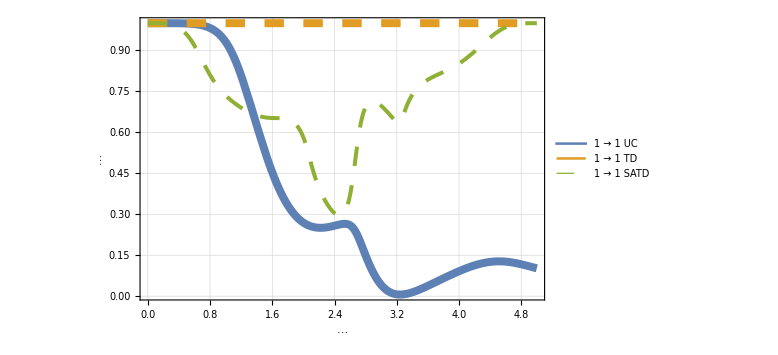

```mathematica
Plot[{Abs[({{1, 0}}).U[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).U[t].({{1}, {0}})]^2+Abs[({{0, 1}}).U[t].({{1}, {0}})]^2),Abs[({{1, 0}}).UTD[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UTD[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UTD[t].({{1}, {0}})]^2),Abs[({{1, 0}}).USATD[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).USATD[t].({{1}, {0}})]^2+Abs[({{0, 1}}).USATD[t].({{1}, {0}})]^2)
},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{Style["(*GraphicsBox[{Thickness[0.023441162681669007`], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGIlIGYCYvldC/al6sk7GGitFL7QourQG9Htz/hB1sHn
BLvt7KtaDhJNMlMMLn+3R+frg9SraDk88HuZ8Hf+bzi/D6R/A4sDjL/Na4PF
nJ8sDnMWKe/881wTzk9NAwI2BN8YBC5LwPlgcwTE4ea1KrCrnpkiBrcPxoe5
B51vAjZQFGJP2h/7qvs/bhl7i0LNY3OA8c+AQA8nnH+ge1+TyWMeOP8giL9Y
CM4XqZxUcpZFxAFmPowPs999zdHlDDOE4HyYeTA+WN9mHocdwVYR/9XF4fy1
Qjp86fck4HzpeXGapw004fyaTxsCsn9pws2Dha/6J5WXszoF4Hywe5aIwvkz
ZgKBpQyc/2Xfx63pZbIO56+GvdG/reEQ8PbyxxmKcvD4R08PAE9E2P4=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJLIGYC4h0OTY+O31B3EKmcVHKWRcYBxpfftWBfqp+M
w6MI8e0XD6g7GBgDQbGMwya9vMWMcxD8jVC+PpTfwHK037AcIT9jAn+VWba6
Q8jbyx9nOGLyZZe/8NCLV3dQ/6TycpamjINoj9crFhN1h/Q0EJCG8LeoORzs
3tdkwizpcOFq2Bv92aoOZ0BgjajDjJlAYKkC53fbeO5Ka1KG8/fm17ydWars
sFZIhy/9nhicX3P/xy3j1+IOe9D4qOolHNzXHF3O0KHs8MA13nFWoaSD38WJ
Mf+SVR2eJC68ZqKv4uBzgt129lR1OD8+JEh9AacGnO+xv1bWwh2TP6W9Nery
HASfAQQeqDiIT73CmaGE4M9ZpLzzz3J1OP8pyJx+VThfZl6c5ukCNYfzoHCJ
1nBIANnfqeYgDRLfgOBPBtm3B8EH2/scwQfTnprQ8FRz+A8C9ZoOW8x/HEp5
pQrng+V3IvgbVJ80z9NVdVgPonM1If76o+KwGaRvlYYDC2eXfDKfCty9K769
rDhzQRHO548NuG8UjuCDzZXH5L8q3ir6OxvBh4Wn84RmoTQvBB8cb/sQ/NLD
21xn3lWG86tB8eyt5LAj2Cri/3FpiH4pJYcY1QiZczJSkPjmUHI4AEpviyXh
fFj6g/HByfOYGCRdXFRymAkOFxFIuKqrwPmQ+FKD82H5qz+i259xg7QDev4D
AHbzfLc=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJ5IGYC4tQ0IFim6xD09vLHGYyiDjA+iEo7Ju4QcEu6
JtFI18HEGAguSzqkxN5xY7bQgfMz8j+0nizRhvPBtLC2w5d9H7emT5OA8zU+
qbyc1SkO58eoRsicqxFzYOHskk/Og+o3FnU4fthpbaadDpy/VvVJ87xeBF9m
Xpzm6Qs6DiKVk0rOpog6uO+vlbVg13V44BrvOOuiqINoj9crFhFdiH0vRR3+
g4A8bv5fNP6b4q2iv7V1HRhAwAHBh4UPjN8f0e3PWCAMt/8zyL9hAg4tvP7r
pyzVdtjutcFiTiWXg8TUK5wZSdoO/k88L5kGc8L5YO985sDJ3wbWz+HwIEJ8
+8UGbYi7/7M7yCx/4aE3H8E/vmtHL9sFBB8Wf2dAgIffAT1+AcZ8zHk=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJLIGYC4hgFx4/JOaYOIpWTSs6yyDjA+PK7FuxL9ZNx
KFjTfTsjwdTBwBgIimUcIsS3X2Tww+TrQ/mOTY+Oz7BGyPucYLedbWrqEPL2
8scZjpj8CcElKtP1TR3UP6m8nKUp48DlplrKJGXqkJ4GAtIQ/i0Th4Pd+5pM
mCUdXmRpf5vua+JwBgTWiELoOcZwfo/XKxYTRwRf9UnzvLNWxg5rhXT40u+J
wfk193/cMn4t7qCCxkdVL+Hgf3FizD9nY4cHrvGOswolHVa88ND7b2ji8CRx
4TUTfRUHNZB6L1M430BrpfCFFgR/yf19fHMWY/KntLdGXZ6D4DOAwAMViPsn
Ivh+IPuDEfxPGwKyZ7mbwPk8/uunpO4wcTh/NeyNfrQGxP4jJg7S8+I0T29A
8CeD7NuD4Hvsr5W1eI7gJ4QEqS/w1ISGp4nDfxCo13S4JV2TaFSK4IPlYxD8
G0KfHM+LmTisBwVcrqbD6cNOazP/GTtsNv9xKGWVhkMjy9F+w3ZjuHt5Qe7N
MILz7UHpRRvBB5vLj8l/VbxV9Hc2gg8Lz9sg96ki+I9BdDyCXwLUdjrPGM73
BqW/pUYOO4KtIv4fl3awrYxYYdpr5BCjGiFzTkYKEt/NRg4HQOltsSScD0t/
MD44eR4Tc6j/bVVw7oWRw0wQ2CkCic/JxnA+OL6Om8D5sPzVH9Htz7hB2gE9
/wEAO+WEmw==
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAwBWIQ3RdcojI93tJBpHJSyVkWGQcYP+Tt5Y8zHGUcFt/f
xzcn2NLBwBgIimUcur1esZg4IvjeJ9htZ6si+OJTr3BmKFk6yO9asC/VT8YB
JGwsbOmwXkiHL71O2sHv4sSYf4ctHHYEW0X8Vxd3uC70yfG8m4XDGRBYI+qw
4oWH3v+H5nD+iyztb9P3IvgH25aHn5pk7vDANd5x1kUEnwEEHMThfPVPKi9n
dUo4fNoQkD1ru7mD+5qjyxl+SDpovOXdZ3DT3CE9DQSkHUq2iv4+vc7CodPG
c1eakhJUvQXE3cFKDraVEStMz1o4rPz2suLMAQQfHF4mynC+DygcTFUc/n4r
fTCn0MJhSntr1GUZVYeNenmLGe+Yw/kmIHMPm8H5EqDwCjKDuG+FIpzPHxtw
36gcwQ/nFGs3jleEuDfODOIeB0VIeBYj+OD460fwwfonmTl8WLRe4WwEVP88
M4e1oPhYp+iQEnvHjfmFmUMEyPz1yhD3xpg7/Hz7+oDlYhVIeF5C8E8edlqb
+Q7Bh8Q31L9zEPyZIHBTGc6vvP/jlrG1ssMW8x+HUn5B469QCR7f1SD514oO
B2plLdJLzCHpI10ezoekJ3mHGAXHj8k8sPiUgppn5tCuwK56xkQK7h+I+ZJw
/pd9H7emT5OA8/siuv0ZC8QcwMnAzRzi3p0i8PQB44Pj86MFnA/LH/0g/Ruk
HdDzDwDQs2oE
"], {{25.2781, 12.739099999999999`}, {25.2781, 12.917200000000001`}, {25.134399999999996`, 13.131299999999996`}, {24.873399999999997`, 13.131299999999996`}, {24.598399999999998`, 13.131299999999996`}, {24.2891, 12.8688}, {24.2891, 12.5594}, {24.2891, 12.260899999999998`}, {24.5391, 12.165599999999998`}, {24.6828, 12.165599999999998`}, {25.004699999999996`, 12.165599999999998`}, {25.2781, 12.4766}, {25.2781, 12.739099999999999`}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxdlQ1MW1UUx8tYhiw6HFtbPsrKa0twbG6TD53vvZb/08nULM6ACVU3EaV0
6hQUFocBl4iOMJjowjbARgfMsCU4NEoEDBXFpdMVWAMhZlPLDLoRQcUQAtm0
9t7bd1/0Ji/NLzfn63/OuRWeKct3Ret0uqjwVxH+VoQ/szL/rH9OwfqqY5Uj
K01Q+bG58fkWxQTfRvHYxWsKtmWFT4UJH8ibJ9p+0vjQDbF89JLG/ZeP/O0a
U2AeOOV1PRKx9ynoid+8xv16MpoXVxW1nFaQSu7PGVHXVfhd5n4FfnK69Zgu
bp/M3qoxtTdrTP3HKGglp19jHTkwcn4yzWkarU5AoKwoZjRRrS+J+0v/yzbT
Vp+EF2KXT7klBW+mxqT5J0wIkXNIwf3v1MaXigJn6+TPBTqPhfNn9yx9XbLa
htnbvNtaH1bQXPfWE+OmNKbPJDjfurun2VWu8ePGzwO6DcCuCzH293Js+PD6
g1tCX+Wy+vwW1BA9+3Jxp2Be2G+wYVfg3T3/FORy+1+IPmUOzkcLKm0ni+yc
aX5jMvPnsSJ9jiQo48rGlO5QtJXdN8lMr6dtGDocbkC8zO2pXaPE+cualO3u
bI0LSf6/i/B0WPtv+iL5fSoyf1NWyFXOMzk1Io9nPD4Ruy9fjMQVOMftfTSY
+arGhbGGuqwiAZW9+hsXnxJxdnHmoB8C81+h8Z7U8IA2atxE6m8S4SoNnzwB
NxcPTHnaRZBxzBqP3I+JqAouXc6SrGghcxMrYXnut6F7O204HfSu8dRqTO+/
1biL9OeqhLvlwfwTisY7yHwcsXJW66X+hiW4ST4GCy4M3/fRc+ck/NnRkzri
FNi+OCUcJPk0pODjLS91RpkkDDV438juTGR2qySsI/NakoCtGWfXXZoW0Vcg
OkPpBs53kPmd0XNm86/n9mw/1vP+qazGV1mtP5/se5Se5eOR+H7R+tolLHjn
e92Lelx7ftPiyUGJvQ/txsjcRu5PJLA+x8nsN2hi+VXKGCyrnms9LsA2Xfv+
yGsy26+BsB4rzzfd5ZPZfs1aULL3h7zo7XY4yTz0WNl9nZ3rT+f/DzvvzwJd
eAdnFldjGm91LmzUv5Xzzu7zXbolC2c2LxqzflnYXP3q4O+Bj/TT64CH6LNs
5szeDzNuyUs7sKLNwftL51Fx4G1nw+6o2xPwfXJ1cWaOA3kkvtOIb8j+WRyY
PfxiQ2aygbPaX5XV/tJ+7nDw/tH9eUVjJ9nPUY3tZB9/dGDqgSKlLaBn79FS
xH+9ke1HTy7fR/ou9Ub0OSOAjEdWBv67DwGNuxuu7NPFKZxpfjaF662yqrfK
9fJDA6UdAkj40HUgSPJbu4G93z6gjuiZnRypA2ik+iWx+J+A1fNyImd1/lSm
epcbUDw8vsl1FVwP+l5nKJypHn0aq/9/tB9fJOP//4//AvvkPH0=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGBQBmIQvfNW19/U6S4O6WkgIOUA48vvWrAvdZ2Ug96EBT8M
+1wcau7/uGX8WsrB4trRXJMOBN+h6dHxGc0I/ooXHnr/G10c/oPAfSmHtuXh
p4xKXBzuu8Y7ziqUcnjDu89gppCLg0jlpJKzKWIOM0Gg0dnhDAisEXU4oWk1
6bQ7gl//26rg3AcnOP93TO7Rf4ecHEyMgeCyOJw/HWROpDScDzafRQbO/7Lv
49Z0M1mHi/nx7OduOkHco6jgoP6ked5ZLWc4f6Ne3mLGEAQf7L/dzg7lh7e5
ztRVcGBZPMmKkdXFQfnao2CGOQoOtSD3VbhA3OejCA+PtUI6fOnrlOB8sLyM
MpzfANKnoQLxv6eLw5T21qjLMqoQdU+c4fwp39jiZ7gg+Pqg+Ihzgui7qQTn
w/wH47cqsKueMZGA+HcnVP1OEbh5MD44fkRc4HyU9HBM0gE9fQAAZ8MLqw==

"], {{40.6703, 9.556249999999999}, {40.6703, 8.304689999999999}, {38.762499999999996`, 8.304689999999999}, {38.262499999999996`, 8.304689999999999}, {37.7609, 8.304689999999999}, {38.2734, 10.1391}, {39.406299999999995`, 10.318799999999998`}, {39.787499999999994`, 10.318799999999998`}, {40.3125, 10.318799999999998`}, {40.6703, 10.007799999999998`}, {40.6703, 9.556249999999999}}}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{63.99483437110834, 24.508064757160646`},PlotRange->{{0., 42.660000000000004`}, {0., 16.34}}])",15],Style["(*GraphicsBox[{Thickness[0.018857250612860643`], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAwBmIQLVI5qeTsEmWHjPwPrSdD1B1gfOl5cZqnDTQdHrjG
O84SVHKQmHqFM+ORlkPA28sfZyjKwfmqn1RezjrJB+dv9dpgMecnD5wvs1Fs
PpMCJp+Fs0s+OQ/BlwHbh9AP4/M48nnNyOSD86NVI2TOyQhh8P+DgSacP6W9
NeryHtz818VbRX93azqcAYE3gnD/bgPbz+bwpi2322i3hINdiWPtaRk2h76I
bn9GAXGHF7WPs8+/YXVoVWBXPTNFzOEvyNr6f/YwPtg/D37B+RDzfmDwZ4LA
TlE438QYBEQd3oDMX/MLzhdvkplicPk3nJ8zNaHQovg/nH+we1+TyWJGh6r7
P24Ze4s69IPcWcAM588AW8QH54PdYSKAxhd0gJkHCx8Yf62QDl96HYIvDEof
LMIYfHB4SYvB+TD/uq85upxhhhCcD46m+4Jwfot4LWsmGx+c3wty/wdehxqQ
+14j+OB0mSIO54eA0uFCcbj+L/s+bk3/Jg5NT1DzTCTg/gH7Q08JYr+8FJzv
PKFZKC1KAc6HpX9wepmj4oCePwCVdT16
"], {{8.82031, 11.915599999999998`}, {8.82031, 11.6063}, {8.665629999999998, 10.592199999999998`}, {8.117189999999999, 10.0438}, {7.914059999999999, 9.82969}, {7.3421899999999996`, 9.37656}, {6.2562500000000005`, 9.37656}, {4.57656, 9.37656}, {5.387499999999999, 12.6313}, {5.4937499999999995`, 13.071899999999998`}, {5.54219, 13.095300000000002`}, {6.0062500000000005`, 13.095300000000002`}, {7.185939999999999, 13.095300000000002`}, {8.081249999999999, 13.095300000000002`}, {8.82031, 12.809399999999997`}, {8.82031, 11.915599999999998`}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxFk2tIFFEYhlfXDImU1F2tVndnZ2ZnZy9mrhqlwUcXu1BqFrmFWparXRHS
8EpGJpJmaam5JWr6QyxlhW4qKpYIUl6x+mGBBgaaSiEhltW2Z2b2zAfnxzMz
58z3vu/5iDPpcRapRCJxcazdjuXqWG4eJcqzd4LA7CEvNtlIcPKRyc35yVco
UNQlse/GjFBZXHRyQkGDHVW9AfNCxgvZ6lM95lCTo+7rYCb58cdQGwUhHLOQ
M7UyaYogobaR7PyTxsLb/l1t569RILt98Jtbphbvl6C6zmD+u3x1urZCgzkl
8XOU1F8DqVxRfL8jwr5pUnhOwyc2oNUuJaGm3Cs3fB0NPen5i9YqArNXYuxU
SJbI8Uj/KQKixysS/pE0tCzPZQ8BwZ8fLXJg8+z+oAKRb66PsVUW0WBBv40i
4PSxOKahhQYk2zQhvF+jEb539GN1VI4Gfi3O921voqCdnimsu8xg5vy1i/xs
28qbFJ0Wxj4cX9gSIfKe8kLv1BISs1Mvd94iA2moH7kafqNz+hn40WhTDZsJ
wT8GslEepQF8DnUa6CvtvRHatJHPL0MDPjn3ModT/GGwq6PMPVgDHUd3mO2M
HLN2iZp7OCfDzPkPMrwfybR2+sJXdA9GReby3MBg5v1jQNXV0GvxlMFzpOcJ
A69RP1I5n3s3A75cP3KhXy3sax1oltQECPq0UGYujXFpD4TwyJ646i9aSKDN
ipFuJZ+LOwtt3gbPtCQVBOtafMYoltc3o8L3MQ/5MU9A3lJ77MVcFm5FHuhK
VatBgfJW6iCr/+Ve62GS969DJ+RLwrTZ79W4RA9GQvnzklzIr16P8+Pythow
j6IcV0WevaBffpBohE1ozsopGELVauT9OUHxc/TdAIcG1+58FEZBG8q3zIDn
1clcvlqRufyr1RCG/HAx8vffooYCt4G7W+NF9qt673HONQizc/45f1dEdv7v
P3WExDg=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{21.2359, 8.57813}, {21.2359, 9.71094}, {20.496899999999997`, 10.5563}, {19.412499999999998`, 10.5563}, {17.8391, 10.5563}, {16.2891, 8.840629999999999}, {16.2891, 7.159379999999999}, {16.2891, 6.02656}, {17.0281, 5.1812499999999995`}, {18.112499999999997`, 5.1812499999999995`}, {19.698400000000003`, 5.1812499999999995`}, {21.2359, 6.8968799999999995`}, {21.2359, 8.57813}}, CompressedData["
1:eJxTTMoPSmViYGAQBmIQDQYFJg63NWXX/GdWcoDxwznF2o35FSF8AxMHkcpJ
JWdZZB026uUtZtxj7BCjGiFzTkbKoWSr6O/TdsYONfd/3DJ+LeZwXeiT4/lp
Rg5nQGCNqMN/EJBH8BtZjvYbthvC+elpQCBm6NCqwK56Zoo4nA8xTwrOh9gn
69AfXKIyPd7QofzwNteZfxUcbkvXJBptNXRYK6TDl66n5HD6sNPaTDsjB9+L
E2P+Mas4qL/l3Wfw0sjh59vXBywXq0DMSzOG88H++YPgw/wfAfL/emUH9PAB
ADKNeF8=
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGDQBGIQvb9W1iLdxMohnFOs3The0QHGX/HtZcWZCcoO3ifY
bWdPtXSY0t4adVlG1UF6Xpzm6Q0WcP6yFx56/wURfImpVzgzmswddBXlv+SI
qTjw+a+fkuph7nAGBOYoOzSyHO03VLeA8Hu0HLaY/ziUomXhoK+1UvjCEi2H
wjXdtzMMLBwSQoLUF5xE8OcsUt755zmC38ILNFhV22GjXt5iRh7cfL+LE2P+
JZs7pKcBAZu2AwMIGJg7PIgQ336RQRviXiZzh4z8D60nv2g5ODQ9Oj7jtJkD
C2eXfPI7Lah/zCD0Iy2Iu3PMHDaA7LmD4IPV5yH4MqBwMtBymDGBv8qsG8Hn
clMtZVqF4HuBwtfVHINf82lDQPYvTTgfHL57EPyAW9I1iZM0HWwrI1aY6po7
mNnsDZr2UANijoK5g2iP1yuWEg2HL0BjZl03g4SnpppDyVbR36f/mTrEqEbI
nNsj5zAhuERl+ntTh4r7P24Zd8vC+W/acruNdsvA+WD1Mgg+OBwdxB1eZGl/
mz7XzGEmCOwUgYc3jP9l562uv0ct4HxY+jIxBoLL0g7o6Q8AseMHzA==
"], CompressedData["
1:eJxTTMoPSmViYGAQAWIQvVEvbzHjGQsH9U8qL2d1Sjn8B4F6C4cv+z5uTf8m
7rDk/j6+OZ/NHc6AwBpRh0aWo/2G6Qi+1wl229msCL7qk+Z5Z2eZOTxwjXec
dVEMzoeZD+PHqEbInJORgZi/2MxBpHJSyVkWWYj8LTOH8sPbXGfqKjjIzIvT
PK1g7mAMAsFKDjeEPjmeVzN3uK0pu+Z/s5LDtAn8VWa3zR1+vn19wHKxisMW
8x+HUlZZwPnSIP0GlnB+hPj2iwx5lg4ZaUAwTRnO/7BovcLZCCU4/w7IfGNF
B17/9VNSJSzh7kMPLwCx0pM9
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{28.593799999999987`, 5.871880000000001}, {28.593799999999987`, 6.2171899999999996`}, {28.3078, 6.456250000000001}, {28.021900000000002`, 6.456250000000001}, {27.674999999999997`, 6.456250000000001}, {27.437499999999996`, 6.17031}, {27.437499999999996`, 5.88438}, {27.437499999999996`, 5.539059999999999}, {27.723399999999994`, 5.300000000000001}, {28.009399999999996`, 5.300000000000001}, {28.354699999999998`, 5.300000000000001}, {28.593799999999987`, 5.585939999999999}, {28.593799999999987`, 5.871880000000001}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJ5IGYC4jMg8MbeIejt5Y8zGEUdYPw0EDgm7nCgbXn4
qU32DibGQHBZ0sHnBLvtbFMk/sWJMf8u28H5YHqxncOXfR+3pk+TgPM1Pqm8
nNUpDufHqEbInKsRc5CZF6d5+gJUv7GoQ+1vq4JzFvZwfv6a7tsZCQj+0hce
ev8b7R1EKieVnE0RdbCtjFhhOtfe4YFrvOOsi6IOS+7v45uz2B5i30tRhxkz
gWAlbv50NH5/cInK9PX2Dgwg4IDgw8IHxu+P6PZnLBCG2/8Z5N8wAYcYBceP
yW/sHLZ7bbCYU8nloPKked7ZU3YO/k88L5kGc8L5YO985sDJ3wbWz+HA4aZa
ynTLzuE/GLA7aLzl3WfwEsH/8630wRxGezgfFn9gmoffAT1+Af1C3uk=
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAwBmIQfaBW1iL9jqtDRv6H1pMh6g4wvvS8OM3TBpoOXzYE
ZM8qd3WQmHqFM+ORlsPOW11/U7e7wPnHNa0mnb7vBOerPmmed/YQgn9buibR
aCsmn4WzSz45D8GXAduH0A/jX8yPZz93E8Ev2Sr6+7SZMwb/PxhowvlT2luj
Lu/BzX9dDGR0azrU/7YqOGfgDPcv2P4kJ4c3bbndRrslHFgXT7JiDHVy6Ivo
9mcUEHdY/sJD73+gk0OrArvqmSliDk8SF14zee4I59/fxzfH+BSC/zsm9+i/
XZj8mSCwUxTONzEGAVEHd9VSplknEHyw/y8i+CBnn36H4At/cjyfxuvkUHX/
xy1jb1GI/VoI/hkQuIPgg837icaXdIabBwsfGB/sPicEvzJihenZYEw+OLyk
xeB8mH91Jyz4YejmjBpe+gi+fdOj4zMuO6GG3yUnhxqQ+14j+CKVk0rOpojD
+SFvL3+csVAcrv/Lvo9b07+JQ9LTVah5JhJw/6wV0uFL11OC2G/uAueD/c/p
CufD0j84vcxRcUDPHwCDDFd4
"], {{42.720299999999995`, 11.915599999999998`}, {42.720299999999995`, 11.6063}, {42.565599999999996`, 10.592199999999998`}, {42.0172, 10.0438}, {41.814099999999996`, 9.82969}, {41.2422, 9.37656}, {40.156299999999995`, 9.37656}, {38.47659999999999, 9.37656}, {39.287499999999994`, 12.6313}, {39.3938, 13.071899999999998`}, {39.44219999999999, 13.095300000000002`}, {39.906299999999995`, 13.095300000000002`}, {41.08590000000001, 13.095300000000002`}, {41.981300000000005`, 13.095300000000002`}, {42.720299999999995`, 12.809399999999997`}, {42.720299999999995`, 11.915599999999998`}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{44.7688, 8.459380000000001}, {44.7688, 8.634379999999998}, {44.64059999999999, 8.760939999999998}, {44.45779999999999, 8.760939999999998}, {44.251599999999996`, 8.760939999999998}, {44.021899999999995`, 8.57031}, {44.021899999999995`, 8.331249999999999}, {44.021899999999995`, 8.156249999999998}, {44.148399999999995`, 8.02969}, {44.3313, 8.02969}, {44.537499999999994`, 8.02969}, {44.7688, 8.22031}, {44.7688, 8.459380000000001}}, CompressedData["
1:eJxTTMoPSmViYGAwB2IQ7XOC3XZ2qZtD5f0ft4y7hRxg/GjVCJlzd6D8XDeH
VgV21TNfhBzSwADBf7CPb45xFIJvce1orkkEVP8eIYdb0jWJRqFuDtUg87OF
HBQcPyafsXVz+A8C+/kdNurlLWYUcXNIBRmrxuuQw/lzQfprVzj/SeLCayb3
EfxfMblH/11ydbjBe1sstQzBf1H7OPu8Dj+cPxMEIgUclr3w0Pt/09XhDAi8
EYCY99zVQf2TystZLwUdSraK/j7N5uYQA3JvjQjEf2puDn0R3f6MAuIOO291
/U3Vh4bPaXEHh6ZHx2dYu0HUHZOA8x+6xjvOCpSE83cEW0X8fy4FcY+Qm4NI
5aSSsywycP/A+AdqZS3SaxD8i/nx7OcCXR0egMybKA7ng81TR/DXCunwpd8T
c6j9bVVwLsLVYQ2Iv0/MIaREZfr/BARfb8KCH4Z5CD7Y/nxXB4VdC/alvhOD
xF+RqwMDCDiIQ8KjD+oeFylI/O91dQh4e/njDEVpSHzdQfDB+l8h+GD/fHF1
cF9zdDnDDyk4vx2UPkQQ/APd+5pMDktC4vuzKzz8erxesZi8dIWknxgJSHo5
6+pQBQp/bTEHialXODM2QcNHUATODwLZzygCcf80aHgdF4SE10RXB3mQf/0E
IemgB5EeYPxgkP5EBD8dFL/LoOlxs6uDfYlj7ekYbrj7YPwNoPDwcYPzYfkH
bJ4iIj/B8hcANHN/1g==
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJJIGYC4h6vVywmje4OvRHd/owGPA4wfvDbyx9nKAo4
uKmWMs3KcHfYGWwV8b9d0GGjXt5iRhsEn8d//ZRUCTR5FneHg937mkwWC8D5
BctLNvzr54fzW8RrWTOP8TrsvNX1N1Xc3eE/GHA7sCyeZMVoi+CLfHI8nxaK
4E/5xhY/I8XdwcQYCD7z4OT7P/G8ZHqZwyENBMKg8sasqPbZM0LEhd0dCkHu
42eE+F/Q3aEfFB4fGOB86Y1i85kWIPj2JY61p2UYHBIOX9ZOlXR3yJmaUGhR
/N8eHB4KCD7YPToIPix8GUDgAIsDevgDAFc8oR4=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}}}, {{{50.882799999999996`, 8.459380000000001}, {50.882799999999996`, 8.60938}, {50.762499999999996`, 8.760939999999998}, {50.57189999999999, 8.760939999999998}, {50.3344, 8.760939999999998}, {50.12659999999999, 8.53906}, {50.12659999999999, 8.331249999999999}, {50.12659999999999, 8.181249999999999}, {50.2469, 8.02969}, {50.43749999999999, 8.02969}, {50.675, 8.02969}, {50.882799999999996`, 8.25156}, {50.882799999999996`, 8.459380000000001}}, CompressedData["
1:eJxTTMoPSmViYGAwAGIQrTthwQ9DN0+Hmvs/bhm/Fnfo9nrFYuLp6XAGBHwk
HIxBwNvTQX7Xgn2pfQj+zmCriP/sknD+DhD/uJTDPBudK7PkPB1EKieVnGWR
cbBvenR8xmMPOP/zhoDsWeUIvqtqKdMsCw+HB67xjrMmisP5YPPUEfy1Qjp8
6ffEHI5rWk06be/hsAbE3wfluyP4v2Jyj/4LQvA36uUtZgzxcPiy7+PW9Gti
EPdGezj0RXT7MwaIO1zMj2c/V+nhEPz28scZjZIO3ifYbWev9XAIAPEVpR14
/NdPSX2A4Ms7fkw+8xXBX/7CQ+8/IzR81knB+WD5hZJwPtg+A0mH1d23Mxj+
w9wnAXHfHw94eO+vlbVIn+Ph4P/E85LpZQ4HlsWTrBh7PRwmgPR/YIG7v3B5
yYZ/5xkcbkrXJBrJIvhgc3gQfB+Qf/66Q/j8jA4OoPj47e4gvVFsPpMCI8Q8
aWj4iDE5PE5ceM1EHuqeM8xwvgxIfQILnJ8GAs9Y4fZt9dpgMWcnm8MXUPx+
d4fzl4H8fxPBB6ePfe4OB7v3NZkos8L56p9UXs7iZIbzwe5bwODQtjz8lNET
dwcW/V9cl3j+2euB0qucB5wPlo9B45/xgPirmNHhDe8+g5mvoOEpzOmAnt4B
eMpEFw==
"]}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{79.54099128268992, 24.508064757160646`},PlotRange->{{0., 53.03}, {0., 16.34}}])", 15]}, PlotLegends->Placed[{"1 → 1 UC", "1 → 1 TD","1 → 1 SATD"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Dashing[Large],Thickness[0.01]}, {Dashing[Large],Thickness[0.005]}, {Dashing[Large],Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

### 6b

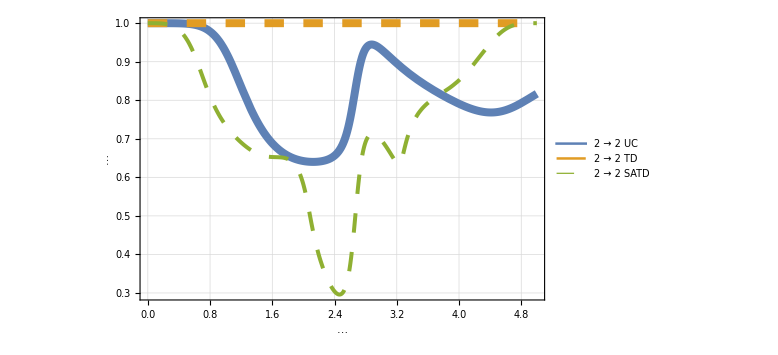

```mathematica
Plot[{Abs[({{0, 1}}).U[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).U[t].({{0}, {1}})]^2+Abs[({{0, 1}}).U[t].({{0}, {1}})]^2),Abs[({{0, 1}}).UTD[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UTD[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UTD[t].({{0}, {1}})]^2),Abs[({{0, 1}}).USATD[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).USATD[t].({{0}, {1}})]^2+Abs[({{0, 1}}).USATD[t].({{0}, {1}})]^2)
},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{Style["(*GraphicsBox[{Thickness[0.023441162681669007`], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGIlIGYCYvldC/al6sk7GGitFL7QourQG9Htz/hB1sHn
BLvt7KtaDhJNMlMMLn+3R+frg9SraDk88HuZ8Hf+bzi/D6R/A4sDjL/Na4PF
nJ8sDnMWKe/881wTzk9NAwI2BN8YBC5LwPlgcwTE4ea1KrCrnpkiBrcPxoe5
B51vAjZQFGJP2h/7qvs/bhl7i0LNY3OA8c+AQA8nnH+ge1+TyWMeOP8giL9Y
CM4XqZxUcpZFxAFmPowPs999zdHlDDOE4HyYeTA+WN9mHocdwVYR/9XF4fy1
Qjp86fck4HzpeXGapw004fyaTxsCsn9pws2Dha/6J5WXszoF4Hywe5aIwvkz
ZgKBpQyc/2Xfx63pZbIO56+GvdG/reEQ8PbyxxmKcvD4R08PAE9E2P4=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJLIGYC4h0OTY+O31B3EKmcVHKWRcYBxpfftWBfqp+M
w6MI8e0XD6g7GBgDQbGMwya9vMWMcxD8jVC+PpTfwHK037AcIT9jAn+VWba6
Q8jbyx9nOGLyZZe/8NCLV3dQ/6TycpamjINoj9crFhN1h/Q0EJCG8LeoORzs
3tdkwizpcOFq2Bv92aoOZ0BgjajDjJlAYKkC53fbeO5Ka1KG8/fm17ydWars
sFZIhy/9nhicX3P/xy3j1+IOe9D4qOolHNzXHF3O0KHs8MA13nFWoaSD38WJ
Mf+SVR2eJC68ZqKv4uBzgt129lR1OD8+JEh9AacGnO+xv1bWwh2TP6W9Nery
HASfAQQeqDiIT73CmaGE4M9ZpLzzz3J1OP8pyJx+VThfZl6c5ukCNYfzoHCJ
1nBIANnfqeYgDRLfgOBPBtm3B8EH2/scwQfTnprQ8FRz+A8C9ZoOW8x/HEp5
pQrng+V3IvgbVJ80z9NVdVgPonM1If76o+KwGaRvlYYDC2eXfDKfCty9K769
rDhzQRHO548NuG8UjuCDzZXH5L8q3ir6OxvBh4Wn84RmoTQvBB8cb/sQ/NLD
21xn3lWG86tB8eyt5LAj2Cri/3FpiH4pJYcY1QiZczJSkPjmUHI4AEpviyXh
fFj6g/HByfOYGCRdXFRymAkOFxFIuKqrwPmQ+FKD82H5qz+i259xg7QDev4D
AHbzfLc=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJ5IGYC4tQ0IFim6xD09vLHGYyiDjA+iEo7Ju4QcEu6
JtFI18HEGAguSzqkxN5xY7bQgfMz8j+0nizRhvPBtLC2w5d9H7emT5OA8zU+
qbyc1SkO58eoRsicqxFzYOHskk/Og+o3FnU4fthpbaadDpy/VvVJ87xeBF9m
Xpzm6Qs6DiKVk0rOpog6uO+vlbVg13V44BrvOOuiqINoj9crFhFdiH0vRR3+
g4A8bv5fNP6b4q2iv7V1HRhAwAHBh4UPjN8f0e3PWCAMt/8zyL9hAg4tvP7r
pyzVdtjutcFiTiWXg8TUK5wZSdoO/k88L5kGc8L5YO985sDJ3wbWz+HwIEJ8
+8UGbYi7/7M7yCx/4aE3H8E/vmtHL9sFBB8Wf2dAgIffAT1+AcZ8zHk=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJLIGYC4hgFx4/JOaYOIpWTSs6yyDjA+PK7FuxL9ZNx
KFjTfTsjwdTBwBgIimUcIsS3X2Tww+TrQ/mOTY+Oz7BGyPucYLedbWrqEPL2
8scZjpj8CcElKtP1TR3UP6m8nKUp48DlplrKJGXqkJ4GAtIQ/i0Th4Pd+5pM
mCUdXmRpf5vua+JwBgTWiELoOcZwfo/XKxYTRwRf9UnzvLNWxg5rhXT40u+J
wfk193/cMn4t7qCCxkdVL+Hgf3FizD9nY4cHrvGOswolHVa88ND7b2ji8CRx
4TUTfRUHNZB6L1M430BrpfCFFgR/yf19fHMWY/KntLdGXZ6D4DOAwAMViPsn
Ivh+IPuDEfxPGwKyZ7mbwPk8/uunpO4wcTh/NeyNfrQGxP4jJg7S8+I0T29A
8CeD7NuD4Hvsr5W1eI7gJ4QEqS/w1ISGp4nDfxCo13S4JV2TaFSK4IPlYxD8
G0KfHM+LmTisBwVcrqbD6cNOazP/GTtsNv9xKGWVhkMjy9F+w3ZjuHt5Qe7N
MILz7UHpRRvBB5vLj8l/VbxV9Hc2gg8Lz9sg96ki+I9BdDyCXwLUdjrPGM73
BqW/pUYOO4KtIv4fl3awrYxYYdpr5BCjGiFzTkYKEt/NRg4HQOltsSScD0t/
MD44eR4Tc6j/bVVw7oWRw0wQ2CkCic/JxnA+OL6Om8D5sPzVH9Htz7hB2gE9
/wEAO+WEmw==
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAwBWIQ3RdcojI93tJBpHJSyVkWGQcYP+Tt5Y8zHGUcFt/f
xzcn2NLBwBgIimUcur1esZg4IvjeJ9htZ6si+OJTr3BmKFk6yO9asC/VT8YB
JGwsbOmwXkiHL71O2sHv4sSYf4ctHHYEW0X8Vxd3uC70yfG8m4XDGRBYI+qw
4oWH3v+H5nD+iyztb9P3IvgH25aHn5pk7vDANd5x1kUEnwEEHMThfPVPKi9n
dUo4fNoQkD1ru7mD+5qjyxl+SDpovOXdZ3DT3CE9DQSkHUq2iv4+vc7CodPG
c1eakhJUvQXE3cFKDraVEStMz1o4rPz2suLMAQQfHF4mynC+DygcTFUc/n4r
fTCn0MJhSntr1GUZVYeNenmLGe+Yw/kmIHMPm8H5EqDwCjKDuG+FIpzPHxtw
36gcwQ/nFGs3jleEuDfODOIeB0VIeBYj+OD460fwwfonmTl8WLRe4WwEVP88
M4e1oPhYp+iQEnvHjfmFmUMEyPz1yhD3xpg7/Hz7+oDlYhVIeF5C8E8edlqb
+Q7Bh8Q31L9zEPyZIHBTGc6vvP/jlrG1ssMW8x+HUn5B469QCR7f1SD514oO
B2plLdJLzCHpI10ezoekJ3mHGAXHj8k8sPiUgppn5tCuwK56xkQK7h+I+ZJw
/pd9H7emT5OA8/siuv0ZC8QcwMnAzRzi3p0i8PQB44Pj86MFnA/LH/0g/Ruk
HdDzDwDQs2oE
"], {{25.2781, 12.739099999999999`}, {25.2781, 12.917200000000001`}, {25.134399999999996`, 13.131299999999996`}, {24.873399999999997`, 13.131299999999996`}, {24.598399999999998`, 13.131299999999996`}, {24.2891, 12.8688}, {24.2891, 12.5594}, {24.2891, 12.260899999999998`}, {24.5391, 12.165599999999998`}, {24.6828, 12.165599999999998`}, {25.004699999999996`, 12.165599999999998`}, {25.2781, 12.4766}, {25.2781, 12.739099999999999`}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxdlQ1MW1UUx8tYhiw6HFtbPsrKa0twbG6TD53vvZb/08nULM6ACVU3EaV0
6hQUFocBl4iOMJjowjbARgfMsCU4NEoEDBXFpdMVWAMhZlPLDLoRQcUQAtm0
9t7bd1/0Ji/NLzfn63/OuRWeKct3Ret0uqjwVxH+VoQ/szL/rH9OwfqqY5Uj
K01Q+bG58fkWxQTfRvHYxWsKtmWFT4UJH8ibJ9p+0vjQDbF89JLG/ZeP/O0a
U2AeOOV1PRKx9ynoid+8xv16MpoXVxW1nFaQSu7PGVHXVfhd5n4FfnK69Zgu
bp/M3qoxtTdrTP3HKGglp19jHTkwcn4yzWkarU5AoKwoZjRRrS+J+0v/yzbT
Vp+EF2KXT7klBW+mxqT5J0wIkXNIwf3v1MaXigJn6+TPBTqPhfNn9yx9XbLa
htnbvNtaH1bQXPfWE+OmNKbPJDjfurun2VWu8ePGzwO6DcCuCzH293Js+PD6
g1tCX+Wy+vwW1BA9+3Jxp2Be2G+wYVfg3T3/FORy+1+IPmUOzkcLKm0ni+yc
aX5jMvPnsSJ9jiQo48rGlO5QtJXdN8lMr6dtGDocbkC8zO2pXaPE+cualO3u
bI0LSf6/i/B0WPtv+iL5fSoyf1NWyFXOMzk1Io9nPD4Ruy9fjMQVOMftfTSY
+arGhbGGuqwiAZW9+hsXnxJxdnHmoB8C81+h8Z7U8IA2atxE6m8S4SoNnzwB
NxcPTHnaRZBxzBqP3I+JqAouXc6SrGghcxMrYXnut6F7O204HfSu8dRqTO+/
1biL9OeqhLvlwfwTisY7yHwcsXJW66X+hiW4ST4GCy4M3/fRc+ck/NnRkzri
FNi+OCUcJPk0pODjLS91RpkkDDV438juTGR2qySsI/NakoCtGWfXXZoW0Vcg
OkPpBs53kPmd0XNm86/n9mw/1vP+qazGV1mtP5/se5Se5eOR+H7R+tolLHjn
e92Lelx7ftPiyUGJvQ/txsjcRu5PJLA+x8nsN2hi+VXKGCyrnms9LsA2Xfv+
yGsy26+BsB4rzzfd5ZPZfs1aULL3h7zo7XY4yTz0WNl9nZ3rT+f/DzvvzwJd
eAdnFldjGm91LmzUv5Xzzu7zXbolC2c2LxqzflnYXP3q4O+Bj/TT64CH6LNs
5szeDzNuyUs7sKLNwftL51Fx4G1nw+6o2xPwfXJ1cWaOA3kkvtOIb8j+WRyY
PfxiQ2aygbPaX5XV/tJ+7nDw/tH9eUVjJ9nPUY3tZB9/dGDqgSKlLaBn79FS
xH+9ke1HTy7fR/ou9Ub0OSOAjEdWBv67DwGNuxuu7NPFKZxpfjaF662yqrfK
9fJDA6UdAkj40HUgSPJbu4G93z6gjuiZnRypA2ik+iWx+J+A1fNyImd1/lSm
epcbUDw8vsl1FVwP+l5nKJypHn0aq/9/tB9fJOP//4//AvvkPH0=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGBQBmIQvfNW19/U6S4O6WkgIOUA48vvWrAvdZ2Ug96EBT8M
+1wcau7/uGX8WsrB4trRXJMOBN+h6dHxGc0I/ooXHnr/G10c/oPAfSmHtuXh
p4xKXBzuu8Y7ziqUcnjDu89gppCLg0jlpJKzKWIOM0Gg0dnhDAisEXU4oWk1
6bQ7gl//26rg3AcnOP93TO7Rf4ecHEyMgeCyOJw/HWROpDScDzafRQbO/7Lv
49Z0M1mHi/nx7OduOkHco6jgoP6ked5ZLWc4f6Ne3mLGEAQf7L/dzg7lh7e5
ztRVcGBZPMmKkdXFQfnao2CGOQoOtSD3VbhA3OejCA+PtUI6fOnrlOB8sLyM
MpzfANKnoQLxv6eLw5T21qjLMqoQdU+c4fwp39jiZ7gg+Pqg+Ihzgui7qQTn
w/wH47cqsKueMZGA+HcnVP1OEbh5MD44fkRc4HyU9HBM0gE9fQAAZ8MLqw==

"], {{40.6703, 9.556249999999999}, {40.6703, 8.304689999999999}, {38.762499999999996`, 8.304689999999999}, {38.262499999999996`, 8.304689999999999}, {37.7609, 8.304689999999999}, {38.2734, 10.1391}, {39.406299999999995`, 10.318799999999998`}, {39.787499999999994`, 10.318799999999998`}, {40.3125, 10.318799999999998`}, {40.6703, 10.007799999999998`}, {40.6703, 9.556249999999999}}}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{63.99483437110834, 24.508064757160646`},PlotRange->{{0., 42.660000000000004`}, {0., 16.34}}])",15],Style["(*GraphicsBox[{Thickness[0.018857250612860643`], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAwBmIQLVI5qeTsEmWHjPwPrSdD1B1gfOl5cZqnDTQdHrjG
O84SVHKQmHqFM+ORlkPA28sfZyjKwfmqn1RezjrJB+dv9dpgMecnD5wvs1Fs
PpMCJp+Fs0s+OQ/BlwHbh9AP4/M48nnNyOSD86NVI2TOyQhh8P+DgSacP6W9
NeryHtz818VbRX93azqcAYE3gnD/bgPbz+bwpi2322i3hINdiWPtaRk2h76I
bn9GAXGHF7WPs8+/YXVoVWBXPTNFzOEvyNr6f/YwPtg/D37B+RDzfmDwZ4LA
TlE438QYBEQd3oDMX/MLzhdvkplicPk3nJ8zNaHQovg/nH+we1+TyWJGh6r7
P24Ze4s69IPcWcAM588AW8QH54PdYSKAxhd0gJkHCx8Yf62QDl96HYIvDEof
LMIYfHB4SYvB+TD/uq85upxhhhCcD46m+4Jwfot4LWsmGx+c3wty/wdehxqQ
+14j+OB0mSIO54eA0uFCcbj+L/s+bk3/Jg5NT1DzTCTg/gH7Q08JYr+8FJzv
PKFZKC1KAc6HpX9wepmj4oCePwCVdT16
"], {{8.82031, 11.915599999999998`}, {8.82031, 11.6063}, {8.665629999999998, 10.592199999999998`}, {8.117189999999999, 10.0438}, {7.914059999999999, 9.82969}, {7.3421899999999996`, 9.37656}, {6.2562500000000005`, 9.37656}, {4.57656, 9.37656}, {5.387499999999999, 12.6313}, {5.4937499999999995`, 13.071899999999998`}, {5.54219, 13.095300000000002`}, {6.0062500000000005`, 13.095300000000002`}, {7.185939999999999, 13.095300000000002`}, {8.081249999999999, 13.095300000000002`}, {8.82031, 12.809399999999997`}, {8.82031, 11.915599999999998`}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxFk2tIFFEYhlfXDImU1F2tVndnZ2ZnZy9mrhqlwUcXu1BqFrmFWparXRHS
8EpGJpJmaam5JWr6QyxlhW4qKpYIUl6x+mGBBgaaSiEhltW2Z2b2zAfnxzMz
58z3vu/5iDPpcRapRCJxcazdjuXqWG4eJcqzd4LA7CEvNtlIcPKRyc35yVco
UNQlse/GjFBZXHRyQkGDHVW9AfNCxgvZ6lM95lCTo+7rYCb58cdQGwUhHLOQ
M7UyaYogobaR7PyTxsLb/l1t569RILt98Jtbphbvl6C6zmD+u3x1urZCgzkl
8XOU1F8DqVxRfL8jwr5pUnhOwyc2oNUuJaGm3Cs3fB0NPen5i9YqArNXYuxU
SJbI8Uj/KQKixysS/pE0tCzPZQ8BwZ8fLXJg8+z+oAKRb66PsVUW0WBBv40i
4PSxOKahhQYk2zQhvF+jEb539GN1VI4Gfi3O921voqCdnimsu8xg5vy1i/xs
28qbFJ0Wxj4cX9gSIfKe8kLv1BISs1Mvd94iA2moH7kafqNz+hn40WhTDZsJ
wT8GslEepQF8DnUa6CvtvRHatJHPL0MDPjn3ModT/GGwq6PMPVgDHUd3mO2M
HLN2iZp7OCfDzPkPMrwfybR2+sJXdA9GReby3MBg5v1jQNXV0GvxlMFzpOcJ
A69RP1I5n3s3A75cP3KhXy3sax1oltQECPq0UGYujXFpD4TwyJ646i9aSKDN
ipFuJZ+LOwtt3gbPtCQVBOtafMYoltc3o8L3MQ/5MU9A3lJ77MVcFm5FHuhK
VatBgfJW6iCr/+Ve62GS969DJ+RLwrTZ79W4RA9GQvnzklzIr16P8+Pythow
j6IcV0WevaBffpBohE1ozsopGELVauT9OUHxc/TdAIcG1+58FEZBG8q3zIDn
1clcvlqRufyr1RCG/HAx8vffooYCt4G7W+NF9qt673HONQizc/45f1dEdv7v
P3WExDg=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{21.2359, 8.57813}, {21.2359, 9.71094}, {20.496899999999997`, 10.5563}, {19.412499999999998`, 10.5563}, {17.8391, 10.5563}, {16.2891, 8.840629999999999}, {16.2891, 7.159379999999999}, {16.2891, 6.02656}, {17.0281, 5.1812499999999995`}, {18.112499999999997`, 5.1812499999999995`}, {19.698400000000003`, 5.1812499999999995`}, {21.2359, 6.8968799999999995`}, {21.2359, 8.57813}}, CompressedData["
1:eJxTTMoPSmViYGAQBmIQDQYFJg63NWXX/GdWcoDxwznF2o35FSF8AxMHkcpJ
JWdZZB026uUtZtxj7BCjGiFzTkbKoWSr6O/TdsYONfd/3DJ+LeZwXeiT4/lp
Rg5nQGCNqMN/EJBH8BtZjvYbthvC+elpQCBm6NCqwK56Zoo4nA8xTwrOh9gn
69AfXKIyPd7QofzwNteZfxUcbkvXJBptNXRYK6TDl66n5HD6sNPaTDsjB9+L
E2P+Mas4qL/l3Wfw0sjh59vXBywXq0DMSzOG88H++YPgw/wfAfL/emUH9PAB
ADKNeF8=
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGDQBGIQvb9W1iLdxMohnFOs3The0QHGX/HtZcWZCcoO3ifY
bWdPtXSY0t4adVlG1UF6Xpzm6Q0WcP6yFx56/wURfImpVzgzmswddBXlv+SI
qTjw+a+fkuph7nAGBOYoOzSyHO03VLeA8Hu0HLaY/ziUomXhoK+1UvjCEi2H
wjXdtzMMLBwSQoLUF5xE8OcsUt755zmC38ILNFhV22GjXt5iRh7cfL+LE2P+
JZs7pKcBAZu2AwMIGJg7PIgQ336RQRviXiZzh4z8D60nv2g5ODQ9Oj7jtJkD
C2eXfPI7Lah/zCD0Iy2Iu3PMHDaA7LmD4IPV5yH4MqBwMtBymDGBv8qsG8Hn
clMtZVqF4HuBwtfVHINf82lDQPYvTTgfHL57EPyAW9I1iZM0HWwrI1aY6po7
mNnsDZr2UANijoK5g2iP1yuWEg2HL0BjZl03g4SnpppDyVbR36f/mTrEqEbI
nNsj5zAhuERl+ntTh4r7P24Zd8vC+W/acruNdsvA+WD1Mgg+OBwdxB1eZGl/
mz7XzGEmCOwUgYc3jP9l562uv0ct4HxY+jIxBoLL0g7o6Q8AseMHzA==
"], CompressedData["
1:eJxTTMoPSmViYGAQAWIQvVEvbzHjGQsH9U8qL2d1Sjn8B4F6C4cv+z5uTf8m
7rDk/j6+OZ/NHc6AwBpRh0aWo/2G6Qi+1wl229msCL7qk+Z5Z2eZOTxwjXec
dVEMzoeZD+PHqEbInJORgZi/2MxBpHJSyVkWWYj8LTOH8sPbXGfqKjjIzIvT
PK1g7mAMAsFKDjeEPjmeVzN3uK0pu+Z/s5LDtAn8VWa3zR1+vn19wHKxisMW
8x+HUlZZwPnSIP0GlnB+hPj2iwx5lg4ZaUAwTRnO/7BovcLZCCU4/w7IfGNF
B17/9VNSJSzh7kMPLwCx0pM9
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{28.593799999999987`, 5.871880000000001}, {28.593799999999987`, 6.2171899999999996`}, {28.3078, 6.456250000000001}, {28.021900000000002`, 6.456250000000001}, {27.674999999999997`, 6.456250000000001}, {27.437499999999996`, 6.17031}, {27.437499999999996`, 5.88438}, {27.437499999999996`, 5.539059999999999}, {27.723399999999994`, 5.300000000000001}, {28.009399999999996`, 5.300000000000001}, {28.354699999999998`, 5.300000000000001}, {28.593799999999987`, 5.585939999999999}, {28.593799999999987`, 5.871880000000001}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJ5IGYC4jMg8MbeIejt5Y8zGEUdYPw0EDgm7nCgbXn4
qU32DibGQHBZ0sHnBLvtbFMk/sWJMf8u28H5YHqxncOXfR+3pk+TgPM1Pqm8
nNUpDufHqEbInKsRc5CZF6d5+gJUv7GoQ+1vq4JzFvZwfv6a7tsZCQj+0hce
ev8b7R1EKieVnE0RdbCtjFhhOtfe4YFrvOOsi6IOS+7v45uz2B5i30tRhxkz
gWAlbv50NH5/cInK9PX2Dgwg4IDgw8IHxu+P6PZnLBCG2/8Z5N8wAYcYBceP
yW/sHLZ7bbCYU8nloPKked7ZU3YO/k88L5kGc8L5YO985sDJ3wbWz+HA4aZa
ynTLzuE/GLA7aLzl3WfwEsH/8630wRxGezgfFn9gmoffAT1+Af1C3uk=
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAwBmIQfaBW1iL9jqtDRv6H1pMh6g4wvvS8OM3TBpoOXzYE
ZM8qd3WQmHqFM+ORlsPOW11/U7e7wPnHNa0mnb7vBOerPmmed/YQgn9buibR
aCsmn4WzSz45D8GXAduH0A/jX8yPZz93E8Ev2Sr6+7SZMwb/PxhowvlT2luj
Lu/BzX9dDGR0azrU/7YqOGfgDPcv2P4kJ4c3bbndRrslHFgXT7JiDHVy6Ivo
9mcUEHdY/sJD73+gk0OrArvqmSliDk8SF14zee4I59/fxzfH+BSC/zsm9+i/
XZj8mSCwUxTONzEGAVEHd9VSplknEHyw/y8i+CBnn36H4At/cjyfxuvkUHX/
xy1jb1GI/VoI/hkQuIPgg837icaXdIabBwsfGB/sPicEvzJihenZYEw+OLyk
xeB8mH91Jyz4YejmjBpe+gi+fdOj4zMuO6GG3yUnhxqQ+14j+CKVk0rOpojD
+SFvL3+csVAcrv/Lvo9b07+JQ9LTVah5JhJw/6wV0uFL11OC2G/uAueD/c/p
CufD0j84vcxRcUDPHwCDDFd4
"], {{42.720299999999995`, 11.915599999999998`}, {42.720299999999995`, 11.6063}, {42.565599999999996`, 10.592199999999998`}, {42.0172, 10.0438}, {41.814099999999996`, 9.82969}, {41.2422, 9.37656}, {40.156299999999995`, 9.37656}, {38.47659999999999, 9.37656}, {39.287499999999994`, 12.6313}, {39.3938, 13.071899999999998`}, {39.44219999999999, 13.095300000000002`}, {39.906299999999995`, 13.095300000000002`}, {41.08590000000001, 13.095300000000002`}, {41.981300000000005`, 13.095300000000002`}, {42.720299999999995`, 12.809399999999997`}, {42.720299999999995`, 11.915599999999998`}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{44.7688, 8.459380000000001}, {44.7688, 8.634379999999998}, {44.64059999999999, 8.760939999999998}, {44.45779999999999, 8.760939999999998}, {44.251599999999996`, 8.760939999999998}, {44.021899999999995`, 8.57031}, {44.021899999999995`, 8.331249999999999}, {44.021899999999995`, 8.156249999999998}, {44.148399999999995`, 8.02969}, {44.3313, 8.02969}, {44.537499999999994`, 8.02969}, {44.7688, 8.22031}, {44.7688, 8.459380000000001}}, CompressedData["
1:eJxTTMoPSmViYGAwB2IQ7XOC3XZ2qZtD5f0ft4y7hRxg/GjVCJlzd6D8XDeH
VgV21TNfhBzSwADBf7CPb45xFIJvce1orkkEVP8eIYdb0jWJRqFuDtUg87OF
HBQcPyafsXVz+A8C+/kdNurlLWYUcXNIBRmrxuuQw/lzQfprVzj/SeLCayb3
EfxfMblH/11ydbjBe1sstQzBf1H7OPu8Dj+cPxMEIgUclr3w0Pt/09XhDAi8
EYCY99zVQf2TystZLwUdSraK/j7N5uYQA3JvjQjEf2puDn0R3f6MAuIOO291
/U3Vh4bPaXEHh6ZHx2dYu0HUHZOA8x+6xjvOCpSE83cEW0X8fy4FcY+Qm4NI
5aSSsywycP/A+AdqZS3SaxD8i/nx7OcCXR0egMybKA7ng81TR/DXCunwpd8T
c6j9bVVwLsLVYQ2Iv0/MIaREZfr/BARfb8KCH4Z5CD7Y/nxXB4VdC/alvhOD
xF+RqwMDCDiIQ8KjD+oeFylI/O91dQh4e/njDEVpSHzdQfDB+l8h+GD/fHF1
cF9zdDnDDyk4vx2UPkQQ/APd+5pMDktC4vuzKzz8erxesZi8dIWknxgJSHo5
6+pQBQp/bTEHialXODM2QcNHUATODwLZzygCcf80aHgdF4SE10RXB3mQf/0E
IemgB5EeYPxgkP5EBD8dFL/LoOlxs6uDfYlj7ekYbrj7YPwNoPDwcYPzYfkH
bJ4iIj/B8hcANHN/1g==
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJJIGYC4h6vVywmje4OvRHd/owGPA4wfvDbyx9nKAo4
uKmWMs3KcHfYGWwV8b9d0GGjXt5iRhsEn8d//ZRUCTR5FneHg937mkwWC8D5
BctLNvzr54fzW8RrWTOP8TrsvNX1N1Xc3eE/GHA7sCyeZMVoi+CLfHI8nxaK
4E/5xhY/I8XdwcQYCD7z4OT7P/G8ZHqZwyENBMKg8sasqPbZM0LEhd0dCkHu
42eE+F/Q3aEfFB4fGOB86Y1i85kWIPj2JY61p2UYHBIOX9ZOlXR3yJmaUGhR
/N8eHB4KCD7YPToIPix8GUDgAIsDevgDAFc8oR4=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}}}, {{{50.882799999999996`, 8.459380000000001}, {50.882799999999996`, 8.60938}, {50.762499999999996`, 8.760939999999998}, {50.57189999999999, 8.760939999999998}, {50.3344, 8.760939999999998}, {50.12659999999999, 8.53906}, {50.12659999999999, 8.331249999999999}, {50.12659999999999, 8.181249999999999}, {50.2469, 8.02969}, {50.43749999999999, 8.02969}, {50.675, 8.02969}, {50.882799999999996`, 8.25156}, {50.882799999999996`, 8.459380000000001}}, CompressedData["
1:eJxTTMoPSmViYGAwAGIQrTthwQ9DN0+Hmvs/bhm/Fnfo9nrFYuLp6XAGBHwk
HIxBwNvTQX7Xgn2pfQj+zmCriP/sknD+DhD/uJTDPBudK7PkPB1EKieVnGWR
cbBvenR8xmMPOP/zhoDsWeUIvqtqKdMsCw+HB67xjrMmisP5YPPUEfy1Qjp8
6ffEHI5rWk06be/hsAbE3wfluyP4v2Jyj/4LQvA36uUtZgzxcPiy7+PW9Gti
EPdGezj0RXT7MwaIO1zMj2c/V+nhEPz28scZjZIO3ifYbWev9XAIAPEVpR14
/NdPSX2A4Ms7fkw+8xXBX/7CQ+8/IzR81knB+WD5hZJwPtg+A0mH1d23Mxj+
w9wnAXHfHw94eO+vlbVIn+Ph4P/E85LpZQ4HlsWTrBh7PRwmgPR/YIG7v3B5
yYZ/5xkcbkrXJBrJIvhgc3gQfB+Qf/66Q/j8jA4OoPj47e4gvVFsPpMCI8Q8
aWj4iDE5PE5ceM1EHuqeM8xwvgxIfQILnJ8GAs9Y4fZt9dpgMWcnm8MXUPx+
d4fzl4H8fxPBB6ePfe4OB7v3NZkos8L56p9UXs7iZIbzwe5bwODQtjz8lNET
dwcW/V9cl3j+2euB0qucB5wPlo9B45/xgPirmNHhDe8+g5mvoOEpzOmAnt4B
eMpEFw==
"]}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{79.54099128268992, 24.508064757160646`},PlotRange->{{0., 53.03}, {0., 16.34}}])", 15]}, PlotLegends->Placed[{"2 → 2 UC", "2 → 2 TD","2 → 2 SATD"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Dashing[Large],Thickness[0.01]}, {Dashing[Large],Thickness[0.005]}, {Dashing[Large],Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

### 6c

```mathematica
UC=ParallelMap[{N[#],1-UnCorrFidelityCheckAD[Δ0,Ω0,Γ,φ,ω,dir,#]}&,Range[1,50,1]]
```

{{1.,{0.902497,0.958442}},{2.,{0.641884,0.909539}},{3.,{0.412211,0.887477}},{4.,{0.270013,0.886636}},{5.,{0.183103,0.897908}},{6.,{0.126643,0.914636}},{7.,{0.0881573,0.93251}},{8.,{0.0612017,0.948986}},{9.,{0.0421448,0.962819}},{10.,{0.0287353,0.973663}},{11.,{0.0194294,0.981724}},{12.,{0.0130863,0.987466}},{13.,{0.00883997,0.991424}},{14.,{0.00603918,0.994087}},{15.,{0.00420817,0.995852}},{16.,{0.00301136,0.997018}},{17.,{0.00222044,0.997793}},{18.,{0.00168539,0.998321}},{19.,{0.00131084,0.998692}},{20.,{0.00103794,0.998964}},{21.,{0.000831217,0.999169}},{22.,{0.000669595,0.999331}},{23.,{0.000540501,0.99946}},{24.,{0.000436185,0.999564}},{25.,{0.000351553,0.999648}},{26.,{0.000282953,0.999717}},{27.,{0.000227544,0.999772}},{28.,{0.000182983,0.999817}},{29.,{0.000147291,0.999853}},{30.,{0.000118788,0.999881}},{31.,{0.0000960609,0.999904}},{32.,{0.000077942,0.999922}},{33.,{0.000063478,0.999937}},{34.,{0.0000519039,0.999948}},{35.,{0.0000426124,0.999957}},{36.,{0.0000351257,0.999965}},{37.,{0.0000290698,0.999971}},{38.,{0.000024152,0.999976}},{39.,{0.0000201437,0.99998}},{40.,{0.0000168652,0.999983}},{41.,{0.0000141746,0.999986}},{42.,{0.0000119596,0.999988}},{43.,{0.0000101303,0.99999}},{44.,{8.61505×10^-6,0.999991}},{45.,{7.35585×10^-6,0.999993}},{46.,{6.30604×10^-6,0.999994}},{47.,{5.42783×10^-6,0.999995}},{48.,{4.69059×10^-6,0.999995}},{49.,{4.06945×10^-6,0.999996}},{50.,{3.54418×10^-6,0.999996}}}

```mathematica
UC={{1.,{0.9629556890590412,0.9797730349946894}},{2.,{0.8393583135403244,0.9483216639021851}},{3.,{0.6598712855402984,0.9292765707799042}},{4.,{0.4809358554082822,0.9261027562194366}},{5.,{0.33407976343713663,0.9342874725810868}},{6.,{0.2242811235993888,0.9481321560080826}},{7.,{0.1459176111478836,0.9631195241095645}},{8.,{0.09172777754232464,0.9764011195515034}},{9.,{0.05542687832639126,0.9866204699640655}},{10.,{0.03202005974218658,0.9935235072348615}},{11.,{0.01761960703645138,0.9975381964612786}},{12.,{0.009250732126506178,0.9994149057361752}},{13.,{0.004706047671188651,0.999973789180444}},{14.,{0.0024230783921537213,0.9999572836688306}},{15.,{0.00136397776664543,0.9998998101288159}},{16.,{0.0008938095227634113,0.9999537741726727}},{17.,{0.0006642834445703683,0.9999985457144726}},{18.,{0.000512342280673761,0.9999901674387802}},{19.,{0.0003804064409392849,0.9999737620752162}},{20.,{0.0002605386425647005,0.9999741481765926}},{21.,{0.00016053954227157607,0.999986313567456}},{22.,{0.00008721595233207591,0.9999975019781648}},{23.,{0.00004106855179153435,0.9999993532984305}},{24.,{0.00001711434152695812,0.9999910270057094}},{25.,{7.891675070204052*^-6,0.9999847913362232}},{26.,{6.2775371368894994*^-6,0.9999947014238115}},{27.,{7.121354960948345*^-6,0.9999999527883532}},{28.,{7.634856943217194*^-6,0.9999990388694922}},{29.,{6.943444575746582*^-6,0.9999979296816908}},{30.,{5.302814458763017*^-6,0.9999979646596825}},{31.,{3.3679857456281326*^-6,0.9999987201204112}},{32.,{1.711829609285509*^-6,0.999999542973683}},{33.,{6.226890957305997*^-7,0.9999999862001284}},{34.,{1.0947659323523595*^-7,0.999999516303717}},{35.,{1.0195019051195686*^-8,0.9999957790086963}},{36.,{1.1548755762813556*^-7,0.9999999950039249}},{37.,{2.5581105056460274*^-7,0.9999998917987678}},{38.,{3.3754134476371433*^-7,0.9999997674161987}},{39.,{3.379243791457043*^-7,0.9999997316321299}},{40.,{2.7869162255722557*^-7,0.9999997664925204}},{41.,{1.9674450379980613*^-7,0.999999832357157}},{42.,{1.231820843106135*^-7,0.9999998954697564}},{43.,{7.409775060196466*^-8,0.9999999378369753}},{44.,{5.101214339831017*^-8,0.9999999566690446}},{45.,{4.643601936304975*^-8,0.9999999585526657}},{46.,{5.028204530521663*^-8,0.9999999529567565}},{47.,{5.445074113819004*^-8,0.9999999476421991}},{48.,{5.4744037192300254*^-8,0.9999999466041947}},{49.,{5.0580377997100356*^-8,0.9999999502867706}},{50.,{4.35608800142262*^-8,0.9999999569964393}}};
```

```mathematica
TD=ParallelMap[{N[#],1-N[UnCorrFidelityCheckTD[Δ0,Ω0,Γ,φ,ω,dir,#]]}&,Range[1,50,1]]
```

{{1.,{0.,0.}},{2.,{0.,0.}},{3.,{0.,0.}},{4.,{0.,0.}},{5.,{0.,0.}},{6.,{0.,0.}},{7.,{0.,0.}},{8.,{0.,0.}},{9.,{0.,0.}},{10.,{0.,0.}},{11.,{0.,0.}},{12.,{0.,0.}},{13.,{0.,0.}},{14.,{0.,0.}},{15.,{0.,0.}},{16.,{0.,0.}},{17.,{0.,0.}},{18.,{0.,0.}},{19.,{0.,0.}},{20.,{0.,0.}},{21.,{0.,0.}},{22.,{0.,0.}},{23.,{0.,0.}},{24.,{0.,0.}},{25.,{0.,0.}},{26.,{0.,0.}},{27.,{0.,0.}},{28.,{0.,0.}},{29.,{0.,0.}},{30.,{0.,0.}},{31.,{0.,0.}},{32.,{0.,0.}},{33.,{0.,0.}},{34.,{0.,0.}},{35.,{0.,0.}},{36.,{0.,0.}},{37.,{0.,0.}},{38.,{0.,0.}},{39.,{0.,0.}},{40.,{0.,0.}},{41.,{0.,0.}},{42.,{0.,0.}},{43.,{0.,0.}},{44.,{0.,0.}},{45.,{0.,0.}},{46.,{0.,0.}},{47.,{0.,0.}},{48.,{0.,0.}},{49.,{0.,0.}},{50.,{0.,0.}}}

```mathematica
TD={{1.,{0.,0.}},{2.,{0.,0.}},{3.,{0.,0.}},{4.,{0.,0.}},{5.,{0.,0.}},{6.,{0.,0.}},{7.,{0.,0.}},{8.,{0.,0.}},{9.,{0.,0.}},{10.,{0.,0.}},{11.,{0.,0.}},{12.,{0.,0.}},{13.,{0.,0.}},{14.,{0.,0.}},{15.,{0.,0.}},{16.,{0.,0.}},{17.,{0.,0.}},{18.,{0.,0.}},{19.,{0.,0.}},{20.,{0.,0.}},{21.,{0.,0.}},{22.,{0.,0.}},{23.,{0.,0.}},{24.,{0.,0.}},{25.,{0.,0.}},{26.,{0.,0.}},{27.,{0.,0.}},{28.,{0.,0.}},{29.,{0.,0.}},{30.,{0.,0.}},{31.,{0.,0.}},{32.,{0.,0.}},{33.,{0.,0.}},{34.,{0.,0.}},{35.,{0.,0.}},{36.,{0.,0.}},{37.,{0.,0.}},{38.,{0.,0.}},{39.,{0.,0.}},{40.,{0.,0.}},{41.,{0.,0.}},{42.,{0.,0.}},{43.,{0.,0.}},{44.,{0.,0.}},{45.,{0.,0.}},{46.,{0.,0.}},{47.,{0.,0.}},{48.,{0.,0.}},{49.,{0.,0.}},{50.,{0.,0.}}};
```

```mathematica
SATD=ParallelMap[{N[#],1-N[UnCorrFidelityCheckSATD[Δ0,Ω0,Γ,φ,ω,dir,#]]}&,Range[1,50,1]]
```

{{1.,{1.,1.}},{2.,{1.,1.}},{3.,{1.,1.}},{4.,{1.,1.}},{5.,{0.,0.}},{6.,{1.,1.}},{7.,{1.,1.}},{8.,{1.,1.}},{9.,{1.,1.}},{10.,{1.,1.}},{11.,{1.,1.}},{12.,{1.,1.}},{13.,{1.,1.}},{14.,{1.,1.}},{15.,{1.,1.}},{16.,{1.,1.}},{17.,{1.,1.}},{18.,{1.,1.}},{19.,{0.,2.38698×10^-14}},{20.,{0.,7.31637×10^-14}},{21.,{0.,2.03282×10^-13}},{22.,{0.,5.14366×10^-13}},{23.,{0.,1.44673×10^-12}},{24.,{0.,2.57494×10^-12}},{25.,{0.,7.10976×10^-12}},{26.,{0.,3.33867×10^-11}},{27.,{0.,5.11128×10^-11}},{28.,{0.,3.35527×10^-10}},{29.,{0.,1.19729×10^-9}},{30.,{0.,2.99665×10^-9}},{31.,{0.,8.84003×10^-9}},{32.,{0.,2.62733×10^-8}},{33.,{0.,6.77287×10^-8}},{34.,{0.,5.34286×10^-7}},{35.,{0.,9.37593×10^-9}},{36.,{0.,1.0743×10^-6}},{37.,{0.,3.62947×10^-6}},{38.,{0.,0.0000177264}},{39.,{0.,0.0000452689}},{40.,{0.,0.000153026}},{41.,{0.,0.000481852}},{42.,{0.,0.00010737}},{43.,{0.,0.00128769}},{44.,{0.,0.00592904}},{45.,{0.,0.0234652}},{46.,{0.,0.108746}},{47.,{0.,0.0902643}},{48.,{0.,0.251257}},{49.,{0.,0.520665}},{50.,{0.,0.92716}}}

```mathematica
SATD={{1.,{0.,0.}},{2.,{0.,0.}},{3.,{0.,0.}},{4.,{0.,0.}},{5.,{0.,0.}},{6.,{0.,0.}},{7.,{0.,0.}},{8.,{0.,0.}},{9.,{0.,0.}},{10.,{0.,0.}},{11.,{0.,0.}},{12.,{0.,0.}},{13.,{0.,0.}},{14.,{0.,0.}},{15.,{0.,0.}},{16.,{0.,0.}},{17.,{0.,0.}},{18.,{0.,0.}},{19.,{0.,0.}},{20.,{0.,0.}},{21.,{0.,0.}},{22.,{0.,0.}},{23.,{0.,0.}},{24.,{0.,0.}},{25.,{0.,0.}},{26.,{0.,4.440892098500626*^-16}},{27.,{0.,2.55351295663786*^-15}},{28.,{0.,9.43689570931383*^-15}},{29.,{0.,2.531308496145357*^-14}},{30.,{0.,6.650235917504688*^-14}},{31.,{0.,1.532107773982716*^-13}},{32.,{0.,3.0386804183990535*^-13}},{33.,{0.,4.618527782440651*^-13}},{34.,{0.,6.444844657949034*^-13}},{35.,{0.,3.097522238704187*^-13}},{36.,{0.,6.301625887772389*^-13}},{37.,{0.,7.264966406239637*^-12}},{38.,{0.,1.56900048509101*^-11}},{39.,{0.,3.097899714532559*^-11}},{40.,{0.,5.928102453367501*^-11}},{41.,{0.,1.1843614977635752*^-10}},{42.,{0.,2.5566160299916874*^-10}},{43.,{0.,5.791687129885759*^-10}},{44.,{0.,1.3165496470790572*^-9}},{45.,{0.,2.9190720951532967*^-9}},{46.,{0.,6.280617914633524*^-9}},{47.,{0.,1.3266267973044421*^-8}},{48.,{0.,2.7945439629029067*^-8}},{49.,{0.,5.9439211996803465*^-8}},{50.,{0.,1.287676408834315*^-7}}};
```

```mathematica
L2LUC=Map[{UC[[;;,1]][[#]],UC[[;;,2,1]][[#]]}&,Range[1,Length[UC[[;;,1]]]]];
G2GUC=Map[{UC[[;;,1]][[#]],UC[[;;,2,2]][[#]]}&,Range[1,Length[UC[[;;,1]]]]];

L2LTD=Map[{TD[[;;,1]][[#]],If[TD[[;;,2,1]][[#]]===Indeterminate || TD[[;;,2,1]][[#]]==0,N[10^(-16)],TD[[;;,2,1]][[#]]]}&,Range[1,Length[TD[[;;,1]]]]];
G2GTD=Map[{TD[[;;,1]][[#]],If[TD[[;;,2,2]][[#]]===Indeterminate|| TD[[;;,2,2]][[#]]==0,N[10^(-16)],TD[[;;,2,2]][[#]]]}&,Range[1,Length[TD[[;;,1]]]]];

L2LSATD=Map[{SATD[[;;,1]][[#]],If[SATD[[;;,2,1]][[#]]===Indeterminate|| SATD[[;;,2,1]][[#]]==0,N[10^(-16)],SATD[[;;,2,1]][[#]]]}&,Range[1,Length[SATD[[;;,1]]]]];
G2GSATD=Map[{SATD[[;;,1]][[#]],If[SATD[[;;,2,2]][[#]]===Indeterminate|| SATD[[;;,2,2]][[#]]==0,N[10^(-16)],SATD[[;;,2,2]][[#]]]}&,Range[1,Length[SATD[[;;,1]]]]];
```

```mathematica
(*again note our convention for gain and loss modes are switched, so P++ (G2G for gain-to-gain) corresponds to P-- (L2L for loss-to-loss)in this section of the notebook*)
```

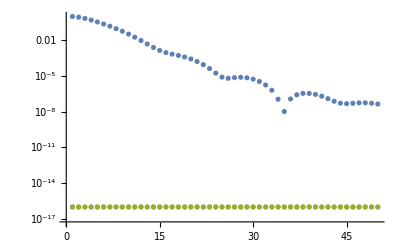

```mathematica
ListLogPlot[{L2LUC,L2LTD,L2LSATD}]
```

### 6d

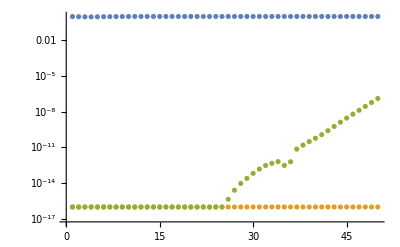

```mathematica
ListLogPlot[{G2GUC,G2GTD,G2GSATD}]
```

## TD, and SATD EP Encircling Check (Fig. 7)

### Functions used for numerics

```mathematica
σx=({{0, 1}, {1, 0}});
σy=({{0, -ⅈ}, {ⅈ, 0}});
σz=({{1, 0}, {0, -1}});
```

```mathematica
(*choosen contour*)
ΔCircPath:=Function[{Δ0,φ,x},
Δ0 Sin[2 π x+φ]
];

ΩCircPath:=Function[{Δ0,Ω0,φ,x},
Ω0 + Δ0 Cos[2π x+φ]
];
(*time dependant parametrization of contour for single (ωCirc1) and double loop (ωCirc1DL)*)
ωCirc1:=#1(6(#3/#2)^5-15(#3/#2)^4+10(#3/#2)^3)&;
ωCirc1DL:=(ωCirc1[#1,#2,#3]UnitStep[#2-#3]+((#1)+ωCirc1[#1,#2,#3-#2])UnitStep[#3-#2])&;
```

```mathematica
(*constucting the holomorphic eigenvalue, works for a double loop*)
EigCircPath:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},

(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2)

];
```

```mathematica
(*constucting thederivative of the holomorphic eigenvalue, works for a double loop*)
EigDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])((2 ⅈ π Δ0 (Γ Cos[φ+2 π ω[dir,t0,t]]+2 ⅈ Ω0 Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,1][ω][dir,t0,t])/(√(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])))
];
```

```mathematica
(*constucting the holomorphic pseduo rotation angle into the adiabatic frame, works for a double loop*)
θDiagCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
-2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)+(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]
];
```

```mathematica
(*constucting the derivative of the pseduo rotation angle into the adiabatic frame.*)
θDiagDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(4 π Δ0 (2 Δ0+2 Ω0 Cos[φ+2 π ω[dir,t0,t]]+ⅈ Γ Sin[φ+2 π ω[dir,t0,t]]))/(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])Derivative[0,0,1][ω][dir,t0,t]
];
```

```mathematica
(*constucting the 2nd derivative of the pseduo rotation angle into the adiabatic frame.*)
θDiagDDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(4 π Δ0 (2 π (Γ^2+4 (Δ0-Ω0) (Δ0+Ω0)) (-ⅈ Γ Cos[φ+2 π ω[dir,t0,t]]+2 Ω0 Sin[φ+2 π ω[dir,t0,t]]) (Derivative[0,0,1][ω][dir,t0,t])^2+(4 Δ0 (-Γ^2+2 Δ0^2+4 Ω0^2)-2 Ω0 (Γ^2-4 (3 Δ0^2+Ω0^2)) Cos[φ+2 π ω[dir,t0,t]]+2 Δ0 (Γ^2+4 Ω0^2) Cos[2 (φ+2 π ω[dir,t0,t])]+ⅈ Γ (-Γ^2+4 (3 Δ0^2+Ω0^2)+16 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]) Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,2][ω][dir,t0,t]))/(Γ^2-4 (Δ0^2+Ω0^2)-8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]-4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])^2
];
```

```mathematica
(*SATD correction fields in the lab frame using the holomorphic functions*)
gxCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
Cos[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]/2((-EigDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]+ EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t] θDiagDDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])/(EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]^2+θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]^2))
];

gzCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
Sin[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]/2(-((-EigDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]+ EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t] θDiagDDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])/(EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]^2+θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]^2)))
];
```

```mathematica
(*The eigenvalues of the TD modified Hamiltonian*)
PosEigModTD:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2+(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])^2 )
];
```

```mathematica
(*The eigenvalues of the SATD modified Hamiltonian*)
PosEigModSATDCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ+gzCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]+gxCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])^2)
];
```

```mathematica
(*determining how many times the TD eigenvalues cross the branch cut for 1 loop*)
ZeroCrossing1LTD := Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{MinSearch,MinNoDuplicates},
(*checking over small intervals within loop time to see if if +λ=0 ever*)
MinSearch=ParallelMap[FindMinimum[Re[PosEigModTD[Δ0,Ω0,Γ,φ,ω,dir,t0,t]],{t,#},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->40]&,Range[t0/10,9/10 t0,(8t0)/(10 29)]];
(*determining if values found in "MinSearch" are truely 0 (<10^-16)*)
MinNoDuplicates=Sort[Select[DeleteDuplicates[Rationalize[Map[t/.Last[#]&,Cases[Chop[MinSearch,10^-16],{0,_}]],10^-16]],0<=#<=t0&]];
(*counting the number of times branch cut is crossed*)
Length[MinNoDuplicates]
]
]; 
(*determining how many times the SATD eigenvalues cross the branch cut for 1 loop*)
ZeroCrossing1LSATD := Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{MinSearch,MinNoDuplicates},
(*checking over small intervals within loop time to see if if +λ=0 ever*)
MinSearch=ParallelMap[FindMinimum[Re[PosEigModSATDCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]],{t,#},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->40]&,Range[t0/10,9/10 t0,(8t0)/(10 29)]];
(*determining if values found in "MinSearch" are truely 0 (<10^-16)*)
MinNoDuplicates=Sort[Select[DeleteDuplicates[Rationalize[Map[t/.Last[#]&,Cases[Chop[MinSearch,10^-16],{0,_}]],10^-16]],0<=#<=t0&]];
(*counting the number of times branch cut is crossed*)
Length[MinNoDuplicates]
]
]; 

(*determining how many times the SATD pseduo rotation angle crosses the branch cut for 1 loop*)
t0Critical:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{tb0sRet0,tb0sReCheckt0,tb0sImt0,tb0sRefinalt0,tb0sImfinalt0},
(*getting a list of times when Re[μ]=0*)
tb0sRet0=N[Select[Sort[DeleteDuplicates[Rationalize[ParallelMap[t/.FindRoot[Re[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])/EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]==0,{t,#},AccuracyGoal->Infinity,PrecisionGoal->32,WorkingPrecision->32]&,Range[0,9999/10000 t0,t0/99]],10^-16]]],#>=0&]];
(*checking the list of times outputed by tb0sRet0 indeed yield Re[μ]= and Im[μ]<0 to qualify as a branch cut*)
tb0sReCheckt0=Select[Select[Chop[Map[{Re[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#])/EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#]],#}&,tb0sRet0],10^-8], #[[1]]== 0&],0<#[[2]]< t0 &][[;;,2]];

tb0sImt0=Map[Im[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#])/EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#]]&,tb0sReCheckt0];
tb0sImfinalt0=Select[Map[{tb0sReCheckt0[[#]],tb0sImt0[[#]]}&,Range[1,Length[tb0sImt0]]],#[[2]]≥ 1|| #[[2]]≤ -1  &][[;;,2]];
(*# of times the branch cut is crossed*)
Length[tb0sImfinalt0]
]
];
```

```mathematica
(*finding the integral value for the TD eigenvalues over one loop*)
SLCriterionTD:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{MinSearch,MinNoDuplicates,IntBounds,IntVal,MultFact},
(*checking over small intervals within loop time to see if if +λ=0 ever*)
MinSearch=ParallelMap[FindMinimum[Re[PosEigModTD[Δ0,Ω0,Γ,φ,ω,dir,t0,t]],{t,#},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->40]&,Range[t0/10,9/10 t0,(8t0)/(10 29)]];
(*determining if values found in "MinSearch" are truely 0 (<10^-16)*)
MinNoDuplicates=Sort[Select[DeleteDuplicates[Rationalize[Map[t/.Last[#]&,Cases[Chop[MinSearch,10^-16],{0,_}]],10^-16]],0<=#<=t0&]];
(*if MinNoDuplicates=0, then no issues when integrating since there are no discontinuities*)
If[Length[MinNoDuplicates]==0,NIntegrate[PosEigModTD[Δ0,Ω0,Γ,φ,ω,dir,t0,t],{t,0,t0},Method->"LocalAdaptive"],
(*otherwise, make list of times when branch cut is crossed over double loop (hence the MinNoDuplicates+t0)*)
IntBounds=Partition[Sort[Join[{0,t0},MinNoDuplicates,MinNoDuplicates+t0]],2,1];
(*determine the value of the integrated +λ over the intervals in IntBounds*)
IntVal=ParallelMap[NIntegrate[PosEigModTD[Δ0,Ω0,Γ,φ,ω,dir,t0,t],{t,#[[1]],#[[2]]},Method->"LocalAdaptive"]&,IntBounds];
(*determine the +/- 1 sign change according to how many times the branch cut has been crossed for a given interval*)
MultFact=Table[(-1)^(i+1),{i,1,Length[IntVal]}];
(*return final value of integrated +λ by multiplying the integral intervals by their necessary sign change*)
Chop[Total[IntVal MultFact]]]
]
];
```

```mathematica
(*finding the integral value for the TD eigenvalues over two loops*)
DLCriterionTD:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{MinSearch,MinNoDuplicates,IntBounds,IntVal,MultFact},
(*checking over small intervals within loop time to see if if +λ=0 ever*)
MinSearch=ParallelMap[FindMinimum[Re[PosEigModTD[Δ0,Ω0,Γ,φ,ω,dir,t0,t]],{t,#},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->40]&,Range[t0/10,9/10 t0,(8t0)/(10 29)]];
(*determining if values found in "MinSearch" are truely 0 (<10^-16)*)
MinNoDuplicates=Sort[Select[DeleteDuplicates[Rationalize[Map[t/.Last[#]&,Cases[Chop[MinSearch,10^-16],{0,_}]],10^-16]],0<=#<=t0&]];
(*if MinNoDuplicates=0, then no issues when integrating since there are no discontinuities*)
If[Length[MinNoDuplicates]==0,NIntegrate[PosEigModTD[Δ0,Ω0,Γ,φ,ω,dir,t0,t],{t,0,2t0},Method->"LocalAdaptive"],
(*otherwise, make list of times when branch cut is crossed over double loop (hence the MinNoDuplicates+t0)*)
IntBounds=Partition[Sort[Join[{0,2t0},MinNoDuplicates,MinNoDuplicates+t0]],2,1];
(*determine the value of the integrated +λ over the intervals in IntBounds*)
IntVal=ParallelMap[NIntegrate[PosEigModTD[Δ0,Ω0,Γ,φ,ω,dir,t0,t],{t,#[[1]],#[[2]]},Method->"LocalAdaptive"]&,IntBounds];
(*determine the +/- 1 sign change according to how many times the branch cut has been crossed for a given interval*)
MultFact=Table[(-1)^(i+1),{i,1,Length[IntVal]}];
(*return final value of integrated +λ by multiplying the integral intervals by their necessary sign change*)
Chop[Total[IntVal MultFact]]]
]
];
```

```mathematica
(*finding the integral value for the SATD eigenvalues over one loop*)
SLCriterionSATDCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{MinSearch,MinNoDuplicates,IntBounds,IntVal,MultFact},
(*checking over small intervals within loop time to see if if +λ=0 ever*)
MinSearch=ParallelMap[FindMinimum[Re[PosEigModSATDCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]],{t,#},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->40]&,Range[t0/10,9/10 t0,(8t0)/(10 29)]];
(*determining if values found in "MinSearch" are truely 0 (<10^-16)*)
MinNoDuplicates=Sort[Select[DeleteDuplicates[Rationalize[Map[t/.Last[#]&,Cases[Chop[MinSearch,10^-16],{0,_}]],10^-16]],0<=#<=t0&]];
(*if MinNoDuplicates=0, then no issues when integrating since there are no discontinuities*)
If[Length[MinNoDuplicates]==0,NIntegrate[PosEigModSATDCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t],{t,0,t0},Method->"LocalAdaptive"],
(*otherwise, make list of times when branch cut is crossed over double loop (hence the MinNoDuplicates+t0)*)
IntBounds=Partition[Sort[Join[{0,t0},MinNoDuplicates,MinNoDuplicates+t0]],2,1];
(*determine the value of the integrated +λ over the intervals in IntBounds*)
IntVal=ParallelMap[NIntegrate[PosEigModSATDCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t],{t,#[[1]],#[[2]]},Method->"LocalAdaptive"]&,IntBounds];(*determine the +/- 1 sign change according to how many times the branch cut has been crossed for a given interval*)
MultFact=Table[(-1)^(i+1),{i,1,Length[IntVal]}];
(*return final value of integrated +λ by multiplying the integral intervals by their necessary sign change*)
Chop[Total[IntVal MultFact]]]
]
];
```

```mathematica
(*finding the integral value for the SATD eigenvalues over two loops*)
DLCriterionSATDCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{MinSearch,MinNoDuplicates,IntBounds,IntVal,MultFact},
(*checking over small intervals within loop time to see if if +λ=0 ever*)
MinSearch=ParallelMap[FindMinimum[Re[PosEigModSATDCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]],{t,#},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->40]&,Range[t0/10,9/10 t0,(8t0)/(10 29)]];
(*determining if values found in "MinSearch" are truely 0 (<10^-16)*)
MinNoDuplicates=Sort[Select[DeleteDuplicates[Rationalize[Map[t/.Last[#]&,Cases[Chop[MinSearch,10^-16],{0,_}]],10^-16]],0<=#<=t0&]];
(*if MinNoDuplicates=0, then no issues when integrating since there are no discontinuities*)
If[Length[MinNoDuplicates]==0,NIntegrate[PosEigModSATDCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t],{t,0,2t0},Method->"LocalAdaptive"],
(*otherwise, make list of times when branch cut is crossed over double loop (hence the MinNoDuplicates+t0)*)
IntBounds=Partition[Sort[Join[{0,2t0},MinNoDuplicates,MinNoDuplicates+t0]],2,1];
(*determine the value of the integrated +λ over the intervals in IntBounds*)
IntVal=ParallelMap[NIntegrate[PosEigModSATDCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t],{t,#[[1]],#[[2]]},Method->"LocalAdaptive"]&,IntBounds];
(*determine the +/- 1 sign change according to how many times the branch cut has been crossed for a given interval*)
MultFact=Table[(-1)^(i+1),{i,1,Length[IntVal]}];
(*return final value of integrated +λ by multiplying the integral intervals by their necessary sign change*)
Chop[Total[IntVal MultFact]]]
]
];
```

### 7a

```mathematica
(*for TD*)
```

```mathematica
Γ=1;
Ω0=1/2 Γ;
φ=0;
dir=1;
ω=ωCirc1DL;
```

```mathematica
(*determining the value of the integrated eigenvalues with the TD correction applied over a single loop*)
```

```mathematica
AbsoluteTiming[TDSL=Table[SLCriterionTD[i,Ω0,Γ,φ,ω,dir,j],{i,0.1,1,0.1},{j,1,50,1}]];
```

```mathematica
TDSL={{1.633418275561412,1.7374491207642682,1.8607012097361946,1.9955470238871837,2.1379925139186966,2.285613535999452,2.436770303397881,2.5902177558060178,1.3751649536636892+0.9449871246665567 ⅈ,1.4758422512128082+1.2018988615741781 ⅈ,1.5860497356817433+1.445093348192993 ⅈ,1.7014174301182325+1.6780924746369201 ⅈ,1.8200994506314643+1.9033144842085292 ⅈ,1.9410841472139788+2.1224711355104513 ⅈ,2.0637507657511334+2.3368067454253376 ⅈ,2.1876910210913354+2.5472470364276747 ⅈ,2.3126228847735426+2.7544947899202485 ⅈ,2.4383441429808626+2.959093099287637 ⅈ,2.564705440870153+3.1614682866224806 ⅈ,2.691593742794735+3.3619597002842974 ⅈ,2.8189217308256485+3.56084083559427 ⅈ,2.946620763295775+3.7583345862302315 ⅈ,3.074636056718381+3.9546244434484263 ⅈ,3.2029233043660255+4.149862845482547 ⅈ,3.331446250405491+4.344177488713591 ⅈ,3.4601749157936244+4.53767615849322 ⅈ,3.589084278546789+4.730450469639216 ⅈ,3.7181532769968237+4.922578793432436 ⅈ,3.847364046693087+5.114128570410664 ⅈ,3.9767013288772657+5.3051581543668185 ⅈ,4.106152006847989+5.495718294856333 ⅈ,4.235704738828106+5.68585333832069 ⅈ,4.36534966447149+5.875602208304764 ⅈ,4.495078168274766+6.064999210753924 ⅈ,4.624882687249451+6.254074699840521 ⅈ,4.754756553521196+6.442855631662857 ⅈ,4.8846938645428395+6.631366027314151 ⅈ,5.0146893754100255+6.81962736218426 ⅈ,5.144738409030833+7.007658894805381 ⅈ,5.274836780690609+7.195477945997572 ⅈ,5.404980734449947+7.3831001368070694 ⅈ,5.535166889183782+7.570539592219573 ⅈ,5.6653921926484205+7.757809116221664 ⅈ,5.795653882163431+7.944920342832999 ⅈ,5.925949450849301+8.13188386686257 ⅈ,6.056276618513723+8.318709357486474 ⅈ,6.186633306414613+8.505405657275716 ⅈ,6.31701761538803+8.69198086871799 ⅈ,6.447427806743654+8.878442430123872 ⅈ,6.5778622855677265+9.064797182368878 ⅈ},{1.6769591461839564,1.8481420239059945,2.0455787462147668,2.255512176528223,2.467420266614595,1.3463272373195903+0.7125485083597453 ⅈ,1.5014830016412724+1.0727571775971245 ⅈ,1.6715159124314103+1.4037229231881247 ⅈ,1.848831668045378+1.7154459376186852 ⅈ,2.0304207711477402+2.013855203037227 ⅈ,2.214769901623877+2.302675039726828 ⅈ,2.4010191017365536+2.584359200791343 ⅈ,2.588638619233847+2.8605893166347256 ⅈ,2.7772823169058385+3.1325563527806857 ⅈ,2.9667135225858554+3.401127468479249 ⅈ,3.1567644320666393+3.6669491487414074 ⅈ,3.347312479261062+3.9305132757326557 ⅈ,3.5382658886041507+4.192200792045172 ⅈ,3.7295544755347967+4.452311347428339 ⅈ,3.9211235848504935+4.71108391314379 ⅈ,4.112929978298495+4.968711420560304 ⅈ,4.304938973021406+5.225351353051769 ⅈ,4.497122405893445+5.481133539609544 ⅈ,4.6894571568578245+5.7361659768928845 ⅈ,4.881924058987786+5.990539238475363 ⅈ,5.074507081430994+6.244329856002141 ⅈ,5.2671927082722245+6.4976029416762415 ⅈ,5.459969460327537+6.750414243666807 ⅈ,5.652827522743951+7.002811772608293 ⅈ,5.845758451876933+7.2548371002023035 ⅈ,6.0387549423742515+7.506526404566971 ⅈ,6.231810640444442+7.757911318181122 ⅈ,6.4249199928889+8.009019620630609 ⅈ,6.6180781241660505+8.259875808310454 ⅈ,6.811280735502056+8.510501565903198 ⅈ,7.00452402163867+8.760916158798786 ⅈ,7.19780460162937+9.011136761547736 ⅈ,7.391119461013034+9.261178734202353 ⅈ,7.584465903257885+9.511055855904672 ⅈ,7.777841508724161+9.760780523302222 ⅈ,7.9712440998853324+10.010363919775854 ⅈ,8.164671711644244+10.25981616040967 ⅈ,8.358122565957336+10.50914641663555 ⅈ,8.551595050005286+10.758363023825712 ⅈ,8.745087697372508+11.007473574480734 ⅈ,8.938599171752406+11.25648499921269 ⅈ,9.132128252766739+11.50540363738294 ⅈ,9.325673823637414+11.754235298841753 ⅈ,9.519234860379314+12.002985318114142 ⅈ,9.712810422329145+12.251658602058997 ⅈ},{1.7170886585491172,1.9473659708401139,2.2033289022941194,1.2237704493622477+0.10058819194723505 ⅈ,1.3848270924950654+0.6679516487949071 ⅈ,1.599492060400629+1.0862942822815171 ⅈ,1.827307023197653+1.4658532008974992 ⅈ,2.0616110953875832+1.8215525007813866 ⅈ,2.2996430745305734+2.161552825935843 ⅈ,2.5400309206425566+2.490675999017036 ⅈ,2.782010127393835+2.8119511031226896 ⅈ,3.0251187070152943+3.127376504648253 ⅈ,3.269059936747309+3.4383240791391736 ⅈ,3.5136339529412477+3.7457670861279713 ⅈ,3.758700892185345+4.050415299941683 ⅈ,4.00415976295308+4.352798628432621 ⅈ,4.2499357073501836+4.653320763852308 ⅈ,4.495971993171349+4.952294694961091 ⅈ,4.742224797423371+5.249966857108718 ⅈ,4.988659703933333+5.546533949332822 ⅈ,5.23524928923356+5.842154892819396 ⅈ,5.4819714197171585+6.136959494322399 ⅈ,5.728808026199931+6.43105482797343 ⅈ,5.975744205805507+6.724530007586136 ⅈ,6.222767553226259+7.017459804157623 ⅈ,6.46986765545874+7.309907422295413 ⅈ,6.717035705018736+7.601926655193486 ⅈ,6.964264200342573+7.893563574842402 ⅈ,7.211546711149926+8.184857870330598 ⅈ,7.458877692854256+8.475843916975034 ⅈ,7.706252338460226+8.76655163736239 ⅈ,7.9536664592940705+9.057007200148693 ⅈ,8.201116388284747+9.347233591167818 ⅈ,8.448598900876101+9.63725108332061 ⅈ,8.696111149996769+9.927077625548492 ⅈ,8.943650612166996+10.21672916673516 ⅈ,9.191215042642071+10.506219926866851 ⅈ,9.438802437841389+10.795562625223896 ⅈ,9.686411003679956+11.084768673353256 ⅈ,9.934039128829914+11.37384833898654 ⅈ,10.181685361942792+11.66281088590789 ⅈ,10.429348392216516+11.951664693775319 ⅈ,10.677027032744872+12.240417361171197 ⅈ,10.92472020617259+12.529075794576586 ⅈ,11.172426932326436+12.817646285425923 ⅈ,11.420146317444626+13.106134577118247 ⅈ,11.667877544863904+13.39454592342982 ⅈ,11.915619866844853+13.682885139611136 ⅈ,12.16337259744234+13.971156647226039 ⅈ,12.411135106244885+14.25936451358551 ⅈ},{1.7560075391334307,2.0397764990476586,1.1843605805482738-0.26818088952521846 ⅈ,1.3646164247593913-0.06092007704353753 ⅈ,1.5850421115634656+0.8973445741804957 ⅈ,1.863535287018183+1.3254156017726135 ⅈ,2.14931791345684+1.719810353767913 ⅈ,2.4389511688289653+2.0934841305098737 ⅈ,2.7308768924707145+2.4535059113721105 ⅈ,3.024283957914894+2.8040549870129534 ⅈ,3.3187069757884786+3.147760361896826 ⅈ,3.6138589593008024+3.4863589918322493 ⅈ,3.9095528283761407+3.821044904042252 ⅈ,4.205661138999246+4.152666189300623 ⅈ,4.502093913678754+4.481841969084589 ⅈ,4.7987857199640676+4.8090348724423 ⅈ,5.095687777083915+5.134597600254258 ⅈ,5.392762938923805+5.458803779233749 ⅈ,5.689982397375731+5.781868970381179 ⅈ,5.9873234517627605+6.103965310443136 ⅈ,6.284767961737521+6.425231932468649 ⅈ,6.582301249924861+6.745782520685919 ⅈ,6.879911308522545+7.065710879372245 ⅈ,7.177588215384641+7.3850950997372635 ⅈ,7.475323697680687+7.704000720155534 ⅈ,7.7731108011884675+8.022483152705693 ⅈ,8.070943636367561+8.340589567458998 ⅈ,8.368817181219933+8.658360370864987 ⅈ,8.666727126550347+8.975830376760852 ⅈ,8.964669753286591+9.293029742118227 ⅈ,9.262641834435565+9.60998472090432 ⅈ,9.560640556013725+9.926718276007733 ⅈ,9.858663452763475+10.243250579506894 ⅈ,10.156708355582968+10.559599424322682 ⅈ,10.454773348217948+10.875780565079541 ⅈ,10.752856731344115+11.191808001960922 ⅈ,11.050956992624059+11.507694218409222 ⅈ,11.349072781592145+11.823450381183257 ⅈ,11.64720288853459+12.13908650954135 ⅈ,11.945346226533584+12.454611619011326 ⅈ,12.243501816272174+12.770033844032625 ⅈ,12.541668772978696+13.08536054306498 ⅈ,12.839846295264548+13.40059838900029 ⅈ,13.138033655536372+13.715753447181413 ⅈ,13.436230191628887+14.030831243049146 ⅈ,13.734435299630603+14.345836820916745 ⅈ,14.032648427594172+14.66077479522615 ⅈ,14.330869070049733+14.975649395402405 ⅈ,14.629096763211079+15.29046450520174 ⅈ,14.927331080755884+15.605223697316537 ⅈ},{0.9010164038412947-0.7494389740305663 ⅈ,1.0850830426861362-0.6386477429686831 ⅈ,1.2984746609991644-0.4545687645187252 ⅈ,1.5306117115267401-0.24373500717904908 ⅈ,1.7952722639314498+1.050480897693134 ⅈ,2.1296211561090135+1.4848912679949493 ⅈ,2.4685233711583123+1.8890625848940765 ⅈ,2.8098711132923953+2.274607835833989 ⅈ,3.1526878219124774+2.647865459957899 ⅈ,3.4964588515217314+3.012587301489342 ⅈ,3.8408866720185526+3.3711365067577654 ⅈ,4.185786882214234+3.7250761892026345 ⅈ,4.531038851494141+4.075481934459697 ⅈ,4.876560192771808+4.423118339800367 ⅈ,5.222292627857917+4.768543961395222 ⅈ,5.568193713977417+5.112176413886305 ⅈ,5.914231772716211+5.454334233930175 ⅈ,6.2603826590412535+5.795264646456189 ⅈ,6.606627633478046+6.135162481355996 ⅈ,6.952951920290497+6.47418336733109 ⅈ,7.299343706070949+6.812453126892581 ⅈ,7.645793427939322+7.150074592165096 ⅈ,7.992293259908784+7.48713262908155 ⅈ,8.338836733101317+7.82369790014294 ⅈ,8.685418452448536+8.159829718168924 ⅈ,9.03203388171094+8.49557823835141 ⅈ,9.378679178342233+8.830986160900197 ⅈ,9.72535106520548+9.166090067241255 ⅈ,10.072046730251579+9.500921478822756 ⅈ,10.418763744988777+9.835507702464264 ⅈ,10.765500003119186+10.169872513213932 ⅈ,11.112253667328346+10.504036707105577 ⅈ,11.45902312783093+10.83801855388283 ⅈ,11.805806968091407+11.171834169443953 ⅈ,12.152603936588731+11.505497824271671 ⅈ,12.499412923385364+11.839022200300809 ⅈ,12.846232940613763+12.172418606058926 ⅈ,13.193063106085564+12.505697157721084 ⅈ,13.539902629501553+12.838866932278922 ⅈ,13.886750800753681+13.171936097673168 ⅈ,14.233606979990812+13.50491202383428 ⅈ,14.580470589110657+13.837801377850484 ⅈ,14.927341104478092+14.170610205811485 ⅈ,15.274218050636389+14.50334400349135 ⅈ,15.621100994888048+14.836007777572803 ⅈ,15.96798954257538+15.168606098886992 ⅈ,16.314883332994466+15.501143148837386 ⅈ,16.661782035801018+15.833622760020138 ⅈ,17.008685347884+16.166048451857485 ⅈ,17.3555929906122+16.49842346194367 ⅈ},{0.9482516077182781+0.2835602180601221 ⅈ,1.1713933124659108+0.21621112192856465 ⅈ,1.4303011299611528+0.12177619593912518 ⅈ,1.7115444708837673-0.3577823367233648 ⅈ,2.00976953375742-0.09657210493491675 ⅈ,2.400906891302103+1.5894795085137496 ⅈ,2.790196010119082+1.9988101444049158 ⅈ,3.181151952735081+2.3910348911695074 ⅈ,3.5731082083591525+2.7719625797637724 ⅈ,3.9657134525831848+3.145035614451782 ⅈ,4.3587647387744255+3.512424563515064 ⅈ,4.752136431576218+3.875566455604581 ⅈ,5.145746445972885+4.2354508522745435 ⅈ,5.539538787817323+4.592781627837841 ⅈ,5.933473892292205+4.948073236650875 ⅈ,6.327522974069763+5.301710479408616 ⅈ,6.721664567534441+5.65398696546011 ⅈ,7.115882324581035+6.005130639293906 ⅈ,7.510163566402313+6.355321181902571 ⅈ,7.904498301294698+6.704702148300427 ⅈ,8.298878545815288+7.053389623864264 ⅈ,8.693297840617358+7.401478496090682 ⅈ,9.087750901561911+7.749047085559729 ⅈ,9.482233362596615+8.096160612505379 ⅈ,9.876741583684629+8.442873827344066 ⅈ,10.271272505202447+8.78923303158927 ⅈ,10.66582353614446+9.13527764783755 ⅈ,11.060392467257428+9.481041452062055 ⅈ,11.454977403026703+9.826553550077099 ⅈ,11.84957670763783+10.171839158025442 ⅈ,12.24418896175438+10.516920231399421 ⅈ,12.638812927776202+10.86181597574765 ⅈ,13.033447521536585+11.20654326428966 ⅈ,13.428091789166261+11.551116981631148 ⅈ,13.822744887998535+11.89555030844258 ⅈ,14.217406070817828+12.239854958559317 ⅈ,14.612074672631618+12.584041377566159 ⅈ,15.006750099679154+12.928118909948047 ⅈ,15.401431820079981+13.272095940511212 ⅈ,15.796119355946502+13.615980014506231 ⅈ,16.190812276754453+13.95977794015657 ⅈ,16.58551019352213+14.303495876551047 ⅈ,16.980212753949917+14.647139409202705 ⅈ,17.374919638173548+14.990713615321141 ⅈ,17.769630555118184+15.334223120344062 ⅈ,18.164345239319942+15.677672147122404 ⅈ,18.559063448144073+16.02106455878571 ⅈ,18.953784959408857+16.36440389624636 ⅈ,19.34850956925199+16.707693411122868 ⅈ,19.74323709028558+17.05093609469115 ⅈ},{1.0133111150209277+0.3235813692054835 ⅈ,1.273782634421611+0.24920345329252458 ⅈ,1.5763928451135423+0.14774045654292367 ⅈ,1.9051836883903188+0.027286669828899934 ⅈ,2.2528487407313507-0.11000876975102356 ⅈ,2.6261581348709444-0.3491657496980331 ⅈ,6.262265317779116,7.136107628737423,4.005477729731244+2.841652250481371 ⅈ,4.444659361983654+3.2182616520435507 ⅈ,4.884657194307031+3.589562729963939 ⅈ,5.325149271542067+3.956896237280496 ⅈ,5.765980648683259+4.321185592800186 ⅈ,6.207059544139835+4.683087930867258 ⅈ,6.648326234419764+5.043083727181223 ⅈ,7.089739544644454+5.401532479764112 ⅈ,7.531269906767989+5.758708562931197 ⅈ,7.972895418654875+6.114825034390874 ⅈ,8.414599449485305+6.470049870282763 ⅈ,8.856369110209775+6.824517298008521 ⅈ,9.298194237292863+7.178335873288692 ⅈ,9.740066698039762+7.531594336396534 ⅈ,10.181979898109212+7.884365945001712 ⅈ,10.623928430362463+8.236711707457756 ⅈ,11.065907815831437+8.588682842427563 ⅈ,11.507914310402267+8.940322667636865 ⅈ,11.949944758608025+9.291668067446789 ⅈ,12.391996481151235+9.642750644871017 ⅈ,12.834067187482669+9.993597634533142 ⅈ,13.27615490736791+10.344232632487227 ⅈ,13.71825793529736+10.694676184171051 ⅈ,14.160374790477842+11.044946263185587 ⅈ,14.602504176196772+11.395058659993403 ⅈ,15.044644955423832+11.745027304834746 ⅈ,15.486796122896436+12.094864533551881 ⅈ,15.928956792623731+12.444581309470287 ⅈ,16.371126174807298+12.794187409126739 ⅈ,16.813303565830818+13.143691578680231 ⅈ,17.255488336225046+13.493101666203248 ⅈ,17.697679921115313+13.842424734063096 ⅈ,18.139877812116268+14.191667154913688 ⅈ,18.582081550392072+14.540834693855768 ⅈ,19.02429072076405+14.889932579183418 ⅈ,19.466504946556952+15.23896556348085 ⅈ,19.908723885354682+15.587937976479054 ⅈ,20.350947224992634+15.936853771111352 ⅈ,20.793174680452033+16.285716563618426 ⅈ,21.23540599083375+16.634529668656963 ⅈ,21.677640916942394+16.983296130089016 ⅈ,22.11987923900552+17.33201874811034 ⅈ},{2.4307428370343778,1.3913294361244621+0.29738758491187506 ⅈ,1.737530821414477+0.1898340411402581 ⅈ,2.1135372037146896+0.06553130986106713 ⅈ,2.5105306775849794-0.07054679149099638 ⅈ,2.9234518015086444-0.2171225037352617 ⅈ,3.3641080620100787-0.4817901089415567 ⅈ,7.9620877282031985,8.94092785048218,9.91921346119857,10.89695110026719,11.874174935532293,12.850927505542252,13.82725185444298,14.803188407653893,15.778773897669572,16.754041184422498,17.729019458779455,18.703734584671114,19.67820944702125,20.652464358400337,21.626517365449786,11.300830636099814+7.915212591472807 ⅈ,11.788956527998604+8.268375740745974 ⅈ,12.277369250340334+8.621183830066578 ⅈ,12.76598474504513+8.97367889627155 ⅈ,13.254756114146964+9.325895780419966 ⅈ,13.743652748065362+9.677864336029376 ⅈ,14.232652947196316+10.029610291027858 ⅈ,14.721740508534301+10.381155936836969 ⅈ,15.2109028900793+10.732520683757208 ⅈ,15.700130122426208+11.083721512014174 ⅈ,16.18941411655564+11.434773340598742 ⅈ,16.678748200596928+11.785689330894979 ⅈ,17.168126796719047+12.136481138173941 ⅈ,17.6575451886658+12.487159121097118 ⅈ,18.146999349948626+12.837732517142134 ⅈ,18.63648581400389+13.188209590366085 ⅈ,19.12600157430234+13.538597756342241 ⅈ,19.61554400625444+13.888903688349309 ⅈ,20.105110805318386+14.239133408001681 ⅈ,20.59469993729747+14.589292362909804 ⅈ,21.084309598038615+14.939385493498769 ⅈ,21.573938180479256+15.289417290693024 ⅈ,22.06358424735526+15.639391845915176 ⅈ,22.553246508531103+15.989312894544206 ⅈ,23.042923801985182+16.339183853830793 ⅈ,23.532615077835924+16.68900785605353 ⅈ,24.022319384573134+17.03878777763459 ⅈ,24.512035857540262+17.38852626473206 ⅈ},{2.790177952504827,1.5313486795511293+0.38164324522669446 ⅈ,1.9216132538995945+0.26862321296671815 ⅈ,2.34508718447057+0.14080013551332113 ⅈ,2.791565390073203+0.004327041100733523 ⅈ,3.2549822738933396-0.13745059129706683 ⅈ,3.731341187154424-0.282859742825796 ⅈ,4.206165221954798-0.5933623390137742 ⅈ,4.733732708739402-0.7395347622788203 ⅈ,5.266875752565296-0.9068297369465981 ⅈ,12.031299898917858,13.111849565785004,14.191815949297245,15.271267383835578,16.35026261346089,17.428851970976517,18.50707862604706,19.58497972053183,20.662587342613524,21.739929341448825,22.817030000936004,23.89391059485165,24.9705898442972,26.04708429550931,27.1234086329925,28.19957594012887,29.27559792051003,30.35148506655989,31.427246836305553,32.502891768816916,33.57842759961185,34.653861355950895,35.72919943866144,36.80444769267631,37.879611468077194,38.95469567311446,40.02970482042034,41.104643067424675,42.17951425181418,43.254321922738846,44.32906936835652,45.40375964021362,46.47839557488383,47.55297981322278,48.62751481754358,49.70200288697454,50.77644617122361,51.85084668294262,52.92520630885971,53.999526819827615},{2.8254294069724275-1.5327284454207104*^8 ⅈ,3.5758740510225167-1.5327284454207113*^8 ⅈ,4.446316304749654-1.532728445561984*^8 ⅈ,5.389719732678919-1.5327284454207107*^8 ⅈ,6.382913077453386-1.5327284453359473*^8 ⅈ,7.412062128927252-1.5327284455619842*^8 ⅈ,8.468055901043202-1.5327284454812565*^8 ⅈ,9.544524082464493-1.5327284454207104*^8 ⅈ,10.637525466569938-1.8572837288496938*^7 ⅈ,11.737130005573281-1.5327284453359473*^8 ⅈ,6.310416585023072+8.049579094854834*^6 ⅈ,6.890577631078423+7.378165988808611*^6 ⅈ,7.472558192836332-2.167246696666102*^6 ⅈ,8.05578622351815+6.323355002330668*^6 ⅈ,8.639921836623124+5.901522120899223*^6 ⅈ,9.224741436641972+5.532460306562107*^6 ⅈ,9.810089432070598-3.394037765135508*^6 ⅈ,10.395853406939079-1.5649166451556613*^6 ⅈ,10.981949850594592+4.658516163626467*^6 ⅈ,11.568315355477008+4.425498104566157*^6 ⅈ,12.15490091070134+4.21468379036594*^6 ⅈ,12.741668060941347+4.023043599279234*^6 ⅈ,13.328586242847935+3.848075133300057*^6 ⅈ,13.91563089234057+3.6876933329363563*^6 ⅈ,14.502782071802235+3.540146969582402*^6 ⅈ,15.090023456585698-1.0832696071006106*^6 ⅈ,15.677341575267482+3.2778534394479864*^6 ⅈ,16.264725232252157+3.1607624716143515*^6 ⅈ,16.852165063682822+3.051749120969247*^6 ⅈ,17.439653192068764+2.9500052555638845*^6 ⅈ,18.027182955095217+2.854827201878702*^6 ⅈ,18.614748690688508+2.7655991853685956*^6 ⅈ,19.20234556531725+2.68178014672101*^6 ⅈ,19.789969435750493-1.696676968702507*^6 ⅈ,20.377616736978737+2.52851403128058*^6 ⅈ,20.965284390763554-782318.3938925753 ⅈ,21.55296973057358+2.3918202913959557*^6 ⅈ,22.140670439586884+2.3288701465452155*^6 ⅈ,22.72838449925855+2.2691487522887182*^6 ⅈ,23.316110146419827+2.212413885436817*^6 ⅈ,23.903845837318386+2.158446942893153*^6 ⅈ,24.491590217378644+2.1070502795724003*^6 ⅈ,25.079342095602954+2.0580444582659127*^6 ⅈ,25.667100422936848+2.0112664054018343*^6 ⅈ,26.254864273750748+1.9665676734953625*^6 ⅈ,26.842632830069824+1.9238125951162386*^6 ⅈ,27.430405368081452+1.882877050135335*^6 ⅈ,28.018181246440083+1.8436473558367724*^6 ⅈ,28.605959896311408+1.8060190716209714*^6 ⅈ,29.193740812628757+1.7698960319435522*^6 ⅈ}};
```

```mathematica
(*determining the value of the integrated eigenvalues with the TD correction applied over a double loop*)
```

```mathematica
AbsoluteTiming[TDDL=Table[DLCriterionTD[i,Ω0,Γ,φ,ω,dir,j],{i,0.1,1,0.1},{j,1,50,1}]];
```

```mathematica
TDDL=
{{3.2668365512036828,3.4748982415285363,3.721402419140043,3.991094047774368,4.275985027837393,4.571227071985643,4.87354060675663,5.1804355116120355,-5.696780824848702*^-10-2.8898949366862325*^-7 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{3.3539182925873403,3.696284047427593,4.09115749212589,4.511024353056447,4.93484053322919,0,-1.4387513402880359*^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{3.4341773171723426,3.894731941640625,4.40665780436574,0,0,0,0,-2.1585000453683278*^-10,0,0,0,2.554267908294605*^-10,2.27933671936853*^-10,1.4376899670764942*^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{3.512015078392719,4.079552998095316,1.1422285339790506*^-10,0,0,0,0,0,0,0,0,0,1.9176571441903434*^-10,1.5441425915696527*^-10,1.1367617958057963*^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6.970912735937418*^-10,-5.894982280096883*^-10,-5.153815152425523*^-10,-4.5154457950502547*^-10,-4.1304382136786444*^-10,-3.765396883181893*^-10,0,-8.974048171239701*^-10,-8.973186638172592*^-10,-8.889671221368189*^-10,-8.852580890561512*^-10,-8.752234492703792*^-10,-8.619718272484533*^-10,-8.54194937005559*^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{3.701238888931672,4.599351991694802,5.642878225727536,0,-3.7297409605230314*^-10,0,0,2.1260815330492733*^-10,1.6879520003953985*^-10,0,0,0,0,0,0,0,0,-6.348148673396281*^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6.295355348129306*^-10,6.154383669354502*^-10,6.015277165261068*^-10,5.913491918363434*^-10,5.744489328662894*^-10,5.626681343073869*^-10,5.512070799795765*^-10,5.426343818726309*^-10,5.177760442620638*^-10,5.120064372476918*^-10,4.984705981314619*^-10,4.897273697679339*^-10},{3.7919036514027353,4.834361421401088,6.045321560603195,7.36015266998035,8.74794750292996,10.778178345920207,12.524530635581268,14.27221525746452,0.+5.51514449997903*^-7 ⅈ,0.-1.0334983560067457*^-6 ⅈ,0,0,0,0,0,0,0,1.056499776552755*^-9,9.641034637297707*^-10,8.937171003253752*^-10,5.468070440883821*^-10,6.326903445597054*^-10,6.626876825066574*^-10,6.550333608856818*^-10,6.254445850117918*^-10,6.016271925091132*^-10,5.655884649513609*^-10,5.221689747259006*^-10,5.048939044627332*^-10,4.763993644019138*^-10,0.-1.3038725654723748*^-10 ⅈ,0,0,6.931575313728899*^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{4.861485673765948,5.0762814164249,6.459441654263921,7.960837313007035,9.5447487409444,11.190036165105305,13.965525063432516,15.924175456406399,17.881855706748343,19.83842692352173,21.793902201496536,23.74834987149645,25.70185501421671,27.654503713502294,29.60637681758461,31.557547795339147,33.508082368844995,35.45803891756968,37.4074692692182,39.356418894042505,41.304928716829,43.25303473089957,1.1309726488661909*^-9+1.1215477746517877*^-6 ⅈ,0,0,0,0,0,0,0,0,0.-4.052389928510536*^-6 ⅈ,0.-4.291050996307888*^-6 ⅈ,0,0.-4.751764534738356*^-6 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5.580355905699362,5.325174053106951,6.885079012880447,8.577306095853023,10.360972225049611,12.211718080943802,14.113403958325769,17.570660016906338+9.337871700321188*^-7 ⅈ,19.73625595145294,21.900176887834164,24.062599797835713,26.223699131554614,28.383631898594494,30.542534767581763,32.70052522695099,34.857703941953034,37.01415725209412,39.16995944101376,41.32517468522705,43.47985868289765,45.63406000177274,47.787821189703294,49.94117969681379,52.09416859994937,54.24681727467555,56.39915188817816,58.55119584096971,60.70297013303545,62.8544936726111,65.00578353765829,67.1568551992237,69.3077227119018,71.45839887727873,73.60889538535262,75.75922293615656,77.90939134618158,80.05940964084068,82.20928613484935,84.35902850372091,86.50864384547769,88.65813873671303,90.80751928032947,92.95679114976767,95.10595962644555,97.2550296350687,99.40400577394908,101.55289234249881,103.70169336586922,105.85041261776146,107.99905363965524},{5.650858813944854-2.043637927368887*^8 ⅈ,7.151748102045032-2.0436379273688877*^8 ⅈ,8.892632609519026-2.0436379272122878*^8 ⅈ,10.779439465357838-2.0436379273688874*^8 ⅈ,12.765826154906769-2.0436379272276148*^8 ⅈ,14.824124257864337-2.0436379272234035*^8 ⅈ,16.936111802081633-2.043637927445592*^8 ⅈ,19.08904816492899-2.043637927368887*^8 ⅈ,21.275050695925206-5.390763193507577*^8 ⅈ,23.47426001114656-2.0436379272276145*^8 ⅈ,24.751808266903453+1.6099160141041506*^7 ⅈ,27.11842215972453+1.4756334153183639*^7 ⅈ,29.48369590784054+4.642905758150486*^6 ⅈ,31.847805707479345+1.2646712685245909*^7 ⅈ,34.21089768276178+1.1803047195806824*^7 ⅈ,36.57309369721652+1.1064923794006549*^7 ⅈ,38.9344961839662+1.8128149109669286*^6 ⅈ,41.295191821589185+3.3525283726134645*^6 ⅈ,43.65525447440005+9.317036247217122*^6 ⅈ,46.014747519482+8.851000407166088*^6 ⅈ,48.37372568814516+8.429371988293026*^6 ⅈ,50.73223652329072+8.046091787069857*^6 ⅈ,53.090321543290734+7.6961550984759955*^6 ⅈ,55.44801721167826+7.375391799603006*^6 ⅈ,57.80535569581095+7.080299311642456*^6 ⅈ,60.16236550792384+2.3206903555238866*^6 ⅈ,62.51907201008824+6.555712703806177*^6 ⅈ,64.87549787657281+6.32153108171908*^6 ⅈ,67.23166343398+6.103504545778159*^6 ⅈ,69.58758697772257+5.900017098164469*^6 ⅈ,71.94328502238523+5.70966120529902*^6 ⅈ,74.29877252261194+5.531205440897968*^6 ⅈ,76.65406306566936+5.363567609894596*^6 ⅈ,79.00916901018866+906223.2883738145 ⅈ,81.36410164967194+5.057035807663966*^6 ⅈ,83.71887131868867+1.6759578507554908*^6 ⅈ,86.07348749955042+4.783648798779094*^6 ⅈ,88.42795890108202+4.657748742552759*^6 ⅈ,90.7822935521366+4.538306154048576*^6 ⅈ,93.13649886108205+4.424836656705473*^6 ⅈ,95.490581683724+4.3169030716417385*^6 ⅈ,97.84454836036805+4.21410991330036*^6 ⅈ,100.1984047854377+4.1160984734235965*^6 ⅈ,102.55215643274317+4.0225426640786524*^6 ⅈ,104.90580840051422+3.93314543309525*^6 ⅈ,107.25936544211157+3.8476355098642735*^6 ⅈ,109.61283199082558+3.7657647112147044*^6 ⅈ,111.96621219857795+3.6873055537792286*^6 ⅈ,114.31950994833593+3.612049160593035*^6 ⅈ,116.67272888135456+3.539803286287291*^6 ⅈ}};
```

```mathematica
(*checking eigenvalue briading over a double loop; want to see intial and final eigenvalues are identical*)
```

```mathematica
AbsoluteTiming[TDEigSL=Table[-PosEigModTD[i,Ω0,Γ,φ,ω,dir,j,0]==(-1)^ZeroCrossing1LTD[Δ0,Ω0,Γ,φ,ω,dir,t0] Chop[PosEigModTD[i,Ω0,Γ,φ,ω,dir,j,j-10^-8],10^-8],{i,0.1,1,0.1},{j,1,50,1}]];
```

```mathematica
TDEigSL={{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}};
```

```mathematica
(*checking eigenvalue briading over a double loop; want to see intial and final eigenvalues are identical*)
```

```mathematica
AbsoluteTiming[TDEigDL=Table[PosEigModTD[i,Ω0,Γ,φ,ω,dir,j,0]==Chop[PosEigModTD[i,Ω0,Γ,φ,ω,dir,j,2j],10^-8],{i,0.1,1,0.1},{j,1,50,1}]]
```

```mathematica
TDEigDL={{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}};
```

```mathematica
TDDLCheck=Flatten[Table[{N[i/10],j,If[Chop[TDDL[[i,j]],10^-8]==0&&TDEigSL[[i,j]]==True,1,If[Chop[TDDL[[i,j]],10^-8]!=0&&TDEigSL[[i,j]]==True,-1, 0]]},{i,1,10,1},{j,1,50,1}],1];
```

```mathematica
TDDLCheck={{0.1,1,-1},{0.1,2,-1},{0.1,3,-1},{0.1,4,-1},{0.1,5,-1},{0.1,6,-1},{0.1,7,-1},{0.1,8,-1},{0.1,9,-1},{0.1,10,1},{0.1,11,1},{0.1,12,1},{0.1,13,1},{0.1,14,1},{0.1,15,1},{0.1,16,1},{0.1,17,1},{0.1,18,1},{0.1,19,1},{0.1,20,1},{0.1,21,1},{0.1,22,1},{0.1,23,1},{0.1,24,1},{0.1,25,1},{0.1,26,1},{0.1,27,1},{0.1,28,1},{0.1,29,1},{0.1,30,1},{0.1,31,1},{0.1,32,1},{0.1,33,1},{0.1,34,1},{0.1,35,1},{0.1,36,1},{0.1,37,1},{0.1,38,1},{0.1,39,1},{0.1,40,1},{0.1,41,1},{0.1,42,1},{0.1,43,1},{0.1,44,1},{0.1,45,1},{0.1,46,1},{0.1,47,1},{0.1,48,1},{0.1,49,1},{0.1,50,1},{0.2,1,-1},{0.2,2,-1},{0.2,3,-1},{0.2,4,-1},{0.2,5,-1},{0.2,6,1},{0.2,7,1},{0.2,8,1},{0.2,9,1},{0.2,10,1},{0.2,11,1},{0.2,12,1},{0.2,13,1},{0.2,14,1},{0.2,15,1},{0.2,16,1},{0.2,17,1},{0.2,18,1},{0.2,19,1},{0.2,20,1},{0.2,21,1},{0.2,22,1},{0.2,23,1},{0.2,24,1},{0.2,25,1},{0.2,26,1},{0.2,27,1},{0.2,28,1},{0.2,29,1},{0.2,30,1},{0.2,31,1},{0.2,32,1},{0.2,33,1},{0.2,34,1},{0.2,35,1},{0.2,36,1},{0.2,37,1},{0.2,38,1},{0.2,39,1},{0.2,40,1},{0.2,41,1},{0.2,42,1},{0.2,43,1},{0.2,44,1},{0.2,45,1},{0.2,46,1},{0.2,47,1},{0.2,48,1},{0.2,49,1},{0.2,50,1},{0.3,1,-1},{0.3,2,-1},{0.3,3,-1},{0.3,4,1},{0.3,5,1},{0.3,6,1},{0.3,7,1},{0.3,8,1},{0.3,9,1},{0.3,10,1},{0.3,11,1},{0.3,12,1},{0.3,13,1},{0.3,14,1},{0.3,15,1},{0.3,16,1},{0.3,17,1},{0.3,18,1},{0.3,19,1},{0.3,20,1},{0.3,21,1},{0.3,22,1},{0.3,23,1},{0.3,24,1},{0.3,25,1},{0.3,26,1},{0.3,27,1},{0.3,28,1},{0.3,29,1},{0.3,30,1},{0.3,31,1},{0.3,32,1},{0.3,33,1},{0.3,34,1},{0.3,35,1},{0.3,36,1},{0.3,37,1},{0.3,38,1},{0.3,39,1},{0.3,40,1},{0.3,41,1},{0.3,42,1},{0.3,43,1},{0.3,44,1},{0.3,45,1},{0.3,46,1},{0.3,47,1},{0.3,48,1},{0.3,49,1},{0.3,50,1},{0.4,1,-1},{0.4,2,-1},{0.4,3,1},{0.4,4,1},{0.4,5,1},{0.4,6,1},{0.4,7,1},{0.4,8,1},{0.4,9,1},{0.4,10,1},{0.4,11,1},{0.4,12,1},{0.4,13,1},{0.4,14,1},{0.4,15,1},{0.4,16,1},{0.4,17,1},{0.4,18,1},{0.4,19,1},{0.4,20,1},{0.4,21,1},{0.4,22,1},{0.4,23,1},{0.4,24,1},{0.4,25,1},{0.4,26,1},{0.4,27,1},{0.4,28,1},{0.4,29,1},{0.4,30,1},{0.4,31,1},{0.4,32,1},{0.4,33,1},{0.4,34,1},{0.4,35,1},{0.4,36,1},{0.4,37,1},{0.4,38,1},{0.4,39,1},{0.4,40,1},{0.4,41,1},{0.4,42,1},{0.4,43,1},{0.4,44,1},{0.4,45,1},{0.4,46,1},{0.4,47,1},{0.4,48,1},{0.4,49,1},{0.4,50,1},{0.5,1,1},{0.5,2,1},{0.5,3,1},{0.5,4,1},{0.5,5,1},{0.5,6,1},{0.5,7,1},{0.5,8,1},{0.5,9,1},{0.5,10,1},{0.5,11,1},{0.5,12,1},{0.5,13,1},{0.5,14,1},{0.5,15,1},{0.5,16,1},{0.5,17,1},{0.5,18,1},{0.5,19,1},{0.5,20,1},{0.5,21,1},{0.5,22,1},{0.5,23,1},{0.5,24,1},{0.5,25,1},{0.5,26,1},{0.5,27,1},{0.5,28,1},{0.5,29,1},{0.5,30,1},{0.5,31,1},{0.5,32,1},{0.5,33,1},{0.5,34,1},{0.5,35,1},{0.5,36,1},{0.5,37,1},{0.5,38,1},{0.5,39,1},{0.5,40,1},{0.5,41,1},{0.5,42,1},{0.5,43,1},{0.5,44,1},{0.5,45,1},{0.5,46,1},{0.5,47,1},{0.5,48,1},{0.5,49,1},{0.5,50,1},{0.6,1,-1},{0.6,2,-1},{0.6,3,-1},{0.6,4,1},{0.6,5,1},{0.6,6,1},{0.6,7,1},{0.6,8,1},{0.6,9,1},{0.6,10,1},{0.6,11,1},{0.6,12,1},{0.6,13,1},{0.6,14,1},{0.6,15,1},{0.6,16,1},{0.6,17,1},{0.6,18,1},{0.6,19,1},{0.6,20,1},{0.6,21,1},{0.6,22,1},{0.6,23,1},{0.6,24,1},{0.6,25,1},{0.6,26,1},{0.6,27,1},{0.6,28,1},{0.6,29,1},{0.6,30,1},{0.6,31,1},{0.6,32,1},{0.6,33,1},{0.6,34,1},{0.6,35,1},{0.6,36,1},{0.6,37,1},{0.6,38,1},{0.6,39,1},{0.6,40,1},{0.6,41,1},{0.6,42,1},{0.6,43,1},{0.6,44,1},{0.6,45,1},{0.6,46,1},{0.6,47,1},{0.6,48,1},{0.6,49,1},{0.6,50,1},{0.7,1,-1},{0.7,2,-1},{0.7,3,-1},{0.7,4,-1},{0.7,5,-1},{0.7,6,-1},{0.7,7,-1},{0.7,8,-1},{0.7,9,-1},{0.7,10,-1},{0.7,11,1},{0.7,12,1},{0.7,13,1},{0.7,14,1},{0.7,15,1},{0.7,16,1},{0.7,17,1},{0.7,18,1},{0.7,19,1},{0.7,20,1},{0.7,21,1},{0.7,22,1},{0.7,23,1},{0.7,24,1},{0.7,25,1},{0.7,26,1},{0.7,27,1},{0.7,28,1},{0.7,29,1},{0.7,30,1},{0.7,31,1},{0.7,32,1},{0.7,33,1},{0.7,34,1},{0.7,35,1},{0.7,36,1},{0.7,37,1},{0.7,38,1},{0.7,39,1},{0.7,40,1},{0.7,41,1},{0.7,42,1},{0.7,43,1},{0.7,44,1},{0.7,45,1},{0.7,46,1},{0.7,47,1},{0.7,48,1},{0.7,49,1},{0.7,50,1},{0.8,1,-1},{0.8,2,-1},{0.8,3,-1},{0.8,4,-1},{0.8,5,-1},{0.8,6,-1},{0.8,7,-1},{0.8,8,-1},{0.8,9,-1},{0.8,10,-1},{0.8,11,-1},{0.8,12,-1},{0.8,13,-1},{0.8,14,-1},{0.8,15,-1},{0.8,16,-1},{0.8,17,-1},{0.8,18,-1},{0.8,19,-1},{0.8,20,-1},{0.8,21,-1},{0.8,22,-1},{0.8,23,-1},{0.8,24,1},{0.8,25,1},{0.8,26,1},{0.8,27,1},{0.8,28,1},{0.8,29,1},{0.8,30,1},{0.8,31,1},{0.8,32,-1},{0.8,33,-1},{0.8,34,1},{0.8,35,-1},{0.8,36,1},{0.8,37,1},{0.8,38,1},{0.8,39,1},{0.8,40,1},{0.8,41,1},{0.8,42,1},{0.8,43,1},{0.8,44,1},{0.8,45,1},{0.8,46,1},{0.8,47,1},{0.8,48,1},{0.8,49,1},{0.8,50,1},{0.9,1,-1},{0.9,2,-1},{0.9,3,-1},{0.9,4,-1},{0.9,5,-1},{0.9,6,-1},{0.9,7,-1},{0.9,8,-1},{0.9,9,-1},{0.9,10,-1},{0.9,11,-1},{0.9,12,-1},{0.9,13,-1},{0.9,14,-1},{0.9,15,-1},{0.9,16,-1},{0.9,17,-1},{0.9,18,-1},{0.9,19,-1},{0.9,20,-1},{0.9,21,-1},{0.9,22,-1},{0.9,23,-1},{0.9,24,-1},{0.9,25,-1},{0.9,26,-1},{0.9,27,-1},{0.9,28,-1},{0.9,29,-1},{0.9,30,-1},{0.9,31,-1},{0.9,32,-1},{0.9,33,-1},{0.9,34,-1},{0.9,35,-1},{0.9,36,-1},{0.9,37,-1},{0.9,38,-1},{0.9,39,-1},{0.9,40,-1},{0.9,41,-1},{0.9,42,-1},{0.9,43,-1},{0.9,44,-1},{0.9,45,-1},{0.9,46,-1},{0.9,47,-1},{0.9,48,-1},{0.9,49,-1},{0.9,50,-1},{1.,1,-1},{1.,2,-1},{1.,3,-1},{1.,4,-1},{1.,5,-1},{1.,6,-1},{1.,7,-1},{1.,8,-1},{1.,9,-1},{1.,10,-1},{1.,11,-1},{1.,12,-1},{1.,13,-1},{1.,14,-1},{1.,15,-1},{1.,16,-1},{1.,17,-1},{1.,18,-1},{1.,19,-1},{1.,20,-1},{1.,21,-1},{1.,22,-1},{1.,23,-1},{1.,24,-1},{1.,25,-1},{1.,26,-1},{1.,27,-1},{1.,28,-1},{1.,29,-1},{1.,30,-1},{1.,31,-1},{1.,32,-1},{1.,33,-1},{1.,34,-1},{1.,35,-1},{1.,36,-1},{1.,37,-1},{1.,38,-1},{1.,39,-1},{1.,40,-1},{1.,41,-1},{1.,42,-1},{1.,43,-1},{1.,44,-1},{1.,45,-1},{1.,46,-1},{1.,47,-1},{1.,48,-1},{1.,49,-1},{1.,50,-1}};
```

```mathematica
(*here x and y axis are flipped from image in paper*)
```

```mathematica
ListDensityPlot[TDDLCheck]
```

-Graphics-

### 7b

```mathematica
(*for SATD*)
```

```mathematica
Γ=1;
Ω0=1/2 Γ;
φ=0;
dir=1;
ω=ωCirc1DL;
```

```mathematica
(*determining the value of the integrated eigenvalues with the SATD correction applied over a single/double loop*)
```

```mathematica
AbsoluteTiming[SATDSL=Table[DLCriterionSATDCircPathSL[i,Ω0,Γ,φ,ω,dir,j],{i,0.1,1,0.1},{j,1,50,1}]]
```

{6170.67,{{2.1159,2.74042,3.37793,3.99169,4.57663,5.13589,5.67373,6.19402,6.69997,7.19428,7.67918,8.15658,8.6282,9.09561,9.56039,10.0242,10.4889,4.69387-1.77011 ⅈ,4.6183-1.69298 ⅈ,4.57747-1.73409 ⅈ,4.55998-1.76752 ⅈ,4.55791-1.79419 ⅈ,4.56661-1.81481 ⅈ,4.58324-1.82991 ⅈ,4.60597-1.83995 ⅈ,4.63355-1.84527 ⅈ,4.66505-1.84618 ⅈ,4.69981-1.84294 ⅈ,4.7373-1.83577 ⅈ,4.77712-1.82486 ⅈ,4.81894-1.8104 ⅈ,4.8625-1.79255 ⅈ,4.90757-1.77145 ⅈ,4.95396-1.74725 ⅈ,5.00153-1.72007 ⅈ,5.05014-1.69003 ⅈ,5.09967-1.65724 ⅈ,5.15045-2.06004 ⅈ,5.18399+9.58242 ⅈ,5.28765+9.66588 ⅈ,5.42526+8.32893 ⅈ,5.55548+8.49789 ⅈ,5.68568+8.6673 ⅈ,5.81587+8.83713 ⅈ,5.94605+9.00738 ⅈ,6.07623+9.17803 ⅈ,6.20642+9.34908 ⅈ,6.33661+9.52051 ⅈ,6.46682+9.6923 ⅈ,6.59703+9.86445 ⅈ},{2.05391,2.62418,3.22187,3.81019,4.38361,4.9454,5.50067,6.05534,6.61756,7.20289,7.86298,3.39929-1.08103 ⅈ,3.43187-1.41801 ⅈ,3.48083-1.57294 ⅈ,3.54183-1.68989 ⅈ,3.61174-1.78663 ⅈ,3.68881-1.87145 ⅈ,3.77209-1.95012 ⅈ,3.86113-2.02846 ⅈ,3.95617-2.11561 ⅈ,4.05724+6.80462 ⅈ,4.35953+5.8929 ⅈ,4.55045+6.12544 ⅈ,4.74145+6.35851 ⅈ,4.93256+6.59214 ⅈ,5.12379+6.82635 ⅈ,5.31514+7.06112 ⅈ,5.50661+7.29645 ⅈ,5.6982+7.53232 ⅈ,5.88991+7.7687 ⅈ,6.08172+8.00557 ⅈ,6.27365+8.24291 ⅈ,6.46567+8.48068 ⅈ,6.65779+8.71888 ⅈ,6.84999+8.95747 ⅈ,7.04228+9.19643 ⅈ,7.23464+9.43575 ⅈ,7.42708+9.67539 ⅈ,7.61959+9.91534 ⅈ,7.81216+10.1556 ⅈ,8.00479+10.3961 ⅈ,8.19747+10.6369 ⅈ,8.39021+10.8779 ⅈ,8.583+11.1192 ⅈ,8.77584+11.3607 ⅈ,8.96872+11.6024 ⅈ,9.16164+11.8443 ⅈ,9.35461+12.0863 ⅈ,9.54761+12.3286 ⅈ,9.74064+12.571 ⅈ},{1.03345+0.649355 ⅈ,1.33119+1.09731 ⅈ,1.64825+1.29329 ⅈ,1.96645+1.2782 ⅈ,2.28497+1.07458 ⅈ,2.61302+0.668694 ⅈ,3.0086-0.0295759 ⅈ,7.98547,8.56867,3.1053-0.108142 ⅈ,3.19147-0.169156 ⅈ,3.30545-0.19714 ⅈ,3.42887-1.75912 ⅈ,3.55833-1.82408 ⅈ,3.69508-1.89588 ⅈ,4.09169+4.82986 ⅈ,4.33185+5.11061 ⅈ,4.57298+5.39071 ⅈ,4.81492+5.67053 ⅈ,5.05751+5.95028 ⅈ,5.30066+6.23012 ⅈ,5.54427+6.51014 ⅈ,5.78829+6.79037 ⅈ,6.03265+7.07086 ⅈ,6.27732+7.35162 ⅈ,6.52226+7.63264 ⅈ,6.76743+7.91393 ⅈ,7.01281+8.19548 ⅈ,7.25838+8.47728 ⅈ,7.50411+8.75931 ⅈ,7.74999+9.04157 ⅈ,7.99601+9.32404 ⅈ,8.24215+9.60672 ⅈ,8.48841+9.88958 ⅈ,8.73476+10.1726 ⅈ,8.98121+10.4558 ⅈ,9.22774+10.7392 ⅈ,9.47435+11.0227 ⅈ,9.72104+11.3064 ⅈ,9.96779+11.5902 ⅈ,10.2146+11.8741 ⅈ,10.4615+12.1581 ⅈ,10.7084+12.4422 ⅈ,10.9554+12.7265 ⅈ,11.2024+13.0108 ⅈ,11.4494+13.2952 ⅈ,11.6965+13.5797 ⅈ,11.9437+13.8643 ⅈ,12.1909+14.149 ⅈ,12.4381+14.4338 ⅈ},{1.07222-0.189285 ⅈ,1.42332-0.298649 ⅈ,1.82213-0.292884 ⅈ,5.51226,6.28792,6.94202,7.58463,8.21446,8.83054,2.08199+0.446183 ⅈ,3.40489-0.244232 ⅈ,4.40627+0.205525 ⅈ,3.75341-0.460613 ⅈ,8.60796,4.58788+4.77941 ⅈ,9.75169,5.16596+5.40888 ⅈ,5.45751+5.722 ⅈ,5.75012+6.03451 ⅈ,6.04353+6.34663 ⅈ,6.33758+6.65851 ⅈ,6.63214+6.97024 ⅈ,6.92712+7.28189 ⅈ,7.22245+7.59351 ⅈ,7.51808+7.90513 ⅈ,7.81396+8.21677 ⅈ,8.11005+8.52844 ⅈ,8.40634+8.84016 ⅈ,8.7028+9.15193 ⅈ,8.9994+9.46375 ⅈ,9.29613+9.77563 ⅈ,9.59298+10.0876 ⅈ,9.88993+10.3996 ⅈ,10.187+10.7116 ⅈ,10.4841+11.0237 ⅈ,10.7813+11.3359 ⅈ,11.0786+11.6481 ⅈ,11.3759+11.9603 ⅈ,11.6733+12.2726 ⅈ,11.9708+12.585 ⅈ,12.2683+12.8973 ⅈ,12.5658+13.2098 ⅈ,12.8634+13.5222 ⅈ,13.161+13.8347 ⅈ,13.4587+14.1472 ⅈ,13.7564+14.4598 ⅈ,14.0541+14.7724 ⅈ,14.3519+15.085 ⅈ,14.6496+15.3977 ⅈ,14.9474+15.7103 ⅈ},{3.67096,4.32898,5.03932,5.75675,6.46845,7.16888,7.85463,8.5237,9.17532,3.5661-0.0844815 ⅈ,3.74025-0.316087 ⅈ,4.23768-0.649045 ⅈ,4.45905-0.787037 ⅈ,9.91423,10.5797,11.2451,11.9121,12.5889,13.2704,13.9546+3.45993×10^-6 ⅈ,14.6408+3.92073×10^-6 ⅈ,15.3284+4.33019×10^-6 ⅈ,16.0171+1.63926×10^-6 ⅈ,16.7066+1.76067×10^-6 ⅈ,17.3967+1.87535×10^-6 ⅈ,18.0874+1.98485×10^-6 ⅈ,18.7785+2.09028×10^-6 ⅈ,19.4699+2.19244×10^-6 ⅈ,20.1617+2.29195×10^-6 ⅈ,20.8537+6.85665×10^-6 ⅈ,21.5459+7.13084×10^-6 ⅈ,22.2383+7.40071×10^-6 ⅈ,22.9308+7.66695×10^-6 ⅈ,23.6235,24.3163+8.19065×10^-6 ⅈ,25.0092+8.44893×10^-6 ⅈ,25.7022+8.70527×10^-6 ⅈ,26.3953+8.95992×10^-6 ⅈ,27.0885+9.2131×10^-6 ⅈ,27.7817+9.46499×10^-6 ⅈ,28.475+9.71577×10^-6 ⅈ,29.1683+9.96555×10^-6 ⅈ,29.8617+0.0000102144 ⅈ,30.5551+0.0000104626 ⅈ,31.2486+0.00001071 ⅈ,31.9421+0.0000109568 ⅈ,32.6356+3.90387×10^-6 ⅈ,33.3292+3.98951×10^-6 ⅈ,34.0227+4.075×10^-6 ⅈ,34.7163+4.16035×10^-6 ⅈ},{1.12731-0.295804 ⅈ,1.54135-0.512005 ⅈ,1.98316-0.648699 ⅈ,2.4273-0.747179 ⅈ,2.86673-0.851283 ⅈ,3.31934-1.40213 ⅈ,8.17059,8.88248,9.57492,10.2491,4.14413-0.377054 ⅈ,4.9721-0.554797 ⅈ,5.26334-0.627225 ⅈ,5.57149-0.737331 ⅈ,5.89228-0.868398 ⅈ,6.22333-1.01325 ⅈ,6.58098-1.38579 ⅈ,14.241,15.0092,15.7768,16.5439,17.3143,18.0929,9.43747+8.16605 ⅈ,9.82963+8.51063 ⅈ,10.2226+8.85495 ⅈ,10.616+9.19904 ⅈ,11.01+9.54295 ⅈ,11.4042+9.88668 ⅈ,11.7987+10.2303 ⅈ,12.1934+10.5737 ⅈ,12.5882+10.9171 ⅈ,12.9831+11.2604 ⅈ,13.3782+11.6036 ⅈ,13.7733+11.9467 ⅈ,14.1685+12.2897 ⅈ,14.5637+12.6327 ⅈ,14.959+12.9756 ⅈ,15.3542+13.3184 ⅈ,15.7495+13.6613 ⅈ,16.1449+14.004 ⅈ,16.5402+14.3468 ⅈ,16.9355+14.6895 ⅈ,17.3308+15.0322 ⅈ,17.7262+15.3748 ⅈ,18.1215+15.7174 ⅈ,18.5168+16.06 ⅈ,18.9122+16.4026 ⅈ,19.3075+16.7452 ⅈ,19.7028+17.0877 ⅈ},{1.1158-0.264324 ⅈ,1.52963-0.440613 ⅈ,1.97731-0.532442 ⅈ,2.43052-0.58029 ⅈ,2.87891-0.609091 ⅈ,3.31795-0.630504 ⅈ,3.7462-0.649475 ⅈ,4.16398-0.667467 ⅈ,4.57264-0.683206 ⅈ,4.97445-0.690307 ⅈ,4.60784-0.569419 ⅈ,12.4192,13.2037,14.0076,14.827,15.6592,16.5016,17.0745,8.6073-0.903647 ⅈ,9.01045-1.07951 ⅈ,9.41911-1.23725 ⅈ,9.83155-1.38464 ⅈ,10.2468-1.5251 ⅈ,10.6642-1.66052 ⅈ,10.9487-2.26674 ⅈ,11.3864-2.38567 ⅈ,11.8256-2.50508 ⅈ,12.2655-2.62456 ⅈ,12.706-2.74399 ⅈ,13.1468-2.86332 ⅈ,13.5879-2.98257 ⅈ,14.0293-3.10173 ⅈ,14.4708+12.0048 ⅈ,14.9125+12.3517 ⅈ,15.3542+12.6984 ⅈ,15.7961+13.0449 ⅈ,16.2381+13.3913 ⅈ,16.6801+13.7375 ⅈ,17.1223+14.0836 ⅈ,17.5644+14.4294 ⅈ,18.0067+14.7751 ⅈ,18.449+15.1206 ⅈ,18.8913+15.4658 ⅈ,19.3337+15.8108 ⅈ,19.7762+16.1556 ⅈ,20.2187+16.5002 ⅈ,20.6612+16.8445 ⅈ,21.1038+17.1885 ⅈ,21.5464+17.5323 ⅈ,21.989+17.8757 ⅈ},{1.12552-0.250516 ⅈ,1.56004-0.407221 ⅈ,2.03234-0.481825 ⅈ,2.51087-0.51994 ⅈ,2.98414-0.546539 ⅈ,3.4481-0.572449 ⅈ,3.90239-0.602242 ⅈ,4.34845-0.637526 ⅈ,4.78857-0.677884 ⅈ,5.22568-0.720363 ⅈ,5.10861-0.62968 ⅈ,5.57568-0.838879 ⅈ,14.8276,15.7572,16.6992,17.651,18.6103,19.5756,20.5454,21.5188,22.495,23.4733,24.4534,25.4347,26.417,27.4001,28.3839,29.3681,30.3526,31.3374,32.3224,33.3075,34.2927,35.278,36.2632,37.2484,38.2336,39.2188,40.2038,41.1888,42.1738,43.1586,44.1433,45.1279,21.9585+10.7769 ⅈ,24.1256+11.3968 ⅈ,23.4977-3.9605 ⅈ,24.8334+12.3151 ⅈ,25.2136+12.7215 ⅈ,24.9058-4.37023 ⅈ},{1.14205-0.241362 ⅈ,1.60438-0.383506 ⅈ,2.10744-0.447255 ⅈ,2.6162-0.482333 ⅈ,3.11865-0.512902 ⅈ,3.61177-0.548721 ⅈ,4.09647-0.59384 ⅈ,4.5752-0.649781 ⅈ,5.05096-0.716608 ⅈ,5.52689-0.793237 ⅈ,5.63126-0.691999 ⅈ,6.13285-0.848505 ⅈ,6.66106-1.02521 ⅈ,7.21392-1.24237 ⅈ,18.5776,19.6446,20.7175,21.7948,22.8755,23.9589,25.0443,26.1313,27.2195,28.3087,29.3985,30.4889,31.5796,32.6707,33.7619,34.8533,35.9448,37.0363,38.1278,39.2193,40.3107,41.402,42.4933,43.5844,44.6755,45.7664,46.8572,47.9478,49.0383,50.1287,51.219,52.3091,53.3991,54.4889,55.5787,56.6682},{1.16214-0.234086 ⅈ,1.65624-0.363962 ⅈ,2.19336-0.420166 ⅈ,2.73526-0.455302 ⅈ,3.27024-0.492081 ⅈ,3.79674-0.53902 ⅈ,4.31694-0.599384 ⅈ,4.83418-0.674117 ⅈ,5.3519-0.762862 ⅈ,5.87314-0.864398 ⅈ,6.40041-0.976876 ⅈ,6.93555-1.09799 ⅈ,7.27852-1.06482 ⅈ,7.85381-1.21683 ⅈ,8.44057-1.37288 ⅈ,9.03649-1.53422 ⅈ,9.64074-1.70332 ⅈ,10.2539-1.88604 ⅈ,10.8796-2.10053 ⅈ,11.5437-2.52976 ⅈ,27.5971,28.7926,29.9889,31.1859,32.3833,33.581,34.779,35.9771,37.1752,38.3733,39.5715,40.7695,41.9674,43.1653,44.3629,45.5605,46.7579,47.9551,49.1522,50.349,51.5457,52.7422,53.9386,55.1347,56.3307,57.5265,58.7221,59.9176,61.1129,62.308}}}

```mathematica
AbsoluteTiming[SATDDL=Table[DLCriterionSATDCircPath[i,Ω0,Γ,φ,ω,dir,j],{i,0.1,1,0.1},{j,1,50,1}]];
```

{6292.21,{{4.2318,5.48085,6.75587,7.98338,9.15326,10.2718,11.3475,12.388,13.3999,14.3886,15.3583,16.3132,17.2564,18.1912,19.1208,20.0484,20.9778,9.90028×10^-7,1.05527×10^-6,1.11078×10^-6,1.16628×10^-6,1.22179×10^-6,4.86121×10^-8,5.07217×10^-8,5.28839×10^-8,5.50142×10^-8,5.71255×10^-8,5.9229×10^-8,6.13317×10^-8,6.34372×10^-8,1.72166×10^-6,1.77723×10^-6,1.83292×10^-6,1.88948×10^-6,1.94367×10^-6,1.99931×10^-6,2.05503×10^-6,1.99371×10^-6,1.64551×10^-6,1.75705×10^-6,2.27704×10^-6,2.3325×10^-6,9.08106×10^-8,9.29313×10^-8,9.58613×10^-8,9.74851×10^-8,9.94421×10^-8,1.01499×10^-7,1.0359×10^-7,1.05694×10^-7},{4.10783,5.24836,6.44373,7.62038,8.76721,9.8908,11.0013,12.1107,13.2351,14.4058,15.726,9.84389×10^-7,1.01159×10^-6,1.06572×10^-6,1.12197×10^-6,1.17793×10^-6,4.68922×10^-8,4.90221×10^-8,5.07673×10^-8,5.17093×10^-8,4.9617×10^-8,6.91342×10^-8,7.23242×10^-8,7.54864×10^-8,7.85045×10^-8,2.13321×10^-6,2.21519×10^-6,2.29718×10^-6,2.37918×10^-6,9.38604×10^-8,9.69583×10^-8,1.00059×10^-7,1.03162×10^-7,1.06271×10^-7,1.09373×10^-7,1.12481×10^-7,1.1559×10^-7,1.18701×10^-7,1.21813×10^-7,1.24926×10^-7,1.2804×10^-7,1.31155×10^-7,1.34271×10^-7,1.37387×10^-7,1.40504×10^-7,1.43622×10^-7,1.4674×10^-7,1.49859×10^-7,1.52978×10^-7,1.56098×10^-7},{1.04597×10^-7,2.09144×10^-7,3.13662×10^-7,4.16084×10^-7,5.14752×10^-7,6.14183×10^-7,11.6424,15.9709,17.1373,11.9997,12.1369,12.588,1.1458×10^-6,4.62568×10^-8,4.90396×10^-8,6.34746×10^-8,6.7675×10^-8,7.15341×10^-8,7.57732×10^-8,2.09146×10^-6,2.19602×10^-6,2.30059×10^-6,9.15425×10^-8,9.55218×10^-8,9.95013×10^-8,1.03481×10^-7,1.0746×10^-7,1.1144×10^-7,1.15756×10^-7,1.19677×10^-7,1.23608×10^-7,1.27548×10^-7,1.32246×10^-7,1.36305×10^-7,1.401×10^-7,1.44027×10^-7,1.47956×10^-7,1.51887×10^-7,1.55821×10^-7,1.59757×10^-7,4.28797×10^-6,4.3925×10^-6,4.49704×10^-6,4.60158×10^-6,4.70612×10^-6,1.8343×10^-7,1.87383×10^-7,1.91339×10^-7,1.95296×10^-7,1.99486×10^-7},{4.17008,5.42257,6.76232,11.0246,12.5758,13.884,15.1693,16.4289,17.6611,1.05348×10^-6,13.7563,4.66524×10^-8,13.8671,17.2159,7.14823×10^-8,19.5034,2.13025×10^-6,2.25554×10^-6,2.38085×10^-6,9.53862×10^-8,1.00155×10^-7,1.04766×10^-7,1.09598×10^-7,1.14405×10^-7,1.19197×10^-7,1.23979×10^-7,1.28756×10^-7,1.33529×10^-7,1.38301×10^-7,1.43072×10^-7,1.47842×10^-7,1.52612×10^-7,1.57382×10^-7,4.26096×10^-6,4.38622×10^-6,4.51148×10^-6,4.63759×10^-6,4.76277×10^-6,1.8697×10^-7,1.91638×10^-7,1.96319×10^-7,2.0101×10^-7,2.0571×10^-7,2.10418×10^-7,2.15133×10^-7,2.19854×10^-7,2.24581×10^-7,2.29312×10^-7,2.35603×10^-7,2.40284×10^-7},{7.34192,8.65795,10.0786,11.5135,12.9369,14.3378,15.7092,17.0474,18.3506,13.3359,14.5708,15.9464,16.9335,19.8285,21.1595,22.4903,23.8243,25.1778,26.5407,27.9093+5.95089×10^-6 ⅈ,29.2817+6.74344×10^-6 ⅈ,30.6568+7.44774×10^-6 ⅈ,32.0342+8.09117×10^-6 ⅈ,33.4131+8.69044×10^-6 ⅈ,34.7934+9.25653×10^-6 ⅈ,36.1747+9.79704×10^-6 ⅈ,37.5569+0.0000103174 ⅈ,38.9398,40.3233+0.0000113129 ⅈ,41.7073+0.0000117933 ⅈ,43.0917+0.000012265 ⅈ,44.4765+0.0000127291 ⅈ,45.8616+0.0000131871 ⅈ,47.247+0.0000136397 ⅈ,48.6326+0.0000140879 ⅈ,50.0185+0.0000145321 ⅈ,51.4045+0.000014973 ⅈ,52.7906+0.000015411 ⅈ,54.177+0.0000158465 ⅈ,55.5634+0.0000162797 ⅈ,56.95+0.0000167111 ⅈ,58.3366+0.0000171407 ⅈ,59.7234+0.0000175688 ⅈ,61.1102+0.0000179956 ⅈ,62.4972+0.0000184212 ⅈ,63.8841+0.0000188457 ⅈ,65.2712+0.0000192693 ⅈ,66.6583+0.000019692 ⅈ,68.0455+0.000020114 ⅈ,69.4327+0.0000205353 ⅈ},{4.24654,5.64577,7.16627,8.70769,10.2364,11.7364,16.3412,17.765,19.1498,20.4981,15.5298,18.7716,20.0626,21.3985,22.7724,24.1789,26.9446,28.4821,30.0183,31.5535,33.0877,34.6287,36.1857,1.4973×10^-7,1.56036×10^-7,1.62312×10^-7,4.42976×10^-6,4.59384×10^-6,4.75791×10^-6,1.87331×10^-7,1.93579×10^-7,1.99826×10^-7,2.06072×10^-7,2.12318×10^-7,2.18563×10^-7,2.24807×10^-7,2.31052×10^-7,2.37296×10^-7,2.4354×10^-7,2.49785×10^-7,2.56029×10^-7,2.62273×10^-7,2.68517×10^-7,2.74761×10^-7,2.80023×10^-7-2.07688×10^-10 ⅈ,2.86388×10^-7-1.33189×10^-10 ⅈ,2.92736×10^-7,2.99071×10^-7,3.05395×10^-7,3.11708×10^-7},{4.30377,5.80034,7.43359,9.09075,10.7306,12.3351,13.898,15.4196,16.9034,18.3545,17.0338,24.8384,26.4075,28.0151,29.6541,31.3185,33.0032,34.149,33.2767,35.0009,36.7332,38.4717,40.2151,41.9623,43.8773+1.04834×10^-8 ⅈ,45.6109,47.3439,49.0763,50.8082,52.5396,54.2705,56.0042,2.16183×10^-7,2.24096×10^-7,2.31088×10^-7,2.38077×10^-7,2.45065×10^-7,2.52052×10^-7,2.59041×10^-7,2.66032×10^-7,2.73027×10^-7,2.80027×10^-7,2.87031×10^-7,2.94041×10^-7,3.01057×10^-7,8.06619×10^-6,8.25051×10^-6,8.43502×10^-6,8.61971×10^-6,8.8046×10^-6},{4.36917,5.97396,7.72913,9.50804,11.2641,12.9806,14.6551,16.2919,17.8982,19.4819,19.7587,21.5449,29.6552,31.5143,33.3984,35.302,37.2207,39.1512,41.0909,43.0376,44.99,46.9467,48.9067,50.8694,52.834,54.8003,56.7678,58.7362,60.7053,62.6749,64.6448,66.6151,68.5855,70.5559,72.5264,74.4969,76.4672,78.4375,80.4077,82.3777,84.3475,86.3171,88.2866,90.2558,-1.69099×10^-9+1.6527×10^-6 ⅈ,-3.63625×10^-9-3.3773×10^-6 ⅈ,93.0207,4.25335×10^-9+1.09451×10^-6 ⅈ,6.28924×10^-9-9.06963×10^-6 ⅈ,98.9253},{4.44096,6.16263,8.04638,9.95165,11.8299,13.6683,15.47,17.2436,19.,20.7498,22.5445+1.69602×10^-6 ⅈ,24.5821,26.6545,28.7532,37.1552,39.2892,41.4349,43.5895,45.751,47.9178,50.0887,52.2626,54.4391,56.6173,58.797,60.9777,63.1593,65.3414,67.5239,69.7067,71.8896,74.0726,76.2556,78.4386,80.6214,82.804,84.9865,87.1688,89.3509,91.5327,93.7143,95.8956,98.0767,100.257,102.438,104.618,106.798,108.978,111.157,113.336},{4.51793,6.36347,8.38069,10.4164,12.4237,14.3961,16.3421,18.275,20.2082,22.1539,24.1216,26.1185,29.9685,32.3004,34.6485,37.0089,39.3784,41.7549,44.1366,46.5223,55.1942,57.5852,59.9779,62.3718,64.7666,67.1621,69.558,71.9541,74.3504,76.7467,79.1429,81.539,83.9349,86.3305,88.7259,91.121,93.5157,95.9102,98.3043,100.698,103.091,105.484,107.877,110.269,112.661,115.053,117.444,119.835,122.226,124.616}}}

```mathematica
(*determining if SATD parameter set used is viable to begin with, otherwise label parameter set as "NULL"; corresponds to red data in figure*)
```

```mathematica
T0islandList=ParallelTable[{i,j,t0Critical[i,Ω0,Γ,φ,ω,dir,j]},{i,0.1,1,0.1},{j,1,50,1}];
```

```mathematica
(*list of {delta_0, loop time, validity check (0 or 1)} values for given parameters (here 0 means valid, 1 means invalid)*)
```

```mathematica
T0islandList={{{0.1,1,1},{0.1,2,1},{0.1,3,1},{0.1,4,1},{0.1,5,1},{0.1,6,1},{0.1,7,1},{0.1,8,1},{0.1,9,0},{0.1,10,0},{0.1,11,0},{0.1,12,0},{0.1,13,0},{0.1,14,0},{0.1,15,0},{0.1,16,0},{0.1,17,0},{0.1,18,0},{0.1,19,0},{0.1,20,0},{0.1,21,0},{0.1,22,0},{0.1,23,0},{0.1,24,0},{0.1,25,0},{0.1,26,0},{0.1,27,0},{0.1,28,0},{0.1,29,0},{0.1,30,0},{0.1,31,0},{0.1,32,0},{0.1,33,0},{0.1,34,0},{0.1,35,0},{0.1,36,0},{0.1,37,0},{0.1,38,0},{0.1,39,0},{0.1,40,0},{0.1,41,0},{0.1,42,0},{0.1,43,0},{0.1,44,0},{0.1,45,0},{0.1,46,0},{0.1,47,0},{0.1,48,0},{0.1,49,0},{0.1,50,0}},{{0.2,1,1},{0.2,2,1},{0.2,3,1},{0.2,4,1},{0.2,5,1},{0.2,6,0},{0.2,7,0},{0.2,8,0},{0.2,9,0},{0.2,10,0},{0.2,11,0},{0.2,12,0},{0.2,13,0},{0.2,14,0},{0.2,15,0},{0.2,16,0},{0.2,17,0},{0.2,18,0},{0.2,19,0},{0.2,20,0},{0.2,21,0},{0.2,22,0},{0.2,23,0},{0.2,24,0},{0.2,25,0},{0.2,26,0},{0.2,27,0},{0.2,28,0},{0.2,29,0},{0.2,30,0},{0.2,31,0},{0.2,32,0},{0.2,33,0},{0.2,34,0},{0.2,35,0},{0.2,36,0},{0.2,37,0},{0.2,38,0},{0.2,39,0},{0.2,40,0},{0.2,41,0},{0.2,42,0},{0.2,43,0},{0.2,44,0},{0.2,45,0},{0.2,46,0},{0.2,47,0},{0.2,48,0},{0.2,49,0},{0.2,50,0}},{{0.30000000000000004,1,1},{0.30000000000000004,2,1},{0.30000000000000004,3,1},{0.30000000000000004,4,0},{0.30000000000000004,5,0},{0.30000000000000004,6,0},{0.30000000000000004,7,0},{0.30000000000000004,8,0},{0.30000000000000004,9,0},{0.30000000000000004,10,0},{0.30000000000000004,11,0},{0.30000000000000004,12,0},{0.30000000000000004,13,0},{0.30000000000000004,14,0},{0.30000000000000004,15,0},{0.30000000000000004,16,0},{0.30000000000000004,17,0},{0.30000000000000004,18,0},{0.30000000000000004,19,0},{0.30000000000000004,20,0},{0.30000000000000004,21,0},{0.30000000000000004,22,0},{0.30000000000000004,23,0},{0.30000000000000004,24,0},{0.30000000000000004,25,0},{0.30000000000000004,26,0},{0.30000000000000004,27,0},{0.30000000000000004,28,0},{0.30000000000000004,29,0},{0.30000000000000004,30,0},{0.30000000000000004,31,0},{0.30000000000000004,32,0},{0.30000000000000004,33,0},{0.30000000000000004,34,0},{0.30000000000000004,35,0},{0.30000000000000004,36,0},{0.30000000000000004,37,0},{0.30000000000000004,38,0},{0.30000000000000004,39,0},{0.30000000000000004,40,0},{0.30000000000000004,41,0},{0.30000000000000004,42,0},{0.30000000000000004,43,0},{0.30000000000000004,44,0},{0.30000000000000004,45,0},{0.30000000000000004,46,0},{0.30000000000000004,47,0},{0.30000000000000004,48,0},{0.30000000000000004,49,0},{0.30000000000000004,50,0}},{{0.4,1,1},{0.4,2,1},{0.4,3,0},{0.4,4,0},{0.4,5,0},{0.4,6,0},{0.4,7,0},{0.4,8,0},{0.4,9,0},{0.4,10,0},{0.4,11,0},{0.4,12,0},{0.4,13,0},{0.4,14,0},{0.4,15,0},{0.4,16,0},{0.4,17,0},{0.4,18,0},{0.4,19,0},{0.4,20,0},{0.4,21,0},{0.4,22,0},{0.4,23,0},{0.4,24,0},{0.4,25,0},{0.4,26,0},{0.4,27,0},{0.4,28,0},{0.4,29,0},{0.4,30,0},{0.4,31,0},{0.4,32,0},{0.4,33,0},{0.4,34,0},{0.4,35,0},{0.4,36,0},{0.4,37,0},{0.4,38,0},{0.4,39,0},{0.4,40,0},{0.4,41,0},{0.4,42,0},{0.4,43,0},{0.4,44,0},{0.4,45,0},{0.4,46,0},{0.4,47,0},{0.4,48,0},{0.4,49,0},{0.4,50,0}},{{0.5,1,0},{0.5,2,0},{0.5,3,0},{0.5,4,0},{0.5,5,0},{0.5,6,0},{0.5,7,0},{0.5,8,0},{0.5,9,0},{0.5,10,0},{0.5,11,0},{0.5,12,0},{0.5,13,0},{0.5,14,0},{0.5,15,0},{0.5,16,0},{0.5,17,0},{0.5,18,0},{0.5,19,0},{0.5,20,0},{0.5,21,0},{0.5,22,0},{0.5,23,0},{0.5,24,0},{0.5,25,0},{0.5,26,0},{0.5,27,0},{0.5,28,0},{0.5,29,0},{0.5,30,0},{0.5,31,0},{0.5,32,0},{0.5,33,0},{0.5,34,0},{0.5,35,0},{0.5,36,0},{0.5,37,0},{0.5,38,0},{0.5,39,0},{0.5,40,0},{0.5,41,0},{0.5,42,0},{0.5,43,0},{0.5,44,0},{0.5,45,0},{0.5,46,0},{0.5,47,0},{0.5,48,0},{0.5,49,0},{0.5,50,0}},{{0.6,1,1},{0.6,2,1},{0.6,3,1},{0.6,4,0},{0.6,5,0},{0.6,6,0},{0.6,7,0},{0.6,8,0},{0.6,9,0},{0.6,10,0},{0.6,11,0},{0.6,12,0},{0.6,13,0},{0.6,14,0},{0.6,15,0},{0.6,16,0},{0.6,17,0},{0.6,18,0},{0.6,19,0},{0.6,20,0},{0.6,21,0},{0.6,22,0},{0.6,23,0},{0.6,24,0},{0.6,25,0},{0.6,26,0},{0.6,27,0},{0.6,28,0},{0.6,29,0},{0.6,30,0},{0.6,31,0},{0.6,32,0},{0.6,33,0},{0.6,34,0},{0.6,35,0},{0.6,36,0},{0.6,37,0},{0.6,38,0},{0.6,39,0},{0.6,40,0},{0.6,41,0},{0.6,42,0},{0.6,43,0},{0.6,44,0},{0.6,45,0},{0.6,46,0},{0.6,47,0},{0.6,48,0},{0.6,49,0},{0.6,50,0}},{{0.7000000000000001,1,1},{0.7000000000000001,2,1},{0.7000000000000001,3,1},{0.7000000000000001,4,1},{0.7000000000000001,5,1},{0.7000000000000001,6,1},{0.7000000000000001,7,1},{0.7000000000000001,8,1},{0.7000000000000001,9,0},{0.7000000000000001,10,0},{0.7000000000000001,11,0},{0.7000000000000001,12,0},{0.7000000000000001,13,0},{0.7000000000000001,14,0},{0.7000000000000001,15,0},{0.7000000000000001,16,0},{0.7000000000000001,17,0},{0.7000000000000001,18,0},{0.7000000000000001,19,0},{0.7000000000000001,20,0},{0.7000000000000001,21,0},{0.7000000000000001,22,0},{0.7000000000000001,23,0},{0.7000000000000001,24,0},{0.7000000000000001,25,0},{0.7000000000000001,26,0},{0.7000000000000001,27,0},{0.7000000000000001,28,0},{0.7000000000000001,29,0},{0.7000000000000001,30,0},{0.7000000000000001,31,0},{0.7000000000000001,32,0},{0.7000000000000001,33,0},{0.7000000000000001,34,0},{0.7000000000000001,35,0},{0.7000000000000001,36,0},{0.7000000000000001,37,0},{0.7000000000000001,38,0},{0.7000000000000001,39,0},{0.7000000000000001,40,0},{0.7000000000000001,41,0},{0.7000000000000001,42,0},{0.7000000000000001,43,0},{0.7000000000000001,44,0},{0.7000000000000001,45,0},{0.7000000000000001,46,0},{0.7000000000000001,47,0},{0.7000000000000001,48,0},{0.7000000000000001,49,0},{0.7000000000000001,50,0}},{{0.8,1,1},{0.8,2,1},{0.8,3,1},{0.8,4,1},{0.8,5,1},{0.8,6,1},{0.8,7,1},{0.8,8,1},{0.8,9,1},{0.8,10,1},{0.8,11,1},{0.8,12,1},{0.8,13,1},{0.8,14,1},{0.8,15,1},{0.8,16,1},{0.8,17,1},{0.8,18,1},{0.8,19,1},{0.8,20,1},{0.8,21,1},{0.8,22,1},{0.8,23,0},{0.8,24,0},{0.8,25,0},{0.8,26,0},{0.8,27,0},{0.8,28,0},{0.8,29,0},{0.8,30,0},{0.8,31,0},{0.8,32,0},{0.8,33,0},{0.8,34,0},{0.8,35,0},{0.8,36,0},{0.8,37,0},{0.8,38,0},{0.8,39,0},{0.8,40,0},{0.8,41,0},{0.8,42,0},{0.8,43,0},{0.8,44,0},{0.8,45,0},{0.8,46,0},{0.8,47,0},{0.8,48,0},{0.8,49,0},{0.8,50,0}},{{0.9,1,0},{0.9,2,0},{0.9,3,0},{0.9,4,0},{0.9,5,0},{0.9,6,0},{0.9,7,0},{0.9,8,0},{0.9,9,0},{0.9,10,0},{0.9,11,0},{0.9,12,0},{0.9,13,0},{0.9,14,0},{0.9,15,0},{0.9,16,0},{0.9,17,0},{0.9,18,0},{0.9,19,0},{0.9,20,0},{0.9,21,0},{0.9,22,0},{0.9,23,0},{0.9,24,0},{0.9,25,0},{0.9,26,0},{0.9,27,0},{0.9,28,0},{0.9,29,0},{0.9,30,0},{0.9,31,0},{0.9,32,0},{0.9,33,0},{0.9,34,0},{0.9,35,0},{0.9,36,0},{0.9,37,0},{0.9,38,0},{0.9,39,0},{0.9,40,0},{0.9,41,0},{0.9,42,0},{0.9,43,0},{0.9,44,0},{0.9,45,0},{0.9,46,0},{0.9,47,0},{0.9,48,0},{0.9,49,0},{0.9,50,0}},{{1.,1,0},{1.,2,0},{1.,3,0},{1.,4,0},{1.,5,0},{1.,6,0},{1.,7,0},{1.,8,0},{1.,9,0},{1.,10,0},{1.,11,0},{1.,12,0},{1.,13,0},{1.,14,0},{1.,15,0},{1.,16,0},{1.,17,0},{1.,18,0},{1.,19,0},{1.,20,0},{1.,21,0},{1.,22,0},{1.,23,0},{1.,24,0},{1.,25,0},{1.,26,0},{1.,27,0},{1.,28,0},{1.,29,0},{1.,30,0},{1.,31,0},{1.,32,0},{1.,33,0},{1.,34,0},{1.,35,0},{1.,36,0},{1.,37,0},{1.,38,0},{1.,39,0},{1.,40,0},{1.,41,0},{1.,42,0},{1.,43,0},{1.,44,0},{1.,45,0},{1.,46,0},{1.,47,0},{1.,48,0},{1.,49,0},{1.,50,0}}};
```

```mathematica
(*combing both data sets to list {delta_0, loop time, Integral value if valid (Null otherwise))} for both single loop and double *)
```

```mathematica
SATDSL={{{1,1,Null},{1,2,Null},{1,3,Null},{1,4,Null},{1,5,Null},{1,6,Null},{1,7,Null},{1,8,Null},{1,9,6.699974484540609},{1,10,7.19428119691603},{1,11,7.6791752996145775},{1,12,8.15657812256218},{1,13,8.628195197280172},{1,14,9.095611719987133},{1,15,9.560390698165067},{1,16,10.024188749963466},{1,17,10.488914205100118},{1,18,4.6938714637486925-1.7701110497724255 ⅈ},{1,19,4.618302033337183-1.6929773509511596 ⅈ},{1,20,4.577474876749103-1.7340868793285407 ⅈ},{1,21,4.559983236958806-1.7675195566501656 ⅈ},{1,22,4.557911785476519-1.7941920952291668 ⅈ},{1,23,4.56660686560129-1.8148063198987197 ⅈ},{1,24,4.583239745403041-1.8299111972691036 ⅈ},{1,25,4.605973239058378-1.8399457858347374 ⅈ},{1,26,4.633545126216527-1.8452692455725233 ⅈ},{1,27,4.665048176309001-1.8461819633859706 ⅈ},{1,28,4.699806223545525-1.842940518939527 ⅈ},{1,29,4.7373002575538115-1.8357683458814582 ⅈ},{1,30,4.777122161400078-1.8248633669828744 ⅈ},{1,31,4.818944542692821-1.810403492304541 ⅈ},{1,32,4.862500355220228-1.7925506033094218 ⅈ},{1,33,4.9075687073501495-1.7714534616941808 ⅈ},{1,34,4.953964710962629-1.7472498531523482 ⅈ},{1,35,5.001532048381401-1.7200681870580468 ⅈ},{1,36,5.050137409469188-1.690028703385806 ⅈ},{1,37,5.09966625789028-1.6572444070110275 ⅈ},{1,38,5.15045239113285-2.060041248831033 ⅈ},{1,39,5.183991716664932+9.582419330294355 ⅈ},{1,40,5.287654013041879+9.665878123986108 ⅈ},{1,41,5.425256182686926+8.328928101761585 ⅈ},{1,42,5.555478731082967+8.497891985031783 ⅈ},{1,43,5.685679700884723+8.667295321652364 ⅈ},{1,44,5.815867938771938+8.837127305234713 ⅈ},{1,45,5.946050460679174+9.007376422231614 ⅈ},{1,46,6.076232815160913+9.178030681600271 ⅈ},{1,47,6.206419370207938+9.349077804282452 ⅈ},{1,48,6.336613544137481+9.520505373274192 ⅈ},{1,49,6.46681798911782+9.69230095614323 ⅈ},{1,50,6.597034738890275+9.864452202069044 ⅈ}},{{2,1,Null},{2,2,Null},{2,3,Null},{2,4,Null},{2,5,Null},{2,6,4.945402439746228},{2,7,5.500669570825789},{2,8,6.05534297197081},{2,9,6.617562848488827},{2,10,7.202889562421502},{2,11,7.8629828016217855},{2,12,3.399290885530859-1.081032235315413 ⅈ},{2,13,3.4318703751491975-1.4180123125059803 ⅈ},{2,14,3.480832686895345-1.572941018027363 ⅈ},{2,15,3.541828372345943-1.6898894144886614 ⅈ},{2,16,3.6117368506755936-1.786633072429906 ⅈ},{2,17,3.6888145092350584-1.8714498455290074 ⅈ},{2,18,3.7720859589255578-1.950119741379082 ⅈ},{2,19,3.861132893896332-2.0284577258199383 ⅈ},{2,20,3.956167819225021-2.1156077615018845 ⅈ},{2,21,4.057238227961948+6.8046219481992525 ⅈ},{2,22,4.359530526337891+5.892903752614541 ⅈ},{2,23,4.550450185946817+6.125438737585844 ⅈ},{2,24,4.74145316224485+6.358508066099014 ⅈ},{2,25,4.932561992616155+6.592140986519436 ⅈ},{2,26,5.123788346045301+6.826346640499869 ⅈ},{2,27,5.315136937096246+7.0611207297286835 ⅈ},{2,28,5.5066080606813586+7.296450150711077 ⅈ},{2,29,5.6981992477926875+7.532316212012406 ⅈ},{2,30,5.889906353856419+7.768696869405108 ⅈ},{2,31,6.081724276021311+8.005568273743338 ⅈ},{2,32,6.273647425341508+8.242905835927775 ⅈ},{2,33,6.465670035756069+8.480684951508273 ⅈ},{2,34,6.657786363752633+8.718881484976427 ⅈ},{2,35,6.8499908145334025+8.95747208435505 ⅈ},{2,36,7.042278018697866+9.19643437613977 ⅈ},{2,37,7.23464287566156+9.43574707621033 ⅈ},{2,38,7.42708057482547+9.675390042125542 ⅈ},{2,39,7.6195866020107+9.915344284967698 ⅈ},{2,40,7.8121567362970135+10.155591953730132 ⅈ},{2,41,8.004787040782121+10.396116301535864 ⅈ},{2,42,8.197473849665045+10.636901640310983 ⅈ},{2,43,8.390213753289101+10.877933288617266 ⅈ},{2,44,8.583003582248514+11.119197515962195 ⅈ},{2,45,8.775840391294661+11.360681485902997 ⅈ},{2,46,8.968721443522385+11.60237319953748 ⅈ},{2,47,9.161644195139877+11.844261440451803 ⅈ},{2,48,9.354606281003932+12.086335721819522 ⅈ},{2,49,9.547605501018122+12.328586236076172 ⅈ},{2,50,9.74063980743518+12.571003807402025 ⅈ}},{{3,1,Null},{3,2,Null},{3,3,Null},{3,4,1.966453991228424+1.2782005914573296 ⅈ},{3,5,2.2849749445324523+1.0745808528413254 ⅈ},{3,6,2.61301795707794+0.6686937943306654 ⅈ},{3,7,3.0086008071908896-0.02957594962961317 ⅈ},{3,8,7.98546699728285},{3,9,8.568667690453157},{3,10,3.105299768156153-0.10814230655944687 ⅈ},{3,11,3.1914682104816623-0.16915598661544778 ⅈ},{3,12,3.3054457278759983-0.19713973276683072 ⅈ},{3,13,3.428869766635129-1.7591185021637301 ⅈ},{3,14,3.5583342180914292-1.8240818539509938 ⅈ},{3,15,3.6950824228331047-1.8958801345708443 ⅈ},{3,16,4.091692556878016+4.829864737187548 ⅈ},{3,17,4.331845282641812+5.110611720577974 ⅈ},{3,18,4.572982822858948+5.390711958077352 ⅈ},{3,19,4.814917530391613+5.670526392960241 ⅈ},{3,20,5.057510706453407+5.950282661784504 ⅈ},{3,21,5.300656248782239+6.230123401127334 ⅈ},{3,22,5.54427089660029+6.510136348045126 ⅈ},{3,23,5.788288016889287+6.7903734601656085 ⅈ},{3,24,6.032653440216916+7.070863257019461 ⅈ},{3,25,6.27732255668293+7.351618893183936 ⅈ},{3,26,6.522258225746502+7.632643497084974 ⅈ},{3,27,6.767429233156203+7.913933731623324 ⅈ},{3,28,7.012809127860289+8.195482183275448 ⅈ},{3,29,7.258375330020289+8.477278970640729 ⅈ},{3,30,7.504108436827199+8.759312827948316 ⅈ},{3,31,7.749991675386418+9.041571832596487 ⅈ},{3,32,7.996010466725234+9.324043889842569 ⅈ},{3,33,8.242152075314479+9.606717051256078 ⅈ},{3,34,8.488405322734135+9.889579717765088 ⅈ},{3,35,8.73476035690771+10.172620766416662 ⅈ},{3,36,8.981208458493647+10.455829620645712 ⅈ},{3,37,9.227741881922865+10.739196285162542 ⅈ},{3,38,9.47435372238778+11.022711355666825 ⅈ},{3,39,9.721037804188665+11.30636601202923 ⅈ},{3,40,9.96778858651111+11.590152000758845 ⅈ},{3,41,10.214601083520588+11.874061610814872 ⅈ},{3,42,10.461470796284399+12.158087645582302 ⅈ},{3,43,10.708393654517469+12.44222339295845 ⅈ},{3,44,10.955365966529314+12.726462594879209 ⅈ},{3,45,11.20238437605043+13.010799417177035 ⅈ},{3,46,11.449445824855433+13.295228420353858 ⅈ},{3,47,11.696547520291448+13.579744531634091 ⅈ},{3,48,11.943686906974479+13.864343018510631 ⅈ},{3,49,12.190861642040572+14.149019463889621 ⅈ},{3,50,12.438069573555541+14.433769742431332 ⅈ}},{{4,1,Null},{4,2,Null},{4,3,1.82213318698471-0.2928843800107018 ⅈ},{4,4,5.512264260679438},{4,5,6.287920939409554},{4,6,6.942021192485978},{4,7,7.584630771082024},{4,8,8.214457817936314},{4,9,8.830538594059139},{4,10,2.0819941858965705+0.44618319173193344 ⅈ},{4,11,3.404887977903594-0.24423181092995075 ⅈ},{4,12,4.406274581078039+0.2055248483224616 ⅈ},{4,13,3.7534113720341296-0.46061323713949986 ⅈ},{4,14,8.607958307155727},{4,15,4.587879057168877+4.779407421399896 ⅈ},{4,16,9.751694440933068},{4,17,5.165957590936025+5.408883444078117 ⅈ},{4,18,5.457512687995515+5.7219965103927 ⅈ},{4,19,5.750121551636395+6.034507842859551 ⅈ},{4,20,6.043534967456208+6.346630452873282 ⅈ},{4,21,6.337582314182028+6.658508270073321 ⅈ},{4,22,6.632141087485084+6.970239473886535 ⅈ},{4,23,6.9271202136687355+7.281891446887985 ⅈ},{4,24,7.222450128220308+7.5935105501180225 ⅈ},{4,25,7.518076525472271+7.905128627727684 ⅈ},{4,26,7.813956237481719+8.216767401196275 ⅈ},{4,27,8.110054420219095+8.528441479101357 ⅈ},{4,28,8.406342575456142+8.840160443317167 ⅈ},{4,29,8.702797125817131+9.151930310287181 ⅈ},{4,30,8.999398366687057+9.463754563935133 ⅈ},{4,31,9.296129681251271+9.775634891504707 ⅈ},{4,32,9.592976943210386+10.087571711204268 ⅈ},{4,33,9.889928055869985+10.399564552560523 ⅈ},{4,34,10.186972592227438+10.711612331855559 ⅈ},{4,35,10.484101509302006+11.023713551108255 ⅈ},{4,36,10.781306922467097+11.33586644438757 ⅈ},{4,37,11.07858192121697+11.648069082180948 ⅈ},{4,38,11.37592042059089+11.96031944786234 ⅈ},{4,39,11.673317039237737+12.272615492544265 ⅈ},{4,40,11.970766998807994+12.58495517420537 ⅈ},{4,41,12.268266040386663+12.897336485215739 ⅈ},{4,42,12.565810354648937+13.209757471293306 ⅈ},{4,43,12.863396523146841+13.522216244134308 ⅈ},{4,44,13.161021468686174+13.834710989381783 ⅈ},{4,45,13.458682413173735+14.14723997117104 ⅈ},{4,46,13.7563768416403+14.45980153417651 ⅈ},{4,47,14.054102471397263+14.772394103850825 ⅈ},{4,48,14.351857225483208+15.085016185373462 ⅈ},{4,49,14.649639210490175+15.397666363334348 ⅈ},{4,50,14.94744669351323+15.71034329250659 ⅈ}},{{5,1,3.6709601860245744},{5,2,4.328976088250673},{5,3,5.039315250559444},{5,4,5.756753234030163},{5,5,6.468448430070285},{5,6,7.168884592943057},{5,7,7.854625481575215},{5,8,8.523699488648862},{5,9,9.175323297405047},{5,10,3.5660973418224766-0.08448154691425613 ⅈ},{5,11,3.7402486636436914-0.3160870735677392 ⅈ},{5,12,4.2376797378110265-0.6490453087628949 ⅈ},{5,13,4.4590463607647175-0.7870370181056764 ⅈ},{5,14,9.914228156143087},{5,15,10.57973347831749},{5,16,11.245135798416719},{5,17,11.91212759879424},{5,18,12.58889502602877},{5,19,13.270365120731418},{5,20,13.954637205780998+3.459932868759598*^-6 ⅈ},{5,21,14.640830481506493+3.92072871581179*^-6 ⅈ},{5,22,15.328424820684182+4.330190876704505*^-6 ⅈ},{5,23,16.01708009328663+1.6392620278363884*^-6 ⅈ},{5,24,16.706560301486665+1.7606678188774108*^-6 ⅈ},{5,25,17.39669504428798+1.8753526482995914*^-6 ⅈ},{5,26,18.08735762906864+1.984854085157646*^-6 ⅈ},{5,27,18.778451705615215+2.0902762666212896*^-6 ⅈ},{5,28,19.46990262644113+2.192435123601899*^-6 ⅈ},{5,29,20.161651660560164+2.291947837843554*^-6 ⅈ},{5,30,20.853651985877853+6.856651543196528*^-6 ⅈ},{5,31,21.545865839210876+7.1308376667078566*^-6 ⅈ},{5,32,22.23826245563044+7.4007114354256165*^-6 ⅈ},{5,33,22.930816539781137+7.666953603162503*^-6 ⅈ},{5,34,23.623507121468727},{5,35,24.31631668852169+8.190651227646395*^-6 ⅈ},{5,36,25.009230509935332+8.448931234628781*^-6 ⅈ},{5,37,25.702236121044002+8.70526613219345*^-6 ⅈ},{5,38,26.39532291026927+8.959915061312537*^-6 ⅈ},{5,39,27.088481794746667+9.213096124419725*^-6 ⅈ},{5,40,27.78170496044603+9.464993994717091*^-6 ⅈ},{5,41,28.474985652816926+9.715765727984042*^-6 ⅈ},{5,42,29.16831800695239+9.965545620846047*^-6 ⅈ},{5,43,29.86169690891198+0.00001021444899638839 ⅈ},{5,44,30.55511788179774+0.000010462575244011424 ⅈ},{5,45,31.248576991630678+0.000010710010486165902 ⅈ},{5,46,31.94207076916959+0.000010956829448717075 ⅈ},{5,47,32.63559614418601+3.903868316911408*^-6 ⅈ},{5,48,33.329150392561104+3.989511593629688*^-6 ⅈ},{5,49,34.02273108737733+4.075000171786282*^-6 ⅈ},{5,50,34.71633606175+4.160349401731954*^-6 ⅈ}},{{6,1,Null},{6,2,Null},{6,3,Null},{6,4,2.4273031772130302-0.7471793896971091 ⅈ},{6,5,2.866733581570023-0.8512825048414076 ⅈ},{6,6,3.3193444759540993-1.4021325389312151 ⅈ},{6,7,8.17058743434395},{6,8,8.882483056756941},{6,9,9.574915405427793},{6,10,10.249051043996912},{6,11,4.144132052449946-0.37705359393256865 ⅈ},{6,12,4.972100821010495-0.554796619681109 ⅈ},{6,13,5.263343702106615-0.627224912332245 ⅈ},{6,14,5.5714937903647215-0.7373306886662276 ⅈ},{6,15,5.892277580015293-0.8683981322618368 ⅈ},{6,16,6.223327321477975-1.0132497015835755 ⅈ},{6,17,6.5809849455051666-1.3857918890733378 ⅈ},{6,18,14.241031013191263},{6,19,15.009174132140794},{6,20,15.77676579376486},{6,21,16.543854380566568},{6,22,17.314340280637257},{6,23,18.09286016446324},{6,24,9.43747117987852+8.166047800174923 ⅈ},{6,25,9.82962711960702+8.510630348019058 ⅈ},{6,26,10.222556426379573+8.854948790789688 ⅈ},{6,27,10.616048663578821+9.199043198647127 ⅈ},{6,28,11.009962475739613+9.542946049622767 ⅈ},{6,29,11.404197937504525+9.886683917247097 ⅈ},{6,30,11.798681962359545+10.230278733731916 ⅈ},{6,31,12.193359768949362+10.573748746697134 ⅈ},{6,32,12.588189530107972+10.917109251765265 ⅈ},{6,33,12.983138844637569+11.260373159263285 ⅈ},{6,34,13.378182320946884+11.603551436767999 ⅈ},{6,35,13.773299872312226+11.946653457764533 ⅈ},{6,36,14.16847548514012+12.28968727861748 ⅈ},{6,37,14.563696311350656+12.632659860307701 ⅈ},{6,38,14.958951988501717+12.97557724724805 ⅈ},{6,39,15.354234123329656+13.318444712478266 ⅈ},{6,40,15.749535894663573+13.661266876325252 ⅈ},{6,41,16.144851744891707+14.00404780397221 ⅈ},{6,42,16.54017713800211+14.346791086149583 ⅈ},{6,43,16.935508368267758+14.68949990623364 ⅈ},{6,44,17.330842407862328+15.032177096332319 ⅈ},{6,45,17.72617678271931+15.374825183981752 ⅈ},{6,46,18.121509482084825+15.71744643371652 ⅈ},{6,47,18.516838866078253+16.060042877797052 ⅈ},{6,48,18.91216360921877+16.40261634709433 ⅈ},{6,49,19.307482644892346+16.745168495002318 ⅈ},{6,50,19.702795121553542+17.08770081848272 ⅈ}},{{7,1,Null},{7,2,Null},{7,3,Null},{7,4,Null},{7,5,Null},{7,6,Null},{7,7,Null},{7,8,Null},{7,9,4.572635714034238-0.6832059512505575 ⅈ},{7,10,4.974445908435114-0.6903074985661382 ⅈ},{7,11,4.607838896069665-0.5694185373601028 ⅈ},{7,12,12.419222492318188},{7,13,13.203733454699169},{7,14,14.007551708109464},{7,15,14.827048190723959},{7,16,15.65922130038451},{7,17,16.501604221192874},{7,18,17.074493533928965},{7,19,8.607303517524699-0.9036466443820638 ⅈ},{7,20,9.010445689115425-1.07951097343789 ⅈ},{7,21,9.419108596463126-1.2372508644991043 ⅈ},{7,22,9.831546945348894-1.3846370300963553 ⅈ},{7,23,10.246778060563296-1.5251047264856132 ⅈ},{7,24,10.664161445586114-1.6605178401692573 ⅈ},{7,25,10.94871380391471-2.26674222799213 ⅈ},{7,26,11.386410844175456-2.3856679336975866 ⅈ},{7,27,11.825577110311709-2.5050831614581317 ⅈ},{7,28,12.265524028891162-2.6245627898101507 ⅈ},{7,29,12.705989681259977-2.743989177404225 ⅈ},{7,30,13.146827648803-2.8633249665264695 ⅈ},{7,31,13.587945856898825-2.982566948224574 ⅈ},{7,32,14.02928258277657-3.1017278997803253 ⅈ},{7,33,14.470794661995994+12.004843803887912 ⅈ},{7,34,14.91245094717216+12.351676414570484 ⅈ},{7,35,15.354228391602582+12.69837112229693 ⅈ},{7,36,15.796109583392083+13.044919107194431 ⅈ},{7,37,16.238081124789087+13.39131073126196 ⅈ},{7,38,16.680132538205253+13.737536048594752 ⅈ},{7,39,17.122255507672953+14.083585081919397 ⅈ},{7,40,17.564443342036977+14.429447956195839 ⅈ},{7,41,18.0066905882109+14.775114946678983 ⅈ},{7,42,18.44899274816142+15.120576475336561 ⅈ},{7,43,18.891346068913748+15.465823076024726 ⅈ},{7,44,19.333747384792+15.810845340642832 ⅈ},{7,45,19.7761939975618+16.15563385345212 ⅈ},{7,46,20.21868358442982+16.50017911759206 ⅈ},{7,47,20.661214126755436+16.84447147581817 ⅈ},{7,48,21.103783854326057+17.188501026162115 ⅈ},{7,49,21.546391201443303+17.532257532309217 ⅈ},{7,50,21.98903477204876+17.875730327808817 ⅈ}},{{8,1,Null},{8,2,Null},{8,3,Null},{8,4,Null},{8,5,Null},{8,6,Null},{8,7,Null},{8,8,Null},{8,9,Null},{8,10,Null},{8,11,Null},{8,12,Null},{8,13,Null},{8,14,Null},{8,15,Null},{8,16,Null},{8,17,Null},{8,18,Null},{8,19,Null},{8,20,Null},{8,21,Null},{8,22,Null},{8,23,24.453353058144327},{8,24,25.434677917640112},{8,25,26.41701936054182},{8,26,27.40014798524635},{8,27,28.38388279962948},{8,28,29.36808040916796},{8,29,30.352626744211854},{8,30,31.33743071112158},{8,31,32.32241931042287},{8,32,33.30753385841613},{8,33,34.292727055557535},{8,34,35.27796069849823},{8,35,36.26320388581098},{8,36,37.248431603731966},{8,37,38.2336236058041},{8,38,39.21876352094473},{8,39,40.20383813996977},{8,40,41.1888368422919},{8,41,42.173751132023945},{8,42,43.158574250019434},{8,43,44.143300937615976},{8,44,45.12790111920811},{8,45,21.95850335911229+10.776923677718754 ⅈ},{8,46,24.125566212856526+11.396814372363403 ⅈ},{8,47,23.497692080353197-3.9604984124097387 ⅈ},{8,48,24.833396749848518+12.315143014401853 ⅈ},{8,49,25.213618209432894+12.72149566439001 ⅈ},{8,50,24.905845960296134-4.370228696646331 ⅈ}},{{9,1,1.1420516247442554-0.24136167112692233 ⅈ},{9,2,1.6043804975052451-0.38350555736588154 ⅈ},{9,3,2.1074400809547393-0.44725483853987713 ⅈ},{9,4,2.6162004805934744-0.482333447737342 ⅈ},{9,5,3.118649329964258-0.5129021415475933 ⅈ},{9,6,3.61177366049302-0.5487214208134271 ⅈ},{9,7,4.096472060951496-0.593840259392601 ⅈ},{9,8,4.575202169023645-0.6497812933000551 ⅈ},{9,9,5.050961507235311-0.716607901854245 ⅈ},{9,10,5.526888012216983-0.7932373904915253 ⅈ},{9,11,5.631256024074874-0.6919992814990577 ⅈ},{9,12,6.132848413479663-0.8485050884512676 ⅈ},{9,13,6.661061354114887-1.0252103431428738 ⅈ},{9,14,7.213920509134189-1.242365122214834 ⅈ},{9,15,18.57759217212197},{9,16,19.644611265345535},{9,17,20.717459839014772},{9,18,21.794775002100195},{9,19,22.875521180774644},{9,20,23.9589084466382},{9,21,25.044331499628424},{9,22,26.13132416446522},{9,23,27.219525482217175},{9,24,28.308654430154167},{9,25,29.39849103392209},{9,26,30.488862209904244},{9,27,31.579631100819572},{9,28,32.67068901014992},{9,29,33.76194926423009},{9,30,34.8533425038488},{9,31,35.944813079339504},{9,32,37.03631623650883},{9,33,38.127815934027026},{9,34,39.21928313007163},{9,35,40.31069443136895},{9,36,41.40203102209939},{9,37,42.49327781018865},{9,38,43.584422743417825},{9,39,44.67545625892997},{9,40,45.76637083808523},{9,41,46.85716064494567},{9,42,47.94782123147988},{9,43,49.03834929625072},{9,44,50.12874248617306},{9,45,51.218999233107084},{9,46,52.30911861874533},{9,47,53.3991002625716},{9,48,54.488944228705115},{9,49,55.578650948258726},{9,50,56.668221154485565}},{{10,1,1.1621426208807142-0.2340857071232562 ⅈ},{10,2,1.6562397122757004-0.36396156693174975 ⅈ},{10,3,2.193356653939328-0.42016646673035263 ⅈ},{10,4,2.7352570008349573-0.45530208415502965 ⅈ},{10,5,3.270242026841719-0.49208072909581824 ⅈ},{10,6,3.7967360537906334-0.5390198722615895 ⅈ},{10,7,4.316937835397782-0.5993840836879315 ⅈ},{10,8,4.834184766438243-0.6741174493079076 ⅈ},{10,9,5.351897163635948-0.7628624365723984 ⅈ},{10,10,5.873138367129696-0.8643976399989336 ⅈ},{10,11,6.400410513854098-0.9768757322723833 ⅈ},{10,12,6.93555110188633-1.0979924241925207 ⅈ},{10,13,7.278524663454861-1.064818265546826 ⅈ},{10,14,7.85380585585073-1.2168287955720378 ⅈ},{10,15,8.440570823963627-1.3728766400979657 ⅈ},{10,16,9.036490238202989-1.5342155031156297 ⅈ},{10,17,9.640737175493406-1.7033203535952608 ⅈ},{10,18,10.2539052947837-1.8860380025332204 ⅈ},{10,19,10.879621053908389-2.1005341406017095 ⅈ},{10,20,11.54366517513052-2.52975940451202 ⅈ},{10,21,27.597104382542465},{10,22,28.79259207958013},{10,23,29.988928587592948},{10,24,31.185892257233967},{10,25,32.38331012383208},{10,26,33.581046521559465},{10,27,34.77899457005217},{10,28,35.9770697511548},{10,29,37.17520505649261},{10,30,38.3733472236764},{10,31,39.57145389590811},{10,32,40.76949138237745},{10,33,41.9674329196227},{10,34,43.1652573172973},{10,35,44.36294786918831},{10,36,45.56049150148781},{10,37,46.75787808932292},{10,38,47.95509990800777},{10,39,49.15215119080742},{10,40,50.349027771020985},{10,41,51.54572679110615},{10,42,52.74224646537308},{10,43,53.93858588570215},{10,44,55.134744861983854},{10,45,56.330723790714984},{10,46,57.526523546515676},{10,47,58.72214539235718},{10,48,59.917590905108106},{10,49,61.112861913670166},{10,50,62.30796044750331}}};
```

```mathematica
SATDDL=
{{{1,1,Null},{1,2,Null},{1,3,Null},{1,4,Null},{1,5,Null},{1,6,Null},{1,7,Null},{1,8,Null},{1,9,13.399947967733613},{1,10,14.388561282108364},{1,11,15.358349377149},{1,12,16.313154912428693},{1,13,17.256388951105425},{1,14,18.191221885166833},{1,15,19.12077973159687},{1,16,20.048375722838273},{1,17,20.977826523385907},{1,18,9.90027896996537*^-7},{1,19,1.0552666243057729*^-6},{1,20,1.1107782960095847*^-6},{1,21,1.1662764043407492*^-6},{1,22,1.2217916962597997*^-6},{1,23,4.86120628195863*^-8},{1,24,5.072172193365532*^-8},{1,25,5.288387772139913*^-8},{1,26,5.501415500930307*^-8},{1,27,5.712551409686739*^-8},{1,28,5.922903767441312*^-8},{1,29,6.13316615272197*^-8},{1,30,6.343718705892343*^-8},{1,31,1.721662969522697*^-6},{1,32,1.7772282419059593*^-6},{1,33,1.8329193220978368*^-6},{1,34,1.8894828048843237*^-6},{1,35,1.943674905469095*^-6},{1,36,1.9993129551920674*^-6},{1,37,2.055031990799705*^-6},{1,38,1.9937069328790358*^-6},{1,39,1.6455062752385174*^-6},{1,40,1.7570495627339255*^-6},{1,41,2.277044347742674*^-6},{1,42,2.3325014337771677*^-6},{1,43,9.081063634397424*^-8},{1,44,9.293125469156394*^-8},{1,45,9.586132954098048*^-8},{1,46,9.748505647166894*^-8},{1,47,9.944210610512982*^-8},{1,48,1.0149886442434308*^-7},{1,49,1.0358970747859075*^-7},{1,50,1.056939487042996*^-7}},{{2,1,Null},{2,2,Null},{2,3,Null},{2,4,Null},{2,5,Null},{2,6,9.890803886214618},{2,7,11.001337992710184},{2,8,12.110684632076701},{2,9,13.235124220403339},{2,10,14.405777484230741},{2,11,15.725968516849326},{2,12,9.84388534686076*^-7},{2,13,1.0115939153010345*^-6},{2,14,1.0657166349403724*^-6},{2,15,1.1219721134381189*^-6},{2,16,1.177928907747372*^-6},{2,17,4.689220522990922*^-8},{2,18,4.902209971291427*^-8},{2,19,5.076725662078729*^-8},{2,20,5.1709323045656674*^-8},{2,21,4.961702959604963*^-8},{2,22,6.91341561775971*^-8},{2,23,7.232421062042249*^-8},{2,24,7.548642511068238*^-8},{2,25,7.850448913160335*^-8},{2,26,2.1332097182025223*^-6},{2,27,2.2151877647758056*^-6},{2,28,2.297181153743111*^-6},{2,29,2.3791818790641628*^-6},{2,30,9.386040478176483*^-8},{2,31,9.695827607458796*^-8},{2,32,1.000588394362012*^-7},{2,33,1.031616374547184*^-7},{2,34,1.0627115809569432*^-7},{2,35,1.0937286010204161*^-7},{2,36,1.1248088771509401*^-7},{2,37,1.1559033374908267*^-7},{2,38,1.1870108362899146*^-7},{2,39,1.218130174507337*^-7},{2,40,1.249260366265048*^-7},{2,41,1.2804004789757073*^-7},{2,42,1.3115496599880316*^-7},{2,43,1.342706958951112*^-7},{2,44,1.373871683085781*^-7},{2,45,1.4050431040857347*^-7},{2,46,1.436220458117532*^-7},{2,47,1.467403301091963*^-7},{2,48,1.4985910112841339*^-7},{2,49,1.529783020259856*^-7},{2,50,1.5609789549841935*^-7}},{{3,1,Null},{3,2,Null},{3,3,Null},{3,4,4.1608364576006807*^-7},{3,5,5.147520050208243*^-7},{3,6,6.141834836270732*^-7},{3,7,11.642372160813146},{3,8,15.970932320625067},{3,9,17.137333498233623},{3,10,11.999679242813391},{3,11,12.136850225217646},{3,12,12.588024796779301},{3,13,1.145801969748561*^-6},{3,14,4.62567819603521*^-8},{3,15,4.9039581728749226*^-8},{3,16,6.34745704886086*^-8},{3,17,6.767500781990066*^-8},{3,18,7.153408976279252*^-8},{3,19,7.57732339096151*^-8},{3,20,2.091464711639901*^-6},{3,21,2.1960200422554976*^-6},{3,22,2.3005886484739335*^-6},{3,23,9.154246782827613*^-8},{3,24,9.55218366627264*^-8},{3,25,9.950128010416392*^-8},{3,26,1.0348073153920723*^-7},{3,27,1.0746019274421315*^-7},{3,28,1.1143967437732272*^-7},{3,29,1.1575585734391325*^-7},{3,30,1.196765744282402*^-7},{3,31,1.236080642286197*^-7},{3,32,1.2754845624129985*^-7},{3,33,1.3224586759008616*^-7},{3,34,1.3630495665495346*^-7},{3,35,1.400998144163168*^-7},{3,36,1.4402719550332677*^-7},{3,37,1.4795616998242167*^-7},{3,38,1.5188728852422173*^-7},{3,39,1.5582089041288327*^-7},{3,40,1.5975713907323552*^-7},{3,41,4.287970080341097*^-6},{3,42,4.392503806016634*^-6},{3,43,4.497040158923937*^-6},{3,44,4.601579037810666*^-6},{3,45,4.706120316555484*^-6},{3,46,1.8342964835937892*^-7},{3,47,1.8738326623690682*^-7},{3,48,1.9133885409416962*^-7},{3,49,1.9529628403347488*^-7},{3,50,1.9948628526833545*^-7}},{{4,1,Null},{4,2,Null},{4,3,6.762316265938095},{4,4,11.024597197699869},{4,5,12.575840625996833},{4,6,13.884040880270053},{4,7,15.169259787384139},{4,8,16.42891363651781},{4,9,17.661074932152534},{4,10,1.0534833432274127*^-6},{4,11,13.756267121959599},{4,12,4.6652412155623324*^-8},{4,13,13.867079027468266},{4,14,17.215916490436545},{4,15,7.148231695452978*^-8},{4,16,19.50338873142622},{4,17,2.1302515857968274*^-6},{4,18,2.2555447509731152*^-6},{4,19,2.380847536009867*^-6},{4,20,9.538622425253607*^-8},{4,21,1.0015484974701394*^-7},{4,22,1.0476605094567049*^-7},{4,23,1.09598130570987*^-7},{4,24,1.1440530123252302*^-7},{4,25,1.1919678133409661*^-7},{4,26,1.2397896576032963*^-7},{4,27,1.2875576338444716*^-7},{4,28,1.335294417259547*^-7},{4,29,1.383013046307724*^-7},{4,30,1.430721141559843*^-7},{4,31,1.4784230550901611*^-7},{4,32,1.526121220507548*^-7},{4,33,1.5738172365331593*^-7},{4,34,4.260960462687535*^-6},{4,35,4.386215431750884*^-6},{4,36,4.511475143686994*^-6},{4,37,4.637593058021139*^-6},{4,38,4.762772459088183*^-6},{4,39,1.8696957582164941*^-7},{4,40,1.9163840292435452*^-7},{4,41,1.9631898773297962*^-7},{4,42,2.0100994468918998*^-7},{4,43,2.0571003211955485*^-7},{4,44,2.1041812736655174*^-7},{4,45,2.1513323922306427*^-7},{4,46,2.1985447595795904*^-7},{4,47,2.2458108439593616*^-7},{4,48,2.29312396626824*^-7},{4,49,2.3560255435484123*^-7},{4,50,2.40283585029033*^-7}},{{5,1,7.3419208421738595},{5,2,8.657953113204895},{5,3,10.078631907067688},{5,4,11.513505308642555},{5,5,12.936895408557945},{5,6,14.337767445492869},{5,7,15.709248932656111},{5,8,17.04739666329011},{5,9,18.350646495658566},{5,10,13.335926434847792},{5,11,14.570794377608774},{5,12,15.946416469685417},{5,13,16.93354843214793},{5,14,19.828456159711664},{5,15,21.159466801424802},{5,16,22.490266931721365},{5,17,23.82425503600483},{5,18,25.177789835518304},{5,19,26.540730033365605},{5,20,27.909274198627358+5.95089153724096*^-6 ⅈ},{5,21,29.281660737623735+6.743435855497554*^-6 ⅈ},{5,22,30.656849405331847+7.447737232355728*^-6 ⅈ},{5,23,32.03415994110551+8.09116872027213*^-6 ⅈ},{5,24,33.41312034504456+8.690440773926472*^-6 ⅈ},{5,25,34.79338981292523+9.256533270916162*^-6 ⅈ},{5,26,36.17471497109993+9.797038677684944*^-6 ⅈ},{5,27,37.55690311300759+0.000010317407015198593 ⅈ},{5,28,38.93979713155997},{5,29,40.323294910037475+0.000011312863924393263 ⅈ},{5,30,41.70729526916842+0.000011793346792961928 ⅈ},{5,31,43.09172268591837+0.000012264953415636048 ⅈ},{5,32,44.47651562883459+0.000012729142110964875 ⅈ},{5,33,45.861632713943706+0.000013187084337576427 ⅈ},{5,34,47.247013867709576+0.000013639729361879238 ⅈ},{5,35,48.63263298951077+0.000014087854407228428 ⅈ},{5,36,50.018460621366366+0.000014532100616825028 ⅈ},{5,37,51.404471832603726+0.000014973001124359009 ⅈ},{5,38,52.79064540006713+0.000015411001524360396 ⅈ},{5,39,54.176963158028684+0.000015846476958344263 ⅈ},{5,40,55.563409478429+0.000016279745114894384 ⅈ},{5,41,56.949970852168+0.00001671107626226298 ⅈ},{5,42,58.3366355494324+0.00001714070124939418 ⅈ},{5,43,59.72339334234193+0.00001756881853458639 ⅈ},{5,44,61.11023527710107+0.000017995598956578596 ⅈ},{5,45,62.49715348575224+0.000018421190829578937 ⅈ},{5,46,63.884141029813414+0.00001884572261387149 ⅈ},{5,47,65.27119176974405+0.000019269306494346106 ⅈ},{5,48,66.65830025545345+0.000019692040604712274 ⅈ},{5,49,68.04546163404471+0.000020114011115970887 ⅈ},{5,50,69.43267157174853+0.000020535293612525263 ⅈ}},{{6,1,Null},{6,2,Null},{6,3,Null},{6,4,8.70768948042809},{6,5,10.236394868798307},{6,6,11.736356121749129},{6,7,16.3411785801735},{6,8,17.764966009907557},{6,9,19.14983069902325},{6,10,20.498101964104627},{6,11,15.529835422305046},{6,12,18.771605485757743},{6,13,20.062619507580898},{6,14,21.39845536356462},{6,15,22.772442282217295},{6,16,24.178935395610367},{6,17,26.94456511030243},{6,18,28.482061808515407},{6,19,30.018348037919004},{6,20,31.553531340699838},{6,21,33.08770850350681},{6,22,34.62868034685748},{6,23,36.18572004156073},{6,24,1.497300186059647*^-7},{6,25,1.5603649394790864*^-7},{6,26,1.6231217436768475*^-7},{6,27,4.429761702340329*^-6},{6,28,4.593838855981858*^-6},{6,29,4.757912760666727*^-6},{6,30,1.8733073936516575*^-7},{6,31,1.9357895730820474*^-7},{6,32,1.9982596377587925*^-7},{6,33,2.060720660779225*^-7},{6,34,2.1231753599693093*^-7},{6,35,2.185625476158748*^-7},{6,36,2.248072501487286*^-7},{6,37,2.3105173241333432*^-7},{6,38,2.372960690166792*^-7},{6,39,2.4354032213125265*^-7},{6,40,2.4978451484969355*^-7},{6,41,2.560286738173545*^-7},{6,42,2.622728025869492*^-7},{6,43,2.6851694912011226*^-7},{6,44,2.747610814424206*^-7},{6,45,2.800234106814514*^-7-2.0768808894899848*^-10 ⅈ},{6,46,2.863875288028339*^-7-1.3318945946139138*^-10 ⅈ},{6,47,2.927362423577051*^-7},{6,48,2.990714023098917*^-7},{6,49,3.0539473883095525*^-7},{6,50,3.1170777603506394*^-7}},{{7,1,Null},{7,2,Null},{7,3,Null},{7,4,Null},{7,5,Null},{7,6,Null},{7,7,Null},{7,8,Null},{7,9,16.90338169907472},{7,10,18.354480609894857},{7,11,17.03378489496454},{7,12,24.83844060224324},{7,13,26.407462162145237},{7,14,28.01510322477436},{7,15,29.654096172821877},{7,16,31.318457652372818},{7,17,33.00322491496706},{7,18,34.14900401280475},{7,19,33.27671775217161},{7,20,35.00094153015695},{7,21,36.73318047996636},{7,22,38.471686170569726},{7,23,40.215072141364736},{7,24,41.96225874903441},{7,25,43.877294198765995+1.0483389267790244*^-8 ⅈ},{7,26,45.61093721920588},{7,27,47.34393011036744},{7,28,49.07633517801918},{7,29,50.808211978160614},{7,30,52.53959956788523},{7,31,54.2705454830208},{7,32,56.00420994590294},{7,33,2.1618303769344038*^-7},{7,34,2.2409578193105517*^-7},{7,35,2.3108796298743073*^-7},{7,36,2.3807714377710454*^-7},{7,37,2.4506473295105025*^-7},{7,38,2.52052188898233*^-7},{7,39,2.590409984293274*^-7},{7,40,2.6603233749256106*^-7},{7,41,2.730272647966103*^-7},{7,42,2.800265619384845*^-7},{7,43,2.8703096432991515*^-7},{7,44,2.940410155360951*^-7},{7,45,3.0105719517337093*^-7},{7,46,8.06619055637725*^-6},{7,47,8.250514696328537*^-6},{7,48,8.435018997943189*^-6},{7,49,8.619711699964228*^-6},{7,50,8.80460099850211*^-6}},{{8,1,Null},{8,2,Null},{8,3,Null},{8,4,Null},{8,5,Null},{8,6,Null},{8,7,Null},{8,8,Null},{8,9,Null},{8,10,Null},{8,11,Null},{8,12,Null},{8,13,Null},{8,14,Null},{8,15,Null},{8,16,Null},{8,17,Null},{8,18,Null},{8,19,Null},{8,20,Null},{8,21,Null},{8,22,Null},{8,23,48.90669687583571},{8,24,50.86935547044448},{8,25,52.83403834064285},{8,26,54.80029557455591},{8,27,56.76776518789682},{8,28,58.73616039158968},{8,29,60.7052530451398},{8,30,62.674860963566154},{8,31,64.64483814675948},{8,32,66.6150672272579},{8,33,68.58545360592728},{8,34,70.55592087612115},{8,35,72.5264072352411},{8,36,74.49686265609496},{8,37,76.46724664619236},{8,38,78.43752646318453},{8,39,80.4076606119863},{8,40,82.37765761747112},{8,41,84.34748579378834},{8,42,86.31713166012564},{8,43,88.28658457323093},{8,44,90.25583638748327},{8,45,-1.6909851296986744*^-9+1.6526989092824351*^-6 ⅈ},{8,46,-3.636248635530137*^-9-3.3772985537083855*^-6 ⅈ},{8,47,93.02074749729957},{8,48,4.2533478961104265*^-9+1.0945080335389434*^-6 ⅈ},{8,49,6.289237575174411*^-9-9.069625848567853*^-6 ⅈ},{8,50,98.92530216542681}},{{9,1,4.440963983403023},{9,2,6.162628800908183},{9,3,8.046383979787903},{9,4,9.951647826724214},{9,5,11.82985363710122},{9,6,13.668341373028397},{9,7,15.469959648477616},{9,8,17.243591698269945},{9,9,18.999957293997326},{9,10,20.749815623875612},{9,11,22.544455540790516+1.6960169308966044*^-6 ⅈ},{9,12,24.58205309276792},{9,13,26.65446080500703},{9,14,28.75321854254685},{9,15,37.155184094468545},{9,16,39.289222263145874},{9,17,41.43491939480414},{9,18,43.58954212525319},{9,19,45.75103404100754},{9,20,47.917808130876104},{9,21,50.0886538009059},{9,22,52.262647961045275},{9,23,54.439050579677925},{9,24,56.61730846063942},{9,25,58.79698165247771},{9,26,60.97772398801641},{9,27,63.15926175516639},{9,28,65.34137755510152},{9,29,67.52389804114392},{9,30,69.70668450438203},{9,31,71.88962563975092},{9,32,74.07263193861048},{9,33,76.25563131808458},{9,34,78.4385656943936},{9,35,80.6213735365254},{9,36,82.80404628039608},{9,37,84.98653941873665},{9,38,87.16882884712625},{9,39,89.35089543984843},{9,40,91.53272415959788},{9,41,93.7143033344521},{9,42,95.89562407864045},{9,43,98.07667976240741},{9,44,100.25748424009896},{9,45,102.437997717266},{9,46,104.61823647186314},{9,47,106.79819974286262},{9,48,108.97788765850359},{9,49,111.15730108100733},{9,50,113.33644147686934}},{{10,1,4.517925285041338},{10,2,6.363466803888474},{10,3,8.380686566239072},{10,4,10.416439916022187},{10,5,12.42374158465286},{10,6,14.396103361571086},{10,7,16.342138052462126},{10,8,18.275017890346646},{10,9,20.20824474068807},{10,10,22.15386317232558},{10,11,24.121615844758523},{10,12,26.118477562678876},{10,13,29.968531515602187},{10,14,32.30038858892388},{10,15,34.64854013572881},{10,16,37.00889469140263},{10,17,39.37843090063363},{10,18,41.75489731007811},{10,19,44.13661637963302},{10,20,46.52231269482417},{10,21,55.19420838667711},{10,22,57.58518376222473},{10,23,59.97785675639597},{10,24,62.37178408138112},{10,25,64.76661979614734},{10,26,67.16209257425788},{10,27,69.55798865359465},{10,28,71.95413900843636},{10,29,74.3504095999373},{10,30,76.7466939120961},{10,31,79.14290723893808},{10,32,81.53898219090756},{10,33,83.93485021464356},{10,34,86.33049853613441},{10,35,88.72587916776664},{10,36,91.12096595883997},{10,37,93.51573865986384},{10,38,95.91018182291944},{10,39,98.30428391497246},{10,40,100.69803660238513},{10,41,103.0914528484928},{10,42,105.48449217792911},{10,43,107.8771709978231},{10,44,110.2694889288739},{10,45,112.66144676591507},{10,46,115.05304625984563},{10,47,117.44428993693904},{10,48,119.83518094960179},{10,49,122.22572295340079},{10,50,124.6159199962831}}};
```

```mathematica
(*checking eigenvalue braiding for single and double loop*)
```

```mathematica
AbsoluteTiming[SATDEigSL=Table[PosEigModSATDCircPath[i,Ω0,Γ,φ,ω,dir,j,0]==(-1)^ZeroCrossing1LSATD[Δ0,Ω0,Γ,φ,ω,dir,t0] Chop[PosEigModSATDCircPath[i,Ω0,Γ,φ,ω,dir,j,j-10^-16],10^-8],{i,0.1,1,0.1},{j,1,50,1}]];
```

```mathematica
SATDEigSL={{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}};
```

```mathematica
AbsoluteTiming[SATDEigDL=Table[PosEigModSATDCircPath[i,Ω0,Γ,φ,ω,dir,j,0]==Chop[PosEigModSATDCircPath[i,Ω0,Γ,φ,ω,dir,j,2j-10^-8],10^-8],{i,0.1,1,0.1},{j,1,50,1}]]
```

```mathematica
SATDEigDL={{False,False,False,False,False,False,False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{False,False,False,False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{False,False,False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{False,False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}};
```

```mathematica
SATDDLCheck=Flatten[Table[{N[i/10],j,If[ SATDDL[[i,j,3]]===Null,-2,If[Chop[SATDDL[[i,j,3]],10^-5]==0&&SATDEigSL[[i,j]]==True,1, If[Chop[SATDDL[[i,j,3]],10^-5]!=0&&SATDEigSL[[i,j]]==True,-1,0]]]},{i,1,10,1},{j,1,50,1}],1];
```

```mathematica
SATDDLCheck={{0.1,1,-2},{0.1,2,-2},{0.1,3,-2},{0.1,4,-2},{0.1,5,-2},{0.1,6,-2},{0.1,7,-2},{0.1,8,-2},{0.1,9,-1},{0.1,10,-1},{0.1,11,-1},{0.1,12,-1},{0.1,13,-1},{0.1,14,-1},{0.1,15,-1},{0.1,16,-1},{0.1,17,-1},{0.1,18,1},{0.1,19,1},{0.1,20,1},{0.1,21,1},{0.1,22,1},{0.1,23,1},{0.1,24,1},{0.1,25,1},{0.1,26,1},{0.1,27,1},{0.1,28,1},{0.1,29,1},{0.1,30,1},{0.1,31,1},{0.1,32,1},{0.1,33,1},{0.1,34,1},{0.1,35,1},{0.1,36,1},{0.1,37,1},{0.1,38,1},{0.1,39,1},{0.1,40,1},{0.1,41,1},{0.1,42,1},{0.1,43,1},{0.1,44,1},{0.1,45,1},{0.1,46,1},{0.1,47,1},{0.1,48,1},{0.1,49,1},{0.1,50,1},{0.2,1,-2},{0.2,2,-2},{0.2,3,-2},{0.2,4,-2},{0.2,5,-2},{0.2,6,-1},{0.2,7,-1},{0.2,8,-1},{0.2,9,-1},{0.2,10,-1},{0.2,11,-1},{0.2,12,1},{0.2,13,1},{0.2,14,1},{0.2,15,1},{0.2,16,1},{0.2,17,1},{0.2,18,1},{0.2,19,1},{0.2,20,1},{0.2,21,1},{0.2,22,1},{0.2,23,1},{0.2,24,1},{0.2,25,1},{0.2,26,1},{0.2,27,1},{0.2,28,1},{0.2,29,1},{0.2,30,1},{0.2,31,1},{0.2,32,1},{0.2,33,1},{0.2,34,1},{0.2,35,1},{0.2,36,1},{0.2,37,1},{0.2,38,1},{0.2,39,1},{0.2,40,1},{0.2,41,1},{0.2,42,1},{0.2,43,1},{0.2,44,1},{0.2,45,1},{0.2,46,1},{0.2,47,1},{0.2,48,1},{0.2,49,1},{0.2,50,1},{0.3,1,-2},{0.3,2,-2},{0.3,3,-2},{0.3,4,1},{0.3,5,1},{0.3,6,1},{0.3,7,-1},{0.3,8,-1},{0.3,9,-1},{0.3,10,-1},{0.3,11,-1},{0.3,12,-1},{0.3,13,1},{0.3,14,1},{0.3,15,1},{0.3,16,1},{0.3,17,1},{0.3,18,1},{0.3,19,1},{0.3,20,1},{0.3,21,1},{0.3,22,1},{0.3,23,1},{0.3,24,1},{0.3,25,1},{0.3,26,1},{0.3,27,1},{0.3,28,1},{0.3,29,1},{0.3,30,1},{0.3,31,1},{0.3,32,1},{0.3,33,1},{0.3,34,1},{0.3,35,1},{0.3,36,1},{0.3,37,1},{0.3,38,1},{0.3,39,1},{0.3,40,1},{0.3,41,1},{0.3,42,1},{0.3,43,1},{0.3,44,1},{0.3,45,1},{0.3,46,1},{0.3,47,1},{0.3,48,1},{0.3,49,1},{0.3,50,1},{0.4,1,-2},{0.4,2,-2},{0.4,3,-1},{0.4,4,-1},{0.4,5,-1},{0.4,6,-1},{0.4,7,-1},{0.4,8,-1},{0.4,9,-1},{0.4,10,1},{0.4,11,-1},{0.4,12,1},{0.4,13,-1},{0.4,14,-1},{0.4,15,1},{0.4,16,-1},{0.4,17,1},{0.4,18,1},{0.4,19,1},{0.4,20,1},{0.4,21,1},{0.4,22,1},{0.4,23,1},{0.4,24,1},{0.4,25,1},{0.4,26,1},{0.4,27,1},{0.4,28,1},{0.4,29,1},{0.4,30,1},{0.4,31,1},{0.4,32,1},{0.4,33,1},{0.4,34,1},{0.4,35,1},{0.4,36,1},{0.4,37,1},{0.4,38,1},{0.4,39,1},{0.4,40,1},{0.4,41,1},{0.4,42,1},{0.4,43,1},{0.4,44,1},{0.4,45,1},{0.4,46,1},{0.4,47,1},{0.4,48,1},{0.4,49,1},{0.4,50,1},{0.5,1,-1},{0.5,2,-1},{0.5,3,-1},{0.5,4,-1},{0.5,5,-1},{0.5,6,-1},{0.5,7,-1},{0.5,8,-1},{0.5,9,-1},{0.5,10,-1},{0.5,11,-1},{0.5,12,-1},{0.5,13,-1},{0.5,14,-1},{0.5,15,-1},{0.5,16,-1},{0.5,17,-1},{0.5,18,-1},{0.5,19,-1},{0.5,20,-1},{0.5,21,-1},{0.5,22,-1},{0.5,23,-1},{0.5,24,-1},{0.5,25,-1},{0.5,26,-1},{0.5,27,-1},{0.5,28,-1},{0.5,29,-1},{0.5,30,-1},{0.5,31,-1},{0.5,32,-1},{0.5,33,-1},{0.5,34,-1},{0.5,35,-1},{0.5,36,-1},{0.5,37,-1},{0.5,38,-1},{0.5,39,-1},{0.5,40,-1},{0.5,41,-1},{0.5,42,-1},{0.5,43,-1},{0.5,44,-1},{0.5,45,-1},{0.5,46,-1},{0.5,47,-1},{0.5,48,-1},{0.5,49,-1},{0.5,50,-1},{0.6,1,-2},{0.6,2,-2},{0.6,3,-2},{0.6,4,-1},{0.6,5,-1},{0.6,6,-1},{0.6,7,-1},{0.6,8,-1},{0.6,9,-1},{0.6,10,-1},{0.6,11,-1},{0.6,12,-1},{0.6,13,-1},{0.6,14,-1},{0.6,15,-1},{0.6,16,-1},{0.6,17,-1},{0.6,18,-1},{0.6,19,-1},{0.6,20,-1},{0.6,21,-1},{0.6,22,-1},{0.6,23,-1},{0.6,24,1},{0.6,25,1},{0.6,26,1},{0.6,27,1},{0.6,28,1},{0.6,29,1},{0.6,30,1},{0.6,31,1},{0.6,32,1},{0.6,33,1},{0.6,34,1},{0.6,35,1},{0.6,36,1},{0.6,37,1},{0.6,38,1},{0.6,39,1},{0.6,40,1},{0.6,41,1},{0.6,42,1},{0.6,43,1},{0.6,44,1},{0.6,45,1},{0.6,46,1},{0.6,47,1},{0.6,48,1},{0.6,49,1},{0.6,50,1},{0.7,1,-2},{0.7,2,-2},{0.7,3,-2},{0.7,4,-2},{0.7,5,-2},{0.7,6,-2},{0.7,7,-2},{0.7,8,-2},{0.7,9,-1},{0.7,10,-1},{0.7,11,-1},{0.7,12,-1},{0.7,13,-1},{0.7,14,-1},{0.7,15,-1},{0.7,16,-1},{0.7,17,-1},{0.7,18,-1},{0.7,19,-1},{0.7,20,-1},{0.7,21,-1},{0.7,22,-1},{0.7,23,-1},{0.7,24,-1},{0.7,25,-1},{0.7,26,-1},{0.7,27,-1},{0.7,28,-1},{0.7,29,-1},{0.7,30,-1},{0.7,31,-1},{0.7,32,-1},{0.7,33,1},{0.7,34,1},{0.7,35,1},{0.7,36,1},{0.7,37,1},{0.7,38,1},{0.7,39,1},{0.7,40,1},{0.7,41,1},{0.7,42,1},{0.7,43,1},{0.7,44,1},{0.7,45,1},{0.7,46,1},{0.7,47,1},{0.7,48,1},{0.7,49,1},{0.7,50,1},{0.8,1,-2},{0.8,2,-2},{0.8,3,-2},{0.8,4,-2},{0.8,5,-2},{0.8,6,-2},{0.8,7,-2},{0.8,8,-2},{0.8,9,-2},{0.8,10,-2},{0.8,11,-2},{0.8,12,-2},{0.8,13,-2},{0.8,14,-2},{0.8,15,-2},{0.8,16,-2},{0.8,17,-2},{0.8,18,-2},{0.8,19,-2},{0.8,20,-2},{0.8,21,-2},{0.8,22,-2},{0.8,23,-1},{0.8,24,-1},{0.8,25,-1},{0.8,26,-1},{0.8,27,-1},{0.8,28,-1},{0.8,29,-1},{0.8,30,-1},{0.8,31,-1},{0.8,32,-1},{0.8,33,-1},{0.8,34,-1},{0.8,35,-1},{0.8,36,-1},{0.8,37,-1},{0.8,38,-1},{0.8,39,-1},{0.8,40,-1},{0.8,41,-1},{0.8,42,-1},{0.8,43,-1},{0.8,44,-1},{0.8,45,1},{0.8,46,1},{0.8,47,-1},{0.8,48,1},{0.8,49,1},{0.8,50,-1},{0.9,1,-1},{0.9,2,-1},{0.9,3,-1},{0.9,4,-1},{0.9,5,-1},{0.9,6,-1},{0.9,7,-1},{0.9,8,-1},{0.9,9,-1},{0.9,10,-1},{0.9,11,-1},{0.9,12,-1},{0.9,13,-1},{0.9,14,-1},{0.9,15,-1},{0.9,16,-1},{0.9,17,-1},{0.9,18,-1},{0.9,19,-1},{0.9,20,-1},{0.9,21,-1},{0.9,22,-1},{0.9,23,-1},{0.9,24,-1},{0.9,25,-1},{0.9,26,-1},{0.9,27,-1},{0.9,28,-1},{0.9,29,-1},{0.9,30,-1},{0.9,31,-1},{0.9,32,-1},{0.9,33,-1},{0.9,34,-1},{0.9,35,-1},{0.9,36,-1},{0.9,37,-1},{0.9,38,-1},{0.9,39,-1},{0.9,40,-1},{0.9,41,-1},{0.9,42,-1},{0.9,43,-1},{0.9,44,-1},{0.9,45,-1},{0.9,46,-1},{0.9,47,-1},{0.9,48,-1},{0.9,49,-1},{0.9,50,-1},{1.,1,-1},{1.,2,-1},{1.,3,-1},{1.,4,-1},{1.,5,-1},{1.,6,-1},{1.,7,-1},{1.,8,-1},{1.,9,-1},{1.,10,-1},{1.,11,-1},{1.,12,-1},{1.,13,-1},{1.,14,-1},{1.,15,-1},{1.,16,-1},{1.,17,-1},{1.,18,-1},{1.,19,-1},{1.,20,-1},{1.,21,-1},{1.,22,-1},{1.,23,-1},{1.,24,-1},{1.,25,-1},{1.,26,-1},{1.,27,-1},{1.,28,-1},{1.,29,-1},{1.,30,-1},{1.,31,-1},{1.,32,-1},{1.,33,-1},{1.,34,-1},{1.,35,-1},{1.,36,-1},{1.,37,-1},{1.,38,-1},{1.,39,-1},{1.,40,-1},{1.,41,-1},{1.,42,-1},{1.,43,-1},{1.,44,-1},{1.,45,-1},{1.,46,-1},{1.,47,-1},{1.,48,-1},{1.,49,-1},{1.,50,-1}};
```

```mathematica
ListDensityPlot[SATDDLCheck]
```

-Graphics-

## UC & TD RMS for ϕ=(0,π) (Fig. 8)

### Functions used for numerics

```mathematica
σx=({{0, 1}, {1, 0}});
σy=({{0, -ⅈ}, {ⅈ, 0}});
σz=({{1, 0}, {0, -1}});
```

```mathematica
(*choosen contour*)
ΔCircPath:=Function[{Δ0,φ,x},
Δ0 Sin[2 π x+φ]
];

ΩCircPath:=Function[{Δ0,Ω0,φ,x},
Ω0 + Δ0 Cos[2π x+φ]
];
(*time dependant parametrization of contour for single (ωCirc1) and double loop (ωCirc1DL)*)
ωCirc1:=#1(6(#3/#2)^5-15(#3/#2)^4+10(#3/#2)^3)&;
ωCirc1DL:=(ωCirc1[#1,#2,#3]UnitStep[#2-#3]+((#1)+ωCirc1[#1,#2,#3-#2])UnitStep[#3-#2])&;
```

```mathematica
(*constucting the derivative of the pseduo rotation angle into the adiabatic frame.*)
θDiagDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(4 π Δ0 (2 Δ0+2 Ω0 Cos[φ+2 π ω[dir,t0,t]]+ⅈ Γ Sin[φ+2 π ω[dir,t0,t]]))/(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])Derivative[0,0,1][ω][dir,t0,t]
];
```

### 8a

```mathematica
(*checking RMS values for UC and TD for ϕ=0*)
```

```mathematica
(*getting  range of loop times to check*)
```

```mathematica
t0list=Range[1,20,0.2];
```

```mathematica
UC0=(*find the RMS values for UC ϕ=0*)Map[{#,Sqrt[1/# NIntegrate[Abs[ΩCircPath[Δ0,Ω0,φ,ω[dir,#,t]]]^2+Abs[ΔCircPath[Δ0,φ,ω[dir,#,t]]+ⅈ/2 Γ]^2,{t,0,#},Method->{"LocalAdaptive","SymbolicProcessing"-> 0}, PrecisionGoal->12, AccuracyGoal->12]]}&,t0list];
```

```mathematica
UC0={{1.,0.9767945857893521},{1.2,0.9767945857893519},{1.4,0.976794585789352},{1.6,0.9767945857893522},{1.8,0.9767945857893521},{2.,0.9767945857893521},{2.2,0.9767945857893522},{2.4000000000000004,0.9767945857893521},{2.6,0.9767945857893521},{2.8,0.976794585789352},{3.,0.9767945857893521},{3.2,0.9767945857893522},{3.4000000000000004,0.976794585789352},{3.6,0.9767945857893521},{3.8000000000000003,0.9767945857893521},{4.,0.9767945857893521},{4.2,0.976794585789352},{4.4,0.9767945857893522},{4.6,0.9767945857893522},{4.800000000000001,0.9767945857893521},{5.,0.976794585789352},{5.2,0.9767945857893521},{5.4,0.976794585789352},{5.6000000000000005,0.976794585789352},{5.800000000000001,0.9767945857893522},{6.,0.9767945857893521},{6.2,0.9767945857893521},{6.4,0.9767945857893522},{6.6000000000000005,0.9767945857893521},{6.800000000000001,0.976794585789352},{7.,0.9767945857893521},{7.2,0.9767945857893521},{7.4,0.9767945857893522},{7.6000000000000005,0.9767945857893521},{7.800000000000001,0.9767945857893522},{8.,0.9767945857893521},{8.2,0.9767945857893522},{8.4,0.976794585789352},{8.600000000000001,0.9767945857893523},{8.8,0.9767945857893522},{9.,0.976794585789352},{9.200000000000001,0.976794585789352},{9.4,0.9767945857893522},{9.6,0.9767945857893519},{9.8,0.9767945857893521},{10.,0.976794585789352},{10.200000000000001,0.9767945857893521},{10.4,0.9767945857893521},{10.600000000000001,0.9767945857893522},{10.8,0.976794585789352},{11.,0.9767945857893522},{11.200000000000001,0.976794585789352},{11.4,0.9767945857893521},{11.600000000000001,0.9767945857893522},{11.8,0.9767945857893521},{12.,0.9767945857893521},{12.200000000000001,0.976794585789352},{12.4,0.9767945857893521},{12.600000000000001,0.9767945857893522},{12.8,0.9767945857893522},{13.,0.976794585789352},{13.200000000000001,0.9767945857893521},{13.4,0.9767945857893521},{13.600000000000001,0.976794585789352},{13.8,0.9767945857893521},{14.,0.9767945857893521},{14.200000000000001,0.9767945857893521},{14.4,0.9767945857893521},{14.600000000000001,0.9767945857893521},{14.8,0.9767945857893522},{15.,0.976794585789352},{15.200000000000001,0.9767945857893521},{15.4,0.9767945857893522},{15.600000000000001,0.9767945857893522},{15.8,0.9767945857893522},{16.,0.9767945857893521},{16.200000000000003,0.9767945857893522},{16.4,0.9767945857893522},{16.6,0.9767945857893522},{16.8,0.976794585789352},{17.,0.9767945857893522},{17.2,0.9767945857893521},{17.400000000000002,0.9767945857893521},{17.6,0.9767945857893522},{17.8,0.9767945857893522},{18.,0.976794585789352},{18.2,0.976794585789352},{18.400000000000002,0.976794585789352},{18.6,0.9767945857893522},{18.8,0.9767945857893522},{19.,0.9767945857893523},{19.2,0.9767945857893519},{19.400000000000002,0.9767945857893519},{19.6,0.9767945857893521},{19.8,0.9767945857893522},{20.,0.976794585789352}};
```

```mathematica
TD0=(*find the RMS values for TD ϕ=0*)Map[{#,Sqrt[1/# NIntegrate[Abs[ΩCircPath[Δ0,Ω0,φ,ω[dir,#,t]]]^2+Abs[ΔCircPath[Δ0,φ,ω[dir,#,t]]+ⅈ/2 Γ]^2+Abs[1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,#,t]]^2,{t,0,#},Method->{"LocalAdaptive","SymbolicProcessing"-> 0}, PrecisionGoal->12, AccuracyGoal->12]]}&,t0list];
```

```mathematica
TD0={{1.,2.2891613090471488},{1.2,1.9825761282991745},{1.4,1.7722668027066049},{1.6,1.6212334536608888},{1.8,1.5089757649237128},{2.,1.4232570469982428},{2.2,1.356352495391702},{2.4000000000000004,1.3031683595169044},{2.6,1.2602265010048572},{2.8,1.2250829164242383},{3.,1.1959784837091711},{3.2,1.1716207683964326},{3.4000000000000004,1.151043141242482},{3.6,1.1335112314848583},{3.8000000000000003,1.1184592961646789},{4.,1.1054460197486276},{4.2,1.0941232371474952},{4.4,1.0842134338124427},{4.6,1.075493318500782},{4.800000000000001,1.0677816679602805},{5.,1.0609302221483907},{5.2,1.0548167876836623},{5.4,1.0493399598343416},{5.6000000000000005,1.0444150444862297},{5.800000000000001,1.0399708792331297},{6.,1.0359473348073085},{6.2,1.0322933360291529},{6.4,1.0289652828715874},{6.6000000000000005,1.025925782152904},{6.800000000000001,1.0231426222041986},{7.,1.0205879389417316},{7.2,1.0182375337297893},{7.4,1.016070312380607},{7.6000000000000005,1.014067821407839},{7.800000000000001,1.0122138628029422},{8.,1.0104941725537384},{8.2,1.008896151172536},{8.4,1.0074086368684119},{8.600000000000001,1.0060217138478855},{8.8,1.004726549681746},{9.,1.003515256824419},{9.200000000000001,1.0023807742846522},{9.4,1.0013167661747793},{9.6,1.0003175344502127},{9.8,0.9993779436218158},{10.,0.9984933556050847},{10.200000000000001,0.9976595731800665},{10.4,0.9968727907889571},{10.600000000000001,0.9961295516057173},{10.8,0.9954267099826225},{11.,0.9947613985195183},{11.200000000000001,0.9941309991182434},{11.4,0.9935331174817095},{11.600000000000001,0.9929655605980381},{11.8,0.9924263168178665},{12.,0.9919135381897634},{12.200000000000001,0.991425524766515},{12.4,0.9909607106354384},{12.600000000000001,0.9905176514600417},{12.8,0.990095013349373},{13.,0.9896915628960841},{13.200000000000001,0.9893061582452904},{13.4,0.9889377410743276},{13.600000000000001,0.9885853293789385},{13.8,0.9882480109746944},{14.,0.9879249376338654},{14.200000000000001,0.9876153197878306},{14.4,0.9873184217336243},{14.600000000000001,0.9870335572906125},{14.8,0.9867600858597038},{15.,0.9864974088430781},{15.200000000000001,0.9862449663872834},{15.4,0.9860022344167888},{15.600000000000001,0.9857687219288088},{15.8,0.9855439685234598},{16.,0.9853275421461688},{16.200000000000003,0.9851190370217687},{16.4,0.9849180717619274},{16.6,0.9847242876295044},{16.8,0.9845373469451586},{17.,0.9843569316230525},{17.2,0.9841827418238458},{17.400000000000002,0.9840144947143852},{17.6,0.983851923324537},{17.8,0.983694775492583},{18.,0.9835428128914311},{18.2,0.9833958101286409},{18.400000000000002,0.9832535539139527},{18.6,0.9831158422885954},{18.8,0.9829824839111954},{19.,0.9828532973955899},{19.2,0.982728110696281},{19.400000000000002,0.9826067605376577},{19.6,0.9824890918834601},{19.8,0.9823749574432804},{20.,0.9822642172131788}};
```

```mathematica
(*checking RMS values for UC and TD for ϕ=π*)
```

```mathematica
UCπ=(*find the RMS values for UC ϕ=π*)Map[{#,Sqrt[1/# NIntegrate[Abs[ΩCircPath[Δ0,Ω0,φ,ω[dir,#,t]]]^2+Abs[ΔCircPath[Δ0,φ,ω[dir,#,t]]+ⅈ/2 Γ]^2,{t,0,#},Method->{"LocalAdaptive","SymbolicProcessing"-> 0}, PrecisionGoal->12, AccuracyGoal->12]]}&,t0list];
```

```mathematica
UCπ={{1.,0.7388317380659927},{1.2,0.7388317380659928},{1.4,0.7388317380659926},{1.6,0.7388317380659927},{1.8,0.7388317380659926},{2.,0.7388317380659927},{2.2,0.7388317380659924},{2.4000000000000004,0.7388317380659928},{2.6,0.7388317380659924},{2.8,0.7388317380659926},{3.,0.7388317380659926},{3.2,0.7388317380659927},{3.4000000000000004,0.7388317380659928},{3.6,0.7388317380659926},{3.8000000000000003,0.7388317380659927},{4.,0.7388317380659927},{4.2,0.7388317380659928},{4.4,0.7388317380659924},{4.6,0.7388317380659926},{4.800000000000001,0.7388317380659928},{5.,0.7388317380659928},{5.2,0.7388317380659924},{5.4,0.7388317380659928},{5.6000000000000005,0.7388317380659928},{5.800000000000001,0.7388317380659926},{6.,0.7388317380659926},{6.2,0.7388317380659926},{6.4,0.7388317380659927},{6.6000000000000005,0.7388317380659926},{6.800000000000001,0.7388317380659928},{7.,0.7388317380659926},{7.2,0.7388317380659926},{7.4,0.7388317380659924},{7.6000000000000005,0.7388317380659927},{7.800000000000001,0.7388317380659924},{8.,0.7388317380659927},{8.2,0.7388317380659926},{8.4,0.7388317380659928},{8.600000000000001,0.7388317380659923},{8.8,0.7388317380659924},{9.,0.7388317380659927},{9.200000000000001,0.7388317380659928},{9.4,0.7388317380659927},{9.6,0.7388317380659928},{9.8,0.7388317380659926},{10.,0.7388317380659928},{10.200000000000001,0.7388317380659927},{10.4,0.7388317380659924},{10.600000000000001,0.7388317380659926},{10.8,0.7388317380659928},{11.,0.7388317380659923},{11.200000000000001,0.7388317380659928},{11.4,0.7388317380659927},{11.600000000000001,0.7388317380659926},{11.8,0.7388317380659926},{12.,0.7388317380659926},{12.200000000000001,0.7388317380659927},{12.4,0.7388317380659926},{12.600000000000001,0.7388317380659926},{12.8,0.7388317380659927},{13.,0.7388317380659929},{13.200000000000001,0.7388317380659926},{13.4,0.7388317380659926},{13.600000000000001,0.7388317380659928},{13.8,0.7388317380659927},{14.,0.7388317380659926},{14.200000000000001,0.7388317380659924},{14.4,0.7388317380659926},{14.600000000000001,0.7388317380659926},{14.8,0.7388317380659924},{15.,0.7388317380659927},{15.200000000000001,0.7388317380659927},{15.4,0.7388317380659923},{15.600000000000001,0.7388317380659924},{15.8,0.7388317380659926},{16.,0.7388317380659927},{16.200000000000003,0.7388317380659924},{16.4,0.7388317380659926},{16.6,0.7388317380659926},{16.8,0.7388317380659928},{17.,0.7388317380659924},{17.2,0.7388317380659926},{17.400000000000002,0.7388317380659926},{17.6,0.7388317380659924},{17.8,0.7388317380659926},{18.,0.7388317380659927},{18.2,0.7388317380659928},{18.400000000000002,0.7388317380659928},{18.6,0.7388317380659926},{18.8,0.7388317380659927},{19.,0.7388317380659924},{19.2,0.7388317380659928},{19.400000000000002,0.7388317380659929},{19.6,0.7388317380659926},{19.8,0.7388317380659923},{20.,0.7388317380659928}};
```

```mathematica
TDπ=(*find the RMS values for TD ϕ=π*)Map[{#,Sqrt[1/# NIntegrate[Abs[ΩCircPath[Δ0,Ω0,φ,ω[dir,#,t]]]^2+Abs[ΔCircPath[Δ0,φ,ω[dir,#,t]]+ⅈ/2 Γ]^2+Abs[1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,#,t]]^2,{t,0,#},Method->{"LocalAdaptive","SymbolicProcessing"-> 0}, PrecisionGoal->12, AccuracyGoal->12]]}&,t0list];
```

```mathematica
TDπ={{1.,2.4186048919650673},{1.2,2.056465659375353},{1.4,1.80329730125011},{1.6,1.6179185206988604},{1.8,1.4774439533881365},{2.,1.3681435080939244},{2.2,1.2812861079922357},{2.4000000000000004,1.2110602812939317},{2.6,1.1534534130037615},{2.8,1.105610483874947},{3.,1.0654486963417118},{3.2,1.0314161806881397},{3.4000000000000004,1.0023355728952463},{3.6,0.9772995506655077},{3.8000000000000003,0.9555992534400914},{4.,0.9366741255981716},{4.2,0.9200760749998916},{4.4,0.9054434137557599},{4.6,0.8924816175466415},{4.800000000000001,0.8809489225330525},{5.,0.8706454092362547},{5.2,0.8614046359712246},{5.4,0.8530871606369222},{5.6000000000000005,0.8455754776445216},{5.800000000000001,0.8387700267723313},{6.,0.832586021990686},{6.2,0.8269509132245214},{6.4,0.8218023407891576},{6.6000000000000005,0.8170864763103117},{6.800000000000001,0.8127566690301731},{7.,0.8087723350575907},{7.2,0.8050980411185722},{7.4,0.8017027449553906},{7.6000000000000005,0.7985591626010103},{7.800000000000001,0.7956432389623819},{8.,0.7929337029484157},{8.2,0.7904116921181928},{8.4,0.7880604347554908},{8.600000000000001,0.7858649795854131},{8.8,0.7838119651795528},{9.,0.7818894225546201},{9.200000000000001,0.7800866056373992},{9.4,0.7783938452085407},{9.6,0.7768024226972058},{9.8,0.7753044608150947},{10.,0.7738928285210125},{10.200000000000001,0.7725610582184258},{10.4,0.771303273426472},{10.600000000000001,0.7701141254435258},{10.8,0.7689887377530982},{11.,0.7679226571133491},{11.200000000000001,0.7669118104310638},{11.4,0.7659524666542946},{11.600000000000001,0.7650412030296968},{11.8,0.7641748751645738},{12.,0.7633505904129375},{12.200000000000001,0.7625656841719258},{12.4,0.7618176987317433},{12.600000000000001,0.7611043643706259},{12.8,0.7604235824274826},{13.,0.7597734101200648},{13.200000000000001,0.7591520469066206},{13.4,0.7585578222148527},{13.600000000000001,0.7579891843842281},{13.8,0.7574446906868729},{14.,0.7569229983088362},{14.200000000000001,0.7564228561878454},{14.4,0.7559430976161182},{14.600000000000001,0.755482633527596},{14.8,0.755040446398379},{15.,0.7546155846973485},{15.200000000000001,0.754207157831135},{15.4,0.7538143315338769},{15.600000000000001,0.7534363236577123},{15.8,0.753072400324782},{16.,0.7527218724057932},{16.200000000000003,0.7523840922939181},{16.4,0.7520584509461334},{16.6,0.7517443751670131},{16.8,0.7514413251125898},{17.,0.7511487919941829},{17.2,0.7508662959641398},{17.400000000000002,0.7505933841672335},{17.6,0.7503296289430862},{17.8,0.7500746261664133},{18.,0.7498279937131656},{18.2,0.7495893700418015},{18.400000000000002,0.7493584128799325},{18.6,0.7491347980075114},{18.8,0.7489182181285525},{19.,0.7487083818241124},{19.2,0.7485050125799252},{19.400000000000002,0.7483078478826747},{19.6,0.7481166383794428},{19.8,0.7479311470953373},{20.,0.7477511487047513}};
```

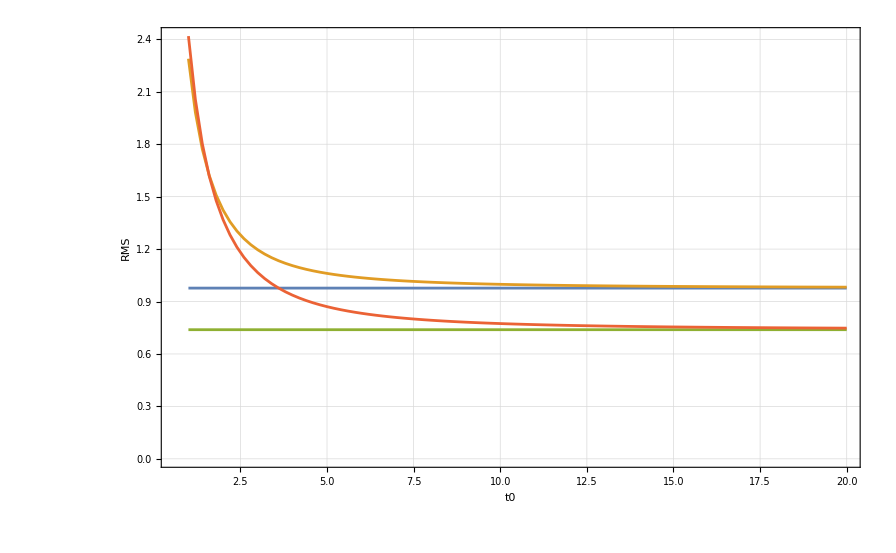

```mathematica
ListPlot[{UC0,TD0,UCπ,TDπ},GridLines->Automatic, Frame->True, FrameLabel->{"t0","RMS"}, Joined->True,PlotRange->All]
```

### 8b

```mathematica
Γ=1;
Δ0=1/2 Γ;
Ω0=1/2 Γ;
ω=ωCirc1DL;
dir=1;
t0=5/Γ;
```

```mathematica
(*plotting Re[W_TD} for ϕ=0 and ϕ=π*)
```

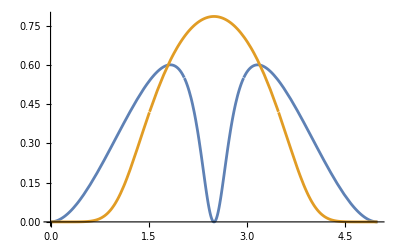

```mathematica
Plot[{Re[1/2 θDiagDotCircPath[Δ0,Ω0,Γ,0,ω,dir,t0,t]],Re[1/2 θDiagDotCircPath[Δ0,Ω0,Γ,π,ω,dir,t0,t]]},{t,0,t0}]
```

### 8c

```mathematica
(*plotting Im[W_TD} for ϕ=0 and ϕ=π*)
```

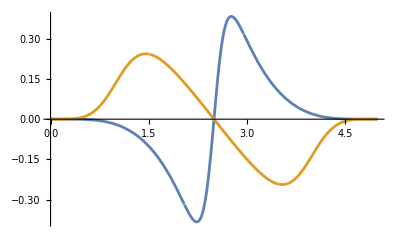

```mathematica
Plot[{Im[1/2 θDiagDotCircPath[Δ0,Ω0,Γ,0,ω,dir,t0,t]],Im[1/2 θDiagDotCircPath[Δ0,Ω0,Γ,π,ω,dir,t0,t]]},{t,0,t0}]
```

## μ validity check & holomorphic μ(t) (Fig. 9)

### Functions used for numerics

```mathematica
σx=({{0, 1}, {1, 0}});
σy=({{0, -ⅈ}, {ⅈ, 0}});
σz=({{1, 0}, {0, -1}});
```

```mathematica
(*choosen contour*)
ΔCircPath:=Function[{Δ0,φ,x},
Δ0 Sin[2 π x+φ]
];

ΩCircPath:=Function[{Δ0,Ω0,φ,x},
Ω0 + Δ0 Cos[2π x+φ]
];
(*time dependant parametrization of contour for single (ωCirc1) and double loop (ωCirc1DL)*)
ωCirc1:=#1(6(#3/#2)^5-15(#3/#2)^4+10(#3/#2)^3)&;
ωCirc1DL:=(ωCirc1[#1,#2,#3]UnitStep[#2-#3]+((#1)+ωCirc1[#1,#2,#3-#2])UnitStep[#3-#2])&;
```

```mathematica
(*constucting the holomorphic eigenvalue, works for a double loop*)
EigCircPath:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},

(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2)

];
```

```mathematica
(*constucting thederivative of the holomorphic eigenvalue, works for a double loop*)
EigDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])((2 ⅈ π Δ0 (Γ Cos[φ+2 π ω[dir,t0,t]]+2 ⅈ Ω0 Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,1][ω][dir,t0,t])/(√(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])))
];
```

```mathematica
(*constucting the holomorphic pseduo rotation angle into the adiabatic frame, works for a double loop*)
θDiagCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
-2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)+(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]
];
```

```mathematica
(*constucting the derivative of the pseduo rotation angle into the adiabatic frame.*)
θDiagDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(4 π Δ0 (2 Δ0+2 Ω0 Cos[φ+2 π ω[dir,t0,t]]+ⅈ Γ Sin[φ+2 π ω[dir,t0,t]]))/(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])Derivative[0,0,1][ω][dir,t0,t]
];
```

```mathematica
(*constucting the 2nd derivative of the pseduo rotation angle into the adiabatic frame.*)
θDiagDDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(4 π Δ0 (2 π (Γ^2+4 (Δ0-Ω0) (Δ0+Ω0)) (-ⅈ Γ Cos[φ+2 π ω[dir,t0,t]]+2 Ω0 Sin[φ+2 π ω[dir,t0,t]]) (Derivative[0,0,1][ω][dir,t0,t])^2+(4 Δ0 (-Γ^2+2 Δ0^2+4 Ω0^2)-2 Ω0 (Γ^2-4 (3 Δ0^2+Ω0^2)) Cos[φ+2 π ω[dir,t0,t]]+2 Δ0 (Γ^2+4 Ω0^2) Cos[2 (φ+2 π ω[dir,t0,t])]+ⅈ Γ (-Γ^2+4 (3 Δ0^2+Ω0^2)+16 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]) Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,2][ω][dir,t0,t]))/(Γ^2-4 (Δ0^2+Ω0^2)-8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]-4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])^2
];
```

```mathematica
(*finding the times when real part of the SATD pseudo rotation angle goes to 0*)
tb0sRetimes:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{tbtest,index},
tbtest=Table[{t,N[Re[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])/EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]},{t,0,t0,t0/99}];
index=Sort[Join[Flatten[Position[Differences[Sign[tbtest[[2;;,2]]]],2]+1],Flatten[Position[Differences[Sign[tbtest[[2;;,2]]]],-2]+1]]];
Map[t/.FindRoot[Re[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])/EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]==0,{t,tbtest[[#,1]]},Method->"AffineCovariantNewton"]&,index]]
];
```

```mathematica
(*determining how many times the SATD pseduo rotation angle crosses the branch cut for 1 loop*)
t0CriticalCheck:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,BrCutCrossTimes},
Module[{tbtest,index,tb0sReCheckt0,tb0sImt0,tb0sRefinalt0,tb0sImfinalt0},

tb0sReCheckt0=Select[Select[Chop[Map[{Re[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#])/EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#]],#}&,BrCutCrossTimes],10^-16], #[[1]]== 0&],0<#[[2]]< t0 &][[;;,2]];

tb0sImt0=Map[Im[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#])/EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#]]&,tb0sReCheckt0];
tb0sRefinalt0=Select[Map[{tb0sReCheckt0[[#]],tb0sImt0[[#]]}&,Range[1,Length[tb0sImt0]]],#[[2]]≥ 1|| #[[2]]≤ -1  &][[;;,1]];
tb0sImfinalt0=Select[Map[{tb0sReCheckt0[[#]],tb0sImt0[[#]]}&,Range[1,Length[tb0sImt0]]],#[[2]]≥ 1|| #[[2]]≤ -1  &][[;;,2]];

Length[tb0sImfinalt0]

]

];
```

```mathematica
(*checking if the times found from the function "tb0sRetimes" correspond to branch cut crossings*)
tb0sRefinalList:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,tb0sRe},
Module[{tb0sReCheck,tb0sIm,tb0sImfinal,tb0sRefinal},
tb0sReCheck=Select[Select[Chop[Map[{Re[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#])/(EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#])],#}&,tb0sRe],10^-4], Abs[#[[1]]]== 0&],0<#[[2]]< 2t0 &][[;;,2]];
tb0sIm=Map[Im[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#])/(EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#])]&,tb0sReCheck];
tb0sImfinal=Select[Map[{tb0sReCheck[[#]],tb0sIm[[#]]}&,Range[1,Length[tb0sIm]]],#[[2]]≥ 1|| #[[2]]≤ -1  &][[;;,2]];
tb0sRefinal=Sort[Select[Map[{tb0sReCheck[[#]],tb0sIm[[#]]}&,Range[1,Length[tb0sIm]]],#[[2]]≥ 1|| #[[2]]≤ -1  &][[;;,1]]]
]
];
```

```mathematica
(*determining the difference in the SATD psuedo rotation angle at the discontinuous points when the branch cut is crossed*)
FinalTimesPhases:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,tb0sRefinal},
Module[{α,β,PhaseCond,Time,FinalTime,FinalPhases},

α=Map[
Re[-ArcTan[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]])])/(EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]])])]]-Re[-ArcTan[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]]-10^-6)])/(EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]]-10^-6)])]]&,Range[1,Length[tb0sRefinal]]];
β=Map[N[Re[-ArcTan[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]]+10^-6)])/(EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]]+10^-6)])]]-Re[-ArcTan[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]])])/(EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]])])]]]&,Range[1,Length[tb0sRefinal]]];

PhaseCond=Map[If[Abs[ α[[#]]] >1,{α[[#]],tb0sRefinal[[#]]}, {β[[#]],tb0sRefinal[[#]]+10^-6}]&,Range[1,Length[tb0sRefinal]]];

Time=PhaseCond[[;;,2]];

FinalTime=Partition[Insert[Insert[Time,0,1],2t0,-1],2,1];

FinalPhases=Insert[-Map[Total[Map[N[PhaseCond[[;;,1]][[##]]]&,Range[1,#]]]&,Range[1,Length[Time]]],0,1];

{FinalTime,FinalPhases}
]
];
```

```mathematica
(*creating a list of times and phases which need to be applied to produce the holomorphic angle μ*)
μCircPathCorr:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,BrCutCrossTimes},
Module[{tb0sRe,tb0sReCheck,tb0sIm,tb0sImfinal,tb0sRefinal,t0Rediff,PartPhaseDiff,tb0sRePartFinal,PartPhaseDiffFinal,finaltimes,finalphases,index},
tb0sRefinal=tb0sRefinalList[Δ0,Ω0,Γ,φ,ω,dir,t0,BrCutCrossTimes];
If[Length[tb0sRefinal]==0,List[{{0,2t0}},{0}],
FinalTimesPhases[Δ0,Ω0,Γ,φ,ω,dir,t0,tb0sRefinal]
]
]
];
```

```mathematica
(*the holomorphic SATD pseudo roation angle with the correct phases applied at the correct times*)
μ:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t,ts,ph},
-ArcTan[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])/(EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])]+Total[Map[{ph[[#]]UnitStep[Boole[ts[[#,1]]≤ t<ts[[#,2]]]]}&,DeleteDuplicates[Flatten[Map[Position[ts,Flatten[Select[ts,#[[1]]≤ t<#[[2]]&][[#]]]]&,Range[1,Length[Select[ts,#[[1]]≤ t<#[[2]]&]]]],2]]],2]
];
```

### 9a

```mathematica
(*parameter set 1 - the set that can always be corrected for SATD to be valid*)
```

```mathematica
Γ=1;
Δ0=1/2 Γ;
Ω0=1/2 Γ;
φ=0;
ω=ωCirc1DL;
dir=1;
```

```mathematica
(*counting number of times branch cut is crosses for μ_nat (defined in paper as non-holomoprhic μ)*)
(*list given as {loop time, # branch cuts}; if # branch cuts Mod 2 != 0 then not a valid STA*)
```

```mathematica
t0Criticallist=Map[{#,t0Critical[Δ0,Ω0,Γ,φ,ω,dir,#]}&,Range[0.1,50,0.1]];
```

```mathematica
t0Criticallist={{0.1,2},{0.2,2},{0.30000000000000004,2},{0.4,2},{0.5,2},{0.6,2},{0.7000000000000001,2},{0.8,2},{0.9,2},{1.,2},{1.1,2},{1.2000000000000002,2},{1.3000000000000003,2},{1.4000000000000001,2},{1.5000000000000002,2},{1.6,2},{1.7000000000000002,2},{1.8000000000000003,2},{1.9000000000000001,2},{2.,2},{2.1,2},{2.2,2},{2.3000000000000003,2},{2.4000000000000004,2},{2.5000000000000004,2},{2.6,2},{2.7,2},{2.8000000000000003,2},{2.9000000000000004,2},{3.0000000000000004,2},{3.1,2},{3.2,2},{3.3000000000000003,2},{3.4000000000000004,2},{3.5000000000000004,2},{3.6,2},{3.7,2},{3.8000000000000003,2},{3.9000000000000004,2},{4.,2},{4.1,2},{4.2,2},{4.3,2},{4.3999999999999995,2},{4.5,2},{4.6,2},{4.7,2},{4.8,2},{4.9,0},{5.,0},{5.1,0},{5.2,0},{5.3,0},{5.4,0},{5.5,0},{5.6,0},{5.7,0},{5.8,0},{5.9,0},{6.,0},{6.1,0},{6.2,0},{6.3,0},{6.4,0},{6.5,0},{6.6,0},{6.7,0},{6.8,0},{6.9,0},{7.,0},{7.1,0},{7.2,0},{7.3,0},{7.4,0},{7.5,0},{7.6,0},{7.7,0},{7.8,0},{7.9,0},{8.,0},{8.1,0},{8.2,0},{8.3,0},{8.4,0},{8.5,0},{8.6,0},{8.7,0},{8.8,0},{8.9,0},{9.,0},{9.1,0},{9.2,0},{9.3,0},{9.4,0},{9.5,0},{9.6,0},{9.700000000000001,0},{9.8,0},{9.9,0},{10.,0},{10.1,0},{10.200000000000001,0},{10.3,0},{10.4,0},{10.5,0},{10.6,0},{10.700000000000001,0},{10.8,0},{10.9,0},{11.,0},{11.1,0},{11.200000000000001,0},{11.3,0},{11.4,0},{11.5,0},{11.6,0},{11.700000000000001,0},{11.8,0},{11.9,0},{12.,0},{12.1,0},{12.200000000000001,0},{12.3,0},{12.4,0},{12.5,0},{12.6,0},{12.700000000000001,0},{12.8,0},{12.9,0},{13.,0},{13.1,0},{13.200000000000001,0},{13.3,0},{13.4,0},{13.5,0},{13.6,0},{13.700000000000001,0},{13.8,0},{13.9,0},{14.,0},{14.1,0},{14.200000000000001,0},{14.3,0},{14.4,0},{14.5,0},{14.6,0},{14.700000000000001,0},{14.8,0},{14.9,0},{15.,0},{15.1,0},{15.200000000000001,0},{15.3,0},{15.4,0},{15.5,0},{15.6,0},{15.700000000000001,0},{15.8,0},{15.9,0},{16.,0},{16.1,0},{16.200000000000003,0},{16.3,0},{16.400000000000002,0},{16.500000000000004,0},{16.6,0},{16.700000000000003,0},{16.8,0},{16.900000000000002,0},{17.000000000000004,0},{17.1,0},{17.200000000000003,0},{17.3,0},{17.400000000000002,0},{17.500000000000004,0},{17.6,0},{17.700000000000003,0},{17.8,0},{17.900000000000002,0},{18.000000000000004,0},{18.1,0},{18.200000000000003,0},{18.3,0},{18.400000000000002,0},{18.500000000000004,0},{18.6,0},{18.700000000000003,0},{18.8,0},{18.900000000000002,0},{19.000000000000004,0},{19.1,0},{19.200000000000003,0},{19.300000000000004,0},{19.400000000000002,0},{19.500000000000004,0},{19.6,0},{19.700000000000003,0},{19.800000000000004,0},{19.900000000000002,0},{20.000000000000004,0},{20.1,0},{20.200000000000003,0},{20.300000000000004,0},{20.400000000000002,0},{20.500000000000004,0},{20.6,0},{20.700000000000003,0},{20.800000000000004,0},{20.900000000000002,0},{21.000000000000004,0},{21.1,0},{21.200000000000003,0},{21.300000000000004,0},{21.400000000000002,0},{21.500000000000004,0},{21.6,0},{21.700000000000003,0},{21.800000000000004,0},{21.900000000000002,0},{22.000000000000004,0},{22.1,0},{22.200000000000003,0},{22.300000000000004,0},{22.400000000000002,0},{22.500000000000004,0},{22.6,0},{22.700000000000003,0},{22.800000000000004,0},{22.900000000000002,0},{23.000000000000004,0},{23.1,0},{23.200000000000003,0},{23.300000000000004,0},{23.400000000000002,0},{23.500000000000004,0},{23.6,0},{23.700000000000003,0},{23.800000000000004,0},{23.900000000000002,0},{24.000000000000004,0},{24.1,0},{24.200000000000003,0},{24.300000000000004,0},{24.400000000000002,0},{24.500000000000004,0},{24.6,0},{24.700000000000003,0},{24.800000000000004,0},{24.900000000000002,0},{25.000000000000004,0},{25.1,0},{25.200000000000003,0},{25.300000000000004,0},{25.400000000000002,0},{25.500000000000004,0},{25.6,0},{25.700000000000003,0},{25.800000000000004,0},{25.900000000000002,0},{26.000000000000004,0},{26.1,0},{26.200000000000003,0},{26.300000000000004,0},{26.400000000000002,0},{26.500000000000004,0},{26.6,0},{26.700000000000003,0},{26.800000000000004,0},{26.900000000000002,0},{27.000000000000004,0},{27.1,0},{27.200000000000003,0},{27.300000000000004,0},{27.400000000000002,0},{27.500000000000004,0},{27.6,0},{27.700000000000003,0},{27.800000000000004,0},{27.900000000000002,0},{28.000000000000004,0},{28.1,0},{28.200000000000003,0},{28.300000000000004,0},{28.400000000000002,0},{28.500000000000004,0},{28.6,0},{28.700000000000003,0},{28.800000000000004,0},{28.900000000000002,0},{29.000000000000004,0},{29.1,0},{29.200000000000003,0},{29.300000000000004,0},{29.400000000000002,0},{29.500000000000004,0},{29.6,0},{29.700000000000003,0},{29.800000000000004,0},{29.900000000000002,0},{30.000000000000004,0},{30.1,0},{30.200000000000003,0},{30.300000000000004,0},{30.400000000000002,0},{30.500000000000004,0},{30.6,0},{30.700000000000003,0},{30.800000000000004,0},{30.900000000000002,0},{31.000000000000004,0},{31.1,0},{31.200000000000003,0},{31.300000000000004,0},{31.400000000000002,0},{31.500000000000004,0},{31.6,0},{31.700000000000003,0},{31.800000000000004,0},{31.900000000000002,0},{32.,0},{32.1,0},{32.2,0},{32.300000000000004,0},{32.400000000000006,0},{32.5,0},{32.6,0},{32.7,0},{32.800000000000004,0},{32.900000000000006,0},{33.,0},{33.1,0},{33.2,0},{33.300000000000004,0},{33.400000000000006,0},{33.5,0},{33.6,0},{33.7,0},{33.800000000000004,0},{33.900000000000006,0},{34.,0},{34.1,0},{34.2,0},{34.300000000000004,0},{34.400000000000006,0},{34.5,0},{34.6,0},{34.7,0},{34.800000000000004,0},{34.900000000000006,0},{35.,0},{35.1,0},{35.2,0},{35.300000000000004,0},{35.400000000000006,0},{35.5,0},{35.6,0},{35.7,0},{35.800000000000004,0},{35.900000000000006,0},{36.,0},{36.1,0},{36.2,0},{36.300000000000004,0},{36.400000000000006,0},{36.5,0},{36.6,0},{36.7,0},{36.800000000000004,0},{36.900000000000006,0},{37.,0},{37.1,0},{37.2,0},{37.300000000000004,0},{37.400000000000006,0},{37.5,0},{37.6,0},{37.7,0},{37.800000000000004,0},{37.900000000000006,0},{38.,0},{38.1,0},{38.2,0},{38.300000000000004,0},{38.400000000000006,0},{38.50000000000001,0},{38.6,0},{38.7,0},{38.800000000000004,0},{38.900000000000006,0},{39.00000000000001,0},{39.1,0},{39.2,0},{39.300000000000004,0},{39.400000000000006,0},{39.50000000000001,0},{39.6,0},{39.7,0},{39.800000000000004,0},{39.900000000000006,0},{40.00000000000001,0},{40.1,0},{40.2,0},{40.300000000000004,0},{40.400000000000006,0},{40.50000000000001,0},{40.6,0},{40.7,0},{40.800000000000004,0},{40.900000000000006,0},{41.00000000000001,0},{41.1,0},{41.2,0},{41.300000000000004,0},{41.400000000000006,0},{41.50000000000001,0},{41.6,0},{41.7,0},{41.800000000000004,0},{41.900000000000006,0},{42.00000000000001,0},{42.1,0},{42.2,0},{42.300000000000004,0},{42.400000000000006,0},{42.50000000000001,0},{42.6,0},{42.7,0},{42.800000000000004,0},{42.900000000000006,0},{43.00000000000001,0},{43.1,0},{43.2,0},{43.300000000000004,0},{43.400000000000006,0},{43.50000000000001,0},{43.6,0},{43.7,0},{43.800000000000004,0},{43.900000000000006,0},{44.00000000000001,0},{44.1,0},{44.2,0},{44.300000000000004,0},{44.400000000000006,0},{44.50000000000001,0},{44.6,0},{44.7,0},{44.800000000000004,0},{44.900000000000006,0},{45.00000000000001,0},{45.1,0},{45.2,0},{45.300000000000004,0},{45.400000000000006,0},{45.50000000000001,0},{45.6,0},{45.7,0},{45.800000000000004,0},{45.900000000000006,0},{46.00000000000001,0},{46.1,0},{46.2,0},{46.300000000000004,0},{46.400000000000006,0},{46.50000000000001,0},{46.6,0},{46.7,0},{46.800000000000004,0},{46.900000000000006,0},{47.00000000000001,0},{47.1,0},{47.2,0},{47.300000000000004,0},{47.400000000000006,0},{47.50000000000001,0},{47.6,0},{47.7,0},{47.800000000000004,0},{47.900000000000006,0},{48.00000000000001,0},{48.1,0},{48.2,0},{48.300000000000004,0},{48.400000000000006,0},{48.50000000000001,0},{48.6,0},{48.7,0},{48.800000000000004,0},{48.900000000000006,0},{49.00000000000001,0},{49.1,0},{49.2,0},{49.300000000000004,0},{49.400000000000006,0},{49.50000000000001,0},{49.6,0},{49.7,0},{49.800000000000004,0},{49.900000000000006,0},{50.,0}};
```

```mathematica
Γ=1;
Δ0=1/2 Γ;
Ω0=1/6 Γ;
φ=-π/8;
ω=ωCirc1DL;
dir=1;
```

```mathematica
(*list given as {loop time, # branch cuts}; if # branch cuts Mod 2 != 0 then not a valid STA*)
```

```mathematica
t0Criticallist2=Map[{#,t0Critical[Δ0,Ω0,Γ,φ,ω,dir,#]}&,Range[0.1,50,0.1]];
```

```mathematica
t0Criticallist2={{0.1,3},{0.2,3},{0.30000000000000004,3},{0.4,3},{0.5,3},{0.6,3},{0.7000000000000001,3},{0.8,3},{0.9,3},{1.,3},{1.1,3},{1.2000000000000002,3},{1.3000000000000003,3},{1.4000000000000001,3},{1.5000000000000002,3},{1.6,3},{1.7000000000000002,3},{1.8000000000000003,3},{1.9000000000000001,3},{2.,3},{2.1,3},{2.2,3},{2.3000000000000003,3},{2.4000000000000004,3},{2.5000000000000004,3},{2.6,3},{2.7,3},{2.8000000000000003,3},{2.9000000000000004,3},{3.0000000000000004,3},{3.1,3},{3.2,3},{3.3000000000000003,3},{3.4000000000000004,3},{3.5000000000000004,3},{3.6,3},{3.7,3},{3.8000000000000003,3},{3.9000000000000004,3},{4.,3},{4.1,3},{4.2,3},{4.3,3},{4.3999999999999995,3},{4.5,3},{4.6,3},{4.7,3},{4.8,2},{4.9,2},{5.,2},{5.1,2},{5.2,2},{5.3,2},{5.4,2},{5.5,1},{5.6,1},{5.7,1},{5.8,1},{5.9,1},{6.,1},{6.1,1},{6.2,1},{6.3,1},{6.4,1},{6.5,1},{6.6,1},{6.7,1},{6.8,1},{6.9,1},{7.,1},{7.1,1},{7.2,1},{7.3,1},{7.4,1},{7.5,1},{7.6,1},{7.7,1},{7.8,1},{7.9,1},{8.,1},{8.1,1},{8.2,1},{8.3,1},{8.4,1},{8.5,1},{8.6,1},{8.7,1},{8.8,1},{8.9,1},{9.,1},{9.1,1},{9.2,1},{9.3,1},{9.4,1},{9.5,1},{9.6,1},{9.700000000000001,1},{9.8,1},{9.9,1},{10.,1},{10.1,1},{10.200000000000001,1},{10.3,1},{10.4,1},{10.5,1},{10.6,1},{10.700000000000001,1},{10.8,1},{10.9,1},{11.,1},{11.1,1},{11.200000000000001,1},{11.3,1},{11.4,1},{11.5,1},{11.6,1},{11.700000000000001,1},{11.8,1},{11.9,1},{12.,1},{12.1,1},{12.200000000000001,1},{12.3,1},{12.4,1},{12.5,1},{12.6,1},{12.700000000000001,1},{12.8,1},{12.9,1},{13.,1},{13.1,1},{13.200000000000001,1},{13.3,1},{13.4,1},{13.5,1},{13.6,1},{13.700000000000001,1},{13.8,1},{13.9,1},{14.,1},{14.1,1},{14.200000000000001,1},{14.3,1},{14.4,1},{14.5,1},{14.6,1},{14.700000000000001,1},{14.8,1},{14.9,1},{15.,1},{15.1,1},{15.200000000000001,1},{15.3,1},{15.4,1},{15.5,1},{15.6,1},{15.700000000000001,1},{15.8,1},{15.9,1},{16.,1},{16.1,1},{16.200000000000003,1},{16.3,1},{16.400000000000002,1},{16.500000000000004,1},{16.6,1},{16.700000000000003,1},{16.8,1},{16.900000000000002,1},{17.000000000000004,1},{17.1,1},{17.200000000000003,1},{17.3,1},{17.400000000000002,1},{17.500000000000004,1},{17.6,1},{17.700000000000003,1},{17.8,1},{17.900000000000002,1},{18.000000000000004,1},{18.1,1},{18.200000000000003,1},{18.3,1},{18.400000000000002,1},{18.500000000000004,1},{18.6,1},{18.700000000000003,1},{18.8,0},{18.900000000000002,0},{19.000000000000004,0},{19.1,0},{19.200000000000003,0},{19.300000000000004,0},{19.400000000000002,0},{19.500000000000004,0},{19.6,0},{19.700000000000003,0},{19.800000000000004,0},{19.900000000000002,0},{20.000000000000004,0},{20.1,0},{20.200000000000003,0},{20.300000000000004,0},{20.400000000000002,0},{20.500000000000004,0},{20.6,0},{20.700000000000003,0},{20.800000000000004,0},{20.900000000000002,0},{21.000000000000004,0},{21.1,0},{21.200000000000003,0},{21.300000000000004,0},{21.400000000000002,0},{21.500000000000004,0},{21.6,0},{21.700000000000003,0},{21.800000000000004,0},{21.900000000000002,0},{22.000000000000004,0},{22.1,0},{22.200000000000003,0},{22.300000000000004,0},{22.400000000000002,0},{22.500000000000004,0},{22.6,0},{22.700000000000003,0},{22.800000000000004,0},{22.900000000000002,0},{23.000000000000004,0},{23.1,0},{23.200000000000003,0},{23.300000000000004,0},{23.400000000000002,0},{23.500000000000004,0},{23.6,0},{23.700000000000003,0},{23.800000000000004,0},{23.900000000000002,0},{24.000000000000004,0},{24.1,0},{24.200000000000003,0},{24.300000000000004,0},{24.400000000000002,0},{24.500000000000004,0},{24.6,0},{24.700000000000003,0},{24.800000000000004,0},{24.900000000000002,0},{25.000000000000004,0},{25.1,0},{25.200000000000003,0},{25.300000000000004,0},{25.400000000000002,0},{25.500000000000004,0},{25.6,0},{25.700000000000003,0},{25.800000000000004,0},{25.900000000000002,0},{26.000000000000004,0},{26.1,0},{26.200000000000003,0},{26.300000000000004,0},{26.400000000000002,0},{26.500000000000004,0},{26.6,0},{26.700000000000003,0},{26.800000000000004,0},{26.900000000000002,0},{27.000000000000004,0},{27.1,0},{27.200000000000003,0},{27.300000000000004,0},{27.400000000000002,0},{27.500000000000004,0},{27.6,0},{27.700000000000003,0},{27.800000000000004,0},{27.900000000000002,0},{28.000000000000004,0},{28.1,0},{28.200000000000003,0},{28.300000000000004,0},{28.400000000000002,0},{28.500000000000004,0},{28.6,0},{28.700000000000003,0},{28.800000000000004,0},{28.900000000000002,0},{29.000000000000004,0},{29.1,0},{29.200000000000003,0},{29.300000000000004,0},{29.400000000000002,0},{29.500000000000004,0},{29.6,0},{29.700000000000003,0},{29.800000000000004,0},{29.900000000000002,0},{30.000000000000004,0},{30.1,0},{30.200000000000003,0},{30.300000000000004,0},{30.400000000000002,0},{30.500000000000004,0},{30.6,0},{30.700000000000003,0},{30.800000000000004,0},{30.900000000000002,0},{31.000000000000004,0},{31.1,0},{31.200000000000003,0},{31.300000000000004,0},{31.400000000000002,0},{31.500000000000004,0},{31.6,0},{31.700000000000003,0},{31.800000000000004,0},{31.900000000000002,0},{32.,0},{32.1,0},{32.2,0},{32.300000000000004,0},{32.400000000000006,0},{32.5,0},{32.6,0},{32.7,0},{32.800000000000004,0},{32.900000000000006,0},{33.,0},{33.1,0},{33.2,0},{33.300000000000004,0},{33.400000000000006,0},{33.5,0},{33.6,0},{33.7,0},{33.800000000000004,0},{33.900000000000006,0},{34.,0},{34.1,0},{34.2,0},{34.300000000000004,0},{34.400000000000006,0},{34.5,0},{34.6,0},{34.7,0},{34.800000000000004,0},{34.900000000000006,0},{35.,0},{35.1,0},{35.2,0},{35.300000000000004,0},{35.400000000000006,0},{35.5,0},{35.6,0},{35.7,0},{35.800000000000004,0},{35.900000000000006,0},{36.,0},{36.1,0},{36.2,0},{36.300000000000004,0},{36.400000000000006,0},{36.5,0},{36.6,0},{36.7,0},{36.800000000000004,0},{36.900000000000006,0},{37.,0},{37.1,0},{37.2,0},{37.300000000000004,0},{37.400000000000006,0},{37.5,0},{37.6,0},{37.7,0},{37.800000000000004,0},{37.900000000000006,0},{38.,0},{38.1,0},{38.2,0},{38.300000000000004,0},{38.400000000000006,0},{38.50000000000001,0},{38.6,0},{38.7,0},{38.800000000000004,0},{38.900000000000006,0},{39.00000000000001,0},{39.1,0},{39.2,0},{39.300000000000004,0},{39.400000000000006,0},{39.50000000000001,0},{39.6,0},{39.7,0},{39.800000000000004,0},{39.900000000000006,0},{40.00000000000001,0},{40.1,0},{40.2,0},{40.300000000000004,0},{40.400000000000006,0},{40.50000000000001,0},{40.6,0},{40.7,0},{40.800000000000004,0},{40.900000000000006,0},{41.00000000000001,0},{41.1,0},{41.2,0},{41.300000000000004,0},{41.400000000000006,0},{41.50000000000001,0},{41.6,0},{41.7,0},{41.800000000000004,0},{41.900000000000006,0},{42.00000000000001,0},{42.1,0},{42.2,0},{42.300000000000004,0},{42.400000000000006,0},{42.50000000000001,0},{42.6,0},{42.7,0},{42.800000000000004,0},{42.900000000000006,0},{43.00000000000001,0},{43.1,0},{43.2,0},{43.300000000000004,0},{43.400000000000006,0},{43.50000000000001,0},{43.6,0},{43.7,0},{43.800000000000004,0},{43.900000000000006,0},{44.00000000000001,0},{44.1,0},{44.2,0},{44.300000000000004,0},{44.400000000000006,0},{44.50000000000001,0},{44.6,0},{44.7,0},{44.800000000000004,0},{44.900000000000006,0},{45.00000000000001,0},{45.1,0},{45.2,0},{45.300000000000004,0},{45.400000000000006,0},{45.50000000000001,0},{45.6,0},{45.7,0},{45.800000000000004,0},{45.900000000000006,0},{46.00000000000001,0},{46.1,0},{46.2,0},{46.300000000000004,0},{46.400000000000006,0},{46.50000000000001,0},{46.6,0},{46.7,0},{46.800000000000004,0},{46.900000000000006,0},{47.00000000000001,0},{47.1,0},{47.2,0},{47.300000000000004,0},{47.400000000000006,0},{47.50000000000001,0},{47.6,0},{47.7,0},{47.800000000000004,0},{47.900000000000006,0},{48.00000000000001,0},{48.1,0},{48.2,0},{48.300000000000004,0},{48.400000000000006,0},{48.50000000000001,0},{48.6,0},{48.7,0},{48.800000000000004,0},{48.900000000000006,0},{49.00000000000001,0},{49.1,0},{49.2,0},{49.300000000000004,0},{49.400000000000006,0},{49.50000000000001,0},{49.6,0},{49.7,0},{49.800000000000004,0},{49.900000000000006,0},{50.,0}};
```

```mathematica
(*taking mod of 2nd number in each element*)
```

```mathematica
t0islands1=Map[{#[[1]],Mod[Re[#[[2]]],2]}&,t0Criticallist];
t0islands2=Map[{#[[1]],Mod[Re[#[[2]]],2]}&,t0Criticallist2];
```

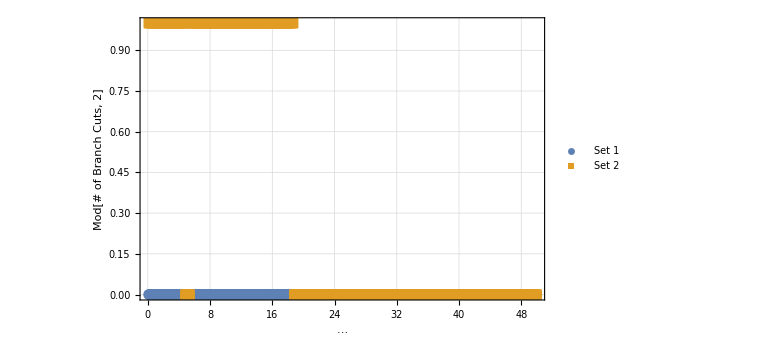

```mathematica
ListPlot[{t0islands1,t0islands2}, GridLines->Automatic, Frame->True,GridLinesStyle-> Thin,FrameLabel->{Style["(*GraphicsBox[{Thickness[0.023441162681669007`], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGIlIGYCYvldC/al6sk7GGitFL7QourQG9Htz/hB1sHn
BLvt7KtaDhJNMlMMLn+3R+frg9SraDk88HuZ8Hf+bzi/D6R/A4sDjL/Na4PF
nJ8sDnMWKe/881wTzk9NAwI2BN8YBC5LwPlgcwTE4ea1KrCrnpkiBrcPxoe5
B51vAjZQFGJP2h/7qvs/bhl7i0LNY3OA8c+AQA8nnH+ge1+TyWMeOP8giL9Y
CM4XqZxUcpZFxAFmPowPs999zdHlDDOE4HyYeTA+WN9mHocdwVYR/9XF4fy1
Qjp86fck4HzpeXGapw004fyaTxsCsn9pws2Dha/6J5WXszoF4Hywe5aIwvkz
ZgKBpQyc/2Xfx63pZbIO56+GvdG/reEQ8PbyxxmKcvD4R08PAE9E2P4=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJLIGYC4h0OTY+O31B3EKmcVHKWRcYBxpfftWBfqp+M
w6MI8e0XD6g7GBgDQbGMwya9vMWMcxD8jVC+PpTfwHK037AcIT9jAn+VWba6
Q8jbyx9nOGLyZZe/8NCLV3dQ/6TycpamjINoj9crFhN1h/Q0EJCG8LeoORzs
3tdkwizpcOFq2Bv92aoOZ0BgjajDjJlAYKkC53fbeO5Ka1KG8/fm17ydWars
sFZIhy/9nhicX3P/xy3j1+IOe9D4qOolHNzXHF3O0KHs8MA13nFWoaSD38WJ
Mf+SVR2eJC68ZqKv4uBzgt129lR1OD8+JEh9AacGnO+xv1bWwh2TP6W9Nery
HASfAQQeqDiIT73CmaGE4M9ZpLzzz3J1OP8pyJx+VThfZl6c5ukCNYfzoHCJ
1nBIANnfqeYgDRLfgOBPBtm3B8EH2/scwQfTnprQ8FRz+A8C9ZoOW8x/HEp5
pQrng+V3IvgbVJ80z9NVdVgPonM1If76o+KwGaRvlYYDC2eXfDKfCty9K769
rDhzQRHO548NuG8UjuCDzZXH5L8q3ir6OxvBh4Wn84RmoTQvBB8cb/sQ/NLD
21xn3lWG86tB8eyt5LAj2Cri/3FpiH4pJYcY1QiZczJSkPjmUHI4AEpviyXh
fFj6g/HByfOYGCRdXFRymAkOFxFIuKqrwPmQ+FKD82H5qz+i259xg7QDev4D
AHbzfLc=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJ5IGYC4tQ0IFim6xD09vLHGYyiDjA+iEo7Ju4QcEu6
JtFI18HEGAguSzqkxN5xY7bQgfMz8j+0nizRhvPBtLC2w5d9H7emT5OA8zU+
qbyc1SkO58eoRsicqxFzYOHskk/Og+o3FnU4fthpbaadDpy/VvVJ87xeBF9m
Xpzm6Qs6DiKVk0rOpog6uO+vlbVg13V44BrvOOuiqINoj9crFhFdiH0vRR3+
g4A8bv5fNP6b4q2iv7V1HRhAwAHBh4UPjN8f0e3PWCAMt/8zyL9hAg4tvP7r
pyzVdtjutcFiTiWXg8TUK5wZSdoO/k88L5kGc8L5YO985sDJ3wbWz+HwIEJ8
+8UGbYi7/7M7yCx/4aE3H8E/vmtHL9sFBB8Wf2dAgIffAT1+AcZ8zHk=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJLIGYC4hgFx4/JOaYOIpWTSs6yyDjA+PK7FuxL9ZNx
KFjTfTsjwdTBwBgIimUcIsS3X2Tww+TrQ/mOTY+Oz7BGyPucYLedbWrqEPL2
8scZjpj8CcElKtP1TR3UP6m8nKUp48DlplrKJGXqkJ4GAtIQ/i0Th4Pd+5pM
mCUdXmRpf5vua+JwBgTWiELoOcZwfo/XKxYTRwRf9UnzvLNWxg5rhXT40u+J
wfk193/cMn4t7qCCxkdVL+Hgf3FizD9nY4cHrvGOswolHVa88ND7b2ji8CRx
4TUTfRUHNZB6L1M430BrpfCFFgR/yf19fHMWY/KntLdGXZ6D4DOAwAMViPsn
Ivh+IPuDEfxPGwKyZ7mbwPk8/uunpO4wcTh/NeyNfrQGxP4jJg7S8+I0T29A
8CeD7NuD4Hvsr5W1eI7gJ4QEqS/w1ISGp4nDfxCo13S4JV2TaFSK4IPlYxD8
G0KfHM+LmTisBwVcrqbD6cNOazP/GTtsNv9xKGWVhkMjy9F+w3ZjuHt5Qe7N
MILz7UHpRRvBB5vLj8l/VbxV9Hc2gg8Lz9sg96ki+I9BdDyCXwLUdjrPGM73
BqW/pUYOO4KtIv4fl3awrYxYYdpr5BCjGiFzTkYKEt/NRg4HQOltsSScD0t/
MD44eR4Tc6j/bVVw7oWRw0wQ2CkCic/JxnA+OL6Om8D5sPzVH9Htz7hB2gE9
/wEAO+WEmw==
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAwBWIQ3RdcojI93tJBpHJSyVkWGQcYP+Tt5Y8zHGUcFt/f
xzcn2NLBwBgIimUcur1esZg4IvjeJ9htZ6si+OJTr3BmKFk6yO9asC/VT8YB
JGwsbOmwXkiHL71O2sHv4sSYf4ctHHYEW0X8Vxd3uC70yfG8m4XDGRBYI+qw
4oWH3v+H5nD+iyztb9P3IvgH25aHn5pk7vDANd5x1kUEnwEEHMThfPVPKi9n
dUo4fNoQkD1ru7mD+5qjyxl+SDpovOXdZ3DT3CE9DQSkHUq2iv4+vc7CodPG
c1eakhJUvQXE3cFKDraVEStMz1o4rPz2suLMAQQfHF4mynC+DygcTFUc/n4r
fTCn0MJhSntr1GUZVYeNenmLGe+Yw/kmIHMPm8H5EqDwCjKDuG+FIpzPHxtw
36gcwQ/nFGs3jleEuDfODOIeB0VIeBYj+OD460fwwfonmTl8WLRe4WwEVP88
M4e1oPhYp+iQEnvHjfmFmUMEyPz1yhD3xpg7/Hz7+oDlYhVIeF5C8E8edlqb
+Q7Bh8Q31L9zEPyZIHBTGc6vvP/jlrG1ssMW8x+HUn5B469QCR7f1SD514oO
B2plLdJLzCHpI10ezoekJ3mHGAXHj8k8sPiUgppn5tCuwK56xkQK7h+I+ZJw
/pd9H7emT5OA8/siuv0ZC8QcwMnAzRzi3p0i8PQB44Pj86MFnA/LH/0g/Ruk
HdDzDwDQs2oE
"], {{25.2781, 12.739099999999999`}, {25.2781, 12.917200000000001`}, {25.134399999999996`, 13.131299999999996`}, {24.873399999999997`, 13.131299999999996`}, {24.598399999999998`, 13.131299999999996`}, {24.2891, 12.8688}, {24.2891, 12.5594}, {24.2891, 12.260899999999998`}, {24.5391, 12.165599999999998`}, {24.6828, 12.165599999999998`}, {25.004699999999996`, 12.165599999999998`}, {25.2781, 12.4766}, {25.2781, 12.739099999999999`}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxdlQ1MW1UUx8tYhiw6HFtbPsrKa0twbG6TD53vvZb/08nULM6ACVU3EaV0
6hQUFocBl4iOMJjowjbARgfMsCU4NEoEDBXFpdMVWAMhZlPLDLoRQcUQAtm0
9t7bd1/0Ji/NLzfn63/OuRWeKct3Ret0uqjwVxH+VoQ/szL/rH9OwfqqY5Uj
K01Q+bG58fkWxQTfRvHYxWsKtmWFT4UJH8ibJ9p+0vjQDbF89JLG/ZeP/O0a
U2AeOOV1PRKx9ynoid+8xv16MpoXVxW1nFaQSu7PGVHXVfhd5n4FfnK69Zgu
bp/M3qoxtTdrTP3HKGglp19jHTkwcn4yzWkarU5AoKwoZjRRrS+J+0v/yzbT
Vp+EF2KXT7klBW+mxqT5J0wIkXNIwf3v1MaXigJn6+TPBTqPhfNn9yx9XbLa
htnbvNtaH1bQXPfWE+OmNKbPJDjfurun2VWu8ePGzwO6DcCuCzH293Js+PD6
g1tCX+Wy+vwW1BA9+3Jxp2Be2G+wYVfg3T3/FORy+1+IPmUOzkcLKm0ni+yc
aX5jMvPnsSJ9jiQo48rGlO5QtJXdN8lMr6dtGDocbkC8zO2pXaPE+cualO3u
bI0LSf6/i/B0WPtv+iL5fSoyf1NWyFXOMzk1Io9nPD4Ruy9fjMQVOMftfTSY
+arGhbGGuqwiAZW9+hsXnxJxdnHmoB8C81+h8Z7U8IA2atxE6m8S4SoNnzwB
NxcPTHnaRZBxzBqP3I+JqAouXc6SrGghcxMrYXnut6F7O204HfSu8dRqTO+/
1biL9OeqhLvlwfwTisY7yHwcsXJW66X+hiW4ST4GCy4M3/fRc+ck/NnRkzri
FNi+OCUcJPk0pODjLS91RpkkDDV438juTGR2qySsI/NakoCtGWfXXZoW0Vcg
OkPpBs53kPmd0XNm86/n9mw/1vP+qazGV1mtP5/se5Se5eOR+H7R+tolLHjn
e92Lelx7ftPiyUGJvQ/txsjcRu5PJLA+x8nsN2hi+VXKGCyrnms9LsA2Xfv+
yGsy26+BsB4rzzfd5ZPZfs1aULL3h7zo7XY4yTz0WNl9nZ3rT+f/DzvvzwJd
eAdnFldjGm91LmzUv5Xzzu7zXbolC2c2LxqzflnYXP3q4O+Bj/TT64CH6LNs
5szeDzNuyUs7sKLNwftL51Fx4G1nw+6o2xPwfXJ1cWaOA3kkvtOIb8j+WRyY
PfxiQ2aygbPaX5XV/tJ+7nDw/tH9eUVjJ9nPUY3tZB9/dGDqgSKlLaBn79FS
xH+9ke1HTy7fR/ou9Ub0OSOAjEdWBv67DwGNuxuu7NPFKZxpfjaF662yqrfK
9fJDA6UdAkj40HUgSPJbu4G93z6gjuiZnRypA2ik+iWx+J+A1fNyImd1/lSm
epcbUDw8vsl1FVwP+l5nKJypHn0aq/9/tB9fJOP//4//AvvkPH0=
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGBQBmIQvfNW19/U6S4O6WkgIOUA48vvWrAvdZ2Ug96EBT8M
+1wcau7/uGX8WsrB4trRXJMOBN+h6dHxGc0I/ooXHnr/G10c/oPAfSmHtuXh
p4xKXBzuu8Y7ziqUcnjDu89gppCLg0jlpJKzKWIOM0Gg0dnhDAisEXU4oWk1
6bQ7gl//26rg3AcnOP93TO7Rf4ecHEyMgeCyOJw/HWROpDScDzafRQbO/7Lv
49Z0M1mHi/nx7OduOkHco6jgoP6ked5ZLWc4f6Ne3mLGEAQf7L/dzg7lh7e5
ztRVcGBZPMmKkdXFQfnao2CGOQoOtSD3VbhA3OejCA+PtUI6fOnrlOB8sLyM
MpzfANKnoQLxv6eLw5T21qjLMqoQdU+c4fwp39jiZ7gg+Pqg+Ihzgui7qQTn
w/wH47cqsKueMZGA+HcnVP1OEbh5MD44fkRc4HyU9HBM0gE9fQAAZ8MLqw==

"], {{40.6703, 9.556249999999999}, {40.6703, 8.304689999999999}, {38.762499999999996`, 8.304689999999999}, {38.262499999999996`, 8.304689999999999}, {37.7609, 8.304689999999999}, {38.2734, 10.1391}, {39.406299999999995`, 10.318799999999998`}, {39.787499999999994`, 10.318799999999998`}, {40.3125, 10.318799999999998`}, {40.6703, 10.007799999999998`}, {40.6703, 9.556249999999999}}}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{63.99483437110834, 24.508064757160646`},PlotRange->{{0., 42.660000000000004`}, {0., 16.34}}])",15],Style["Mod[# of Branch Cuts, 2]", 15]}, ImageSize->Large, PlotMarkers->Automatic, PlotLegends->Placed[{"Set 1", "Set 2"},Right]]
```

### 9b

```mathematica
(*plotting μ vs μ_nat for given paramter sets*)
(*in b) and c) we use parameter γ_circ2 with Γt0=2*)
```

```mathematica
Γ=1;
Δ0=1/2 Γ;
Ω0=1/6 Γ;
φ=-π/8;
ω=ωCirc1DL;
dir=1;
t0=2/Γ;
```

```mathematica
BrCutCrossTimes=tb0sRetimes[Δ0,Ω0,Γ,φ,ω,dir,t0];
{times,phases}=μCircPathCorr[Δ0,Ω0,Γ,φ,ω,dir,t0,BrCutCrossTimes];
```

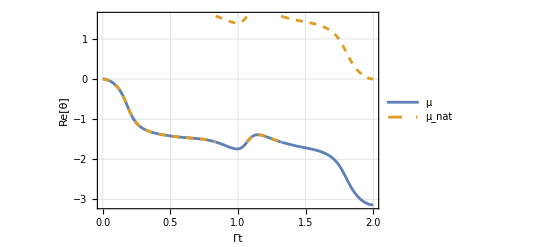

```mathematica
Plot[{Re[μ[Δ0,Ω0,Γ,φ,ω,dir,t0,t,times,phases]],Re[-ArcTan[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])/EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]},{t,0,t0},PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{Style["Γt",15],Style["Re[θ]", 15]},PlotLegends->Placed[{"μ", "μ_nat"},{Right, Center}],PlotStyle->{Automatic,Dashing[Small]}]
```

### 9c

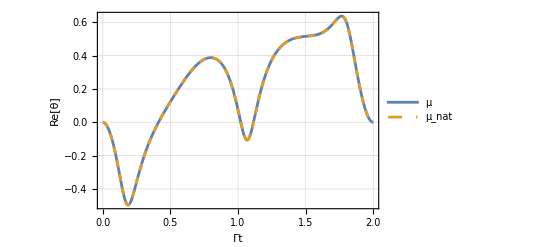

```mathematica
Plot[{Im[μ[Δ0,Ω0,Γ,φ,ω,dir,t0,t,times,phases]],Im[-ArcTan[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])/EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]},{t,0,t0},PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{Style["Γt",15],Style["Re[θ]", 15]},PlotLegends->Placed[{"μ", "μ_nat"},{Right, Center}],PlotStyle->{Automatic,Dashing[Small]}]
```

### 9d

```mathematica
(*plotting μ vs μ_nat for given paramter sets*)
(*in d) we use γ_circ1 with Γt0=5*)
```

```mathematica
Γ=1;
Δ0=1/2 Γ;
Ω0=1/2 Γ;
φ=0;
dir=1;
ω=ωCirc1DL;
dir=1;
t0=5/Γ;
```

```mathematica
BrCutCrossTimes=tb0sRetimes[Δ0,Ω0,Γ,φ,ω,dir,t0];
{times,phases}=μCircPathCorr[Δ0,Ω0,Γ,φ,ω,dir,t0,BrCutCrossTimes];
```

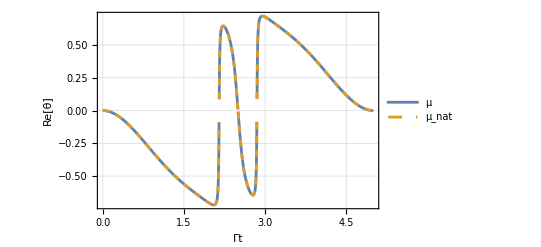

```mathematica
Plot[{Re[μ[Δ0,Ω0,Γ,φ,ω,dir,t0,t,times,phases]],Re[-ArcTan[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])/EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]},{t,0,t0},PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{Style["Γt",15],Style["Re[θ]", 15]},PlotLegends->Placed[{"μ", "μ_nat"},{Right, Center}],PlotStyle->{Automatic,Dashing[Small]}]
```

## UC & SATD RMS for ϕ=(0,π) (Fig. 10)

### Functions used for numerics

```mathematica
σx=({{0, 1}, {1, 0}});
σy=({{0, -ⅈ}, {ⅈ, 0}});
σz=({{1, 0}, {0, -1}});
```

```mathematica
(*choosen contour*)
ΔCircPath:=Function[{Δ0,φ,x},
Δ0 Sin[2 π x+φ]
];

ΩCircPath:=Function[{Δ0,Ω0,φ,x},
Ω0 + Δ0 Cos[2π x+φ]
];
(*time dependant parametrization of contour for single (ωCirc1) and double loop (ωCirc1DL)*)
ωCirc1:=#1(6(#3/#2)^5-15(#3/#2)^4+10(#3/#2)^3)&;
ωCirc1DL:=(ωCirc1[#1,#2,#3]UnitStep[#2-#3]+((#1)+ωCirc1[#1,#2,#3-#2])UnitStep[#3-#2])&;
```

```mathematica
(*constucting the holomorphic eigenvalue, works for a double loop*)
EigCircPath:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},

(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2)

];
```

```mathematica
(*constucting thederivative of the holomorphic eigenvalue, works for a double loop*)
EigDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])((2 ⅈ π Δ0 (Γ Cos[φ+2 π ω[dir,t0,t]]+2 ⅈ Ω0 Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,1][ω][dir,t0,t])/(√(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])))
];
```

```mathematica
(*constucting the holomorphic pseduo rotation angle into the adiabatic frame, works for a double loop*)
θDiagCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
-2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)+(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]
];
```

```mathematica
(*constucting the derivative of the pseduo rotation angle into the adiabatic frame.*)
θDiagDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(4 π Δ0 (2 Δ0+2 Ω0 Cos[φ+2 π ω[dir,t0,t]]+ⅈ Γ Sin[φ+2 π ω[dir,t0,t]]))/(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])Derivative[0,0,1][ω][dir,t0,t]
];
```

```mathematica
(*constucting the 2nd derivative of the pseduo rotation angle into the adiabatic frame.*)
θDiagDDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(4 π Δ0 (2 π (Γ^2+4 (Δ0-Ω0) (Δ0+Ω0)) (-ⅈ Γ Cos[φ+2 π ω[dir,t0,t]]+2 Ω0 Sin[φ+2 π ω[dir,t0,t]]) (Derivative[0,0,1][ω][dir,t0,t])^2+(4 Δ0 (-Γ^2+2 Δ0^2+4 Ω0^2)-2 Ω0 (Γ^2-4 (3 Δ0^2+Ω0^2)) Cos[φ+2 π ω[dir,t0,t]]+2 Δ0 (Γ^2+4 Ω0^2) Cos[2 (φ+2 π ω[dir,t0,t])]+ⅈ Γ (-Γ^2+4 (3 Δ0^2+Ω0^2)+16 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]) Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,2][ω][dir,t0,t]))/(Γ^2-4 (Δ0^2+Ω0^2)-8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]-4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])^2
];
```

```mathematica
(*SATD correction fields in the lab frame using the holomorphic functions*)
gxCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
Cos[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]/2((-EigDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]+ EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t] θDiagDDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])/(EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]^2+θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]^2))
];
gzCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
Sin[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]/2(-((-EigDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]+ EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t] θDiagDDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])/(EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]^2+θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]^2)))
];
```

### 10a

```mathematica
(*checking RMS values for SATD for ϕ=0*)
```

```mathematica
(*getting  range of loop times to check*)
```

```mathematica
t0list=Range[1,20,0.2];
```

```mathematica
(*data for UC0 and UCπ stored in Fig 8a*)
```

```mathematica
SATD0=(*find the RMS values for SATD ϕ=0*)Map[{#,Sqrt[1/# NIntegrate[Abs[ΩCircPath[Δ0,Ω0,φ,ω[dir,#,t]]+gxCircPath[Δ0,Ω0,Γ,φ,ω,dir,#,t]]^2+Abs[ΔCircPath[Δ0,φ,ω[dir,#,t]]+ⅈ/2 Γ-gzCircPath[Δ0,Ω0,Γ,φ,ω,dir,#,t]]^2,{t,0,#},Method->{"LocalAdaptive","SymbolicProcessing"-> 0}, PrecisionGoal->12, AccuracyGoal->12]]}&,t0list];
```

```mathematica
SATD0={{1.,10.985964191858589},{1.2,8.431019728297127},{1.4,6.759215144318348},{1.6,5.598493232688921},{1.8,4.756722071768594},{2.,4.125634327184268},{2.2,3.640010624055242},{2.4000000000000004,3.2584336328327685},{2.6,2.953450063695832},{2.8,2.706205963314793},{3.,2.5033620163317516},{3.2,2.3352393374564184},{3.4000000000000004,2.1946619561186917},{3.6,2.076210198381316},{3.8000000000000003,1.9757251066612067},{4.,1.8899710410430606},{4.2,1.816400722575681},{4.4,1.7529882766796923},{4.6,1.698108439988584},{4.800000000000001,1.6504477624447556},{5.,1.6089384186369762},{5.2,1.5727082932237948},{5.4,1.5410429941615003},{5.6000000000000005,1.5133567724101333},{5.800000000000001,1.4891702306068044},{6.,1.4680933380430332},{6.2,1.4498127341869627},{6.4,1.4340826663516644},{6.6000000000000005,1.4207192220242164},{6.800000000000001,1.409597832553956},{7.,1.4006544021130944},{7.2,1.3938909437459943},{7.4,1.3893874395510406},{7.6000000000000005,1.387323085808426},{7.800000000000001,1.3880127576687773},{8.,1.3919697997210738},{8.2,1.400017345167591},{8.4,1.4134955381317684},{8.600000000000001,1.4346745448686897},{8.8,1.4676572743624896},{9.,1.5206193041241682},{9.200000000000001,1.6124920971108228},{9.4,1.79985025543369},{9.6,2.379069296408495},{9.8,3.5742492832784656},{10.,1.8674750204518713},{10.200000000000001,1.5473741609105351},{10.4,1.4023249088720549},{10.600000000000001,1.3177411576152118},{10.8,1.261661524947193},{11.,1.2214335340255427},{11.200000000000001,1.1909950763689126},{11.4,1.1670606989273242},{11.600000000000001,1.1476876412868007},{11.8,1.1316495547644723},{12.,1.1181318261661428},{12.200000000000001,1.1065706963874815},{12.4,1.0965626300136728},{12.600000000000001,1.0878105053185643},{12.8,1.0800902408973065},{13.,1.0732293197606315},{13.200000000000001,1.0670925254697994},{13.4,1.0615722046634677},{13.600000000000001,1.056581457580883},{13.8,1.0520492735890703},{14.,1.0479169895034819},{14.200000000000001,1.044135666650146},{14.4,1.0406641182132286},{14.600000000000001,1.037467404791804},{14.8,1.0345156723512388},{15.,1.0317832441433625},{15.200000000000001,1.0292479034753879},{15.4,1.026890321624472},{15.600000000000001,1.0246935973683355},{15.8,1.0226428832323977},{16.,1.0207250797531375},{16.200000000000003,1.0189285835649753},{16.4,1.0172430784331277},{16.6,1.0156593608190359},{16.8,1.0141691934148336},{17.,1.0127651814851102},{17.2,1.011440667925732},{17.400000000000002,1.0101896437754252},{17.6,1.0090066715573458},{17.8,1.0078868193299235},{18.,1.0068256037218355},{18.2,1.0058189405398295},{18.400000000000002,1.0048631017884988},{18.6,1.0039546781423272},{18.8,1.0030905460726725},{19.,1.00226783896425},{19.2,1.0014839216632625},{19.400000000000002,1.0007363679875787},{19.6,1.000022940802071},{19.8,0.9993415743223729},{20.,0.9986903583602701}};
```

```mathematica
(*checking RMS values for SATD for ϕ=π*)
```

```mathematica
SATDπ=(*find the RMS values for SATD ϕ=π*)Map[{#,Sqrt[1/# NIntegrate[Abs[ΩCircPath[Δ0,Ω0,φ,ω[dir,#,t]]+gxCircPath[Δ0,Ω0,Γ,φ,ω,dir,#,t]]^2+Abs[-ΔCircPath[Δ0,φ,ω[dir,#,t]]-ⅈ/2 Γ+gzCircPath[Δ0,Ω0,Γ,φ,ω,dir,#,t]]^2,{t,0,#},Method->{"LocalAdaptive","SymbolicProcessing"-> 0}, PrecisionGoal->12, AccuracyGoal->12]]}&,t0list];
```

```mathematica
SATDπ={{1.,3.106726941103528},{1.2,2.634426934024802},{1.4,2.3138034635832208},{1.6,2.0854324012603134},{1.8,1.9169356251664877},{2.,1.7892519261375723},{2.2,1.6904895103937483},{2.4000000000000004,1.612891034570218},{2.6,1.5512177486590726},{2.8,1.5018362895406667},{3.,1.4621775475819856},{3.2,1.4304040642036964},{3.4000000000000004,1.4052004092715311},{3.6,1.385639889412981},{3.8000000000000003,1.3711016421866178},{4.,1.3612241208661564},{4.2,1.355888884508553},{4.4,1.35523533741334},{4.6,1.3597152216065254},{4.800000000000001,1.3702092845362492},{5.,1.388256475795422},{5.2,1.4165117106752523},{5.4,1.4597230218356423},{5.6000000000000005,1.5270565864321621},{5.800000000000001,1.6386098569088519},{6.,1.8490830573513355},{6.2,2.3900252769475734},{6.4,11.312418644885751},{6.6000000000000005,2.1543220538977312},{6.800000000000001,1.6009835067091287},{7.,1.3630447444033704},{7.2,1.2264955674480187},{7.4,1.1369276789876144},{7.6000000000000005,1.0733802859117032},{7.800000000000001,1.0258851967794356},{8.,0.9890405653479472},{8.2,0.9596443240952597},{8.4,0.9356694584580597},{8.600000000000001,0.9157665670444257},{8.8,0.8990008201151312},{9.,0.8847032793070098},{9.200000000000001,0.8723822399057576},{9.4,0.8616679893261288},{9.6,0.8522770974148125},{9.8,0.8439885999501864},{10.,0.8366276812570751},{10.200000000000001,0.8300542299377106},{10.4,0.8241546456301166},{10.600000000000001,0.8188358654293303},{10.8,0.8140209372549754},{11.,0.8096456913087028},{11.200000000000001,0.8056562039837469},{11.4,0.802006842266103},{11.600000000000001,0.7986587391754647},{11.8,0.795578593266653},{12.,0.7927377145512668},{12.200000000000001,0.7901112597741692},{12.4,0.7876776146098375},{12.600000000000001,0.785417890880934},{12.8,0.7833155145811395},{13.,0.7813558861431734},{13.200000000000001,0.7795260986055162},{13.4,0.777814702497419},{13.600000000000001,0.7762115086625959},{13.8,0.7747074220778463},{14.,0.7732943011377454},{14.200000000000001,0.7719648379751234},{14.4,0.7707124562460037},{14.600000000000001,0.7695312234837205},{14.8,0.7684157756623489},{15.,0.767361252036149},{15.200000000000001,0.7663632386634843},{15.4,0.7654177192989661},{15.600000000000001,0.7645210325604326},{15.8,0.7636698344586945},{16.,0.7628610655261724},{16.200000000000003,0.7620919219022003},{16.4,0.7613598298330807},{16.6,0.76066242312799},{16.8,0.7599975231808423},{17.,0.7593631212257567},{17.2,0.7587573625419617},{17.400000000000002,0.7581785323644247},{17.6,0.7576250432906092},{17.8,0.757095424002594},{18.,0.7565883091482336},{18.2,0.7561024302458537},{18.400000000000002,0.7556366074946982},{18.6,0.7551897423885353},{18.8,0.7547608110428314},{19.,0.7543488581570981},{19.2,0.753952991543661},{19.400000000000002,0.753572377162427},{19.6,0.7532062346084536},{19.8,0.752853833005374},{20.,0.7525144872631886}};
```

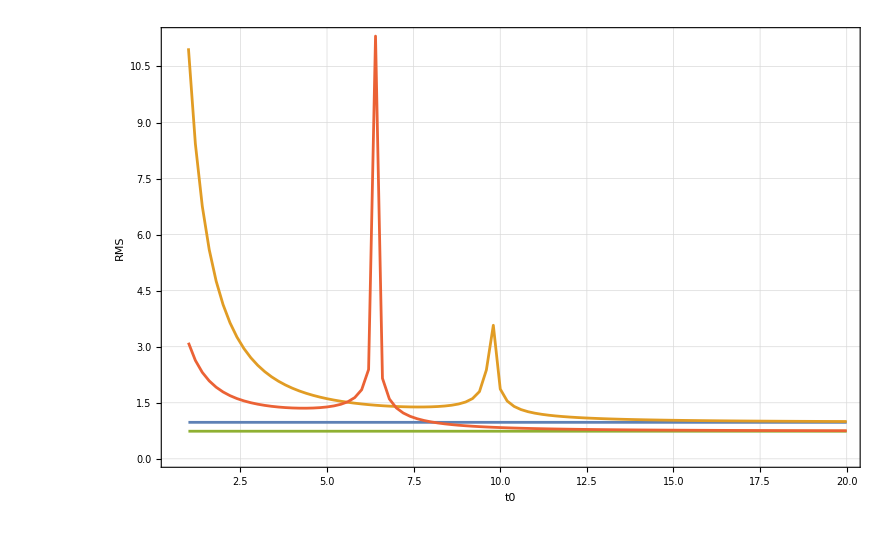

```mathematica
ListPlot[{UC0,SATD0,UCπ,SATDπ},GridLines->Automatic, Frame->True, FrameLabel->{"t0","RMS"}, Joined->True,PlotRange->All]
```

### 10b

```mathematica
Γ=1;
Δ0=1/2 Γ;
Ω0=1/2 Γ;
ω=ωCirc1DL;
dir=1;
t0=5/Γ;
```

```mathematica
(*plotting gx for ϕ=0 and ϕ=π*)
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

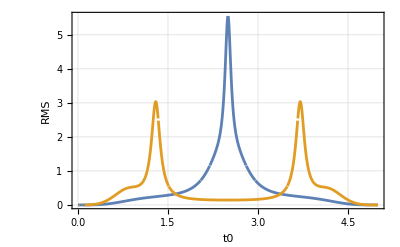

```mathematica
Plot[{Re[gxCircPath[Δ0,Ω0,Γ,0,ω,dir,t0,t]],Re[gxCircPath[Δ0,Ω0,Γ,π,ω,dir,t0,t]]},{t,0,t0},GridLines->Automatic, Frame->True, FrameLabel->{"t0","RMS"},PlotRange->All]
```

### 10c

```mathematica
(*plotting gz for ϕ=0 and ϕ=π*)
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

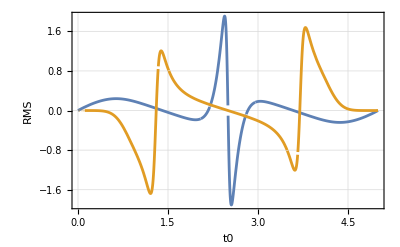

```mathematica
Plot[{Im[gxCircPath[Δ0,Ω0,Γ,0,ω,dir,t0,t]],Im[gxCircPath[Δ0,Ω0,Γ,π,ω,dir,t0,t]]},{t,0,t0},GridLines->Automatic, Frame->True, FrameLabel->{"t0","RMS"},PlotRange->All]
```

## Robustness (Fig. 11)

### Functions used for numerics

```mathematica
σx=({{0, 1}, {1, 0}});
σy=({{0, -ⅈ}, {ⅈ, 0}});
σz=({{1, 0}, {0, -1}});
```

```mathematica
(*choosen contour*)
ΔCircPath:=Function[{Δ0,φ,x},
Δ0 Sin[2 π x+φ]
];

ΩCircPath:=Function[{Δ0,Ω0,φ,x},
Ω0 + Δ0 Cos[2π x+φ]
];
(*time dependant parametrization of contour for single (ωCirc1) and double loop (ωCirc1DL)*)
ωCirc1:=#1(6(#3/#2)^5-15(#3/#2)^4+10(#3/#2)^3)&;
ωCirc1DL:=(ωCirc1[#1,#2,#3]UnitStep[#2-#3]+((#1)+ωCirc1[#1,#2,#3-#2])UnitStep[#3-#2])&;
```

#### functions specifically used for UC, TD, SATD robustness determination

```mathematica
(*these functions are different than the ones used to determine RADD robustness in subtle ways. They were written early in our research and may not be in the most optimized forms. But for completeness we kept these functions as is as they reproduce the same data we see in the paper. Effectively these functions and the ones used for RADD are determining the same outputs.*)
```

```mathematica
(*holomorphic eigenvalue*)
PosEigCircPath:=Function[{Δ0,Ω0,Γ,φ,x},
If[-Γ^2/4+(Δ0-Ω0)^2<0,(-1)^(Quotient[2π x+φ-π,2π]+1)√((ΔCircPath[Δ0,φ,x]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,x]^2),√((ΔCircPath[Δ0,φ,x]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,x]^2)]
];
(*holomorphic eigenvalue derivative*)
PosEigdotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
If[-Γ^2/4+(Δ0-Ω0)^2<0,(-1)^(1+Quotient[-π+φ+2 π ω[dir,t0,t],2 π]) ((2 ⅈ π Δ0 (Γ Cos[φ+2 π ω[dir,t0,t]]+2 ⅈ Ω0 Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,1][ω][dir,t0,t])/(√(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]]))),(2 ⅈ π Δ0 (Γ Cos[φ+2 π ω[dir,t0,t]]+2 ⅈ Ω0 Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,1][ω][dir,t0,t])/(√(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]]))]
];
(*pseudo rotation angle derivative*)
θdotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(2 π Δ0 (2 Δ0+2 Ω0 Cos[2 π ω[dir,t0,t]+φ]+ⅈ Γ Sin[2 π ω[dir,t0,t]+φ]))/(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[2 π ω[dir,t0,t]+φ]+4 ⅈ Γ Δ0 Sin[2 π ω[dir,t0,t]+φ])Derivative[0,0,1][ω][dir,t0,t]
];
(*pseudo rotation angle 2nd derivative*)
θdoubledotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(2 π Δ0 (2 π (Γ^2+4 (Δ0-Ω0) (Δ0+Ω0)) (-ⅈ Γ Cos[φ+2 π ω[dir,t0,t]]+2 Ω0 Sin[φ+2 π ω[dir,t0,t]]) (Derivative[0,0,1][ω][dir,t0,t])^2+(4 Δ0 (-Γ^2+2 Δ0^2+4 Ω0^2)-2 Ω0 (Γ^2-4 (3 Δ0^2+Ω0^2)) Cos[φ+2 π ω[dir,t0,t]]+2 Δ0 (Γ^2+4 Ω0^2) Cos[2 (φ+2 π ω[dir,t0,t])]+ⅈ Γ (-Γ^2+4 (3 Δ0^2+Ω0^2)+16 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]) Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,2][ω][dir,t0,t]))/(Γ^2-4 (Δ0^2+Ω0^2)-8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]-4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])^2
];
(*adiabatic frame Hamiltonian *)
DynMatCircPathAd:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
PosEigCircPath[Δ0,Ω0,Γ,φ,ω[dir,t0,t]]σz-θdotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σy
];
(*SATD correction the adaibatic frame*)
Wad:=Function[ {Δ0,Ω0,Γ,φ,ω,dir,t0,t},
1/2((-PosEigdotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]θdotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]+ PosEigCircPath[Δ0,Ω0,Γ,φ,ω[dir,t0,t]] θdoubledotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])/(PosEigCircPath[Δ0,Ω0,Γ,φ,ω[dir,t0,t]]^2+θdotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]^2))σx
];
(*solving for the UC dynamics with imprecision δΔ0*)
SolCircPathAdδΔ0UC:=Function[{Δ0,δΔ0,Ω0,Γ,φ,ω,dir,t0},
Module[{U},
First[U[t]/.NDSolve[{U'[t]==-ⅈ(DynMatCircPathAd[Δ0+δΔ0,Ω0,Γ,φ,ω,dir,t0,t]).U[t],U[0]==IdentityMatrix[2]},U,{t,0,t0},PrecisionGoal->12,AccuracyGoal->12,WorkingPrecision->24,InterpolationOrder->All,MaxSteps->10^6,Method->{"DiscontinuityProcessing" -> False }]]
]
];
(*solving for the TD dynamics with imprecision δΔ0*)
SolCircPathAdδΔ0TD:=Function[{Δ0,δΔ0,Ω0,Γ,φ,ω,dir,t0},
Module[{U},
First[U[t]/.NDSolve[{U'[t]==-ⅈ(DynMatCircPathAd[Δ0+δΔ0,Ω0,Γ,φ,ω,dir,t0,t]+θdotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σy).U[t],U[0]==IdentityMatrix[2]},U,{t,0,t0},PrecisionGoal->12,AccuracyGoal->12,WorkingPrecision->24,InterpolationOrder->All,MaxSteps->10^6,Method->{"DiscontinuityProcessing" -> False }]]
]
];
(*solving for the SATD dynamics with imprecision δΔ0*)
SolCircPathAdδΔ0SATD:=Function[{Δ0,δΔ0,Ω0,Γ,φ,ω,dir,t0},
Module[{U},
First[U[t]/.NDSolve[{U'[t]==-ⅈ(DynMatCircPathAd[Δ0+δΔ0,Ω0,Γ,φ,ω,dir,t0,t]+Wad[Δ0,Ω0,Γ,φ,ω,dir,t0,t]).U[t],U[0]==IdentityMatrix[2]},U,{t,0,t0},PrecisionGoal->12,AccuracyGoal->12,WorkingPrecision->24,InterpolationOrder->All,MaxSteps->10^6,Method->{"DiscontinuityProcessing" -> False }]]
]
];
```

```mathematica
(*final average transition probability with imprecision for a given loop*)
ErrorAnalysisFixedTimeUC=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,σδΔ0,NSamp,cinit,cfinal},
Module[{tbFlow,(*a list of random noise values determined from a Gaussian Distribution for N (1000) samples*)tbΔ0=RandomVariate[NormalDistribution[0,σδΔ0],NSamp]},
(*determining the flow matrix at the final loop time using the imprecision noise values*)
tbFlow=ParallelMap[SolCircPathAdδΔ0UC[Δ0,#,Ω0,Γ,φ,ω,dir,t0]/.t-> t0&,tbΔ0];
(*finding the fidelity at the final loop time for each imprecision value, then finding the averaging fidelity and taking its log10*)
Log10[1/Length[tbFlow] Total[ParallelMap[1-Abs[cfinal.#.cinit]^2/(Abs[{1,0}.#.cinit]^2+Abs[{0,1}.#.cinit]^2)&,tbFlow]]]

]
];
```

```mathematica
(*final average transition probability with imprecision for a range of loop times*)
ErrorAnalysisUC=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0Max,t0min,t0Steps,σδΔ0,NSamp,cinit,cfinal},
Module[{δt0=(t0Max-t0min)/(t0Steps-1),tbt0,tbAvgErr},
(*range of loop times to check robustness for*)
tbt0=Range[t0min,t0Max,δt0];
(*determining average fidelity error with imprecision present given a range of loop times*)
tbAvgErr=Map[{Γ #,ErrorAnalysisFixedTimeUC[Δ0,Ω0,Γ,φ,ω,dir,#,σδΔ0,NSamp,cinit,cfinal]}&,tbt0]

]
];
```

```mathematica
(*final average transition probability with imprecision and the TD correction for a given loop*)
ErrorAnalysisFixedTimeTD=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,σδΔ0,NSamp,cinit,cfinal},
Module[{tbFlow,(*a list of random noise values determined from a Gaussian Distribution for N (1000) samples*)tbΔ0=RandomVariate[NormalDistribution[0,σδΔ0],NSamp]},
(*determining the flow matrix at the final loop time using the imprecision noise values*)
tbFlow=ParallelMap[SolCircPathAdδΔ0TD[Δ0,#,Ω0,Γ,φ,ω,dir,t0]/.t-> t0&,tbΔ0];
(*finding the fidelity at the final loop time for each imprecision value, then finding the averaging fidelity and taking its log10*)
Log10[1/Length[tbFlow] Total[ParallelMap[1-Abs[cfinal.#.cinit]^2/(Abs[{1,0}.#.cinit]^2+Abs[{0,1}.#.cinit]^2)&,tbFlow]]]

]
];
```

```mathematica
(*final average transition probability with imprecision and the TD correction applied for a range of loop times*)
ErrorAnalysisTD=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0Max,t0min,t0Steps,σδΔ0,NSamp,cinit,cfinal},
Module[{δt0=(t0Max-t0min)/(t0Steps-1),tbt0,tbAvgErr},
(*range of loop times to check robustness for*)
tbt0=Range[t0min,t0Max,δt0];
(*determining average fidelity error with imprecision present given a range of loop times*)
tbAvgErr=Map[{Γ #,ErrorAnalysisFixedTimeTD[Δ0,Ω0,Γ,φ,ω,dir,#,σδΔ0,NSamp,cinit,cfinal]}&,tbt0]

]
];
```

```mathematica
(*final average transition probability with imprecision and the SATD correction for a given loop*)
ErrorAnalysisFixedTimeSATD=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,σδΔ0,NSamp,cinit,cfinal},
Module[{tbFlow,(*a list of random noise values determined from a Gaussian Distribution for N (1000) samples*)tbΔ0=RandomVariate[NormalDistribution[0,σδΔ0],NSamp]},
(*determining the flow matrix at the final loop time using the imprecision noise values*)
tbFlow=ParallelMap[SolCircPathAdδΔ0SATD[Δ0,#,Ω0,Γ,φ,ω,dir,t0]/.t-> t0&,tbΔ0];
(*finding the fidelity at the final loop time for each imprecision value, then finding the averaging fidelity and taking its log10*)
Log10[1/Length[tbFlow] Total[ParallelMap[1-Abs[cfinal.#.cinit]^2/(Abs[{1,0}.#.cinit]^2+Abs[{0,1}.#.cinit]^2)&,tbFlow]]]

]
];
```

```mathematica
(*final average transition probability with imprecision and the SATD correction applied for a range of loop times*)
ErrorAnalysisSATD=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0Max,t0min,t0Steps,σδΔ0,NSamp,cinit,cfinal},
Module[{δt0=(t0Max-t0min)/(t0Steps-1),tbt0,tbAvgErr},
(*range of loop times to check robustness for*)
tbt0=Range[t0min,t0Max,δt0];
(*determining average fidelity error with imprecision present given a range of loop times*)
tbAvgErr=Map[{Γ #,ErrorAnalysisFixedTimeSATD[Δ0,Ω0,Γ,φ,ω,dir,#,σδΔ0,NSamp,cinit,cfinal]}&,tbt0]

]
];
```

#### functions specifically used for RADD robustness determination

```mathematica
(*constucting the holomorphic eigenvalue, works for a double loop*)
EigCircPath:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2)
];
```

```mathematica
(*constucting thederivative of the holomorphic eigenvalue, works for a double loop*)
EigDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])((2 ⅈ π Δ0 (Γ Cos[φ+2 π ω[dir,t0,t]]+2 ⅈ Ω0 Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,1][ω][dir,t0,t])/(√(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])))
];
```

```mathematica
(*constucting the holomorphic pseduo rotation angle into the adiabatic frame, works for a double loop*)
θDiagCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
-2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)+(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]
];
```

```mathematica
(*constucting the derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(4 π Δ0 (2 Δ0+2 Ω0 Cos[φ+2 π ω[dir,t0,t]]+ⅈ Γ Sin[φ+2 π ω[dir,t0,t]]))/(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])Derivative[0,0,1][ω][dir,t0,t]
];
```

```mathematica
(*constucting the 2nd derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(4 π Δ0 (2 π (Γ^2+4 (Δ0-Ω0) (Δ0+Ω0)) (-ⅈ Γ Cos[φ+2 π ω[dir,t0,t]]+2 Ω0 Sin[φ+2 π ω[dir,t0,t]]) (Derivative[0,0,1][ω][dir,t0,t])^2+(4 Δ0 (-Γ^2+2 Δ0^2+4 Ω0^2)-2 Ω0 (Γ^2-4 (3 Δ0^2+Ω0^2)) Cos[φ+2 π ω[dir,t0,t]]+2 Δ0 (Γ^2+4 Ω0^2) Cos[2 (φ+2 π ω[dir,t0,t])]+ⅈ Γ (-Γ^2+4 (3 Δ0^2+Ω0^2)+16 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]) Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,2][ω][dir,t0,t]))/(Γ^2-4 (Δ0^2+Ω0^2)-8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]-4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])^2
];
```

```mathematica
(*adiabatic frame Hamiltonian. note we use a sign change for "EigCircPath" for conventional purposes.*)
DynMatAd:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
-EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σz-1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σy
];
```

```mathematica
(*RADD correcting function*)
F3:=Function[{A,σ,n,t,t0},
A Exp[-(((t-t0/2)/σ)^2)^n]
];
(*RADD correcting function derivative*)
F3dot:=Function[{A,σ,n,t,t0},
-(4 A ⅇ^(-((t-t0/2)^2/σ^2)^n) n ((t-t0/2)^2/σ^2)^n)/(2 t-t0)
];
(*the holomorphic SATD pseudo roation angle with the correct phases applied at the correct times*)
μ:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t,ts,ph},
-ArcTan[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])/((1+F3[A,σ,n,t,t0])EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])]+Total[Map[{ph[[#]]UnitStep[Boole[ts[[#,1]]≤ t<ts[[#,2]]]]}&,DeleteDuplicates[Flatten[Map[Position[ts,Flatten[Select[ts,#[[1]]≤ t<#[[2]]&][[#]]]]&,Range[1,Length[Select[ts,#[[1]]≤ t<#[[2]]&]]]],2]]],2]
];
(*the holomorphic SATD pseudo roation angle derivative*)
μdot:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t},
(2 ((1+F3[A,σ,n,t,t0]) θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t] EigDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]+EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t] (θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t] F3dot[A,σ,n,t,t0]-(1+F3[A,σ,n,t,t0]) θDiagDDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])))/(4 EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]^2 (1+F3[A,σ,n,t,t0])^2+θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]^2)
];
(*generalized gx correction in the lab frame, assumes any μ dressing angle for SATD*)
gx2:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t,ts,ph},

1/2 (-2 ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]+Cot[μ[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t,ts,ph]]Sin[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]+Cos[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] μdot[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t])

];
(*generalized gz correction in the lab frame, assumes any μ dressing angle for SATD*)
gz2:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t,ts,ph},
1/2 (ⅈ Γ+2 ΔCircPath[Δ0,φ,ω[dir,t0,t]]+Cos[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]Cot[μ[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t,ts,ph]] θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]-Sin[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] μdot[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t])

];
```

```mathematica
(*finding the times when real part of the SATD pseudo rotation angle goes to 0*)
tb0sRetimes:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{tbtest,index},
(*making a list of points to determine any sudden sign changes between two neighboring points*)
tbtest=Table[{t,N[Re[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])/EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]},{t,0,t0,t0/99}];
(*checking the sign difference between two points, then assinging an index value to the points of interest*)
index=Sort[Join[Flatten[Position[Differences[Sign[tbtest[[2;;,2]]]],2]+1],Flatten[Position[Differences[Sign[tbtest[[2;;,2]]]],-2]+1]]];
(*using the points of interest to find the roots of the function - using these "known" intervals where the sign change occurs reduces overall searching time for Find Root*)
Map[t/.FindRoot[Re[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])/EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]==0,{t,tbtest[[#,1]]},Method->"AffineCovariantNewton"]&,index]]
];
```

```mathematica
(*determining how many times the SATD pseduo rotation angle crosses the branch cut for 1 loop*)
t0CriticalCheck:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,BrCutCrossTimes},
Module[{tbtest,index,tb0sReCheckt0,tb0sImt0,tb0sRefinalt0,tb0sImfinalt0},
(*using the output of "tb0sRetimes" to check that the Re[μ]=0 and Im[μ]<0 to qualify as a branch cut crossing.*)
tb0sReCheckt0=Select[Select[Chop[Map[{Re[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#])/EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#]],#}&,BrCutCrossTimes],10^-16], #[[1]]== 0&],0<#[[2]]< t0 &][[;;,2]];
tb0sImt0=Map[Im[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#])/EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#]]&,tb0sReCheckt0];
(*making a list of the imaginary parts that satisfy Im[μ]<0 given the times from the output of "tb0sRetimes"*)
tb0sImfinalt0=Select[Map[{tb0sReCheckt0[[#]],tb0sImt0[[#]]}&,Range[1,Length[tb0sImt0]]],#[[2]]≥ 1|| #[[2]]≤ -1  &][[;;,2]];
(*# of times branch cut is crossed*)
Length[tb0sImfinalt0]
]
];
```

```mathematica
(*checking if the times found from the function "tb0sRetimes" correspond to branch cut crossings*)
tb0sRefinalList:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,tb0sRe},
Module[{tb0sReCheck,tb0sIm,tb0sImfinal,tb0sRefinal},
(*using the output of "tb0sRetimes" to check that the Re[μ]=0 and Im[μ]<0 to qualify as a branch cut crossing.*)
tb0sReCheck=Select[Select[Chop[Map[{Re[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#])/((1+F3[A,σ,n,#,t0])EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#])],#}&,tb0sRe],10^-4], Abs[#[[1]]]== 0&],0<#[[2]]< 2t0 &][[;;,2]];
tb0sIm=Map[Im[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#])/((1+F3[A,σ,n,#,t0])EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#])]&,tb0sReCheck];
(*making a list of the real parts that satisfy Re[μ]=0 and Im[μ]<0*)
tb0sRefinal=Sort[Select[Map[{tb0sReCheck[[#]],tb0sIm[[#]]}&,Range[1,Length[tb0sIm]]],#[[2]]≥ 1|| #[[2]]≤ -1  &][[;;,1]]]
]
];
```

```mathematica
(*determining the times when the branch cut is crossed and the accompanying phase corrections*)
FinalTimesPhases:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,tb0sRefinal},
Module[{α,β,PhaseCond,Time,FinalTime,FinalPhases},
(*using the output from "tb0sRefinalList", we check the value of μ just before and after the given times to determine what sign the phase shift needs to be and at what exact time to apply it; we do not want to double count any times, so based of the FindRoot results we determine a hard cutoff when to apply the phase. We use 10^-6 as the limit of our precision.*)
(*checking just before*)
α=Map[
Re[-ArcTan[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]])])/((1+F3[A,σ,n,(tb0sRefinal[[#]]),t0])EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]])])]]-Re[-ArcTan[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]]-10^-6)])/((1+F3[A,σ,n,(tb0sRefinal[[#]]-10^-6),t0])EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]]-10^-6)])]]&,Range[1,Length[tb0sRefinal]]];
(*checking just after*)
β=Map[N[Re[-ArcTan[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]]+10^-6)])/((1+F3[A,σ,n,(tb0sRefinal[[#]]+10^-6),t0])EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]]+10^-6)])]]-Re[-ArcTan[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]])])/((1+F3[A,σ,n,(tb0sRefinal[[#]]),t0])EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]])])]]]&,Range[1,Length[tb0sRefinal]]];
(*assigning the necessary phase at a given branch cut crossing time depending on if α is positive or negative π. If discontinuity occurs at time given by "tb0sRefinalList", then set hard cutoff at that time. If it occurs just after at the time given by "tb0sRefinalList", set it just after.*)
PhaseCond=Map[If[Abs[ α[[#]]] >1,{α[[#]],tb0sRefinal[[#]]}, {β[[#]],tb0sRefinal[[#]]+10^-6}]&,Range[1,Length[tb0sRefinal]]];
(*making a list of the branch cut times and phases when the phases need to be applied (FinalTime), and the accompanying value of the phases(FinalPhases)*)
Time=PhaseCond[[;;,2]];
FinalTime=Partition[Insert[Insert[Time,0,1],2t0,-1],2,1];
FinalPhases=Insert[-Map[Total[Map[N[PhaseCond[[;;,1]][[##]]]&,Range[1,#]]]&,Range[1,Length[Time]]],0,1];
(*outputing a combined list FinalTime and FinalPhases*)
{FinalTime,FinalPhases}
]
];
```

```mathematica
(*creating a list of times and phases which need to be applied to produce the holomorphic angle μ*)
μF3CircPathCorr:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,BrCutCrossTimes},
Module[{tb0sRefinal},
(*getting a list of branch cut times when phases need to be applied*)
tb0sRefinal=tb0sRefinalList[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,BrCutCrossTimes];
(*if the list is empty, return{{0,2t0}},{0}} indicating no corrections need to be applied*)
If[Length[tb0sRefinal]==0,List[{{0,2t0}},{0}],
(*otherwise determine the list of times and phases that need to used to build the holomorphic angle μ*)
FinalTimesPhases[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,tb0sRefinal]
]
]
];
```

```mathematica
(*RADD correction in the adiabatic frame*)
WRMSRADD := Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t},
Module[{BrCutCrossTimes,Ts,Ph,x},
BrCutCrossTimes=tb0sRetimes[Δ0,Ω0,Γ,φ,ω,dir,t0];
{Ts,Ph}=μF3CircPathCorr[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,BrCutCrossTimes];(Cos[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] gz2[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t,Ts,Ph]+gx2[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t,Ts,Ph] Sin[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])σz +(gx2[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t,Ts,Ph] Cos[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-gz2[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t,Ts,Ph] Sin[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])σx
]
];
(*solving for the RADD dynamics in the adiabatic frame*)
SolCircPathRADD:=Function[{Δ0,δΔ0,Ω0,Γ,φ,ω,dir,t0,A, σ, n},
First[U[t]/.NDSolve[{U'[t]==-ⅈ (DynMatAd[Δ0+δΔ0,Ω0,Γ,φ,ω,dir,t0,t]+WRMSRADD[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t]).U[t],U[0]==IdentityMatrix[2]},U,{t,0,t0},Method->{"DiscontinuityProcessing"->False}]]
];

(*final average transition probability with imprecision and the RADD correction for a given loop*)
ErrorAnalysisFixedTimeRADD=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,σδΔ0,NSamp,cinit,cfinal,A,σ,n},
Module[{tbFlow,(*a list of random noise values determined from a Gaussian Distribution for N (1000) samples*)tbΔ0=RandomVariate[NormalDistribution[0,σδΔ0],NSamp]},
(*determining the flow matrix at the final loop time using the imprecision noise values*)
tbFlow=Map[SolCircPathRADD[Δ0,#,Ω0,Γ,φ,ω,dir,t0,A,σ,n]/.t-> t0&,tbΔ0];
(*finding the fidelity at the final loop time for each imprecision value, then finding the averaging fidelity and taking its log10*)
Log10[1/Length[tbFlow] Total[Map[1-Abs[cfinal.#.cinit]^2/(Abs[{1,0}.#.cinit]^2+Abs[{0,1}.#.cinit]^2)&,tbFlow]]]

]
];
(*final average transition probability with imprecision and the RADD correction applied for a range of loop times*)
ErrorAnalysisRADD=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0Max,t0min,t0Steps,σδΔ0,NSamp,cinit,cfinal,A,σ,n},
Module[{δt0=(t0Max-t0min)/(t0Steps-1),tbt0,tbAvgErr},
(*range of loop times to check robustness for*)
tbt0=Range[t0min,t0Max,δt0];
(*determining average fidelity error with imprecision present given a range of loop times*)
tbAvgErr=Map[{Γ #,ErrorAnalysisFixedTimeRADD[Δ0,Ω0,Γ,φ,ω,dir,#,σδΔ0,NSamp,cinit,cfinal,A,σ,n]}&,tbt0]

]
];
```

### Data for UC, TD, SATD, RADD

```mathematica
(*note that convention for gain and loss mode is switched from paper for RADD: 2->2 is now the gain mode, 1->1 is loss mode. UC, TD, SATD follow normal convention*)
```

```mathematica
(*here σδΔ0 is the same as β in the paper*)
```

#### UC Error Analysis (φ=0 → w/ Imprecision)

```mathematica
Γ=1;
Δ0=499999/1000000Γ;
Ω0=1/2Γ;
φ=0;
ω=ωCirc1;
dir=1;
```

3%

```mathematica
σδΔ0=3/100 1/2 Γ;
NSamp=1000;
cinit={1,0};
cfinal={1,0};

t0Max=20/Γ;
t0min=1/Γ;
t0Steps=20;

AbsoluteTiming[gain3UC=ErrorAnalysisUC[Δ0,Ω0,Γ,φ,ω,dir,t0Max,t0min,t0Steps,σδΔ0,NSamp,cinit,cfinal];]
```

```mathematica
gain3UC={{1,-0.01639326105872183545722317477036140558`23.255835516639202},{2,-0.07595667294275403161538161115661475974`23.145512201529595},{3,-0.18043931704765361834706102288496733057`23.278464842798048},{4,-0.31772801004090447340992605128294311324`23.011533290337745},{5,-0.47593116036791546113207813559170148506`22.90956917721465},{6,-0.64923213408616977085536046005894048162`22.95121237717563},{7,-0.8353011952888932569827718796236713052`22.82677872961082},{8,-1.03749765592642423129577731372290440882`22.662567570605948},{9,-1.25633073198324769748352269732795429108`22.569168704629355},{10,-1.49314120848970172211638790818438355584`22.44144337386792},{11,-1.75287340966227778428875664112225145878`22.227097788265777},{12,-2.02931436976232423907692678422639089654`22.02668917661916},{13,-2.32324525175927347596551169775709869434`21.801127379594195},{14,-2.60701012727866035485221883122033796122`21.564551611163623},{15,-2.85982241443448684501279719494666110432`21.355714048277925},{16,-3.04477891557525264601617637513793647939`21.19711131735139},{17,-3.17693841058445152471538455416751410401`21.0844352737516},{18,-3.29240448752931544429538250110925432486`20.984420072992975},{19,-3.42344113671341176657148392009652227212`20.87017424582992},{20,-3.58636430103022221735622807782367226652`20.728153041148413}};
```

```mathematica
σδΔ0=3/100 1/2 Γ;
NSamp=1000;
cinit={0,1};
cfinal={0,1};

t0Max=20/Γ;
t0min=1/Γ;
t0Steps=20;

AbsoluteTiming[loss3UC=ErrorAnalysisTD[Δ0,Ω0,Γ,φ,ω,dir,t0Max,t0min,t0Steps,σδΔ0,NSamp,cinit,cfinal];]
loss3UC
```

```mathematica
loss3UC={{1,-4.85288602383454254985562700545502400931`19.593273357904863},{2,-4.04785873622799425015656848086935011025`20.319540872533075},{3,-3.48843533977075392005254979156042723357`20.814391998362286},{4,-3.04276774696706470223121878136233165668`21.200400324546084},{5,-2.64947255500333161568075925631578149959`21.53440190705712},{6,-2.32442601239552813380179786430642150719`21.799593067637087},{7,-2.02650625132250514965518677646202465921`22.035988291862562},{8,-1.75793297508788689842538694018822665409`22.24565308259815},{9,-1.50843452830649187683054671264188845432`22.400666056096327},{10,-1.31462923915036207723320699725915637533`22.552639264269015},{11,-1.10258118482691083583938369890553698687`22.64600205736078},{12,-0.97166435847519467968626072948531329236`22.69623853654775},{13,-0.79485773818633675975452541637577245063`22.817158039309962},{14,-0.65309270551603528635312530276622825492`22.762271192270134},{15,-0.52709132339752783891668870111264846545`22.897522956301813},{16,-0.4400314614853092762974452839169591122`22.785812940175795},{17,-0.33409640092920349924976693754780667783`22.88959887722735},{18,-0.27518439348413517890118730600147531945`22.841421353790622},{19,-0.20628586154993023018089959364941385239`22.744637857485166},{20,-0.15554966945653547083104801198032354464`22.992407460576434}};
```

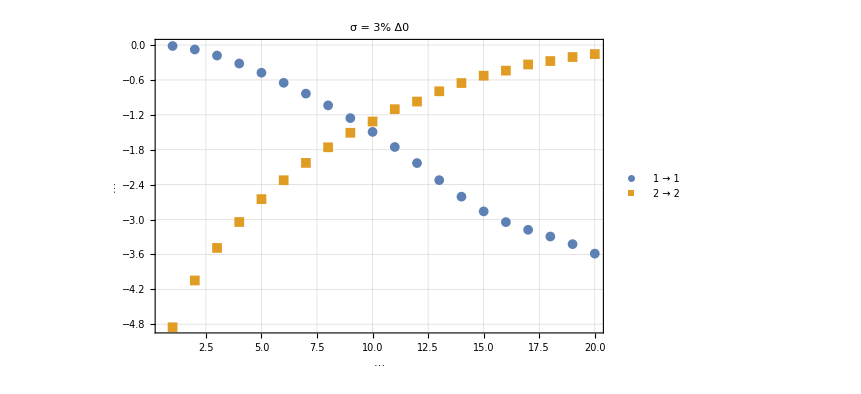

```mathematica
ListPlot[{gain3UC, loss3UC},PlotRange-> All,Frame->True,GridLines->Automatic, PlotLegends->Placed[{"1 → 1", "2 → 2"},{Right, Center}],PlotLabel->Style["σ = 3% Δ0",20], PlotMarkers->{Automatic,10},GridLinesStyle-> Thin, FrameLabel->{Style["",15],Style["(*GraphicsBox[{Thickness[0.017283097131005877`], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGI3IGYC4ur7P24Zcys68McG3DcqV3CA8ZWvPQpmmKPg
cPoMELxRcLijKbvm/2YFh7VCOnzp5xD8NVD+bSh/JgisRMiXHt7mOnOuAty8
Fd9eVpyZoOCwN7/m7cypCD5YX6eCw38QiIfKiyo4zACJW8o7uK85upzhh7RD
qwK76hkRWQg9RcwhIw0I2ETh/Aeu8Y6zCgXgfJDzz/Tww/n2JY61p2MQfNVP
Ki9nneRzCHl7+eOMhWIOMaoRMuf28Doo7FqwL3WdmEM6yPxlvA4gKu0Ygr8j
2Criv7o4nA/WVyPu8HXfx63p12DqxR1axGtZM9n4IPaZSDgwgECDqMPr4q2i
v7k1Ifa8E3UQ6fF6xfJFE+J+QTEHmXlxmqcNtBxEKieVnHWRgvPlQer7pOH8
A937mkweY/L1tVYKX1iC4EtMvcKZ8UgL4s4YBP88KHx0EHxwOFtIwfng+JCX
dPA5wW47+6qWQxUofWhLwPngcDguCOeD1d8XgPMh4cMPNw8WPjC+7xPPS6bC
CD4kvHgw+CycXfLJeQg+qn8R/ILlJRv++fPB+ZDwFMLgg935XxPOn9LeGnV5
j6bDfTQ+TB4cX92aUP8JOkiDzdN0kNkoNp/pAZvDm7bcbqPdEg5Lbi1/bMjM
5tAX0e3PKCDuEADy32VW1PTo888exn9T+zj7/JpfcH4zyH/HfmDwwfljpyic
b2IMAqIO66W36Z568xPOr3nR9Gvazr8IPii+Tss4wPiuoPi9IQvng9PXE1lI
unQQheY3OYh/pMUcum08d6V9UoCEi6KCQzinWLvxf2g+tUeUF8Igc1IQfFh5
AgCUldIw
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{14.435899999999998`, 8.57813}, {14.435899999999998`, 9.71094}, {13.696899999999998`, 10.5563}, {12.612499999999997`, 10.5563}, {11.0391, 10.5563}, {9.48906, 8.840629999999999}, {9.48906, 7.159379999999999}, {9.48906, 6.02656}, {10.2281, 5.1812499999999995`}, {11.3125, 5.1812499999999995`}, {12.898400000000002`, 5.1812499999999995`}, {14.435899999999998`, 6.8968799999999995`}, {14.435899999999998`, 8.57813}}, CompressedData["
1:eJxTTMoPSmViYGAQBmIQnZ4GBG7aDrc1Zdf8Z1ZygPHDOcXajfkVIfxjWg4i
lZNKzrLIOpw47LQ2856mQ4xqhMw5GSkHv4sTY/491nCouf/jlvFrMQfRHq9X
LFPUHc6AwBpRB5D2tGVqcH5m/ofWkyWqcL6RMRBMVnFoVWBXPTNFHM6HmCcF
50Psk3Vo4fVfP0VV1aH88DbXmX8VHKTmxWmevqDqsFZIhy9dT8nh19vXBywf
qzn4gtzFrOKw3aHp0XELDYefIPHFKg7GYKAJ54P9E6cF58P8HwHy/3plB/Tw
AQDksYAh
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}}, {{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAQBWIQ3e31isVkoZFDyNvLH2c4Sjvoa60UvjDFyGG9kA5f
ep2UQ/FW0d+n+4wczoCAj5RDI8vRfsN0I4cv+z5uTZ8m6cDtplrK9MrQoS+i
259RQNxhJghkGjrsCLaK+K8u5jB9An+VGTeCn54GBMsM4Pzk2DtuzB4GDiKV
k0rOpojD+fK7FuxLXScF54PtM5N1WHJ/H9+cxQYOqSBz3BQh5j0zcPiwaL3C
2QglhyeJC6+Z2Bs6RHCKtRuvV3bg918/JfWEocPPt68PWC5WgfA9jOD85S88
9P4LGsP5YPdbGjusBfl/nRKcD6Y7lRwK13TfzjAwdhAGuddEyQE9/ADhe49+

"], CompressedData["
1:eJxTTMoPSmViYGAwAmIQXbxV9Pfpc0YOwW8vf5zBKOTw51vpgzmKJg4RnGLt
xuuVHVSfNM87q2Xi4LHm6HKGHwi+1Lw4zdMCKjj5aWCg4qDxlnefAaeJQ8Nv
q4JzK1Qcpk/grzK7bQznL3/hofd/IoL/eUNA9qx0Y4cniQuvmeirOJw+7LQ2
M87YwWVCs1Bal7JDOshYM2OHC1fD3uhbqzh0e71iMXlo5DClvTXqsoyqA7//
+impHgj+Rr28xYx/DOD8H29fH7Bk1nf4sGi9wtkbinC+O8h/M2Tg/BBQeCwU
h4SHo4GDiTEIiDrclK5JNGI1hPOvC31yPL8MwYe4zwjKF3ewrYxYYZpr5LAj
2Criv7qEgzooPCyNHL7s+7g1/ZsInL9WSIcv/Z6IA7ebaimTlpFDjGqEzLk7
wpBw+G8IkbcThJj31tDh7Bkg4BGAyNcbOiy5tfyx4WEeSHgyGjrMmAkENzkc
IsS3X2ToM4Dz1UHx44XgnwCF7z19OD8V5H43fYczYPM5HdaDInStnkPJ8pIN
/85zOkiA4rlA34HHkc9rxkouB1ObvUHTFupD/BPGC+fv797XZJLMB+eD1b/k
d9jq0PToeAQ0vHcIOPjfAgboJT04/z8I2CP4D0AeWKDr0CJey5rZxg/nQ8zn
gfO3eW2wmFPJ4XAelC5m60HC/zMbJH0EGsD54PR5yxDOb2Q52m+43MjBvsSx
9vQdPgf0/AAA4EBVhA==
"]}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{23.579700000000003`, 2.3203099999999997`}, {23.579700000000003`, 2.7609399999999997`}, {22.4234, 2.7609399999999997`}, {22.4234, 13.799999999999997`}, {23.579700000000003`, 13.799999999999997`}, {23.579700000000003`, 14.240599999999999`}, {21.9828, 14.240599999999999`}, {21.9828, 2.3203099999999997`}, {23.579700000000003`, 2.3203099999999997`}}}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJZIGYC4hkzgeCkjYOJMQiIOsD4rQrsqmemiDmoPmme
dzYLwT9x2GltZpw1nH9DuibRKNTaYUewVcR/dXE4f62QDl/6PQk439xmb9C0
h5pwPgtnl3xynhacL9Lj9YqlRMuBx3/9lFQJBL9kq+jv0+esHJ4kLrxmcl7T
IT0NCMysHNaDHPZWw2GjXt5ixj8WGPzJ7a1Rl200HMSnXuHMcLKE89VB/rmF
4B9pWx5+qsnK4fzVsDf6txF8mPthfJj/wOFTaQX3v21lxArTXEs4/yQofPgw
+bDwlZ4Xp3k6wdKh6v6PW8beog71v60KznVYwfnPs7S/TX+L4IPdH2QN5zew
HO03LLeB89HjDwAjMb9b
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {{{40.773399999999995`, 8.27969}, {40.773399999999995`, 8.518749999999999}, {40.546899999999994`, 8.518749999999999}, {40.37969999999999, 8.518749999999999}, {33.882799999999996`, 8.518749999999999}, {33.715599999999995`, 8.518749999999999}, {33.4891, 8.518749999999999}, {33.4891, 8.27969}, {33.4891, 8.04219}, {33.715599999999995`, 8.04219}, {33.882799999999996`, 8.04219}, {40.37969999999999, 8.04219}, {40.546899999999994`, 8.04219}, {40.773399999999995`, 8.04219}, {40.773399999999995`, 8.27969}}}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJx11X0slHEcAPDzErOE0d3ZzJy4szvvLyHT9rXG81IbmcWkedudViiLeYmk
QiN1YZxLIitaM/rDREu1ZiyUpmxpi5ktwkQlee1+z8PvtzG/7fnjs+ee575v
v99jn3AhXGkgEAj0dFeC7tLXXT/bws5rM1nQqM1zfPfLoFceUN5fzcJVw547
nn4K7LiIcKd6RgFOk9frBrUshI3a5MaX7+0TfcZH731WgGFjeYBeGbGmRrfS
iFVo1VHY8W+HnZUFxI+naLfNtN2ufejQuZZE7K54YjXkqIABtHKJ09uFq/1V
xAcXgz6o/ux27qKuECtybC7/DuIOuDbRq5FDdlTz4cFfFGyilS+HyfiGEZ95
CiqKC6OHA+Vwi/1h6GNPwWxRSqnXC2tINvlXn2RFwe2o0lA9CzGYhrZWKi0o
KJQYSwcqRcCivB6FYIdIM/S1N4njUD2ydxuVsaZTiO3jjZaQj6eY2H+kJ8VH
TfxF1yavFuIslE9/COSMLY96HxfCldWAi++niLn3tVLYwSi+IeLt+my/7xKq
t4jGrlwyitU4Ej8t/XpW4Lfbkq76bqWZCHs7X7ughcQBV+Kipsh3XqbEXFsq
SD25+NS6fqL4Zogj5oYXNA1i7BZLF7Okb2L8vAAtsMbz8rt7oT2pyprv1zIF
kSaiYu/YQyBD811CY3P5bhBzc2HMgPmZsDGvv/bYSjTnIfY77kv4/bGPgbHg
2CBtg4TvzzoNl1H8NhIY6zar9V6hgSuXgQTyUH+WaShD89Rmt6e5+Ttth+Nz
WnSc1srt+HkxYbCPo/kTEnP9FjP4eUvUX1uGz89cwvcjg4Gpc85L1fel2Nz+
bJfy85/G8PtpVAp1gS6ftCpiLr4o4s7RknVlJAO+gS/Dq95sPX9y6370lj0Z
aF6azhpQO8DsgW6PGkuGr6O5A///ZTT2SkxKz4Y+sau6ftlTReP9+cwttVEv
nebPK0sFP2+ZND4PuHq0Ezeh86WAwc5H8QOLXYzmMYaFlbmZ10eOybHXlzLG
a+86YXPnUjIx/SrP1v+7DLjzN5LlzzNKBu4o3lMs9HU9LzPykMEayiechYko
ccfHcSk29/te4gJ0XlVLYR7VJ5oFDxTfDSm/vxOJH6B+pBJz+zOdxf3c+T34
D6pZmus=
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{55.44839999999999, 2.3203099999999997`}, {55.44839999999999, 14.240599999999999`}, {53.849999999999994`, 14.240599999999999`}, {53.849999999999994`, 13.799999999999997`}, {55.0063, 13.799999999999997`}, {55.0063, 2.7609399999999997`}, {53.849999999999994`, 2.7609399999999997`}, {53.849999999999994`, 2.3203099999999997`}, {55.44839999999999, 2.3203099999999997`}}}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{86.78978331257782, 24.508064757160646`},PlotRange->{{0., 57.86}, {0., 16.34}}])", 15]}, LabelStyle->{Bold,24}]
```

#### UC Error Analysis (φ=π → w/ Imprecision)

```mathematica
Γ=1;
Δ0=499999/1000000Γ;
Ω0=1/2Γ;
φ=π-10^-16;
ω=ωCirc1;
dir=1;
```

3%

```mathematica
σδΔ0=3/100 1/2 Γ;
NSamp=1000;
cinit={1,0};
cfinal={1,0};

t0Max=40/Γ;
t0min=1/Γ;
t0Steps=40;

AbsoluteTiming[gain3UCπ=ErrorAnalysisUC[Δ0,Ω0,Γ,φ,ω,dir,t0Max,t0min,t0Steps,σδΔ0,NSamp,cinit,cfinal];]
gain3UCπ
```

```mathematica
gain3UCπ={{1,-0.01460211594804596287848079432518802255`23.214591975574685},{2,-0.02463078356503575713085999843549222566`23.084633573031624},{3,-0.0252055756488783170931003265058109086`22.987461554075995},{4,-0.02143121691720802364550308236176778765`22.91018628636407},{5,-0.01664301664338860234166080825003255292`22.845651387311193},{6,-0.01231892042813720540823487497784372169`22.78985448360572},{7,-0.00888825671464455995069615032522450841`22.740429383072733},{8,-0.00640578927205337826424229635519045284`22.695930620368767},{9,-0.00471635859510692282266577635089963721`22.65537948765518},{10,-0.0036699487285971076519759003553028107`22.618118819425867},{11,-0.00330640030533974037394039910161196104`22.58355214846935},{12,-0.00399630518369144051426018178751267537`22.55105579386262},{13,-0.010677017504815417027231346407180359`22.51800184715072},{14,-0.10687025301429401696874250073255007501`22.440476503742506},{15,-0.08544396125982429060889257607045303162`22.425208697533282},{16,-0.00949731508500618420505358372425704154`22.43955966315156},{17,-0.00094482520753749625337175619450470846`22.42004775626929},{18,-0.00032750522378757035850607485155676984`22.398002834814573},{19,-0.00014377461967046808208628625760223093`22.376882883661814},{20,-0.00007287931514629926437004474826053811`22.356705127316086},{21,-0.00004198348787443139456127868468928116`22.337437599353677},{22,-0.00002735810282889295514476722125497151`22.318934957490903},{23,-0.00002142952230627166130252011308092082`22.30125496498961},{24,-0.00002011984540612942216205448527219506`22.28419377952091},{25,-0.00002815015031154829121825483842296409`22.268019688450206},{26,-0.00063833716032194220429378297877514302`22.252699011477798},{27,-0.00228326719824391804149129454869251337`22.235901335530485},{28,-0.00591018747913097322284923916715657886`22.2189669481699},{29,-0.004460846500346099795066033199269395`22.205390921105646},{30,-0.00235842466423737089834520491767954607`22.192872052057727},{31,-0.00026734221643921983273949117814524426`22.18099938486139},{32,-0.00002015003798951481460453577270854985`22.16866111427756},{33,-1.57442483432039023249806878794224`22.155217099047082*^-6},{34,-8.9615530133021185531380454317464`22.142931937340887*^-7},{35,-6.509895693880805095061803516539`22.131003266689305*^-7},{36,-6.2299338427861245275427610826971`22.119522816117346*^-7},{37,-7.611530045649459328893568255489`22.108423625530396*^-7},{38,-0.00004750907540050678016038771773798631`22.097926868594413},{39,-0.00030389988450705617417647192798111874`22.086557121785933},{40,-0.00046868049524765144680239913121622938`22.075671383184645}};
```

```mathematica
σδΔ0=3/100 1/2 Γ;
NSamp=1000;
cinit={0,1};
cfinal={0,1};

t0Max=40/Γ;
t0min=1/Γ;
t0Steps=40;

AbsoluteTiming[loss3UCπ=ErrorAnalysisTD[Δ0,Ω0,Γ,φ,ω,dir,t0Max,t0min,t0Steps,σδΔ0,NSamp,cinit,cfinal];]
loss3UCπ
```

```mathematica
loss3UCπ={{1,-4.45816010829969364654357183172945171003`19.77513859750003},{2,-4.17277053141944661445725656775606508685`19.906906432855443},{3,-4.19796916409136851092564404851786290795`19.787430423486338},{4,-4.41753961963786727880840518249433089029`19.51082155713467},{5,-4.82102451743789989518751654719836641663`19.078349713849136},{6,-5.58215369730608874564842420873727342291`18.32289977676876},{7,-6.56304595024186310787851497233681229744`17.36116347485934},{8,-5.5103388409581674502179264451618520837`18.2921900629838},{9,-5.27647737022148540702852149287460555096`18.465812863680576},{10,-5.20567107698999914373000864772213998874`18.49297631839235},{11,-5.30414142265519267451180241949151923114`18.367893324294442},{12,-5.57262436602941144840828331072058846133`18.08866920338975},{13,-6.09582751021686555318821560829467865095`17.574461802800112},{14,-6.95356542843444879254324712753162312518`16.74587695430013},{15,-6.7360429427212389250101852241381302067`16.923278709364677},{16,-6.23831787866229341647302608370788651796`17.362842605294606},{17,-6.05991558171470634596094023295965824576`17.505165687814088},{18,-6.08149494153835716456521445675532640602`17.462846261530892},{19,-6.21538059077583645971279924458620939262`17.317222778907777},{20,-6.44480735170161201986152334112686517685`17.08334623115181},{21,-6.89362443347536652212810560576686931467`16.64446055232386},{22,-7.35576939380277347014998188278986121376`16.19201703243733},{23,-7.27709527594318326292160590902773027573`16.24829103318926},{24,-6.93558061421369536398515003433452386977`16.55190105481077},{25,-6.82718025822711537099040242331874777919`16.637054094128448},{26,-6.76941171187830901526393669950042574465`16.67536058835344},{27,-6.8932246830621824518571551841418341713`16.5441731687153},{28,-7.12275515043736407028388725639660673059`16.314131034057233},{29,-7.43912206346979192569365407226510271332`16.002398041133542},{30,-7.82082847954993628781590886015865460437`15.628641664422307},{31,-7.82115620215967871580313215189922462122`15.614971249874234},{32,-7.5528745508008312938487276345637876434`15.855148848019855},{33,-7.46580815055327135856517668766585899353`15.924579486638262},{34,-7.39722785647222503610690169317775813049`15.976910787380648},{35,-7.47305956039358204598343952577111006224`15.89361100573147},{36,-7.6634767782037500032853750980609835086`15.702526930691425},{37,-7.83662636885007696430471807430639602437`15.527810462319389},{38,-8.10105987326454898480339886904552640978`15.26679536093207},{39,-8.25075953104902629293342493931463014517`15.11431329502324},{40,-8.07972580553556469655285223626558387784`15.265800888594711}};
```

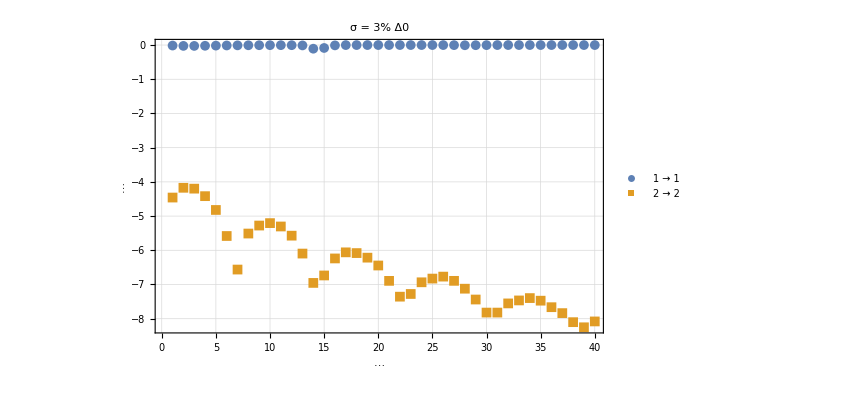

```mathematica
ListPlot[{gain3UCπ, loss3UCπ},PlotRange-> All,Frame->True,GridLines->Automatic, PlotLegends->Placed[{"1 → 1", "2 → 2"},{Right, Center}],PlotLabel->Style["σ = 3% Δ0",20], PlotMarkers->{Automatic,10},GridLinesStyle-> Thin, FrameLabel->{Style["",15],Style["(*GraphicsBox[{Thickness[0.017283097131005877`], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGI3IGYC4ur7P24Zcys68McG3DcqV3CA8ZWvPQpmmKPg
cPoMELxRcLijKbvm/2YFh7VCOnzp5xD8NVD+bSh/JgisRMiXHt7mOnOuAty8
Fd9eVpyZoOCwN7/m7cypCD5YX6eCw38QiIfKiyo4zACJW8o7uK85upzhh7RD
qwK76hkRWQg9RcwhIw0I2ETh/Aeu8Y6zCgXgfJDzz/Tww/n2JY61p2MQfNVP
Ki9nneRzCHl7+eOMhWIOMaoRMuf28Doo7FqwL3WdmEM6yPxlvA4gKu0Ygr8j
2Criv7o4nA/WVyPu8HXfx63p12DqxR1axGtZM9n4IPaZSDgwgECDqMPr4q2i
v7k1Ifa8E3UQ6fF6xfJFE+J+QTEHmXlxmqcNtBxEKieVnHWRgvPlQer7pOH8
A937mkweY/L1tVYKX1iC4EtMvcKZ8UgL4s4YBP88KHx0EHxwOFtIwfng+JCX
dPA5wW47+6qWQxUofWhLwPngcDguCOeD1d8XgPMh4cMPNw8WPjC+7xPPS6bC
CD4kvHgw+CycXfLJeQg+qn8R/ILlJRv++fPB+ZDwFMLgg935XxPOn9LeGnV5
j6bDfTQ+TB4cX92aUP8JOkiDzdN0kNkoNp/pAZvDm7bcbqPdEg5Lbi1/bMjM
5tAX0e3PKCDuEADy32VW1PTo888exn9T+zj7/JpfcH4zyH/HfmDwwfljpyic
b2IMAqIO66W36Z568xPOr3nR9Gvazr8IPii+Tss4wPiuoPi9IQvng9PXE1lI
unQQheY3OYh/pMUcum08d6V9UoCEi6KCQzinWLvxf2g+tUeUF8Igc1IQfFh5
AgCUldIw
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{14.435899999999998`, 8.57813}, {14.435899999999998`, 9.71094}, {13.696899999999998`, 10.5563}, {12.612499999999997`, 10.5563}, {11.0391, 10.5563}, {9.48906, 8.840629999999999}, {9.48906, 7.159379999999999}, {9.48906, 6.02656}, {10.2281, 5.1812499999999995`}, {11.3125, 5.1812499999999995`}, {12.898400000000002`, 5.1812499999999995`}, {14.435899999999998`, 6.8968799999999995`}, {14.435899999999998`, 8.57813}}, CompressedData["
1:eJxTTMoPSmViYGAQBmIQnZ4GBG7aDrc1Zdf8Z1ZygPHDOcXajfkVIfxjWg4i
lZNKzrLIOpw47LQ2856mQ4xqhMw5GSkHv4sTY/491nCouf/jlvFrMQfRHq9X
LFPUHc6AwBpRB5D2tGVqcH5m/ofWkyWqcL6RMRBMVnFoVWBXPTNFHM6HmCcF
50Psk3Vo4fVfP0VV1aH88DbXmX8VHKTmxWmevqDqsFZIhy9dT8nh19vXBywf
qzn4gtzFrOKw3aHp0XELDYefIPHFKg7GYKAJ54P9E6cF58P8HwHy/3plB/Tw
AQDksYAh
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}}, {{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAQBWIQ3e31isVkoZFDyNvLH2c4Sjvoa60UvjDFyGG9kA5f
ep2UQ/FW0d+n+4wczoCAj5RDI8vRfsN0I4cv+z5uTZ8m6cDtplrK9MrQoS+i
259RQNxhJghkGjrsCLaK+K8u5jB9An+VGTeCn54GBMsM4Pzk2DtuzB4GDiKV
k0rOpojD+fK7FuxLXScF54PtM5N1WHJ/H9+cxQYOqSBz3BQh5j0zcPiwaL3C
2QglhyeJC6+Z2Bs6RHCKtRuvV3bg918/JfWEocPPt68PWC5WgfA9jOD85S88
9P4LGsP5YPdbGjusBfl/nRKcD6Y7lRwK13TfzjAwdhAGuddEyQE9/ADhe49+

"], CompressedData["
1:eJxTTMoPSmViYGAwAmIQXbxV9Pfpc0YOwW8vf5zBKOTw51vpgzmKJg4RnGLt
xuuVHVSfNM87q2Xi4LHm6HKGHwi+1Lw4zdMCKjj5aWCg4qDxlnefAaeJQ8Nv
q4JzK1Qcpk/grzK7bQznL3/hofd/IoL/eUNA9qx0Y4cniQuvmeirOJw+7LQ2
M87YwWVCs1Bal7JDOshYM2OHC1fD3uhbqzh0e71iMXlo5DClvTXqsoyqA7//
+impHgj+Rr28xYx/DOD8H29fH7Bk1nf4sGi9wtkbinC+O8h/M2Tg/BBQeCwU
h4SHo4GDiTEIiDrclK5JNGI1hPOvC31yPL8MwYe4zwjKF3ewrYxYYZpr5LAj
2Criv7qEgzooPCyNHL7s+7g1/ZsInL9WSIcv/Z6IA7ebaimTlpFDjGqEzLk7
wpBw+G8IkbcThJj31tDh7Bkg4BGAyNcbOiy5tfyx4WEeSHgyGjrMmAkENzkc
IsS3X2ToM4Dz1UHx44XgnwCF7z19OD8V5H43fYczYPM5HdaDInStnkPJ8pIN
/85zOkiA4rlA34HHkc9rxkouB1ObvUHTFupD/BPGC+fv797XZJLMB+eD1b/k
d9jq0PToeAQ0vHcIOPjfAgboJT04/z8I2CP4D0AeWKDr0CJey5rZxg/nQ8zn
gfO3eW2wmFPJ4XAelC5m60HC/zMbJH0EGsD54PR5yxDOb2Q52m+43MjBvsSx
9vQdPgf0/AAA4EBVhA==
"]}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{23.579700000000003`, 2.3203099999999997`}, {23.579700000000003`, 2.7609399999999997`}, {22.4234, 2.7609399999999997`}, {22.4234, 13.799999999999997`}, {23.579700000000003`, 13.799999999999997`}, {23.579700000000003`, 14.240599999999999`}, {21.9828, 14.240599999999999`}, {21.9828, 2.3203099999999997`}, {23.579700000000003`, 2.3203099999999997`}}}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJZIGYC4hkzgeCkjYOJMQiIOsD4rQrsqmemiDmoPmme
dzYLwT9x2GltZpw1nH9DuibRKNTaYUewVcR/dXE4f62QDl/6PQk439xmb9C0
h5pwPgtnl3xynhacL9Lj9YqlRMuBx3/9lFQJBL9kq+jv0+esHJ4kLrxmcl7T
IT0NCMysHNaDHPZWw2GjXt5ixj8WGPzJ7a1Rl200HMSnXuHMcLKE89VB/rmF
4B9pWx5+qsnK4fzVsDf6txF8mPthfJj/wOFTaQX3v21lxArTXEs4/yQofPgw
+bDwlZ4Xp3k6wdKh6v6PW8beog71v60KznVYwfnPs7S/TX+L4IPdH2QN5zew
HO03LLeB89HjDwAjMb9b
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {{{40.773399999999995`, 8.27969}, {40.773399999999995`, 8.518749999999999}, {40.546899999999994`, 8.518749999999999}, {40.37969999999999, 8.518749999999999}, {33.882799999999996`, 8.518749999999999}, {33.715599999999995`, 8.518749999999999}, {33.4891, 8.518749999999999}, {33.4891, 8.27969}, {33.4891, 8.04219}, {33.715599999999995`, 8.04219}, {33.882799999999996`, 8.04219}, {40.37969999999999, 8.04219}, {40.546899999999994`, 8.04219}, {40.773399999999995`, 8.04219}, {40.773399999999995`, 8.27969}}}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJx11X0slHEcAPDzErOE0d3ZzJy4szvvLyHT9rXG81IbmcWkedudViiLeYmk
QiN1YZxLIitaM/rDREu1ZiyUpmxpi5ktwkQlee1+z8PvtzG/7fnjs+ee575v
v99jn3AhXGkgEAj0dFeC7tLXXT/bws5rM1nQqM1zfPfLoFceUN5fzcJVw547
nn4K7LiIcKd6RgFOk9frBrUshI3a5MaX7+0TfcZH731WgGFjeYBeGbGmRrfS
iFVo1VHY8W+HnZUFxI+naLfNtN2ufejQuZZE7K54YjXkqIABtHKJ09uFq/1V
xAcXgz6o/ux27qKuECtybC7/DuIOuDbRq5FDdlTz4cFfFGyilS+HyfiGEZ95
CiqKC6OHA+Vwi/1h6GNPwWxRSqnXC2tINvlXn2RFwe2o0lA9CzGYhrZWKi0o
KJQYSwcqRcCivB6FYIdIM/S1N4njUD2ydxuVsaZTiO3jjZaQj6eY2H+kJ8VH
TfxF1yavFuIslE9/COSMLY96HxfCldWAi++niLn3tVLYwSi+IeLt+my/7xKq
t4jGrlwyitU4Ej8t/XpW4Lfbkq76bqWZCHs7X7ughcQBV+Kipsh3XqbEXFsq
SD25+NS6fqL4Zogj5oYXNA1i7BZLF7Okb2L8vAAtsMbz8rt7oT2pyprv1zIF
kSaiYu/YQyBD811CY3P5bhBzc2HMgPmZsDGvv/bYSjTnIfY77kv4/bGPgbHg
2CBtg4TvzzoNl1H8NhIY6zar9V6hgSuXgQTyUH+WaShD89Rmt6e5+Ttth+Nz
WnSc1srt+HkxYbCPo/kTEnP9FjP4eUvUX1uGz89cwvcjg4Gpc85L1fel2Nz+
bJfy85/G8PtpVAp1gS6ftCpiLr4o4s7RknVlJAO+gS/Dq95sPX9y6370lj0Z
aF6azhpQO8DsgW6PGkuGr6O5A///ZTT2SkxKz4Y+sau6ftlTReP9+cwttVEv
nebPK0sFP2+ZND4PuHq0Ezeh86WAwc5H8QOLXYzmMYaFlbmZ10eOybHXlzLG
a+86YXPnUjIx/SrP1v+7DLjzN5LlzzNKBu4o3lMs9HU9LzPykMEayiechYko
ccfHcSk29/te4gJ0XlVLYR7VJ5oFDxTfDSm/vxOJH6B+pBJz+zOdxf3c+T34
D6pZmus=
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{55.44839999999999, 2.3203099999999997`}, {55.44839999999999, 14.240599999999999`}, {53.849999999999994`, 14.240599999999999`}, {53.849999999999994`, 13.799999999999997`}, {55.0063, 13.799999999999997`}, {55.0063, 2.7609399999999997`}, {53.849999999999994`, 2.7609399999999997`}, {53.849999999999994`, 2.3203099999999997`}, {55.44839999999999, 2.3203099999999997`}}}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{86.78978331257782, 24.508064757160646`},PlotRange->{{0., 57.86}, {0., 16.34}}])", 15]}, LabelStyle->{Bold,24}]
```

#### TD Error Analysis (φ=0 → w/ Imprecision)

```mathematica
Γ=1;
Δ0=499999/1000000Γ;
Ω0=1/2Γ;
φ=0;
ω=ωCirc1;
dir=1;
```

3%

```mathematica
σδΔ0=3/100 1/2 Γ;
NSamp=1000;
cinit={1,0};
cfinal={1,0};

t0Max=40/Γ;
t0min=1/Γ;
t0Steps=40;

AbsoluteTiming[gain3TD=ErrorAnalysisTD[Δ0,Ω0,Γ,φ,ω,dir,t0Max,t0min,t0Steps,σδΔ0,NSamp,cinit,cfinal];]
gain3TD
```

```mathematica
gain3TD={{1,-5.21880051604803361846729709366111065669`19.258927422120294},{2,-4.8012864192220881713300259039282014384`19.64023016056241},{3,-4.68010854848177334180823461798273800531`19.75030554246267},{4,-4.60346469965180222153270043197053074194`19.81976869933631},{5,-4.64007008785502732359518854022819442087`19.78661621427199},{6,-4.6777121734087186521591802419073006771`19.752465672996532},{7,-4.70192900332306717991269360017419694073`19.730492897947535},{8,-4.79956477205381840299652962037853019743`19.64179153848361},{9,-4.94230103379024366270172268418835618256`19.51177115035011},{10,-5.06563215110552577320367426192809108903`19.399153901299854},{11,-5.22961146490495877161869199353873691587`19.249008636444344},{12,-5.42478215508714687741786422327146234404`19.069751646410026},{13,-5.56173346087912908062202039949483121952`18.943630032612766},{14,-5.73803264202884849496436727425743141375`18.780883218925297},{15,-5.90052785061425080588097529818611885459`18.630517034519446},{16,-6.07844253924070689797719770042434407553`18.46550416330801},{17,-6.2385510364119266974794821243937459597`18.316687531270453},{18,-6.32693012916891250486295387013952316973`18.234417930404163},{19,-6.45300641987268680664787830846271111416`18.116910777521255},{20,-6.66002108021033409351014269522917908441`17.923609746074835},{21,-6.83359861948337479196078463205719208785`17.761206294090456},{22,-7.01266295691132924680616842946510645686`17.593375453016087},{23,-7.17510333123431686644561737481084893435`17.44088040112692},{24,-7.34727499248363783580295434220435094518`17.279006896115778},{25,-7.56335371322795872967585224074742381489`17.075516314149976},{26,-7.69209045044701175292628021992848323372`16.95410958999273},{27,-7.85986782941220646283129257418757003106`16.79570305976289},{28,-7.9678367074890607621778229125340596221`16.693659392760953},{29,-8.15164943453814612151415683412547326644`16.519751732170324},{30,-8.30983158921091573641898884601671354612`16.36991631433905},{31,-8.50882898178255015237659952993628374198`16.181196502914798},{32,-8.69085767417400650004948849168944421154`16.00836065196356},{33,-8.88380471951902037447155410660773065177`15.824949978046725},{34,-9.12198041624977115606549047934847535936`15.598264413239164},{35,-9.32163313169405506308600609966199936479`15.408014570670144},{36,-9.45051876789484571326292158722645508004`15.28509257682448},{37,-9.56111918355659658340383317408183737186`15.17954524451855},{38,-9.70209384686226763225054327624085455806`15.044927320999035},{39,-9.83032417901728093928061578938987686619`14.922399357502465},{40,-10.01275935013588179822704004450724688833`14.747950125146913}};
```

```mathematica
σδΔ0=3/100 1/2 Γ;
NSamp=1000;
cinit={0,1};
cfinal={0,1};

t0Max=40/Γ;
t0min=1/Γ;
t0Steps=40;

AbsoluteTiming[loss3TD=ErrorAnalysisTD[Δ0,Ω0,Γ,φ,ω,dir,t0Max,t0min,t0Steps,σδΔ0,NSamp,cinit,cfinal];]
loss3TD
```

```mathematica
loss3TD={{1,-4.85237136098943328945245948829970100301`19.59374196611586},{2,-4.0398173133808207974574487983774900914`20.326719148035675},{3,-3.5241380819139622066197841468117143735`20.783107674468575},{4,-3.04238000017235506326511224208928517694`21.200732128967022},{5,-2.68958865733097591093330388960732419827`21.500759211271564},{6,-2.36098420421698898750368355089109126531`21.769892763556545},{7,-2.05014676345742362932201307475777750869`22.017659308625444},{8,-1.73880116439721994007976174031953159702`22.25987781299884},{9,-1.5587912815744541475630973991589533264`22.366676779003996},{10,-1.32607856503588232175215724070208416577`22.545755882100632},{11,-1.11438130317170247293377385782740540532`22.639924432646264},{12,-0.92639698818870989023844086576885630711`22.71828724655638},{13,-0.82059112551949217018012804695900285956`22.804580820962194},{14,-0.68436014751914517011135844913121016857`22.74757414006478},{15,-0.53980413573980577100537133736049926368`22.895474164056687},{16,-0.44452295811060802990783328473949367143`22.77973331161547},{17,-0.33590486943221105299740393649874074606`22.894561391410793},{18,-0.26795829138682710755053575044912050949`22.837643591864115},{19,-0.21400028885528774408449395618148193221`22.74874768135979},{20,-0.15493161370142617155547620064030066066`22.98936830420157},{21,-0.12544262060820310806160760834873428532`22.665382643749503},{22,-0.09009852706098388686824593317109490143`22.890317039365055},{23,-0.08132798940403549932980678351086716628`22.731351435842413},{24,-0.06175285201519691962042508286547639042`22.706951428706738},{25,-0.05272813069162617963316964136828680925`22.842600364979333},{26,-0.03869048433607174304474603344573105477`22.599097012378376},{27,-0.03086225409253284667894911738579985312`23.123799809504725},{28,-0.02316730665110707367063636277791877691`22.56430556269145},{29,-0.01686563866363142514868371186938776476`22.768139035752526},{30,-0.01233737241043624150538481377319093773`22.701041649364353},{31,-0.01070301559354020968900099276340084542`22.516129053596},{32,-0.00850804665066182092807157352344814092`23.145758402689168},{33,-0.00690440534550806970415920984988720161`22.473699371747756},{34,-0.00538618497717332497154405621276252236`22.890109126896366},{35,-0.00601775508073373115980574956426963449`22.53613602361837},{36,-0.00274767176923188387769108530564685265`22.616451734358193},{37,-0.00304616057151609067418766472919620165`22.720294264539305},{38,-0.00298148385861441516448222070876035067`22.556692429755707},{39,-0.00159919637174204242884067111442442953`23.326820752722657},{40,-0.00116197131129759811780125458994288041`22.625492782373414}};
```

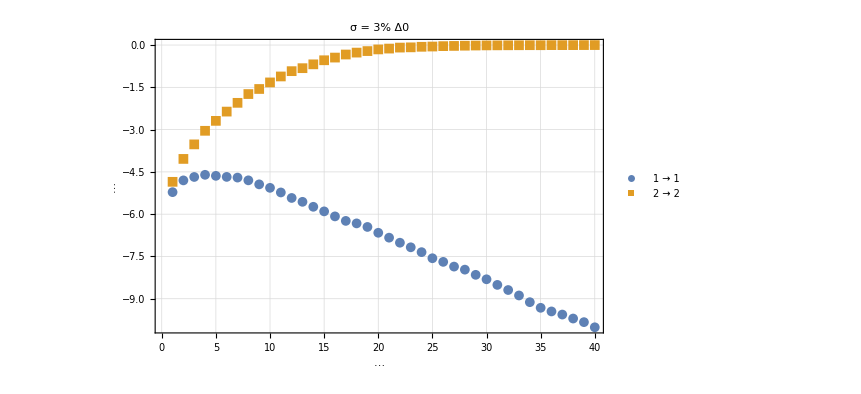

```mathematica
ListPlot[{gain3TD, loss3TD},PlotRange-> All,Frame->True,GridLines->Automatic, PlotLegends->Placed[{"1 → 1", "2 → 2"},{Right, Center}],PlotLabel->Style["σ = 3% Δ0",20], PlotMarkers->{Automatic,10},GridLinesStyle-> Thin, FrameLabel->{Style["",15],Style["(*GraphicsBox[{Thickness[0.017283097131005877`], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGI3IGYC4ur7P24Zcys68McG3DcqV3CA8ZWvPQpmmKPg
cPoMELxRcLijKbvm/2YFh7VCOnzp5xD8NVD+bSh/JgisRMiXHt7mOnOuAty8
Fd9eVpyZoOCwN7/m7cypCD5YX6eCw38QiIfKiyo4zACJW8o7uK85upzhh7RD
qwK76hkRWQg9RcwhIw0I2ETh/Aeu8Y6zCgXgfJDzz/Tww/n2JY61p2MQfNVP
Ki9nneRzCHl7+eOMhWIOMaoRMuf28Doo7FqwL3WdmEM6yPxlvA4gKu0Ygr8j
2Criv7o4nA/WVyPu8HXfx63p12DqxR1axGtZM9n4IPaZSDgwgECDqMPr4q2i
v7k1Ifa8E3UQ6fF6xfJFE+J+QTEHmXlxmqcNtBxEKieVnHWRgvPlQer7pOH8
A937mkweY/L1tVYKX1iC4EtMvcKZ8UgL4s4YBP88KHx0EHxwOFtIwfng+JCX
dPA5wW47+6qWQxUofWhLwPngcDguCOeD1d8XgPMh4cMPNw8WPjC+7xPPS6bC
CD4kvHgw+CycXfLJeQg+qn8R/ILlJRv++fPB+ZDwFMLgg935XxPOn9LeGnV5
j6bDfTQ+TB4cX92aUP8JOkiDzdN0kNkoNp/pAZvDm7bcbqPdEg5Lbi1/bMjM
5tAX0e3PKCDuEADy32VW1PTo888exn9T+zj7/JpfcH4zyH/HfmDwwfljpyic
b2IMAqIO66W36Z568xPOr3nR9Gvazr8IPii+Tss4wPiuoPi9IQvng9PXE1lI
unQQheY3OYh/pMUcum08d6V9UoCEi6KCQzinWLvxf2g+tUeUF8Igc1IQfFh5
AgCUldIw
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{14.435899999999998`, 8.57813}, {14.435899999999998`, 9.71094}, {13.696899999999998`, 10.5563}, {12.612499999999997`, 10.5563}, {11.0391, 10.5563}, {9.48906, 8.840629999999999}, {9.48906, 7.159379999999999}, {9.48906, 6.02656}, {10.2281, 5.1812499999999995`}, {11.3125, 5.1812499999999995`}, {12.898400000000002`, 5.1812499999999995`}, {14.435899999999998`, 6.8968799999999995`}, {14.435899999999998`, 8.57813}}, CompressedData["
1:eJxTTMoPSmViYGAQBmIQnZ4GBG7aDrc1Zdf8Z1ZygPHDOcXajfkVIfxjWg4i
lZNKzrLIOpw47LQ2856mQ4xqhMw5GSkHv4sTY/491nCouf/jlvFrMQfRHq9X
LFPUHc6AwBpRB5D2tGVqcH5m/ofWkyWqcL6RMRBMVnFoVWBXPTNFHM6HmCcF
50Psk3Vo4fVfP0VV1aH88DbXmX8VHKTmxWmevqDqsFZIhy9dT8nh19vXBywf
qzn4gtzFrOKw3aHp0XELDYefIPHFKg7GYKAJ54P9E6cF58P8HwHy/3plB/Tw
AQDksYAh
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}}, {{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAQBWIQ3e31isVkoZFDyNvLH2c4Sjvoa60UvjDFyGG9kA5f
ep2UQ/FW0d+n+4wczoCAj5RDI8vRfsN0I4cv+z5uTZ8m6cDtplrK9MrQoS+i
259RQNxhJghkGjrsCLaK+K8u5jB9An+VGTeCn54GBMsM4Pzk2DtuzB4GDiKV
k0rOpojD+fK7FuxLXScF54PtM5N1WHJ/H9+cxQYOqSBz3BQh5j0zcPiwaL3C
2QglhyeJC6+Z2Bs6RHCKtRuvV3bg918/JfWEocPPt68PWC5WgfA9jOD85S88
9P4LGsP5YPdbGjusBfl/nRKcD6Y7lRwK13TfzjAwdhAGuddEyQE9/ADhe49+

"], CompressedData["
1:eJxTTMoPSmViYGAwAmIQXbxV9Pfpc0YOwW8vf5zBKOTw51vpgzmKJg4RnGLt
xuuVHVSfNM87q2Xi4LHm6HKGHwi+1Lw4zdMCKjj5aWCg4qDxlnefAaeJQ8Nv
q4JzK1Qcpk/grzK7bQznL3/hofd/IoL/eUNA9qx0Y4cniQuvmeirOJw+7LQ2
M87YwWVCs1Bal7JDOshYM2OHC1fD3uhbqzh0e71iMXlo5DClvTXqsoyqA7//
+impHgj+Rr28xYx/DOD8H29fH7Bk1nf4sGi9wtkbinC+O8h/M2Tg/BBQeCwU
h4SHo4GDiTEIiDrclK5JNGI1hPOvC31yPL8MwYe4zwjKF3ewrYxYYZpr5LAj
2Criv7qEgzooPCyNHL7s+7g1/ZsInL9WSIcv/Z6IA7ebaimTlpFDjGqEzLk7
wpBw+G8IkbcThJj31tDh7Bkg4BGAyNcbOiy5tfyx4WEeSHgyGjrMmAkENzkc
IsS3X2ToM4Dz1UHx44XgnwCF7z19OD8V5H43fYczYPM5HdaDInStnkPJ8pIN
/85zOkiA4rlA34HHkc9rxkouB1ObvUHTFupD/BPGC+fv797XZJLMB+eD1b/k
d9jq0PToeAQ0vHcIOPjfAgboJT04/z8I2CP4D0AeWKDr0CJey5rZxg/nQ8zn
gfO3eW2wmFPJ4XAelC5m60HC/zMbJH0EGsD54PR5yxDOb2Q52m+43MjBvsSx
9vQdPgf0/AAA4EBVhA==
"]}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{23.579700000000003`, 2.3203099999999997`}, {23.579700000000003`, 2.7609399999999997`}, {22.4234, 2.7609399999999997`}, {22.4234, 13.799999999999997`}, {23.579700000000003`, 13.799999999999997`}, {23.579700000000003`, 14.240599999999999`}, {21.9828, 14.240599999999999`}, {21.9828, 2.3203099999999997`}, {23.579700000000003`, 2.3203099999999997`}}}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJZIGYC4hkzgeCkjYOJMQiIOsD4rQrsqmemiDmoPmme
dzYLwT9x2GltZpw1nH9DuibRKNTaYUewVcR/dXE4f62QDl/6PQk439xmb9C0
h5pwPgtnl3xynhacL9Lj9YqlRMuBx3/9lFQJBL9kq+jv0+esHJ4kLrxmcl7T
IT0NCMysHNaDHPZWw2GjXt5ixj8WGPzJ7a1Rl200HMSnXuHMcLKE89VB/rmF
4B9pWx5+qsnK4fzVsDf6txF8mPthfJj/wOFTaQX3v21lxArTXEs4/yQofPgw
+bDwlZ4Xp3k6wdKh6v6PW8beog71v60KznVYwfnPs7S/TX+L4IPdH2QN5zew
HO03LLeB89HjDwAjMb9b
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {{{40.773399999999995`, 8.27969}, {40.773399999999995`, 8.518749999999999}, {40.546899999999994`, 8.518749999999999}, {40.37969999999999, 8.518749999999999}, {33.882799999999996`, 8.518749999999999}, {33.715599999999995`, 8.518749999999999}, {33.4891, 8.518749999999999}, {33.4891, 8.27969}, {33.4891, 8.04219}, {33.715599999999995`, 8.04219}, {33.882799999999996`, 8.04219}, {40.37969999999999, 8.04219}, {40.546899999999994`, 8.04219}, {40.773399999999995`, 8.04219}, {40.773399999999995`, 8.27969}}}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJx11X0slHEcAPDzErOE0d3ZzJy4szvvLyHT9rXG81IbmcWkedudViiLeYmk
QiN1YZxLIitaM/rDREu1ZiyUpmxpi5ktwkQlee1+z8PvtzG/7fnjs+ee575v
v99jn3AhXGkgEAj0dFeC7tLXXT/bws5rM1nQqM1zfPfLoFceUN5fzcJVw547
nn4K7LiIcKd6RgFOk9frBrUshI3a5MaX7+0TfcZH731WgGFjeYBeGbGmRrfS
iFVo1VHY8W+HnZUFxI+naLfNtN2ufejQuZZE7K54YjXkqIABtHKJ09uFq/1V
xAcXgz6o/ux27qKuECtybC7/DuIOuDbRq5FDdlTz4cFfFGyilS+HyfiGEZ95
CiqKC6OHA+Vwi/1h6GNPwWxRSqnXC2tINvlXn2RFwe2o0lA9CzGYhrZWKi0o
KJQYSwcqRcCivB6FYIdIM/S1N4njUD2ydxuVsaZTiO3jjZaQj6eY2H+kJ8VH
TfxF1yavFuIslE9/COSMLY96HxfCldWAi++niLn3tVLYwSi+IeLt+my/7xKq
t4jGrlwyitU4Ej8t/XpW4Lfbkq76bqWZCHs7X7ughcQBV+Kipsh3XqbEXFsq
SD25+NS6fqL4Zogj5oYXNA1i7BZLF7Okb2L8vAAtsMbz8rt7oT2pyprv1zIF
kSaiYu/YQyBD811CY3P5bhBzc2HMgPmZsDGvv/bYSjTnIfY77kv4/bGPgbHg
2CBtg4TvzzoNl1H8NhIY6zar9V6hgSuXgQTyUH+WaShD89Rmt6e5+Ttth+Nz
WnSc1srt+HkxYbCPo/kTEnP9FjP4eUvUX1uGz89cwvcjg4Gpc85L1fel2Nz+
bJfy85/G8PtpVAp1gS6ftCpiLr4o4s7RknVlJAO+gS/Dq95sPX9y6370lj0Z
aF6azhpQO8DsgW6PGkuGr6O5A///ZTT2SkxKz4Y+sau6ftlTReP9+cwttVEv
nebPK0sFP2+ZND4PuHq0Ezeh86WAwc5H8QOLXYzmMYaFlbmZ10eOybHXlzLG
a+86YXPnUjIx/SrP1v+7DLjzN5LlzzNKBu4o3lMs9HU9LzPykMEayiechYko
ccfHcSk29/te4gJ0XlVLYR7VJ5oFDxTfDSm/vxOJH6B+pBJz+zOdxf3c+T34
D6pZmus=
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{55.44839999999999, 2.3203099999999997`}, {55.44839999999999, 14.240599999999999`}, {53.849999999999994`, 14.240599999999999`}, {53.849999999999994`, 13.799999999999997`}, {55.0063, 13.799999999999997`}, {55.0063, 2.7609399999999997`}, {53.849999999999994`, 2.7609399999999997`}, {53.849999999999994`, 2.3203099999999997`}, {55.44839999999999, 2.3203099999999997`}}}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{86.78978331257782, 24.508064757160646`},PlotRange->{{0., 57.86}, {0., 16.34}}])", 15]}, LabelStyle->{Bold,24}]
```

#### TD Error Analysis (φ=π → w/ Imprecision)

```mathematica
Γ=1;
Δ0=499999/1000000Γ;
Ω0=1/2Γ;
φ=π-10^-16;
ω=ωCirc1;
dir=1;
```

3%

```mathematica
σδΔ0=3/100 1/2 Γ;
NSamp=1000;
cinit={1,0};
cfinal={1,0};

t0Max=20/Γ;
t0min=1/Γ;
t0Steps=40;

AbsoluteTiming[gain3TDπ=ErrorAnalysisTD[Δ0,Ω0,Γ,φ,ω,dir,t0Max,t0min,t0Steps,σδΔ0,NSamp,cinit,cfinal];]
gain3TDπ
```

```mathematica
gain3TDπ={{1,-3.96516353503859890316136788521556554847`20.21726993421635},{58/39,-3.51396696335367704578301842065886657788`20.550753291557697},{77/39,-3.15162282667890153653240586196760167035`20.809231808070273},{32/13,-2.89933121487964092404544455154423176418`20.975314649015832},{115/39,-2.62760978403825536527449791080277164102`21.159784595509876},{134/39,-2.42789409473425337494359635118119800315`21.2849946211372},{51/13,-2.24000531151586925232764376110328955525`21.40151717195096},{172/39,-2.09711932676647388844291156323506674386`21.482429364740735},{191/39,-1.93249407122150844597265223564504013409`21.58136491136073},{70/13,-1.8528659821568786305483655071649210654`21.614102232625694},{229/39,-1.74222794168750768198740040923315457449`21.672056048833916},{248/39,-1.65319908172702466523121808961290599382`21.714051820792616},{89/13,-1.54349227283582126026990867638598238898`21.772195636944712},{22/3,-1.4807424861442264193909596330975269965`21.79563396495672},{305/39,-1.44432399572473017128767291841907805463`21.8004392824209},{108/13,-1.44535829705513714412823362404326904597`21.778644019411903},{343/39,-1.38215662136917502458589633443805707171`21.804924761599274},{362/39,-1.41935289847282856060126315259097058323`21.758547615450468},{127/13,-1.44148149226601556730306437946844464479`21.72393504386923},{400/39,-1.53926803216043372667684122677580877086`21.633763484014406},{419/39,-1.68971676931620130492730538985584629972`21.50311803468867},{146/13,-1.85584851355242214235774118790155926023`21.358549056167913},{457/39,-2.06146029149196445140514004793449733187`21.180561917618114},{476/39,-2.05983757402312153509363214446342484449`21.16669546678762},{165/13,-1.7325598449285639332909194504119971609`21.408495343983343},{514/39,-1.36715149687528295081512208217486640469`21.667817178468997},{41/3,-1.07277485654404254865739303035680660609`21.86247806670415},{184/13,-0.89612095344738439882547086602203335582`21.968292908052682},{571/39,-0.71947398731940917214943925260897905639`22.069604709689365},{590/39,-0.5900013666255457915501679303606830733`22.137469620738955},{203/13,-0.48295240805290442392612484738955148188`22.189551769650045},{628/39,-0.41221094438979326737681288620980071938`22.2190338913149},{647/39,-0.35684787991896672389144481607739426226`22.23920466800204},{222/13,-0.32224500639734511010946132453902165976`22.247492520146118},{685/39,-0.29185148367750504499578092527473356678`22.253506484867845},{704/39,-0.26319068068194806900297441878463650493`22.25866637634315},{241/13,-0.24733535933016959352413760723644636028`22.256935125307578},{742/39,-0.2316982893743757645306111479438648701`22.25528521466497},{761/39,-0.20778890848269616823865217427324480433`22.258297502704213},{20,-0.21069137476289398417706596153250201931`22.247000048010577}};
```

```mathematica
σδΔ0=3/100 1/2 Γ;
NSamp=1000;
cinit={0,1};
cfinal={0,1};

t0Max=20/Γ;
t0min=1/Γ;
t0Steps=40;

AbsoluteTiming[loss3TDπ=ErrorAnalysisTD[Δ0,Ω0,Γ,φ,ω,dir,t0Max,t0min,t0Steps,σδΔ0,NSamp,cinit,cfinal];]
loss3TDπ
```

```mathematica
loss3TDπ={{1,-4.436636837256906401292755837157815857`19.79456526265423},{58/39,-4.22612419668667096691491996322888251223`19.918644805883293},{77/39,-4.18005406859329794785931709677500448657`19.903172278213766},{32/13,-4.15298862675658162205742009216400165286`19.877213114965997},{115/39,-4.21070400825539025899414613895036711636`19.78048324162125},{134/39,-4.24531207499681966012287410759289695463`19.70866839865719},{51/13,-4.40674800821900079489358111364051415061`19.52615056107844},{172/39,-4.54423399450605305750031057425887805411`19.367687243273156},{191/39,-4.77165023284108537183497729418134903686`19.12966314031229},{70/13,-5.05492606159379087592917635988960775477`18.841794427716763},{229/39,-5.4474523571416476810277859454257364204`18.45400110083072},{248/39,-6.12472257601465682711642894419034223345`17.8015437458813},{89/13,-6.83441259577139606210397945455385931297`17.11486772640942},{22/3,-6.03389601562215543799199650429588884637`17.838012971888087},{305/39,-5.61445407427326141927984473212619486635`18.204060030545133},{108/13,-5.39939117209579392435652879477992131779`18.38113686086719},{343/39,-5.25061005573503242171297292265521074356`18.497739593322006},{362/39,-5.19552436822128844446279312358669585218`18.529068901766372},{127/13,-5.18988005193509340587678954775723166849`18.51588416450995},{400/39,-5.22202697100603878062354144138777530975`18.468802828593887},{419/39,-5.30144680168359633136692015425703613284`18.379001843800218},{146/13,-5.36277872899538558724763499881493337108`18.306384638352018},{457/39,-5.50587206044398534367304485534968600851`18.159018709703222},{476/39,-5.65459389522571633471871836019907331308`18.006718962319482},{165/13,-5.87405913609917495484700401527571669423`17.789149640488112},{514/39,-6.15499112320051555810040116312624715492`17.51433855901633},{41/3,-6.6040027885763427745296616363695206789`17.082178224099927},{184/13,-7.12238950279842841606115497998343941273`16.583299820606424},{571/39,-6.99057782719482930734639819653676518367`16.694112082701857},{590/39,-6.72996891503221713049513717798646653592`16.925674495969723},{203/13,-6.42399878575476403962841002361806474765`17.199279108070023},{628/39,-6.2141227101333804210637167630537525629`17.382882022565934},{647/39,-6.1109771164710626420679021438537115891`17.467224560407807},{222/13,-6.07154300551554719654723663358234209635`17.49261544668854},{685/39,-6.03064566528637042676160069779523322955`17.519629367778176},{704/39,-6.07174206649622241591009548465483390138`17.470793017210443},{241/13,-6.13068951657056670522840804882962548721`17.405609928026923},{742/39,-6.21382138841657465249513167695802531291`17.318146143325993},{761/39,-6.32004396808159659198990044262833791105`17.209339301577373},{20,-6.44267841678852304857058321334185387638`17.08532757218663}};
```

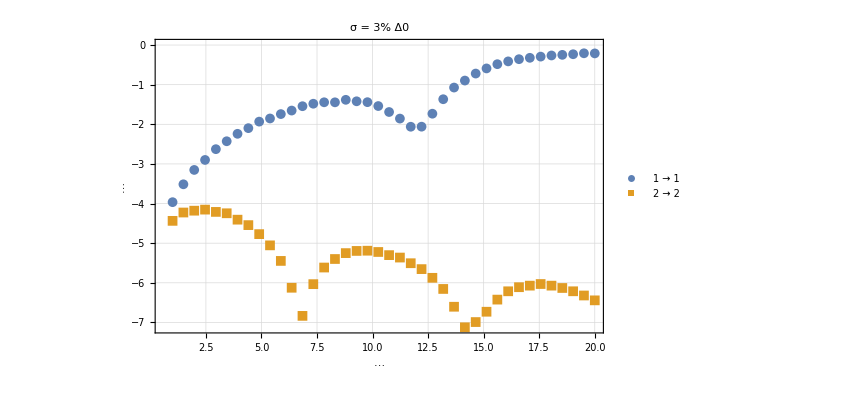

```mathematica
ListPlot[{gain3TDπ, loss3TDπ},PlotRange-> All,Frame->True,GridLines->Automatic, PlotLegends->Placed[{"1 → 1", "2 → 2"},{Right, Center}],PlotLabel->Style["σ = 3% Δ0",20], PlotMarkers->{Automatic,10},GridLinesStyle-> Thin, FrameLabel->{Style["",15],Style["(*GraphicsBox[{Thickness[0.017283097131005877`], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGI3IGYC4ur7P24Zcys68McG3DcqV3CA8ZWvPQpmmKPg
cPoMELxRcLijKbvm/2YFh7VCOnzp5xD8NVD+bSh/JgisRMiXHt7mOnOuAty8
Fd9eVpyZoOCwN7/m7cypCD5YX6eCw38QiIfKiyo4zACJW8o7uK85upzhh7RD
qwK76hkRWQg9RcwhIw0I2ETh/Aeu8Y6zCgXgfJDzz/Tww/n2JY61p2MQfNVP
Ki9nneRzCHl7+eOMhWIOMaoRMuf28Doo7FqwL3WdmEM6yPxlvA4gKu0Ygr8j
2Criv7o4nA/WVyPu8HXfx63p12DqxR1axGtZM9n4IPaZSDgwgECDqMPr4q2i
v7k1Ifa8E3UQ6fF6xfJFE+J+QTEHmXlxmqcNtBxEKieVnHWRgvPlQer7pOH8
A937mkweY/L1tVYKX1iC4EtMvcKZ8UgL4s4YBP88KHx0EHxwOFtIwfng+JCX
dPA5wW47+6qWQxUofWhLwPngcDguCOeD1d8XgPMh4cMPNw8WPjC+7xPPS6bC
CD4kvHgw+CycXfLJeQg+qn8R/ILlJRv++fPB+ZDwFMLgg935XxPOn9LeGnV5
j6bDfTQ+TB4cX92aUP8JOkiDzdN0kNkoNp/pAZvDm7bcbqPdEg5Lbi1/bMjM
5tAX0e3PKCDuEADy32VW1PTo888exn9T+zj7/JpfcH4zyH/HfmDwwfljpyic
b2IMAqIO66W36Z568xPOr3nR9Gvazr8IPii+Tss4wPiuoPi9IQvng9PXE1lI
unQQheY3OYh/pMUcum08d6V9UoCEi6KCQzinWLvxf2g+tUeUF8Igc1IQfFh5
AgCUldIw
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{14.435899999999998`, 8.57813}, {14.435899999999998`, 9.71094}, {13.696899999999998`, 10.5563}, {12.612499999999997`, 10.5563}, {11.0391, 10.5563}, {9.48906, 8.840629999999999}, {9.48906, 7.159379999999999}, {9.48906, 6.02656}, {10.2281, 5.1812499999999995`}, {11.3125, 5.1812499999999995`}, {12.898400000000002`, 5.1812499999999995`}, {14.435899999999998`, 6.8968799999999995`}, {14.435899999999998`, 8.57813}}, CompressedData["
1:eJxTTMoPSmViYGAQBmIQnZ4GBG7aDrc1Zdf8Z1ZygPHDOcXajfkVIfxjWg4i
lZNKzrLIOpw47LQ2856mQ4xqhMw5GSkHv4sTY/491nCouf/jlvFrMQfRHq9X
LFPUHc6AwBpRB5D2tGVqcH5m/ofWkyWqcL6RMRBMVnFoVWBXPTNFHM6HmCcF
50Psk3Vo4fVfP0VV1aH88DbXmX8VHKTmxWmevqDqsFZIhy9dT8nh19vXBywf
qzn4gtzFrOKw3aHp0XELDYefIPHFKg7GYKAJ54P9E6cF58P8HwHy/3plB/Tw
AQDksYAh
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}}, {{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAQBWIQ3e31isVkoZFDyNvLH2c4Sjvoa60UvjDFyGG9kA5f
ep2UQ/FW0d+n+4wczoCAj5RDI8vRfsN0I4cv+z5uTZ8m6cDtplrK9MrQoS+i
259RQNxhJghkGjrsCLaK+K8u5jB9An+VGTeCn54GBMsM4Pzk2DtuzB4GDiKV
k0rOpojD+fK7FuxLXScF54PtM5N1WHJ/H9+cxQYOqSBz3BQh5j0zcPiwaL3C
2QglhyeJC6+Z2Bs6RHCKtRuvV3bg918/JfWEocPPt68PWC5WgfA9jOD85S88
9P4LGsP5YPdbGjusBfl/nRKcD6Y7lRwK13TfzjAwdhAGuddEyQE9/ADhe49+

"], CompressedData["
1:eJxTTMoPSmViYGAwAmIQXbxV9Pfpc0YOwW8vf5zBKOTw51vpgzmKJg4RnGLt
xuuVHVSfNM87q2Xi4LHm6HKGHwi+1Lw4zdMCKjj5aWCg4qDxlnefAaeJQ8Nv
q4JzK1Qcpk/grzK7bQznL3/hofd/IoL/eUNA9qx0Y4cniQuvmeirOJw+7LQ2
M87YwWVCs1Bal7JDOshYM2OHC1fD3uhbqzh0e71iMXlo5DClvTXqsoyqA7//
+impHgj+Rr28xYx/DOD8H29fH7Bk1nf4sGi9wtkbinC+O8h/M2Tg/BBQeCwU
h4SHo4GDiTEIiDrclK5JNGI1hPOvC31yPL8MwYe4zwjKF3ewrYxYYZpr5LAj
2Criv7qEgzooPCyNHL7s+7g1/ZsInL9WSIcv/Z6IA7ebaimTlpFDjGqEzLk7
wpBw+G8IkbcThJj31tDh7Bkg4BGAyNcbOiy5tfyx4WEeSHgyGjrMmAkENzkc
IsS3X2ToM4Dz1UHx44XgnwCF7z19OD8V5H43fYczYPM5HdaDInStnkPJ8pIN
/85zOkiA4rlA34HHkc9rxkouB1ObvUHTFupD/BPGC+fv797XZJLMB+eD1b/k
d9jq0PToeAQ0vHcIOPjfAgboJT04/z8I2CP4D0AeWKDr0CJey5rZxg/nQ8zn
gfO3eW2wmFPJ4XAelC5m60HC/zMbJH0EGsD54PR5yxDOb2Q52m+43MjBvsSx
9vQdPgf0/AAA4EBVhA==
"]}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{23.579700000000003`, 2.3203099999999997`}, {23.579700000000003`, 2.7609399999999997`}, {22.4234, 2.7609399999999997`}, {22.4234, 13.799999999999997`}, {23.579700000000003`, 13.799999999999997`}, {23.579700000000003`, 14.240599999999999`}, {21.9828, 14.240599999999999`}, {21.9828, 2.3203099999999997`}, {23.579700000000003`, 2.3203099999999997`}}}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJZIGYC4hkzgeCkjYOJMQiIOsD4rQrsqmemiDmoPmme
dzYLwT9x2GltZpw1nH9DuibRKNTaYUewVcR/dXE4f62QDl/6PQk439xmb9C0
h5pwPgtnl3xynhacL9Lj9YqlRMuBx3/9lFQJBL9kq+jv0+esHJ4kLrxmcl7T
IT0NCMysHNaDHPZWw2GjXt5ixj8WGPzJ7a1Rl200HMSnXuHMcLKE89VB/rmF
4B9pWx5+qsnK4fzVsDf6txF8mPthfJj/wOFTaQX3v21lxArTXEs4/yQofPgw
+bDwlZ4Xp3k6wdKh6v6PW8beog71v60KznVYwfnPs7S/TX+L4IPdH2QN5zew
HO03LLeB89HjDwAjMb9b
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {{{40.773399999999995`, 8.27969}, {40.773399999999995`, 8.518749999999999}, {40.546899999999994`, 8.518749999999999}, {40.37969999999999, 8.518749999999999}, {33.882799999999996`, 8.518749999999999}, {33.715599999999995`, 8.518749999999999}, {33.4891, 8.518749999999999}, {33.4891, 8.27969}, {33.4891, 8.04219}, {33.715599999999995`, 8.04219}, {33.882799999999996`, 8.04219}, {40.37969999999999, 8.04219}, {40.546899999999994`, 8.04219}, {40.773399999999995`, 8.04219}, {40.773399999999995`, 8.27969}}}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJx11X0slHEcAPDzErOE0d3ZzJy4szvvLyHT9rXG81IbmcWkedudViiLeYmk
QiN1YZxLIitaM/rDREu1ZiyUpmxpi5ktwkQlee1+z8PvtzG/7fnjs+ee575v
v99jn3AhXGkgEAj0dFeC7tLXXT/bws5rM1nQqM1zfPfLoFceUN5fzcJVw547
nn4K7LiIcKd6RgFOk9frBrUshI3a5MaX7+0TfcZH731WgGFjeYBeGbGmRrfS
iFVo1VHY8W+HnZUFxI+naLfNtN2ufejQuZZE7K54YjXkqIABtHKJ09uFq/1V
xAcXgz6o/ux27qKuECtybC7/DuIOuDbRq5FDdlTz4cFfFGyilS+HyfiGEZ95
CiqKC6OHA+Vwi/1h6GNPwWxRSqnXC2tINvlXn2RFwe2o0lA9CzGYhrZWKi0o
KJQYSwcqRcCivB6FYIdIM/S1N4njUD2ydxuVsaZTiO3jjZaQj6eY2H+kJ8VH
TfxF1yavFuIslE9/COSMLY96HxfCldWAi++niLn3tVLYwSi+IeLt+my/7xKq
t4jGrlwyitU4Ej8t/XpW4Lfbkq76bqWZCHs7X7ughcQBV+Kipsh3XqbEXFsq
SD25+NS6fqL4Zogj5oYXNA1i7BZLF7Okb2L8vAAtsMbz8rt7oT2pyprv1zIF
kSaiYu/YQyBD811CY3P5bhBzc2HMgPmZsDGvv/bYSjTnIfY77kv4/bGPgbHg
2CBtg4TvzzoNl1H8NhIY6zar9V6hgSuXgQTyUH+WaShD89Rmt6e5+Ttth+Nz
WnSc1srt+HkxYbCPo/kTEnP9FjP4eUvUX1uGz89cwvcjg4Gpc85L1fel2Nz+
bJfy85/G8PtpVAp1gS6ftCpiLr4o4s7RknVlJAO+gS/Dq95sPX9y6370lj0Z
aF6azhpQO8DsgW6PGkuGr6O5A///ZTT2SkxKz4Y+sau6ftlTReP9+cwttVEv
nebPK0sFP2+ZND4PuHq0Ezeh86WAwc5H8QOLXYzmMYaFlbmZ10eOybHXlzLG
a+86YXPnUjIx/SrP1v+7DLjzN5LlzzNKBu4o3lMs9HU9LzPykMEayiechYko
ccfHcSk29/te4gJ0XlVLYR7VJ5oFDxTfDSm/vxOJH6B+pBJz+zOdxf3c+T34
D6pZmus=
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{55.44839999999999, 2.3203099999999997`}, {55.44839999999999, 14.240599999999999`}, {53.849999999999994`, 14.240599999999999`}, {53.849999999999994`, 13.799999999999997`}, {55.0063, 13.799999999999997`}, {55.0063, 2.7609399999999997`}, {53.849999999999994`, 2.7609399999999997`}, {53.849999999999994`, 2.3203099999999997`}, {55.44839999999999, 2.3203099999999997`}}}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{86.78978331257782, 24.508064757160646`},PlotRange->{{0., 57.86}, {0., 16.34}}])", 15]}, LabelStyle->{Bold,24}]
```

10%

```mathematica
σδΔ0=10/100 1/2 Γ;
NSamp=1000;
cinit={1,0};
cfinal={1,0};

t0Max=40/Γ;
t0min=1/Γ;
t0Steps=40;

AbsoluteTiming[gain10TDπ=ErrorAnalysisTD[Δ0,Ω0,Γ,φ,ω,dir,t0Max,t0min,t0Steps,σδΔ0,NSamp,cinit,cfinal];]
gain10TDπ
```

{3541.88,Null}

{{1,-2.88222769095319622663},{2,-2.07362877571059537377},{3,-1.61011339204149808904},{4,-1.258908825600237789604},{5,-1.004989200700978545761},{6,-0.8346226905933421131116},{7,-0.7255611846575786699803},{8,-0.666320462823637115367},{9,-0.680748811239495071316},{10,-0.7039302256946475240279},{11,-0.7867488585669878327496},{12,-0.6791249687221441916832},{13,-0.5614334710105844670161},{14,-0.4667043729836875983562},{15,-0.282041331871062947339},{16,-0.1663630278505550975286},{17,-0.1165690301163228736115},{18,-0.09161726648458410702873},{19,-0.08005084644465104846696},{20,-0.0786638517520889941608},{21,-0.09630891808568450857448},{22,-0.1151692075822623459626},{23,-0.1526879172845604933084},{24,-0.1199661309082688298245},{25,-0.1170131645812292443729},{26,-0.0648138416987535211084},{27,-0.0392129314857535838608},{28,-0.02214210496508889881478},{29,-0.01518708952814714087317},{30,-0.01141947990655472671795},{31,-0.009747659171835349124269},{32,-0.01202046031358860248781},{33,-0.01062164044738595845621},{34,-0.01066755242172346821613},{35,-0.01929127884178009914981},{36,-0.0336225736598973696962},{37,-0.02895289950463238532945},{38,-0.01021511658570149011352},{39,-0.006223586362853349245046},{40,-0.00306078135946463602969}}

```mathematica
σδΔ0=10/100 1/2 Γ;
NSamp=1000;
cinit={0,1};
cfinal={0,1};

t0Max=40/Γ;
t0min=1/Γ;
t0Steps=40;

AbsoluteTiming[loss10TDπ=ErrorAnalysisTD[Δ0,Ω0,Γ,φ,ω,dir,t0Max,t0min,t0Steps,σδΔ0,NSamp,cinit,cfinal];]
loss10TDπ
```

{3206.52,Null}

{{1,-3.3552548057368411179},{2,-3.1271509476543317672},{3,-3.1495235397872094165},{4,-3.3620800093252657298},{5,-3.804071930667038473},{6,-4.369938431326107268},{7,-4.677476197592241917},{8,-4.263558121885420886},{9,-4.168946655185828545},{10,-4.165034198407589184},{11,-4.373575835118969811},{12,-4.62825016388595007},{13,-4.96619516495325804},{14,-5.02086971053325807},{15,-4.92316148319945501},{16,-4.97357498308200147},{17,-5.05538666758845193},{18,-5.20167928997251381},{19,-5.43614960268778843},{20,-5.5389496718218862},{21,-5.566152196330663},{22,-5.4755130980772144},{23,-5.5042416100680579},{24,-5.7110671895633533},{25,-5.8755763302625949},{26,-6.0969363853913451},{27,-6.2077608326114695},{28,-6.2007684500669243},{29,-6.0856726306276981},{30,-6.1176876568021633},{31,-6.1311396221351432},{32,-6.3187450926667584},{33,-6.540000889941205},{34,-6.757101075442614},{35,-6.794655838682073},{36,-6.704049400828214},{37,-6.62177976646486},{38,-6.639570084973691},{39,-6.701801921612376},{40,-6.858529699444217}}

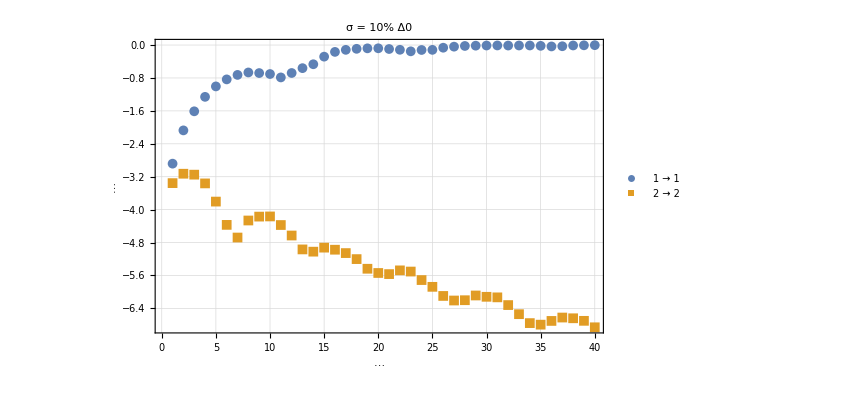

```mathematica
ListPlot[{gain10TDπ, loss10TDπ},PlotRange-> All,Frame->True,GridLines->Automatic, PlotLegends->Placed[{"1 → 1", "2 → 2"},{Right, Center}],PlotLabel->Style["σ = 10% Δ0",20], PlotMarkers->{Automatic,10},GridLinesStyle-> Thin, FrameLabel->{Style["",15],Style["(*GraphicsBox[{Thickness[0.017283097131005877`], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGI3IGYC4ur7P24Zcys68McG3DcqV3CA8ZWvPQpmmKPg
cPoMELxRcLijKbvm/2YFh7VCOnzp5xD8NVD+bSh/JgisRMiXHt7mOnOuAty8
Fd9eVpyZoOCwN7/m7cypCD5YX6eCw38QiIfKiyo4zACJW8o7uK85upzhh7RD
qwK76hkRWQg9RcwhIw0I2ETh/Aeu8Y6zCgXgfJDzz/Tww/n2JY61p2MQfNVP
Ki9nneRzCHl7+eOMhWIOMaoRMuf28Doo7FqwL3WdmEM6yPxlvA4gKu0Ygr8j
2Criv7o4nA/WVyPu8HXfx63p12DqxR1axGtZM9n4IPaZSDgwgECDqMPr4q2i
v7k1Ifa8E3UQ6fF6xfJFE+J+QTEHmXlxmqcNtBxEKieVnHWRgvPlQer7pOH8
A937mkweY/L1tVYKX1iC4EtMvcKZ8UgL4s4YBP88KHx0EHxwOFtIwfng+JCX
dPA5wW47+6qWQxUofWhLwPngcDguCOeD1d8XgPMh4cMPNw8WPjC+7xPPS6bC
CD4kvHgw+CycXfLJeQg+qn8R/ILlJRv++fPB+ZDwFMLgg935XxPOn9LeGnV5
j6bDfTQ+TB4cX92aUP8JOkiDzdN0kNkoNp/pAZvDm7bcbqPdEg5Lbi1/bMjM
5tAX0e3PKCDuEADy32VW1PTo888exn9T+zj7/JpfcH4zyH/HfmDwwfljpyic
b2IMAqIO66W36Z568xPOr3nR9Gvazr8IPii+Tss4wPiuoPi9IQvng9PXE1lI
unQQheY3OYh/pMUcum08d6V9UoCEi6KCQzinWLvxf2g+tUeUF8Igc1IQfFh5
AgCUldIw
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{14.435899999999998`, 8.57813}, {14.435899999999998`, 9.71094}, {13.696899999999998`, 10.5563}, {12.612499999999997`, 10.5563}, {11.0391, 10.5563}, {9.48906, 8.840629999999999}, {9.48906, 7.159379999999999}, {9.48906, 6.02656}, {10.2281, 5.1812499999999995`}, {11.3125, 5.1812499999999995`}, {12.898400000000002`, 5.1812499999999995`}, {14.435899999999998`, 6.8968799999999995`}, {14.435899999999998`, 8.57813}}, CompressedData["
1:eJxTTMoPSmViYGAQBmIQnZ4GBG7aDrc1Zdf8Z1ZygPHDOcXajfkVIfxjWg4i
lZNKzrLIOpw47LQ2856mQ4xqhMw5GSkHv4sTY/491nCouf/jlvFrMQfRHq9X
LFPUHc6AwBpRB5D2tGVqcH5m/ofWkyWqcL6RMRBMVnFoVWBXPTNFHM6HmCcF
50Psk3Vo4fVfP0VV1aH88DbXmX8VHKTmxWmevqDqsFZIhy9dT8nh19vXBywf
qzn4gtzFrOKw3aHp0XELDYefIPHFKg7GYKAJ54P9E6cF58P8HwHy/3plB/Tw
AQDksYAh
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}}, {{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAQBWIQ3e31isVkoZFDyNvLH2c4Sjvoa60UvjDFyGG9kA5f
ep2UQ/FW0d+n+4wczoCAj5RDI8vRfsN0I4cv+z5uTZ8m6cDtplrK9MrQoS+i
259RQNxhJghkGjrsCLaK+K8u5jB9An+VGTeCn54GBMsM4Pzk2DtuzB4GDiKV
k0rOpojD+fK7FuxLXScF54PtM5N1WHJ/H9+cxQYOqSBz3BQh5j0zcPiwaL3C
2QglhyeJC6+Z2Bs6RHCKtRuvV3bg918/JfWEocPPt68PWC5WgfA9jOD85S88
9P4LGsP5YPdbGjusBfl/nRKcD6Y7lRwK13TfzjAwdhAGuddEyQE9/ADhe49+

"], CompressedData["
1:eJxTTMoPSmViYGAwAmIQXbxV9Pfpc0YOwW8vf5zBKOTw51vpgzmKJg4RnGLt
xuuVHVSfNM87q2Xi4LHm6HKGHwi+1Lw4zdMCKjj5aWCg4qDxlnefAaeJQ8Nv
q4JzK1Qcpk/grzK7bQznL3/hofd/IoL/eUNA9qx0Y4cniQuvmeirOJw+7LQ2
M87YwWVCs1Bal7JDOshYM2OHC1fD3uhbqzh0e71iMXlo5DClvTXqsoyqA7//
+impHgj+Rr28xYx/DOD8H29fH7Bk1nf4sGi9wtkbinC+O8h/M2Tg/BBQeCwU
h4SHo4GDiTEIiDrclK5JNGI1hPOvC31yPL8MwYe4zwjKF3ewrYxYYZpr5LAj
2Criv7qEgzooPCyNHL7s+7g1/ZsInL9WSIcv/Z6IA7ebaimTlpFDjGqEzLk7
wpBw+G8IkbcThJj31tDh7Bkg4BGAyNcbOiy5tfyx4WEeSHgyGjrMmAkENzkc
IsS3X2ToM4Dz1UHx44XgnwCF7z19OD8V5H43fYczYPM5HdaDInStnkPJ8pIN
/85zOkiA4rlA34HHkc9rxkouB1ObvUHTFupD/BPGC+fv797XZJLMB+eD1b/k
d9jq0PToeAQ0vHcIOPjfAgboJT04/z8I2CP4D0AeWKDr0CJey5rZxg/nQ8zn
gfO3eW2wmFPJ4XAelC5m60HC/zMbJH0EGsD54PR5yxDOb2Q52m+43MjBvsSx
9vQdPgf0/AAA4EBVhA==
"]}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{23.579700000000003`, 2.3203099999999997`}, {23.579700000000003`, 2.7609399999999997`}, {22.4234, 2.7609399999999997`}, {22.4234, 13.799999999999997`}, {23.579700000000003`, 13.799999999999997`}, {23.579700000000003`, 14.240599999999999`}, {21.9828, 14.240599999999999`}, {21.9828, 2.3203099999999997`}, {23.579700000000003`, 2.3203099999999997`}}}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJZIGYC4hkzgeCkjYOJMQiIOsD4rQrsqmemiDmoPmme
dzYLwT9x2GltZpw1nH9DuibRKNTaYUewVcR/dXE4f62QDl/6PQk439xmb9C0
h5pwPgtnl3xynhacL9Lj9YqlRMuBx3/9lFQJBL9kq+jv0+esHJ4kLrxmcl7T
IT0NCMysHNaDHPZWw2GjXt5ixj8WGPzJ7a1Rl200HMSnXuHMcLKE89VB/rmF
4B9pWx5+qsnK4fzVsDf6txF8mPthfJj/wOFTaQX3v21lxArTXEs4/yQofPgw
+bDwlZ4Xp3k6wdKh6v6PW8beog71v60KznVYwfnPs7S/TX+L4IPdH2QN5zew
HO03LLeB89HjDwAjMb9b
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {{{40.773399999999995`, 8.27969}, {40.773399999999995`, 8.518749999999999}, {40.546899999999994`, 8.518749999999999}, {40.37969999999999, 8.518749999999999}, {33.882799999999996`, 8.518749999999999}, {33.715599999999995`, 8.518749999999999}, {33.4891, 8.518749999999999}, {33.4891, 8.27969}, {33.4891, 8.04219}, {33.715599999999995`, 8.04219}, {33.882799999999996`, 8.04219}, {40.37969999999999, 8.04219}, {40.546899999999994`, 8.04219}, {40.773399999999995`, 8.04219}, {40.773399999999995`, 8.27969}}}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJx11X0slHEcAPDzErOE0d3ZzJy4szvvLyHT9rXG81IbmcWkedudViiLeYmk
QiN1YZxLIitaM/rDREu1ZiyUpmxpi5ktwkQlee1+z8PvtzG/7fnjs+ee575v
v99jn3AhXGkgEAj0dFeC7tLXXT/bws5rM1nQqM1zfPfLoFceUN5fzcJVw547
nn4K7LiIcKd6RgFOk9frBrUshI3a5MaX7+0TfcZH731WgGFjeYBeGbGmRrfS
iFVo1VHY8W+HnZUFxI+naLfNtN2ufejQuZZE7K54YjXkqIABtHKJ09uFq/1V
xAcXgz6o/ux27qKuECtybC7/DuIOuDbRq5FDdlTz4cFfFGyilS+HyfiGEZ95
CiqKC6OHA+Vwi/1h6GNPwWxRSqnXC2tINvlXn2RFwe2o0lA9CzGYhrZWKi0o
KJQYSwcqRcCivB6FYIdIM/S1N4njUD2ydxuVsaZTiO3jjZaQj6eY2H+kJ8VH
TfxF1yavFuIslE9/COSMLY96HxfCldWAi++niLn3tVLYwSi+IeLt+my/7xKq
t4jGrlwyitU4Ej8t/XpW4Lfbkq76bqWZCHs7X7ughcQBV+Kipsh3XqbEXFsq
SD25+NS6fqL4Zogj5oYXNA1i7BZLF7Okb2L8vAAtsMbz8rt7oT2pyprv1zIF
kSaiYu/YQyBD811CY3P5bhBzc2HMgPmZsDGvv/bYSjTnIfY77kv4/bGPgbHg
2CBtg4TvzzoNl1H8NhIY6zar9V6hgSuXgQTyUH+WaShD89Rmt6e5+Ttth+Nz
WnSc1srt+HkxYbCPo/kTEnP9FjP4eUvUX1uGz89cwvcjg4Gpc85L1fel2Nz+
bJfy85/G8PtpVAp1gS6ftCpiLr4o4s7RknVlJAO+gS/Dq95sPX9y6370lj0Z
aF6azhpQO8DsgW6PGkuGr6O5A///ZTT2SkxKz4Y+sau6ftlTReP9+cwttVEv
nebPK0sFP2+ZND4PuHq0Ezeh86WAwc5H8QOLXYzmMYaFlbmZ10eOybHXlzLG
a+86YXPnUjIx/SrP1v+7DLjzN5LlzzNKBu4o3lMs9HU9LzPykMEayiechYko
ccfHcSk29/te4gJ0XlVLYR7VJ5oFDxTfDSm/vxOJH6B+pBJz+zOdxf3c+T34
D6pZmus=
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{55.44839999999999, 2.3203099999999997`}, {55.44839999999999, 14.240599999999999`}, {53.849999999999994`, 14.240599999999999`}, {53.849999999999994`, 13.799999999999997`}, {55.0063, 13.799999999999997`}, {55.0063, 2.7609399999999997`}, {53.849999999999994`, 2.7609399999999997`}, {53.849999999999994`, 2.3203099999999997`}, {55.44839999999999, 2.3203099999999997`}}}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{86.78978331257782, 24.508064757160646`},PlotRange->{{0., 57.86}, {0., 16.34}}])", 15]}, LabelStyle->{Bold,24}]
```

```mathematica
Export["~/Desktop/gain10TD_pi.dat",N[gain10TDπ], "table"];
Export["~/Desktop/loss10TD_pi.dat",N[loss10TDπ], "table"];
```

#### SATD Error Analysis (φ=0 → w/ Imprecision)

```mathematica
Γ=1;
Δ0=499999/1000000Γ;
Ω0=1/2Γ;
φ=0;
ω=ωCirc1;
dir=1;
```

3%

```mathematica
σδΔ0=3/100 1/2 Γ;
NSamp=1000;
cinit={1,0};
cfinal={1,0};

t0Max=40/Γ;
t0min=1/Γ;
t0Steps=40;

AbsoluteTiming[gain3SATD=ErrorAnalysisSATD[Δ0,Ω0,Γ,φ,ω,dir,t0Max,t0min,t0Steps,σδΔ0,NSamp,cinit,cfinal];]
gain3SATD
```

```mathematica
gain3SATD={{1,-3.81276806339252813616974906158686979243`20.52867373632015},{2,-3.58307873058230490361444556500860237317`20.731443088226655},{3,-3.5865558122701872463331407912435912853`20.72829487315248},{4,-3.69354990902874662029599232259153948138`20.63398796555033},{5,-4.1148355980430429408552970430590379237`20.25967677509816},{6,-4.54985086354941749303653517593807477884`19.86830268161465},{7,-4.88520123212932119603650240043551431538`19.56382822958898},{8,-5.28007664978659599488195130541722215747`19.202713862219614},{9,-5.68362618860820236904316239871264153375`18.83115246632783},{10,-5.84643072798343187688756480275724821597`18.68061378116227},{11,-5.91936635505438340145247342433131323757`18.61306288965586},{12,-5.90713696927074856274119121354810761099`18.624394921810996},{13,-5.98330917563212195699612105302362530028`18.553787569457054},{14,-6.06211974136217751734409369841428377588`18.48065893918046},{15,-6.20394110446318497342997305673955246624`18.34888139753973},{16,-6.36279607664164070619739877241282692009`18.2010070750777},{17,-6.46782290246424790361757927000708491799`18.103090328360604},{18,-6.63127405071735508195268631556996306601`17.950478213757346},{19,-6.73149431820945177723201368200747231202`17.856772545397664},{20,-6.81084982103613814883583886149905019352`17.782506912792854},{21,-6.88234325600552075094307848199969680285`17.71554846538711},{22,-6.97069933450453049432193895165842498982`17.632732497347988},{23,-7.14410566818349125995375306473516251009`17.469997720299297},{24,-7.24814616262027814258943415501733667368`17.372236353781787},{25,-7.47449645009400229348718416813026420368`17.159241110309278},{26,-7.67293732446065566710684016514765833253`16.972179948885707},{27,-7.85497177162361212940527383586272178789`16.80032852814028},{28,-8.09620313216274770281137382785549272616`16.57223393218727},{29,-8.25384246691554029047289728895778307815`16.42296939177452},{30,-8.33496889435826188823620791389174592736`16.346090770482114},{31,-8.39453124683259902382011080338240850338`16.289620885517266},{32,-8.50363991198584841102369633389291589215`16.18612063873911},{33,-8.61790827934724773912432451207245263633`16.077649274799345},{34,-8.78943007792907678364624442885113255095`15.914686329384272},{35,-8.99638041629845992566162755797114198283`15.717843089683372},{36,-9.28746085463868693486372659647000396438`15.440591836325352},{37,-9.45506604856915201163931592831553787075`15.280754214225658},{38,-9.7611329408866735488110634496526625704`14.988522983456166},{39,-9.8995258481301363851468612187560750251`14.85624424258971},{40,-10.02392827076074680224194474374142020869`14.737265376279195}};
```

```mathematica
σδΔ0=3/100 1/2 Γ;
NSamp=1000;
cinit={0,1};
cfinal={0,1};

t0Max=40/Γ;
t0min=1/Γ;
t0Steps=40;

AbsoluteTiming[loss3SATD=ErrorAnalysisSATD[Δ0,Ω0,Γ,φ,ω,dir,t0Max,t0min,t0Steps,σδΔ0,NSamp,cinit,cfinal];]
loss3SATD
```

```mathematica
loss3SATD={{1,-4.7050766779973853538120774038744953001`19.727651600256632},{2,-4.30996040090634568517867735269879026061`20.08468917915101},{3,-4.06356478175520843340507550447602522538`20.305503813092166},{4,-3.88748937889807384524451106125894393042`20.46229599245977},{5,-2.89649796193597661171770027114821711569`21.325613301070796},{6,-2.82646977536271104301834725504566796891`21.384947303621967},{7,-2.75733001967664269113165140858743514364`21.442131310017707},{8,-2.70947144489011500755081141509492698122`21.481536946353778},{9,-2.60975030937238794218856273905480832534`21.56401602117183},{10,-2.40267860460151471429640132964148721257`21.732695140111893},{11,-2.00762657341310385654870780705699768008`22.0424172357854},{12,-1.65681109538781104949776911711364612167`22.31175770805191},{13,-1.29547391974801776955426706225377383825`22.5619504941193},{14,-1.05483970563910578331893448121659462501`22.621329138737956},{15,-0.85007769389636191074047197149650477528`22.721949877768477},{16,-0.69039619696866510804207627779502887102`22.834830674303266},{17,-0.54028219491822516964729785877691712306`22.740638965498945},{18,-0.43194718596872800045447943925793765829`22.88254805945827},{19,-0.31039155683322006881606886566405710573`22.774109155799866},{20,-0.22834043100477370403670054032174076023`22.790169537043482},{21,-0.16558804475379580521092039706465396791`22.923403199295535},{22,-0.12416593722301247715898312684618047297`22.672066443216902},{23,-0.08105303132008784833345662895490356083`22.891325196964292},{24,-0.0581088263104320092021727555791440036`22.733861534124333},{25,-0.06020444316296823998493743805378951037`22.63357761227461},{26,-0.03977350746554082656204880885369533699`23.065972515329605},{27,-0.03507958634785822002721051185554466897`22.599919637888064},{28,-0.03638282012685637819071284707367496215`22.868752105147088},{29,-0.02350249848235654743360668858480518361`22.580580630653294},{30,-0.01662335030382731431914960782688025101`22.726169528709192},{31,-0.01208877762002548860296112206045037423`22.72448802894827},{32,-0.00818244720982707866926388805316091001`22.506410450214073},{33,-0.00453084359707355163924988595975218035`22.957292985105042},{34,-0.00608160355628430234614125078229689754`22.63265694742582},{35,-0.00451168128967048379816223294289852615`22.463845340484475},{36,-0.00356596889049295693279293247532514415`22.920995881757538},{37,-0.00254996148296154367355804677202440501`22.481369985074622},{38,-0.00386711719908475398650060704182031738`23.09623410066758},{39,-0.00180627425845311231608841316121884021`22.340416011477146},{40,-0.00097905918994722107785553185638458178`22.714951645916496}};
```

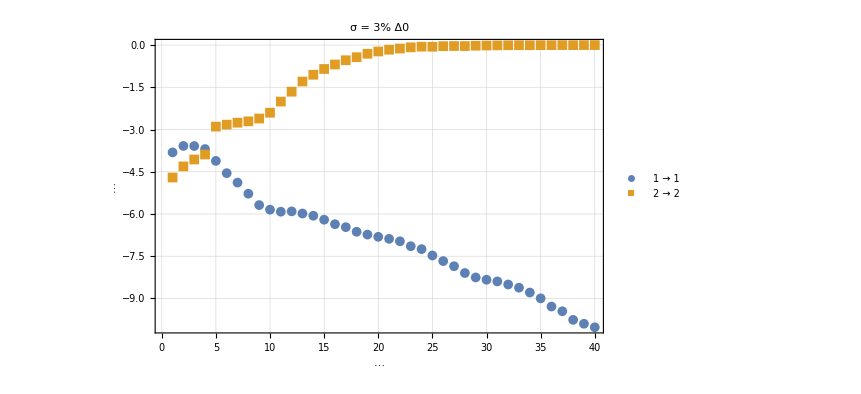

```mathematica
ListPlot[{gain3SATD, loss3SATD},PlotRange-> All,Frame->True,GridLines->Automatic, PlotLegends->Placed[{"1 → 1", "2 → 2"},{Right, Center}],PlotLabel->Style["σ = 3% Δ0",20], PlotMarkers->{Automatic,10},GridLinesStyle-> Thin, FrameLabel->{Style["",15],Style["(*GraphicsBox[{Thickness[0.017283097131005877`], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGI3IGYC4ur7P24Zcys68McG3DcqV3CA8ZWvPQpmmKPg
cPoMELxRcLijKbvm/2YFh7VCOnzp5xD8NVD+bSh/JgisRMiXHt7mOnOuAty8
Fd9eVpyZoOCwN7/m7cypCD5YX6eCw38QiIfKiyo4zACJW8o7uK85upzhh7RD
qwK76hkRWQg9RcwhIw0I2ETh/Aeu8Y6zCgXgfJDzz/Tww/n2JY61p2MQfNVP
Ki9nneRzCHl7+eOMhWIOMaoRMuf28Doo7FqwL3WdmEM6yPxlvA4gKu0Ygr8j
2Criv7o4nA/WVyPu8HXfx63p12DqxR1axGtZM9n4IPaZSDgwgECDqMPr4q2i
v7k1Ifa8E3UQ6fF6xfJFE+J+QTEHmXlxmqcNtBxEKieVnHWRgvPlQer7pOH8
A937mkweY/L1tVYKX1iC4EtMvcKZ8UgL4s4YBP88KHx0EHxwOFtIwfng+JCX
dPA5wW47+6qWQxUofWhLwPngcDguCOeD1d8XgPMh4cMPNw8WPjC+7xPPS6bC
CD4kvHgw+CycXfLJeQg+qn8R/ILlJRv++fPB+ZDwFMLgg935XxPOn9LeGnV5
j6bDfTQ+TB4cX92aUP8JOkiDzdN0kNkoNp/pAZvDm7bcbqPdEg5Lbi1/bMjM
5tAX0e3PKCDuEADy32VW1PTo888exn9T+zj7/JpfcH4zyH/HfmDwwfljpyic
b2IMAqIO66W36Z568xPOr3nR9Gvazr8IPii+Tss4wPiuoPi9IQvng9PXE1lI
unQQheY3OYh/pMUcum08d6V9UoCEi6KCQzinWLvxf2g+tUeUF8Igc1IQfFh5
AgCUldIw
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{14.435899999999998`, 8.57813}, {14.435899999999998`, 9.71094}, {13.696899999999998`, 10.5563}, {12.612499999999997`, 10.5563}, {11.0391, 10.5563}, {9.48906, 8.840629999999999}, {9.48906, 7.159379999999999}, {9.48906, 6.02656}, {10.2281, 5.1812499999999995`}, {11.3125, 5.1812499999999995`}, {12.898400000000002`, 5.1812499999999995`}, {14.435899999999998`, 6.8968799999999995`}, {14.435899999999998`, 8.57813}}, CompressedData["
1:eJxTTMoPSmViYGAQBmIQnZ4GBG7aDrc1Zdf8Z1ZygPHDOcXajfkVIfxjWg4i
lZNKzrLIOpw47LQ2856mQ4xqhMw5GSkHv4sTY/491nCouf/jlvFrMQfRHq9X
LFPUHc6AwBpRB5D2tGVqcH5m/ofWkyWqcL6RMRBMVnFoVWBXPTNFHM6HmCcF
50Psk3Vo4fVfP0VV1aH88DbXmX8VHKTmxWmevqDqsFZIhy9dT8nh19vXBywf
qzn4gtzFrOKw3aHp0XELDYefIPHFKg7GYKAJ54P9E6cF58P8HwHy/3plB/Tw
AQDksYAh
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}}, {{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAQBWIQ3e31isVkoZFDyNvLH2c4Sjvoa60UvjDFyGG9kA5f
ep2UQ/FW0d+n+4wczoCAj5RDI8vRfsN0I4cv+z5uTZ8m6cDtplrK9MrQoS+i
259RQNxhJghkGjrsCLaK+K8u5jB9An+VGTeCn54GBMsM4Pzk2DtuzB4GDiKV
k0rOpojD+fK7FuxLXScF54PtM5N1WHJ/H9+cxQYOqSBz3BQh5j0zcPiwaL3C
2QglhyeJC6+Z2Bs6RHCKtRuvV3bg918/JfWEocPPt68PWC5WgfA9jOD85S88
9P4LGsP5YPdbGjusBfl/nRKcD6Y7lRwK13TfzjAwdhAGuddEyQE9/ADhe49+

"], CompressedData["
1:eJxTTMoPSmViYGAwAmIQXbxV9Pfpc0YOwW8vf5zBKOTw51vpgzmKJg4RnGLt
xuuVHVSfNM87q2Xi4LHm6HKGHwi+1Lw4zdMCKjj5aWCg4qDxlnefAaeJQ8Nv
q4JzK1Qcpk/grzK7bQznL3/hofd/IoL/eUNA9qx0Y4cniQuvmeirOJw+7LQ2
M87YwWVCs1Bal7JDOshYM2OHC1fD3uhbqzh0e71iMXlo5DClvTXqsoyqA7//
+impHgj+Rr28xYx/DOD8H29fH7Bk1nf4sGi9wtkbinC+O8h/M2Tg/BBQeCwU
h4SHo4GDiTEIiDrclK5JNGI1hPOvC31yPL8MwYe4zwjKF3ewrYxYYZpr5LAj
2Criv7qEgzooPCyNHL7s+7g1/ZsInL9WSIcv/Z6IA7ebaimTlpFDjGqEzLk7
wpBw+G8IkbcThJj31tDh7Bkg4BGAyNcbOiy5tfyx4WEeSHgyGjrMmAkENzkc
IsS3X2ToM4Dz1UHx44XgnwCF7z19OD8V5H43fYczYPM5HdaDInStnkPJ8pIN
/85zOkiA4rlA34HHkc9rxkouB1ObvUHTFupD/BPGC+fv797XZJLMB+eD1b/k
d9jq0PToeAQ0vHcIOPjfAgboJT04/z8I2CP4D0AeWKDr0CJey5rZxg/nQ8zn
gfO3eW2wmFPJ4XAelC5m60HC/zMbJH0EGsD54PR5yxDOb2Q52m+43MjBvsSx
9vQdPgf0/AAA4EBVhA==
"]}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{23.579700000000003`, 2.3203099999999997`}, {23.579700000000003`, 2.7609399999999997`}, {22.4234, 2.7609399999999997`}, {22.4234, 13.799999999999997`}, {23.579700000000003`, 13.799999999999997`}, {23.579700000000003`, 14.240599999999999`}, {21.9828, 14.240599999999999`}, {21.9828, 2.3203099999999997`}, {23.579700000000003`, 2.3203099999999997`}}}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJZIGYC4hkzgeCkjYOJMQiIOsD4rQrsqmemiDmoPmme
dzYLwT9x2GltZpw1nH9DuibRKNTaYUewVcR/dXE4f62QDl/6PQk439xmb9C0
h5pwPgtnl3xynhacL9Lj9YqlRMuBx3/9lFQJBL9kq+jv0+esHJ4kLrxmcl7T
IT0NCMysHNaDHPZWw2GjXt5ixj8WGPzJ7a1Rl200HMSnXuHMcLKE89VB/rmF
4B9pWx5+qsnK4fzVsDf6txF8mPthfJj/wOFTaQX3v21lxArTXEs4/yQofPgw
+bDwlZ4Xp3k6wdKh6v6PW8beog71v60KznVYwfnPs7S/TX+L4IPdH2QN5zew
HO03LLeB89HjDwAjMb9b
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {{{40.773399999999995`, 8.27969}, {40.773399999999995`, 8.518749999999999}, {40.546899999999994`, 8.518749999999999}, {40.37969999999999, 8.518749999999999}, {33.882799999999996`, 8.518749999999999}, {33.715599999999995`, 8.518749999999999}, {33.4891, 8.518749999999999}, {33.4891, 8.27969}, {33.4891, 8.04219}, {33.715599999999995`, 8.04219}, {33.882799999999996`, 8.04219}, {40.37969999999999, 8.04219}, {40.546899999999994`, 8.04219}, {40.773399999999995`, 8.04219}, {40.773399999999995`, 8.27969}}}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJx11X0slHEcAPDzErOE0d3ZzJy4szvvLyHT9rXG81IbmcWkedudViiLeYmk
QiN1YZxLIitaM/rDREu1ZiyUpmxpi5ktwkQlee1+z8PvtzG/7fnjs+ee575v
v99jn3AhXGkgEAj0dFeC7tLXXT/bws5rM1nQqM1zfPfLoFceUN5fzcJVw547
nn4K7LiIcKd6RgFOk9frBrUshI3a5MaX7+0TfcZH731WgGFjeYBeGbGmRrfS
iFVo1VHY8W+HnZUFxI+naLfNtN2ufejQuZZE7K54YjXkqIABtHKJ09uFq/1V
xAcXgz6o/ux27qKuECtybC7/DuIOuDbRq5FDdlTz4cFfFGyilS+HyfiGEZ95
CiqKC6OHA+Vwi/1h6GNPwWxRSqnXC2tINvlXn2RFwe2o0lA9CzGYhrZWKi0o
KJQYSwcqRcCivB6FYIdIM/S1N4njUD2ydxuVsaZTiO3jjZaQj6eY2H+kJ8VH
TfxF1yavFuIslE9/COSMLY96HxfCldWAi++niLn3tVLYwSi+IeLt+my/7xKq
t4jGrlwyitU4Ej8t/XpW4Lfbkq76bqWZCHs7X7ughcQBV+Kipsh3XqbEXFsq
SD25+NS6fqL4Zogj5oYXNA1i7BZLF7Okb2L8vAAtsMbz8rt7oT2pyprv1zIF
kSaiYu/YQyBD811CY3P5bhBzc2HMgPmZsDGvv/bYSjTnIfY77kv4/bGPgbHg
2CBtg4TvzzoNl1H8NhIY6zar9V6hgSuXgQTyUH+WaShD89Rmt6e5+Ttth+Nz
WnSc1srt+HkxYbCPo/kTEnP9FjP4eUvUX1uGz89cwvcjg4Gpc85L1fel2Nz+
bJfy85/G8PtpVAp1gS6ftCpiLr4o4s7RknVlJAO+gS/Dq95sPX9y6370lj0Z
aF6azhpQO8DsgW6PGkuGr6O5A///ZTT2SkxKz4Y+sau6ftlTReP9+cwttVEv
nebPK0sFP2+ZND4PuHq0Ezeh86WAwc5H8QOLXYzmMYaFlbmZ10eOybHXlzLG
a+86YXPnUjIx/SrP1v+7DLjzN5LlzzNKBu4o3lMs9HU9LzPykMEayiechYko
ccfHcSk29/te4gJ0XlVLYR7VJ5oFDxTfDSm/vxOJH6B+pBJz+zOdxf3c+T34
D6pZmus=
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{55.44839999999999, 2.3203099999999997`}, {55.44839999999999, 14.240599999999999`}, {53.849999999999994`, 14.240599999999999`}, {53.849999999999994`, 13.799999999999997`}, {55.0063, 13.799999999999997`}, {55.0063, 2.7609399999999997`}, {53.849999999999994`, 2.7609399999999997`}, {53.849999999999994`, 2.3203099999999997`}, {55.44839999999999, 2.3203099999999997`}}}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{86.78978331257782, 24.508064757160646`},PlotRange->{{0., 57.86}, {0., 16.34}}])", 15]}, LabelStyle->{Bold,24}]
```

#### SATD Error Analysis (φ=π → w/ Imprecision)

```mathematica
Γ=1;
Δ0=499999/1000000Γ;
Ω0=1/2Γ;
φ=π-10^-16;
ω=ωCirc1;
dir=1;
```

3%

```mathematica
σδΔ0=3/100 1/2 Γ;
NSamp=1000;
cinit={1,0};
cfinal={1,0};

t0Max=40/Γ;
t0min=1/Γ;
t0Steps=40;

AbsoluteTiming[gain3SATDπ=ErrorAnalysisSATD[Δ0,Ω0,Γ,φ,ω,dir,t0Max,t0min,t0Steps,σδΔ0,NSamp,cinit,cfinal];]
gain3SATDπ
```

```mathematica
gain3SATDπ={{1,-5.99015097888644767530628831976432738911`18.37141562345892},{2,-6.06681388789274353673377771588585291355`18.17536619570644},{3,-4.56696995608237954713801173858130777605`19.455002056058603},{4,-5.18163373607255219039937795041594405732`18.81599882749763},{5,-4.05839149009861108807698168149688693738`19.76622386506033},{6,-3.05596612271891862522547716949827500637`20.587805905107892},{7,-2.41748036375460977546504569119433033213`21.074637465967083},{8,-1.91460797556394102511436904452349170893`21.434124451226683},{9,-1.46443101435931988440615393450174316696`21.736357333955993},{10,-1.16181960096711074554080711981340683798`21.91646816614246},{11,-0.92522806905220805582735313885068157412`22.04330766750605},{12,-0.70112665809137283293878297637777893072`22.156222461037856},{13,-0.57542581107359752851921147084087865796`22.20395420274806},{14,-0.48185508854258247495294671698033473066`22.231960912950175},{15,-0.41180883804050879062175565232033460881`22.246549614533137},{16,-0.38128718233493369105091917951226554538`22.239271297886308},{17,-0.36719597526432475498678708960898793965`22.22384016977798},{18,-0.40394007643128168026497150748975833793`22.180526635972345},{19,-0.58751848820609761041902137560599823349`22.050494839219674},{20,-0.66443400815728010763636901155623350543`21.982870976813828},{21,-0.59570747837409208699983214963182772085`22.00596330813961},{22,-0.23870837358730640320740401134452503595`22.19405270913474},{23,-0.1171542208599124184774152836819336772`22.241172677676364},{24,-0.07646569939012281036600294552966753979`22.245222300309297},{25,-0.04706735857686315563599314699306851677`22.243875264766274},{26,-0.03583247327684587029930693630351227509`22.233783405761226},{27,-0.03310228621582765384078817142698323397`22.219923001937754},{28,-0.02145910649518880235069435514591403957`22.21108292237818},{29,-0.0249352361484732837190387350396771165`22.195086554167414},{30,-0.02289819458411941846241398738275664518`22.18232672147362},{31,-0.02030658221351979674178963856223433946`22.1703161788791},{32,-0.02668540518478556170535706733145079447`22.154152849756954},{33,-0.05437403768507300892224215544128438469`22.127516464247503},{34,-0.1176986861923544185524005612633677166`22.082499554551827},{35,-0.07498721354541898364273148812440323994`22.09277027499487},{36,-0.01979004152774570869732780860307316288`22.109363994494306},{37,-0.00641261145754577219880916324458142108`22.1047028685771},{38,-0.003842184568983786138858910853134314`22.094990188143985},{39,-0.00528022045471667842481861051807695271`22.083544138305033},{40,-0.00345048845134929521931202459245703919`22.073995029405488}};
```

```mathematica
σδΔ0=3/100 1/2 Γ;
NSamp=1000;
cinit={0,1};
cfinal={0,1};

t0Max=40/Γ;
t0min=1/Γ;
t0Steps=40;

AbsoluteTiming[loss3SATDπ=ErrorAnalysisSATD[Δ0,Ω0,Γ,φ,ω,dir,t0Max,t0min,t0Steps,σδΔ0,NSamp,cinit,cfinal];]
loss3SATDπ
```

```mathematica
loss3SATDπ={{1,-4.80160306881173306439193585935428209362`19.46391813525235},{2,-4.41146647104671961640791089242425871645`19.692348806338032},{3,-4.18420993861650688722829331767916434845`19.79976997359388},{4,-4.54256057250382412955922875701275684686`19.39791773513696},{5,-5.38229005591719471040555178140093482438`18.56490590666995},{6,-6.61362401984696943636716718267118024873`17.365064852532253},{7,-5.43806086017242557059342085859484770607`18.40448381925996},{8,-5.13332270912370957205635463430485789117`18.6384199178269},{9,-5.03196382724123575700823438932580214557`18.68974459268939},{10,-5.13842198455664786327746437920947753013`18.554582090913648},{11,-5.39424583209054229797819819691954503308`18.28508024002947},{12,-5.68667828868835848920701462283695707901`17.9834164276143},{13,-6.37791899104922842619778778985474012715`17.312023159726238},{14,-7.01298286682465340447967061884881766979`16.690174274015845},{15,-6.47033617578026907936679246645390495267`17.17150530927231},{16,-6.12937306419807842218660535321285056791`17.464132104018418},{17,-6.03018840326834324870281024633541570538`17.532745491880757},{18,-6.05515503176030833099325822809676015339`17.48730634786578},{19,-6.24329447758115433743682260116259488485`17.291255691006427},{20,-6.49590841218969972724866029799243452047`17.035691732551896},{21,-6.94052171331945626260594705333195009438`16.600509797114903},{22,-7.41385227821854116522989167096291648964`16.137358162872033},{23,-7.14640019296372101342732872592215048632`16.371115475977486},{24,-6.86124756872430102400550526275790504861`16.62156013018632},{25,-6.78016995522446283231587830557591558559`16.681078231950735},{26,-6.79039440620903269850727749088640363333`16.655706785488526},{27,-6.91385514412710426197286994457229885787`16.524831310666055},{28,-7.13590946442879682441830981095319687692`16.301789483529912},{29,-7.48227002513383552412375559787708636175`15.961761849638867},{30,-7.82750564566222647755900172838491414418`15.62232875154976},{31,-7.82960635777564195950738106487573862844`15.606984490391666},{32,-7.61998552542385514711170692338730214157`15.791848329172192},{33,-7.4139438601854591209880342492438802399`15.973419366797998},{34,-7.40338724244100905806887709311134614851`15.971115194479996},{35,-7.49019864421053113790930380449265792837`15.877465154372343},{36,-7.64946912633611218334685686069560044464`15.715750194845958},{37,-7.91093475496835531229255354354031418232`15.457603078595167},{38,-8.08677585149246780849042090113717056101`15.280321800204147},{39,-8.20150627781449604659555609157760559535`15.160972593834751},{40,-8.11513497699854424963927063670950575884`15.232278975662771}};
```

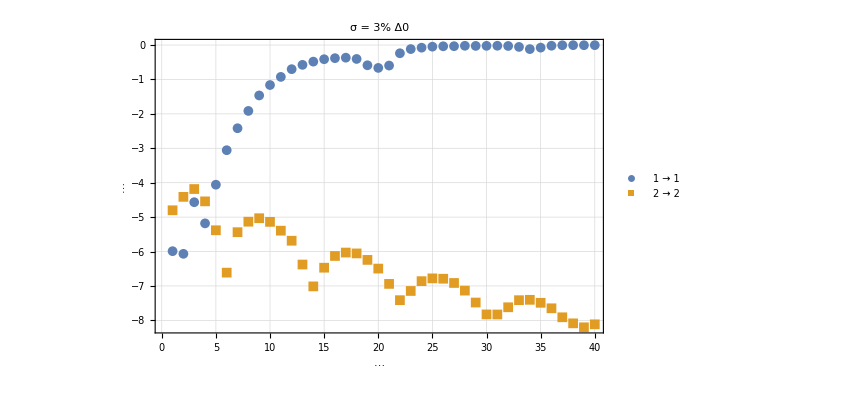

```mathematica
ListPlot[{gain3SATDπ, loss3SATDπ},PlotRange-> All,Frame->True,GridLines->Automatic, PlotLegends->Placed[{"1 → 1", "2 → 2"},{Right, Center}],PlotLabel->Style["σ = 3% Δ0",20], PlotMarkers->{Automatic,10},GridLinesStyle-> Thin, FrameLabel->{Style["",15],Style["(*GraphicsBox[{Thickness[0.017283097131005877`], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGI3IGYC4ur7P24Zcys68McG3DcqV3CA8ZWvPQpmmKPg
cPoMELxRcLijKbvm/2YFh7VCOnzp5xD8NVD+bSh/JgisRMiXHt7mOnOuAty8
Fd9eVpyZoOCwN7/m7cypCD5YX6eCw38QiIfKiyo4zACJW8o7uK85upzhh7RD
qwK76hkRWQg9RcwhIw0I2ETh/Aeu8Y6zCgXgfJDzz/Tww/n2JY61p2MQfNVP
Ki9nneRzCHl7+eOMhWIOMaoRMuf28Doo7FqwL3WdmEM6yPxlvA4gKu0Ygr8j
2Criv7o4nA/WVyPu8HXfx63p12DqxR1axGtZM9n4IPaZSDgwgECDqMPr4q2i
v7k1Ifa8E3UQ6fF6xfJFE+J+QTEHmXlxmqcNtBxEKieVnHWRgvPlQer7pOH8
A937mkweY/L1tVYKX1iC4EtMvcKZ8UgL4s4YBP88KHx0EHxwOFtIwfng+JCX
dPA5wW47+6qWQxUofWhLwPngcDguCOeD1d8XgPMh4cMPNw8WPjC+7xPPS6bC
CD4kvHgw+CycXfLJeQg+qn8R/ILlJRv++fPB+ZDwFMLgg935XxPOn9LeGnV5
j6bDfTQ+TB4cX92aUP8JOkiDzdN0kNkoNp/pAZvDm7bcbqPdEg5Lbi1/bMjM
5tAX0e3PKCDuEADy32VW1PTo888exn9T+zj7/JpfcH4zyH/HfmDwwfljpyic
b2IMAqIO66W36Z568xPOr3nR9Gvazr8IPii+Tss4wPiuoPi9IQvng9PXE1lI
unQQheY3OYh/pMUcum08d6V9UoCEi6KCQzinWLvxf2g+tUeUF8Igc1IQfFh5
AgCUldIw
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{14.435899999999998`, 8.57813}, {14.435899999999998`, 9.71094}, {13.696899999999998`, 10.5563}, {12.612499999999997`, 10.5563}, {11.0391, 10.5563}, {9.48906, 8.840629999999999}, {9.48906, 7.159379999999999}, {9.48906, 6.02656}, {10.2281, 5.1812499999999995`}, {11.3125, 5.1812499999999995`}, {12.898400000000002`, 5.1812499999999995`}, {14.435899999999998`, 6.8968799999999995`}, {14.435899999999998`, 8.57813}}, CompressedData["
1:eJxTTMoPSmViYGAQBmIQnZ4GBG7aDrc1Zdf8Z1ZygPHDOcXajfkVIfxjWg4i
lZNKzrLIOpw47LQ2856mQ4xqhMw5GSkHv4sTY/491nCouf/jlvFrMQfRHq9X
LFPUHc6AwBpRB5D2tGVqcH5m/ofWkyWqcL6RMRBMVnFoVWBXPTNFHM6HmCcF
50Psk3Vo4fVfP0VV1aH88DbXmX8VHKTmxWmevqDqsFZIhy9dT8nh19vXBywf
qzn4gtzFrOKw3aHp0XELDYefIPHFKg7GYKAJ54P9E6cF58P8HwHy/3plB/Tw
AQDksYAh
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}}, {{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAQBWIQ3e31isVkoZFDyNvLH2c4Sjvoa60UvjDFyGG9kA5f
ep2UQ/FW0d+n+4wczoCAj5RDI8vRfsN0I4cv+z5uTZ8m6cDtplrK9MrQoS+i
259RQNxhJghkGjrsCLaK+K8u5jB9An+VGTeCn54GBMsM4Pzk2DtuzB4GDiKV
k0rOpojD+fK7FuxLXScF54PtM5N1WHJ/H9+cxQYOqSBz3BQh5j0zcPiwaL3C
2QglhyeJC6+Z2Bs6RHCKtRuvV3bg918/JfWEocPPt68PWC5WgfA9jOD85S88
9P4LGsP5YPdbGjusBfl/nRKcD6Y7lRwK13TfzjAwdhAGuddEyQE9/ADhe49+

"], CompressedData["
1:eJxTTMoPSmViYGAwAmIQXbxV9Pfpc0YOwW8vf5zBKOTw51vpgzmKJg4RnGLt
xuuVHVSfNM87q2Xi4LHm6HKGHwi+1Lw4zdMCKjj5aWCg4qDxlnefAaeJQ8Nv
q4JzK1Qcpk/grzK7bQznL3/hofd/IoL/eUNA9qx0Y4cniQuvmeirOJw+7LQ2
M87YwWVCs1Bal7JDOshYM2OHC1fD3uhbqzh0e71iMXlo5DClvTXqsoyqA7//
+impHgj+Rr28xYx/DOD8H29fH7Bk1nf4sGi9wtkbinC+O8h/M2Tg/BBQeCwU
h4SHo4GDiTEIiDrclK5JNGI1hPOvC31yPL8MwYe4zwjKF3ewrYxYYZpr5LAj
2Criv7qEgzooPCyNHL7s+7g1/ZsInL9WSIcv/Z6IA7ebaimTlpFDjGqEzLk7
wpBw+G8IkbcThJj31tDh7Bkg4BGAyNcbOiy5tfyx4WEeSHgyGjrMmAkENzkc
IsS3X2ToM4Dz1UHx44XgnwCF7z19OD8V5H43fYczYPM5HdaDInStnkPJ8pIN
/85zOkiA4rlA34HHkc9rxkouB1ObvUHTFupD/BPGC+fv797XZJLMB+eD1b/k
d9jq0PToeAQ0vHcIOPjfAgboJT04/z8I2CP4D0AeWKDr0CJey5rZxg/nQ8zn
gfO3eW2wmFPJ4XAelC5m60HC/zMbJH0EGsD54PR5yxDOb2Q52m+43MjBvsSx
9vQdPgf0/AAA4EBVhA==
"]}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{23.579700000000003`, 2.3203099999999997`}, {23.579700000000003`, 2.7609399999999997`}, {22.4234, 2.7609399999999997`}, {22.4234, 13.799999999999997`}, {23.579700000000003`, 13.799999999999997`}, {23.579700000000003`, 14.240599999999999`}, {21.9828, 14.240599999999999`}, {21.9828, 2.3203099999999997`}, {23.579700000000003`, 2.3203099999999997`}}}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJZIGYC4hkzgeCkjYOJMQiIOsD4rQrsqmemiDmoPmme
dzYLwT9x2GltZpw1nH9DuibRKNTaYUewVcR/dXE4f62QDl/6PQk439xmb9C0
h5pwPgtnl3xynhacL9Lj9YqlRMuBx3/9lFQJBL9kq+jv0+esHJ4kLrxmcl7T
IT0NCMysHNaDHPZWw2GjXt5ixj8WGPzJ7a1Rl200HMSnXuHMcLKE89VB/rmF
4B9pWx5+qsnK4fzVsDf6txF8mPthfJj/wOFTaQX3v21lxArTXEs4/yQofPgw
+bDwlZ4Xp3k6wdKh6v6PW8beog71v60KznVYwfnPs7S/TX+L4IPdH2QN5zew
HO03LLeB89HjDwAjMb9b
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {{{40.773399999999995`, 8.27969}, {40.773399999999995`, 8.518749999999999}, {40.546899999999994`, 8.518749999999999}, {40.37969999999999, 8.518749999999999}, {33.882799999999996`, 8.518749999999999}, {33.715599999999995`, 8.518749999999999}, {33.4891, 8.518749999999999}, {33.4891, 8.27969}, {33.4891, 8.04219}, {33.715599999999995`, 8.04219}, {33.882799999999996`, 8.04219}, {40.37969999999999, 8.04219}, {40.546899999999994`, 8.04219}, {40.773399999999995`, 8.04219}, {40.773399999999995`, 8.27969}}}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJx11X0slHEcAPDzErOE0d3ZzJy4szvvLyHT9rXG81IbmcWkedudViiLeYmk
QiN1YZxLIitaM/rDREu1ZiyUpmxpi5ktwkQlee1+z8PvtzG/7fnjs+ee575v
v99jn3AhXGkgEAj0dFeC7tLXXT/bws5rM1nQqM1zfPfLoFceUN5fzcJVw547
nn4K7LiIcKd6RgFOk9frBrUshI3a5MaX7+0TfcZH731WgGFjeYBeGbGmRrfS
iFVo1VHY8W+HnZUFxI+naLfNtN2ufejQuZZE7K54YjXkqIABtHKJ09uFq/1V
xAcXgz6o/ux27qKuECtybC7/DuIOuDbRq5FDdlTz4cFfFGyilS+HyfiGEZ95
CiqKC6OHA+Vwi/1h6GNPwWxRSqnXC2tINvlXn2RFwe2o0lA9CzGYhrZWKi0o
KJQYSwcqRcCivB6FYIdIM/S1N4njUD2ydxuVsaZTiO3jjZaQj6eY2H+kJ8VH
TfxF1yavFuIslE9/COSMLY96HxfCldWAi++niLn3tVLYwSi+IeLt+my/7xKq
t4jGrlwyitU4Ej8t/XpW4Lfbkq76bqWZCHs7X7ughcQBV+Kipsh3XqbEXFsq
SD25+NS6fqL4Zogj5oYXNA1i7BZLF7Okb2L8vAAtsMbz8rt7oT2pyprv1zIF
kSaiYu/YQyBD811CY3P5bhBzc2HMgPmZsDGvv/bYSjTnIfY77kv4/bGPgbHg
2CBtg4TvzzoNl1H8NhIY6zar9V6hgSuXgQTyUH+WaShD89Rmt6e5+Ttth+Nz
WnSc1srt+HkxYbCPo/kTEnP9FjP4eUvUX1uGz89cwvcjg4Gpc85L1fel2Nz+
bJfy85/G8PtpVAp1gS6ftCpiLr4o4s7RknVlJAO+gS/Dq95sPX9y6370lj0Z
aF6azhpQO8DsgW6PGkuGr6O5A///ZTT2SkxKz4Y+sau6ftlTReP9+cwttVEv
nebPK0sFP2+ZND4PuHq0Ezeh86WAwc5H8QOLXYzmMYaFlbmZ10eOybHXlzLG
a+86YXPnUjIx/SrP1v+7DLjzN5LlzzNKBu4o3lMs9HU9LzPykMEayiechYko
ccfHcSk29/te4gJ0XlVLYR7VJ5oFDxTfDSm/vxOJH6B+pBJz+zOdxf3c+T34
D6pZmus=
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{55.44839999999999, 2.3203099999999997`}, {55.44839999999999, 14.240599999999999`}, {53.849999999999994`, 14.240599999999999`}, {53.849999999999994`, 13.799999999999997`}, {55.0063, 13.799999999999997`}, {55.0063, 2.7609399999999997`}, {53.849999999999994`, 2.7609399999999997`}, {53.849999999999994`, 2.3203099999999997`}, {55.44839999999999, 2.3203099999999997`}}}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{86.78978331257782, 24.508064757160646`},PlotRange->{{0., 57.86}, {0., 16.34}}])", 15]}, LabelStyle->{Bold,24}]
```

#### RADD Error Analysis (φ=0 → w/ Imprecision)

```mathematica
(*data for RADD is determined by RMS optimization code in Fig 12*)
```

##### Data

```mathematica
Dataphi0={{1,899/100,2659/13500,4/5,5.14257465047306,7.830811557929698,6.416899246682768},{6/5,679/100,2713/11250,9/10,4.3052166010512725,6.733771417418353,5.253451543478002},{7/5,569/100,4606/16875,9/10,3.691748423905285,5.7948557116304915,4.505129621701359},{8/5,113/20,4492/16875,4/5,3.2186241136767966,4.803854861275129,4.096067861578489},{9/5,459/100,2273/7500,9/10,2.8694105669044663,4.309161105315162,3.5944912724246154},{2,453/100,133/450,4/5,2.591909157941355,3.875537904424736,3.314188424013389},{11/5,349/100,4763/13500,1,2.3653125703798143,3.5039661358672136,2.937002257835975},{12/5,331/100,133/375,1,2.178676765992632,3.15238437581109,2.7416165817822846},{13/5,331/100,403/1125,9/10,2.027187783748179,2.8577345706128874,2.593753276682501},{14/5,239/100,3031/6750,6/5,1.897344962632379,2.6711067942790048,2.2910961611122067},{3,237/100,319/750,11/10,1.7815010340874895,2.5038740250257057,2.1850688858889713},{16/5,221/100,496/1125,11/10,1.686446640097023,2.3241524810326673,2.0627329547842552},{17/5,221/100,391/900,1,1.6067079359810215,2.194971558835207,1.975756828242822},{18/5,221/100,311/750,9/10,1.5398991419778585,2.153747432091916,1.8813075356836577},{19/5,129/100,12293/22500,17/10,1.478815628042432,2.086407666575176,1.6377670044422308},{4,129/100,611/1125,8/5,1.4182441205557077,1.8834223745626364,1.5905363684172626},{21/5,129/100,161/300,3/2,1.3680165728708247,1.7543241918365353,1.5475391194505967},{22/5,119/100,253/450,3/2,1.3256512047912972,1.6580707585085468,1.4787323275099769},{23/5,119/100,7153/13500,7/5,1.2885618092804039,1.6305874697229854,1.4384097760515497},{24/5,111/100,622/1125,7/5,1.2549543081616414,1.534017608046871,1.382713261638761},{5,111/100,737/1350,13/10,1.226410098771716,1.479670989101558,1.3459338870159006},{26/5,111/100,18109/33750,6/5,1.2014973428932392,1.4346392994027213,1.307415963670841},{27/5,111/100,328/625,11/10,1.1795705339442368,1.39327714345922,1.2667964155903089},{28/5,111/100,1799/3375,11/10,1.1602881726196455,1.308445583922176,1.2430225676882423},{29/5,111/100,6467/13500,9/10,1.143000945014939,1.341200410285925,1.1751461237226928},{6,111/100,544/1125,9/10,1.1270682722205647,1.2627549509048763,1.151662048506368},{31/5,111/100,1519/3375,4/5,1.1130053254418788,1.2409021623784542,1.1022615602694834},{32/5,111/100,7408/16875,4/5,1.1001555211365948,1.1968665893844188,1.0747690153528986},{33/5,111/100,1859/4500,7/10,1.088533935598464,1.1486825074743097,1.0461659749165444},{34/5,111/100,2873/6750,4/5,1.0784905903203144,1.1036439920833387,1.050212892088008},
{7,19/100,497/675,39/10,1.0625153481686964,1.1829374776399135,0.8704900314203157},{36/5,19/100,1393/1875,37/10,1.0512679264812823,1.1182908114667367,0.8570982173021825},{37/5,19/100,49543/67500,7/2,1.0416633719965984,1.058795816087011,0.8459444131587927},{38/5,19/100,4883/6750,33/10,1.0334181447909154,1.0039197487101748,0.8361716814014373},{39/5,19/100,3341/4500,31/10,1.0263548163768923,1.0000974303805166,0.826358009641652},{8,19/100,514/675,31/10,1.020347208804992,1.0000842660315306,0.8176677316583832},{41/5,17/100,10537/13500,31/10,1.0151100024228847,1.0000728258755713,0.8012635356825508},{42/5,17/100,3808/5625,27/10,1.009910575445453,1.0000628600274726,0.7934031599589462},{43/5,13/100,11696/16875,31/10,1.0055857881033197,1.0000551883871416,0.7711587873924172},{44/5,11/100,11671/16875,33/10,1.0016809230386814,1.0000485385389524,0.7563944734944827},{9,9/100,517/750,7/2,0.9981650610851556,1.0000426802149074,0.7417762902018624},{46/5,7/100,23161/33750,37/10,0.9949997365934106,1.000037508608069,0.7272369461320506},{47/5,1/20,2303/3375,39/10,0.9921522430079016,1.000032934432042,0.7126995572674604},{48/5,3/100,12/25,19/10,0.9897132305755489,1.000028881373767,0.6865165756803826},{49/5,1/100,49/100,19/10,0.987334350031673,1.0000258146857648,0.679453106770149},{10,1/100,1/2,19/10,0.9852574234264256,1.000023079318399,0.6750902756414522},{51/5,1/100,51/100,19/10,0.9834470775040678,1.0000206319894682,0.6711144167111794},{52/5,1/100,39/125,4/5,0.9818641313866641,1.0000184388511482,0.6667646919568819},{53/5,1/100,159/500,9/10,0.9804751354711089,1.0000164705156827,0.6633383917451869},{54/5,1/100,81/250,9/10,0.9792600756582555,1.000014701402503,0.660288520681148},{11,1/100,33/100,1,0.9781966413099381,1.0000131091903768,0.6573949601714414},{56/5,1/100,42/125,1,0.9772654207933991,1.0000117393616978,0.6550407413942504},{57/5,1/100,171/500,1,0.9764500250832855,1.000010666371626,0.6529371518775375},{58/5,1/100,87/250,11/10,0.975736104422084,1.0000096925428035,0.6509438668379872},{59/5,1/100,177/500,11/10,0.9751112820616189,1.0000088075944709,0.6491345049939101},{12,1/100,9/25,11/10,0.9745648865643042,1.0000080024449662,0.6474508191982912},{61/5,1/100,183/500,11/10,0.974087585900622,1.0000072690559534,0.6460432458759838},{62/5,1/100,93/250,6/5,0.9736712039321221,1.0000066002989385,0.6448561925561246},{63/5,1/100,189/500,6/5,0.9733086803869683,1.0000059898405989,0.6437609771866447},{64/5,1/100,48/125,6/5,0.9729938030715163,1.0000054320440313,0.6427576995808971},{13,1/100,39/100,6/5,0.972721119092242,1.0000049218835112,0.6420813129469192},{66/5,1/100,99/250,6/5,0.9724858373016615,1.0000044548707454,0.6433108016164207},{67/5,1/100,201/500,6/5,0.9722837404552729,1.0000040941493245,0.645213328221201},{68/5,1/100,51/125,13/10,0.9721110980020462,1.0000037804679829,0.6470364797735756},{69/5,1/100,207/500,13/10,0.9719646340883097,1.0000034912251095,0.6487972536001005},{14,1/100,21/50,13/10,0.9718414500642927,1.0000032242777723,0.6504820771624418},{71/5,1/100,213/500,13/10,0.9717389730514893,1.0000029776950201,0.6520952027839338},{72/5,1/100,54/125,13/10,0.9716549209482247,1.0000027497344655,0.6536405959191489},{73/5,1/100,219/500,13/10,0.9715872669329322,1.000002538821725,0.6551219572245804},{74/5,1/100,111/250,13/10,0.9715342086926152,1.0000023435323366,0.6565427427909027},{15,1/100,9/20,13/10,0.9714941416915757,1.0000021625758222,0.6579061826913645},{76/5,1/100,57/125,13/10,0.9714656359032371,1.000001994781625,0.6592152979897264},{77/5,1/100,231/500,13/10,0.9714474155170938,1.0000018390866736,0.6604729163401617},{78/5,1/100,117/250,13/10,0.9714383412073897,1.0000016945243726,0.6616816863009384},{79/5,1/100,237/500,13/10,0.971437394612264,1.0000015602148355,0.6628440904736151},{16,1/100,12/25,13/10,0.9714436647242448,1.0000014353562117,0.6639624575699968},{81/5,1/100,243/500,13/10,0.9714563359367705,1.0000013192169703,0.6650389735002494},{82/5,1/100,123/250,13/10,0.9714746775282745,1.0000012296069927,0.6660756915673725},{83/5,1/100,249/500,13/10,0.9714980343965509,1.0000011535439894,0.6670745418456722},{84/5,1/100,63/125,13/10,0.9715258188824621,1.0000010823426413,0.6680373398139289},{17,1/100,51/100,13/10,0.9715575035444431,1.0000010156513477,0.6689657943076017},{86/5,1/100,129/250,13/10,0.9715926147642636,1.0000009531472933,0.6698615148486109},{87/5,1/100,261/500,13/10,0.97163072708075,1.0000008945338086,0.6707260184059411},{88/5,1/100,66/125,13/10,0.971671458161992,1.000000839537999,0.6715607356355047},{89/5,1/100,267/500,13/10,0.9717144643384501,1.0000007879086117,0.6723670166433203},{18,1/100,27/50,13/10,0.9717594366295095,1.0000007394141142,0.6731461363120964},{91/5,1/100,273/500,13/10,0.971806097204801,1.0000006938409622,0.6738992992276958},{92/5,1/100,69/125,13/10,0.9718541962290692,1.0000006509920356,0.6746276442386924},{93/5,1/100,279/500,13/10,0.9719035090459486,1.0000006106852242,0.6753322486792633},{94/5,1/100,141/250,13/10,0.9719538336615084,1.00000057275215,0.6760141322829668},{19,1/100,57/100,13/10,0.972004988493345,1.0000005370370089,0.6766742608125221},{96/5,1/100,72/125,13/10,0.972056810355192,1.000000503395519,0.6773135494284934},{97/5,1/100,291/500,13/10,0.9721091526506405,1.0000004716939703,0.6779328658177752},{98/5,1/100,147/250,13/10,0.9721618837527758,1.0000004418083568,0.6785330331009555},{99/5,1/100,297/500,13/10,0.9722148855492697,1.0000004136235894,0.6791148325359854},{20,1/100,3/5,13/10,0.9722680521349057,1.00000038703278,0.6796790060340823}};
```

##### Results

3%

```mathematica
Γ=1;
Δ0=1/2Γ;
Ω0=1/2Γ;
φ=0;
ω=ωCirc1;
dir=1;
```

```mathematica
σδΔ0=3/100 1/2 Γ;
NSamp=1000;
cinit={1,0};
cfinal={1,0};

AbsoluteTiming[gain3RADD=ParallelMap[{Γ #[[1]],ErrorAnalysisFixedTimeRADD[Δ0,Ω0,Γ,φ,ω,dir,#[[1]],σδΔ0,NSamp,cinit,cfinal,#[[2]],#[[3]],#[[4]]]}&,Dataphi0];]
gain3RADD
```

```mathematica
gain3RADD={{1,-2.935631655601487},{6/5,-3.1431157549654793},{7/5,-3.3125671531213112},{8/5,-3.319207530241179},{9/5,-3.511300958380069},{2,-3.507279116780898},{11/5,-3.530722314750635},{12/5,-3.409922646236142},{13/5,-3.3756866880468173},{14/5,-3.3012564402694653},{3,-3.1850318698766205},{16/5,-3.1050860282056547},{17/5,-3.051681893914878},{18/5,-2.9409114885985193},{19/5,-2.9591598815772007},{4,-2.909146335739196},{21/5,-2.805433017953808},{22/5,-2.7853851193619774},{23/5,-2.72390166513929},{24/5,-2.718212259088808},{5,-2.6995224190778035},{26/5,-2.6225932291124416},{27/5,-2.6017359806642992},{28/5,-2.5551105680096233},{29/5,-2.586425011025024},{6,-2.5138871873656856},{31/5,-2.4935072792719555},{32/5,-2.4913986693440484},{33/5,-2.471113204141239},{34/5,-2.3722017894760983},{7,-2.630950533636007},{36/5,-2.6452662263471356},{37/5,-2.6082308582204323},{38/5,-2.630800769096333},{39/5,-2.596069783346174},{8,-2.54644523468087},{41/5,-2.5206644251825465},{42/5,-2.534866655018503},{43/5,-2.4933415832766417},{44/5,-2.5211969085834434},{9,-2.4670561987425663},{46/5,-2.4650313364142487},{47/5,-2.4593701071719174},{48/5,-2.4219726559486308},{49/5,-2.4351485519051805},{10,-2.338176855102353},{51/5,-2.2981008993133583},{52/5,-2.2201575152484234},{53/5,-2.1538842184586615},{54/5,-2.0298489436023286},{11,-1.9981138150441904},{56/5,-1.9360870782431814},{57/5,-1.8399701930464873},{58/5,-1.7653331619424566},{59/5,-1.6625730343174625},{12,-1.6633142104450784},{61/5,-1.5571477695009468},{62/5,-1.4485223418327353},{63/5,-1.4227402643438671},{64/5,-1.3699056226893833},{13,-1.301320609158867},{66/5,-1.2487414727066355},{67/5,-1.1975336368341134},{68/5,-1.1348820872148795},{69/5,-1.0990796704477517},{14,-1.0354430280435576},{71/5,-1.0044749826922452},{72/5,-0.9636961981200296},{73/5,-0.9216252605141186},{74/5,-0.8703017226310276},{15,-0.863270698639072},{76/5,-0.78736221705591},{77/5,-0.7692527990222043},{78/5,-0.7599190881914637},{79/5,-0.70848739173054},{16,-0.6712735831582898},{81/5,-0.6480246888598278},{82/5,-0.615220479691092},{83/5,-0.5858466706963087},{84/5,-0.5735979953358871},{17,-0.5476615742519556},{86/5,-0.5100122572578404},{87/5,-0.4951229969059754},{88/5,-0.46613504553248497},{89/5,-0.4442423124389421},{18,-0.43192469088283536},{91/5,-0.40707029364965414},{92/5,-0.3693375136549192},{93/5,-0.36505505115970743},{94/5,-0.3430341875780265},{19,-0.3250912546498955},{96/5,-0.2942064796180106},{97/5,-0.27602751881378385},{98/5,-0.2558350136519444},{99/5,-0.24469818639285443},{20,-0.23026373564952934}};
```

```mathematica
σδΔ0=3/100 1/2 Γ;
NSamp=1000;
cinit={0,1};
cfinal={0,1};

AbsoluteTiming[loss3RADD=ParallelMap[{Γ #[[1]],ErrorAnalysisFixedTimeRADD[Δ0,Ω0,Γ,φ,ω,dir,#[[1]],σδΔ0,NSamp,cinit,cfinal,#[[2]],#[[3]],#[[4]]]}&,Dataphi0];]
loss3RADD
```

```mathematica
loss3RADD={{1,-4.884363057479131},{6/5,-5.027944071248076},{7/5,-5.190070161461128},{8/5,-5.327178952391651},{9/5,-5.439323523229332},{2,-5.507066667165297},{11/5,-5.433922945304379},{12/5,-5.357817872949383},{13/5,-5.4163342190771075},{14/5,-5.337183399627173},{3,-5.212975832916099},{16/5,-5.153037143277063},{17/5,-5.128037829478706},{18/5,-5.082159291595621},{19/5,-4.8780601185200325},{4,-4.886336594519508},{21/5,-4.9082878414847055},{22/5,-4.96258712907059},{23/5,-4.905636656953474},{24/5,-4.925290472036022},{5,-4.944237653496424},{26/5,-5.007338471178669},{27/5,-5.047163028717367},{28/5,-5.072023247411996},{29/5,-5.042462287195752},{6,-5.09659436990603},{31/5,-5.1102623404376635},{32/5,-5.179840279965296},{33/5,-5.219940667940485},{34/5,-5.235298866056059},{7,-5.106219457543174},{36/5,-5.153552216990025},{37/5,-5.218200850197931},{38/5,-5.252292864892412},{39/5,-5.339411079081144},{8,-5.385621544280996},{41/5,-5.4883129612786075},{42/5,-5.489537783202577},{43/5,-5.572689604161989},{44/5,-5.593527629889154},{9,-5.675224899445136},{46/5,-5.685787662202293},{47/5,-5.7688001104795745},{48/5,-5.784954625881575},{49/5,-5.828007981776009},{10,-5.859793146424869},{51/5,-5.826747475310311},{52/5,-5.898289387465476},{53/5,-5.838237374559559},{54/5,-5.881014499935288},{11,-5.896919819832223},{56/5,-5.920619010673067},{57/5,-5.881283106400245},{58/5,-5.910805226940814},{59/5,-5.919239735732563},{12,-5.9345794789622275},{61/5,-5.843534979041534},{62/5,-5.907668179455352},{63/5,-5.949197788860231},{64/5,-5.925880374890959},{13,-5.975160612297779},{66/5,-5.974186250202779},{67/5,-5.969557186082743},{68/5,-6.007426494442382},{69/5,-6.077995945651904},{14,-6.0625327963137225},{71/5,-6.049400319928491},{72/5,-6.101098220250798},{73/5,-6.113191631122756},{74/5,-6.168287330531149},{15,-6.157721647025925},{76/5,-6.185988582443297},{77/5,-6.2527418592773465},{78/5,-6.2626317669205775},{79/5,-6.319742701487879},{16,-6.347356388008606},{81/5,-6.367565142270839},{82/5,-6.38219625836614},{83/5,-6.373637264621231},{84/5,-6.4715014925155065},{17,-6.494743326187318},{86/5,-6.491214791505435},{87/5,-6.553990469476656},{88/5,-6.544583364168684},{89/5,-6.573232666256909},{18,-6.629645440553696},{91/5,-6.632277823929357},{92/5,-6.686745420763127},{93/5,-6.697766588807952},{94/5,-6.70830110834647},{19,-6.737906364172113},{96/5,-6.773818214510812},{97/5,-6.793676633245556},{98/5,-6.77418987891381},{99/5,-6.808351386154958},{20,-6.815394699639067}};
```

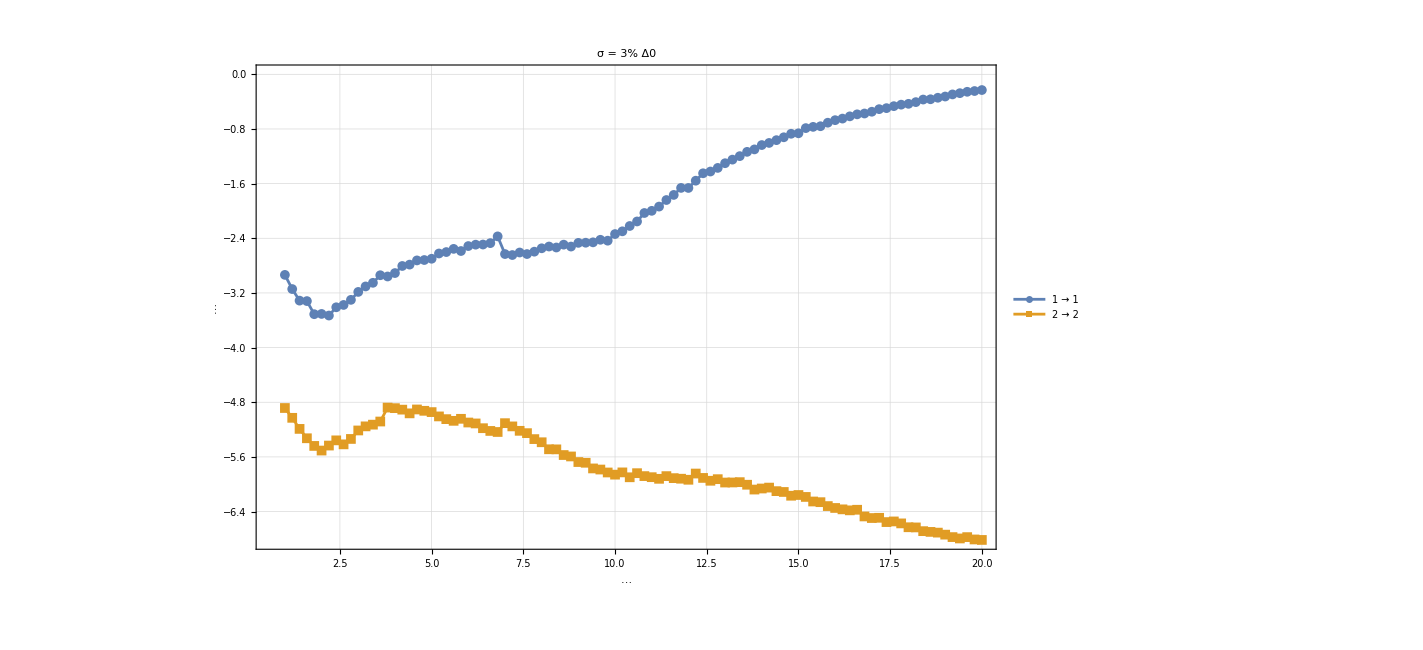

```mathematica
ListPlot[{gain3RADD, loss3RADD},PlotRange-> All,Frame->True,GridLines->Automatic, PlotLegends->Placed[{"1 → 1", "2 → 2"},{Right, Center}],PlotLabel->Style["σ = 3% Δ0",12], PlotMarkers->{Automatic,10},GridLinesStyle-> Thin, FrameLabel->{Style["",12],Style["(*GraphicsBox[{Thickness[0.017283097131005877`], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGI3IGYC4ur7P24Zcys68McG3DcqV3CA8ZWvPQpmmKPg
cPoMELxRcLijKbvm/2YFh7VCOnzp5xD8NVD+bSh/JgisRMiXHt7mOnOuAty8
Fd9eVpyZoOCwN7/m7cypCD5YX6eCw38QiIfKiyo4zACJW8o7uK85upzhh7RD
qwK76hkRWQg9RcwhIw0I2ETh/Aeu8Y6zCgXgfJDzz/Tww/n2JY61p2MQfNVP
Ki9nneRzCHl7+eOMhWIOMaoRMuf28Doo7FqwL3WdmEM6yPxlvA4gKu0Ygr8j
2Criv7o4nA/WVyPu8HXfx63p12DqxR1axGtZM9n4IPaZSDgwgECDqMPr4q2i
v7k1Ifa8E3UQ6fF6xfJFE+J+QTEHmXlxmqcNtBxEKieVnHWRgvPlQer7pOH8
A937mkweY/L1tVYKX1iC4EtMvcKZ8UgL4s4YBP88KHx0EHxwOFtIwfng+JCX
dPA5wW47+6qWQxUofWhLwPngcDguCOeD1d8XgPMh4cMPNw8WPjC+7xPPS6bC
CD4kvHgw+CycXfLJeQg+qn8R/ILlJRv++fPB+ZDwFMLgg935XxPOn9LeGnV5
j6bDfTQ+TB4cX92aUP8JOkiDzdN0kNkoNp/pAZvDm7bcbqPdEg5Lbi1/bMjM
5tAX0e3PKCDuEADy32VW1PTo888exn9T+zj7/JpfcH4zyH/HfmDwwfljpyic
b2IMAqIO66W36Z568xPOr3nR9Gvazr8IPii+Tss4wPiuoPi9IQvng9PXE1lI
unQQheY3OYh/pMUcum08d6V9UoCEi6KCQzinWLvxf2g+tUeUF8Igc1IQfFh5
AgCUldIw
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{14.435899999999998`, 8.57813}, {14.435899999999998`, 9.71094}, {13.696899999999998`, 10.5563}, {12.612499999999997`, 10.5563}, {11.0391, 10.5563}, {9.48906, 8.840629999999999}, {9.48906, 7.159379999999999}, {9.48906, 6.02656}, {10.2281, 5.1812499999999995`}, {11.3125, 5.1812499999999995`}, {12.898400000000002`, 5.1812499999999995`}, {14.435899999999998`, 6.8968799999999995`}, {14.435899999999998`, 8.57813}}, CompressedData["
1:eJxTTMoPSmViYGAQBmIQnZ4GBG7aDrc1Zdf8Z1ZygPHDOcXajfkVIfxjWg4i
lZNKzrLIOpw47LQ2856mQ4xqhMw5GSkHv4sTY/491nCouf/jlvFrMQfRHq9X
LFPUHc6AwBpRB5D2tGVqcH5m/ofWkyWqcL6RMRBMVnFoVWBXPTNFHM6HmCcF
50Psk3Vo4fVfP0VV1aH88DbXmX8VHKTmxWmevqDqsFZIhy9dT8nh19vXBywf
qzn4gtzFrOKw3aHp0XELDYefIPHFKg7GYKAJ54P9E6cF58P8HwHy/3plB/Tw
AQDksYAh
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}}, {{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAQBWIQ3e31isVkoZFDyNvLH2c4Sjvoa60UvjDFyGG9kA5f
ep2UQ/FW0d+n+4wczoCAj5RDI8vRfsN0I4cv+z5uTZ8m6cDtplrK9MrQoS+i
259RQNxhJghkGjrsCLaK+K8u5jB9An+VGTeCn54GBMsM4Pzk2DtuzB4GDiKV
k0rOpojD+fK7FuxLXScF54PtM5N1WHJ/H9+cxQYOqSBz3BQh5j0zcPiwaL3C
2QglhyeJC6+Z2Bs6RHCKtRuvV3bg918/JfWEocPPt68PWC5WgfA9jOD85S88
9P4LGsP5YPdbGjusBfl/nRKcD6Y7lRwK13TfzjAwdhAGuddEyQE9/ADhe49+

"], CompressedData["
1:eJxTTMoPSmViYGAwAmIQXbxV9Pfpc0YOwW8vf5zBKOTw51vpgzmKJg4RnGLt
xuuVHVSfNM87q2Xi4LHm6HKGHwi+1Lw4zdMCKjj5aWCg4qDxlnefAaeJQ8Nv
q4JzK1Qcpk/grzK7bQznL3/hofd/IoL/eUNA9qx0Y4cniQuvmeirOJw+7LQ2
M87YwWVCs1Bal7JDOshYM2OHC1fD3uhbqzh0e71iMXlo5DClvTXqsoyqA7//
+impHgj+Rr28xYx/DOD8H29fH7Bk1nf4sGi9wtkbinC+O8h/M2Tg/BBQeCwU
h4SHo4GDiTEIiDrclK5JNGI1hPOvC31yPL8MwYe4zwjKF3ewrYxYYZpr5LAj
2Criv7qEgzooPCyNHL7s+7g1/ZsInL9WSIcv/Z6IA7ebaimTlpFDjGqEzLk7
wpBw+G8IkbcThJj31tDh7Bkg4BGAyNcbOiy5tfyx4WEeSHgyGjrMmAkENzkc
IsS3X2ToM4Dz1UHx44XgnwCF7z19OD8V5H43fYczYPM5HdaDInStnkPJ8pIN
/85zOkiA4rlA34HHkc9rxkouB1ObvUHTFupD/BPGC+fv797XZJLMB+eD1b/k
d9jq0PToeAQ0vHcIOPjfAgboJT04/z8I2CP4D0AeWKDr0CJey5rZxg/nQ8zn
gfO3eW2wmFPJ4XAelC5m60HC/zMbJH0EGsD54PR5yxDOb2Q52m+43MjBvsSx
9vQdPgf0/AAA4EBVhA==
"]}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{23.579700000000003`, 2.3203099999999997`}, {23.579700000000003`, 2.7609399999999997`}, {22.4234, 2.7609399999999997`}, {22.4234, 13.799999999999997`}, {23.579700000000003`, 13.799999999999997`}, {23.579700000000003`, 14.240599999999999`}, {21.9828, 14.240599999999999`}, {21.9828, 2.3203099999999997`}, {23.579700000000003`, 2.3203099999999997`}}}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJZIGYC4hkzgeCkjYOJMQiIOsD4rQrsqmemiDmoPmme
dzYLwT9x2GltZpw1nH9DuibRKNTaYUewVcR/dXE4f62QDl/6PQk439xmb9C0
h5pwPgtnl3xynhacL9Lj9YqlRMuBx3/9lFQJBL9kq+jv0+esHJ4kLrxmcl7T
IT0NCMysHNaDHPZWw2GjXt5ixj8WGPzJ7a1Rl200HMSnXuHMcLKE89VB/rmF
4B9pWx5+qsnK4fzVsDf6txF8mPthfJj/wOFTaQX3v21lxArTXEs4/yQofPgw
+bDwlZ4Xp3k6wdKh6v6PW8beog71v60KznVYwfnPs7S/TX+L4IPdH2QN5zew
HO03LLeB89HjDwAjMb9b
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {{{40.773399999999995`, 8.27969}, {40.773399999999995`, 8.518749999999999}, {40.546899999999994`, 8.518749999999999}, {40.37969999999999, 8.518749999999999}, {33.882799999999996`, 8.518749999999999}, {33.715599999999995`, 8.518749999999999}, {33.4891, 8.518749999999999}, {33.4891, 8.27969}, {33.4891, 8.04219}, {33.715599999999995`, 8.04219}, {33.882799999999996`, 8.04219}, {40.37969999999999, 8.04219}, {40.546899999999994`, 8.04219}, {40.773399999999995`, 8.04219}, {40.773399999999995`, 8.27969}}}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJx11X0slHEcAPDzErOE0d3ZzJy4szvvLyHT9rXG81IbmcWkedudViiLeYmk
QiN1YZxLIitaM/rDREu1ZiyUpmxpi5ktwkQlee1+z8PvtzG/7fnjs+ee575v
v99jn3AhXGkgEAj0dFeC7tLXXT/bws5rM1nQqM1zfPfLoFceUN5fzcJVw547
nn4K7LiIcKd6RgFOk9frBrUshI3a5MaX7+0TfcZH731WgGFjeYBeGbGmRrfS
iFVo1VHY8W+HnZUFxI+naLfNtN2ufejQuZZE7K54YjXkqIABtHKJ09uFq/1V
xAcXgz6o/ux27qKuECtybC7/DuIOuDbRq5FDdlTz4cFfFGyilS+HyfiGEZ95
CiqKC6OHA+Vwi/1h6GNPwWxRSqnXC2tINvlXn2RFwe2o0lA9CzGYhrZWKi0o
KJQYSwcqRcCivB6FYIdIM/S1N4njUD2ydxuVsaZTiO3jjZaQj6eY2H+kJ8VH
TfxF1yavFuIslE9/COSMLY96HxfCldWAi++niLn3tVLYwSi+IeLt+my/7xKq
t4jGrlwyitU4Ej8t/XpW4Lfbkq76bqWZCHs7X7ughcQBV+Kipsh3XqbEXFsq
SD25+NS6fqL4Zogj5oYXNA1i7BZLF7Okb2L8vAAtsMbz8rt7oT2pyprv1zIF
kSaiYu/YQyBD811CY3P5bhBzc2HMgPmZsDGvv/bYSjTnIfY77kv4/bGPgbHg
2CBtg4TvzzoNl1H8NhIY6zar9V6hgSuXgQTyUH+WaShD89Rmt6e5+Ttth+Nz
WnSc1srt+HkxYbCPo/kTEnP9FjP4eUvUX1uGz89cwvcjg4Gpc85L1fel2Nz+
bJfy85/G8PtpVAp1gS6ftCpiLr4o4s7RknVlJAO+gS/Dq95sPX9y6370lj0Z
aF6azhpQO8DsgW6PGkuGr6O5A///ZTT2SkxKz4Y+sau6ftlTReP9+cwttVEv
nebPK0sFP2+ZND4PuHq0Ezeh86WAwc5H8QOLXYzmMYaFlbmZ10eOybHXlzLG
a+86YXPnUjIx/SrP1v+7DLjzN5LlzzNKBu4o3lMs9HU9LzPykMEayiechYko
ccfHcSk29/te4gJ0XlVLYR7VJ5oFDxTfDSm/vxOJH6B+pBJz+zOdxf3c+T34
D6pZmus=
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{55.44839999999999, 2.3203099999999997`}, {55.44839999999999, 14.240599999999999`}, {53.849999999999994`, 14.240599999999999`}, {53.849999999999994`, 13.799999999999997`}, {55.0063, 13.799999999999997`}, {55.0063, 2.7609399999999997`}, {53.849999999999994`, 2.7609399999999997`}, {53.849999999999994`, 2.3203099999999997`}, {55.44839999999999, 2.3203099999999997`}}}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{86.78978331257782, 24.508064757160646`},PlotRange->{{0., 57.86}, {0., 16.34}}])", 12]}, LabelStyle->{Bold,12},Joined->True]
```

#### RADD Error Analysis (φ=π → w/ Imprecision)

```mathematica
(*data for RADD is determined by RMS optimzation code in Fig 12*)
```

##### Data

```mathematica
DataphiPi={{1,3/20,4087/13500,36/5,2.9876146967842514,6.829489175689102,0.6102372850280201},{6/5,1/20,751/2250,69/10,2.573179941519674,5.880076609875356,0.5484685309416019},{7/5,1/100,21/500,4/5,2.2953655226892162,5.161364487018862,0.5105810236647423},{8/5,1/100,6/125,4/5,2.110354431374454,4.72751040011169,0.5663514682542413},{9/5,1/100,27/500,4/5,1.992575425656185,4.540499822092567,0.6430232203470249},{2,1/100,3/50,4/5,1.9292111988279537,4.573969089686416,0.7415289230398271},{11/5,1/100,33/500,4/5,1.9172069028602243,4.860180710976165,0.8741234068492572},{12/5,119/100,839/1125,11/2,1.7759532399705036,2.7794362293856976,1.7929310543978743},{13/5,111/100,26741/33750,26/5,1.6496136669558807,2.3914445840118423,1.6562267317670074},{14/5,111/100,28231/33750,43/10,1.565765246391496,2.0085811822493476,1.5418434015325029},{3,111/100,157/180,29/10,1.507404291771618,1.8411281243668196,1.4027124418327637},{16/5,111/100,3004/3375,3/2,1.4588475688276554,1.8635094557783267,1.272560627381716},{17/5,111/100,3757/4500,3/10,1.376318895423337,2.174820421580452,1.2628961423518317},{18/5,111/100,203/250,3/10,1.3091937819071975,1.8817228416004672,1.1899073131836853},{19/5,19/100,2983/2700,79/10,1.2016633025418424,2.448196673292339,1.1898566378906357},{4,19/100,157/135,79/10,1.1139800434357336,2.0397863677210673,1.1018394269802072},{21/5,19/100,1099/900,79/10,1.0505688503704733,1.7463287864034964,1.0395217478849392},{22/5,19/100,1727/1350,79/10,1.0036299753179743,1.5270281226534543,0.9934836052513553},{23/5,3/20,83881/67500,79/10,0.9644205389727405,1.432284930463449,0.9448784093918734},{24/5,9/100,1448/1125,79/10,0.9292355454968073,1.4005202621623893,0.907203912684063},{5,1/20,1783/1350,79/10,0.897258162619632,1.337021825267997,0.8733456637303769},{26/5,1/100,39/250,1,0.868728129148627,1.3095184744255417,0.8443311747641901},{27/5,1/100,81/500,1,0.842759235708852,1.1832148844451527,0.8176598171487283},{28/5,1/100,21/125,1,0.822145214699251,1.0805431355106359,0.7963200198223265},{29/5,1/100,87/500,1,0.805643364977087,0.9959752394258107,0.7787013222962221},{6,1/100,9/50,1,0.7923273161937894,0.9250509370327878,0.7639354840240123},{31/5,1/100,93/500,1,0.7815152201672708,0.8792245750085389,0.7514090755078123},{32/5,1/100,24/125,1,0.7726873454333691,0.8845986494913489,0.7406697667974232},{33/5,1/100,99/500,1,0.7654448629412638,0.8896975891122363,0.7313772136113694},{34/5,1/100,51/250,1,0.7594784643000736,0.8945352854599352,0.7235982773740007},{7,1/100,21/100,1,0.7545460081768917,0.8991253227401794,0.7168304068640499},{36/5,1/100,27/125,1,0.7504563338837137,0.9034808839284947,0.710844003399346},{37/5,1/100,111/500,1,0.747057373877149,0.9076146838090877,0.7055180529296381},{38/5,1/100,57/250,1,0.744227314953046,0.9115389236756264,0.7010943145483498},{39/5,1/100,117/500,1,0.7418679539216156,0.9152652633153782,0.6971318782585669},{8,1/100,6/25,1,0.7398996535995443,0.9188048066368912,0.6935527319571202},{41/5,1/100,123/500,1,0.7382574793843985,0.9221680979379858,0.6905648446734302},{42/5,1/100,63/250,1,0.7368882158393367,0.925365126353303,0.6879064866575554},{43/5,1/100,129/500,1,0.7357480454353916,0.9284053364786715,0.6854867930725986},{44/5,1/100,33/125,1,0.7348007298337772,0.9312976435532065,0.6835496163246754},{9,1/100,27/100,1,0.7340161756050024,0.9340504518992081,0.6817646944686222},{46/5,1/100,69/250,1,0.7333692962104099,0.9366716755837997,0.6802665117471627},{47/5,1/100,141/500,1,0.7328391038690921,0.9391687604832079,0.6789954536631921},{48/5,1/100,36/125,1,0.7324079809567319,0.9415487071080357,0.6778795264119805},{49/5,1/100,147/500,1,0.7320610924636202,0.9438180936923073,0.6770187606607088},{10,1/100,3/10,1,0.7317859099183859,0.9459830991660125,0.6762398125290171},{51/5,1/100,153/500,1,0.7315718238695589,0.9480495257251291,0.6757073017880924},{52/5,1/100,39/125,1,0.7314098270860717,0.9500228207886285,0.6752207053824103},{53/5,1/100,159/500,1,0.7312922545063634,0.9519080981921834,0.6749510108953986},{54/5,1/100,81/250,1,0.7312125689364856,0.9537101585159673,0.6747128939952481},{11,1/100,33/100,1,0.7311651837923269,0.9554335084814244,0.6746534997790063},{56/5,1/100,42/125,1,0.7311453159634828,0.9570823793811153,0.6746208567663151},{57/5,1/100,171/500,1,0.7311488632681661,0.9586607445282955,0.6747293983525817},{58/5,1/100,87/250,1,0.7311723020609365,0.9601723357300671,0.6748602023801704},{59/5,1/100,177/500,1,0.7312126014165432,0.9616206588008278,0.6751023538764998},{12,1/100,9/25,1,0.7312671509957375,0.9630090081421919,0.6753556655072508},{61/5,1/100,183/500,1,0.731333700242104,0.9643404804222897,0.6757035119470792},{62/5,1/100,93/250,1,0.7314103069930886,0.9656179873919305,0.6760395812049358},{63/5,1/100,189/500,1,0.731495293936747,0.9668442678780144,0.6764703529481282},{64/5,1/100,48/125,1,0.7315872116263856,0.9680218989961705,0.6768748549805388},{13,1/100,39/100,1,0.7316848069921909,0.9691533066251831,0.6773457933355521},{66/5,1/100,99/250,1,0.7317869964731167,0.9702407751855864,0.6778127709356859},{67/5,1/100,201/500,1,0.7318928430422823,0.9712864567640627,0.6782774862405319},{68/5,1/100,51/125,1,0.732001536521682,0.9722923796241045,0.6787925532539102},{69/5,1/100,207/500,1,0.7321123766824857,0.9732604561419459,0.6792806151356803},{14,1/100,21/50,1,0.7322247587098144,0.9741924902050922,0.6797685628363641},{71/5,1/100,213/500,1,0.7323381606790165,0.9750901841089992,0.6802924286334706},{72/5,1/100,54/125,1,0.7324521327468412,0.975955144985587,0.6807906899494326},{73/5,1/100,219/500,1,0.7325662878076503,0.9767888907953967,0.681265016066398},{74/5,1/100,111/250,1,0.732680293403709,0.9775928559133232,0.6817734585849866},{15,1/100,9/20,1,0.7327938647110139,0.9783683963360317,0.6822740533643736},{76/5,1/100,57/125,1,0.7329067584492384,0.9791167945373691,0.6827520547978744},{77/5,1/100,231/500,1,0.7330187675870992,0.9798392639963857,0.6832088238553105},{78/5,1/100,117/250,1,0.7331297167335212,0.9805369534209251,0.6836726471748338},{79/5,1/100,237/500,1,0.7332396606570898,0.9812109506881969,0.6841486965490252},{16,1/100,12/25,1,0.7333480708768828,0.9818622865222609,0.6846047583255789},{81/5,1/100,243/500,1,0.7334550470923497,0.9824919379269687,0.6850419525145092},{82/5,1/100,123/250,1,0.733560505098017,0.9831008313915953,0.6854613210453092},{83/5,1/100,249/500,1,0.7336643767307071,0.9836898458851738,0.6858638342392278},{84/5,1/100,63/125,1,0.7337666078194358,0.9842598156543965,0.6862917327343512},{17,1/100,51/100,1,0.733867156388737,0.9848115328388787,0.6867084695989041},{86/5,1/100,129/250,1,0.7339659910829859,0.9853457499165837,0.6871092723015417},{87/5,1/100,261/500,1,0.7340630897836865,0.9858631819912825,0.6874949538193886},{88/5,1/100,66/125,1,0.7341584383954298,0.986364508933054,0.6878662754734529},{89/5,1/100,267/500,1,0.7342520297794384,0.9868503773820401,0.6882239508379506},{18,1/100,27/50,1,0.7343438628163952,0.9873214026249183,0.6885686493080521},{91/5,1/100,273/500,1,0.7344339415826168,0.987778170352871,0.6889128422680711},{92/5,1/100,69/125,1,0.7345222746257081,0.9882212383091918,0.6892681602595954},{93/5,1/100,279/500,1,0.7346088743275876,0.9886511378340768,0.6896111441299558},{94/5,1/100,141/250,1,0.7346937563443237,0.9890683753136,0.6899423649470581},{19,1/100,57/100,1,0.7347769391135484,0.9894734335393728,0.6902623608313251},{96/5,1/100,72/125,1,0.7348584434213613,0.9898667729849057,0.6905716392227742},{97/5,1/100,291/500,1,0.7349382920216466,0.9902488330042698,0.6908706789676755},{98/5,1/100,147/250,1,0.735016509301598,0.9906200329582455,0.6911599322410239},{99/5,1/100,297/500,1,0.7350931209879961,0.9909807732727764,0.6914398263194359},{20,1/100,3/5,1,0.7351681538894524,0.991331436434205,0.6917107652176377}};
```

##### Results

```mathematica
Γ=1;
Δ0=1/2 Γ;
Ω0=1/2 Γ;
φ=π(1-10^-6);
ω=ωCirc1;
dir=1;
```

3%

```mathematica
σδΔ0=3/100 Δ0;
NSamp=1000;
cinit={1,0};
cfinal={1,0};

AbsoluteTiming[gain3RADDπ=ParallelMap[{Γ #[[1]],ErrorAnalysisFixedTimeRADD[Δ0,Ω0,Γ,φ,ω,dir,#[[1]],σδΔ0,NSamp,cinit,cfinal,#[[2]],#[[3]],#[[4]]]}&,DataphiPi];]
```

```mathematica
gain3RADDπ={{1,-4.741393939233476},{6/5,-4.6647512347848},{7/5,-4.580499479378748},{8/5,-4.505541946103186},{9/5,-4.427969653641275},{2,-4.38458683998641},{11/5,-4.331563536971767},{12/5,-4.87074853422288},{13/5,-5.066677103386853},{14/5,-5.526359101402449},{3,-6.150775828189519},{16/5,-6.972900208471787},{17/5,-5.732407967607902},{18/5,-6.297801889857283},{19/5,-4.691892824367822},{4,-4.928666217903353},{21/5,-5.131418058330252},{22/5,-5.3874727204465085},{23/5,-5.474472288845678},{24/5,-5.514913713592764},{5,-5.613522227328988},{26/5,-5.635022171340167},{27/5,-5.996134683541082},{28/5,-6.502552724306925},{29/5,-6.898570945505751},{6,-6.595062609992994},{31/5,-6.136436397334532},{32/5,-5.855094468186191},{33/5,-5.673012377656096},{34/5,-5.531635808959355},{7,-5.431636078350323},{36/5,-5.320097901429748},{37/5,-5.218805868290514},{38/5,-5.21151347793042},{39/5,-5.152066209101554},{8,-5.106994146285483},{41/5,-5.1029484816660595},{42/5,-5.088518506749055},{43/5,-5.055986636897583},{44/5,-5.101686250570427},{9,-5.034786476232727},{46/5,-5.084714120454913},{47/5,-5.101266331482299},{48/5,-5.134685905549628},{49/5,-5.112597778155545},{10,-5.149954631013974},{51/5,-5.185754667803037},{52/5,-5.216496922210345},{53/5,-5.272594056055996},{54/5,-5.3409393717514755},{11,-5.390639161912102},{56/5,-5.407799919750291},{57/5,-5.4936742607511775},{58/5,-5.531539895577797},{59/5,-5.636920176554287},{12,-5.7095222784954665},{61/5,-5.80466695663305},{62/5,-5.94184872741908},{63/5,-5.978829236568006},{64/5,-6.14851677223935},{13,-6.322973590260096},{66/5,-6.502248802173339},{67/5,-6.745077583179788},{68/5,-6.896273631413596},{69/5,-7.136736801933749},{14,-7.125087850473064},{71/5,-6.959163243297641},{72/5,-6.899811324919744},{73/5,-6.662742758937848},{74/5,-6.613635375915846},{15,-6.493962872517},{76/5,-6.327827850251408},{77/5,-6.2857556912911505},{78/5,-6.196848104976706},{79/5,-6.12559991941154},{16,-6.115893994073627},{81/5,-6.095955180421849},{82/5,-6.050824665281887},{83/5,-6.096071017279045},{84/5,-5.996401318251704},{17,-6.020043824575716},{86/5,-5.982314330705451},{87/5,-6.00492693482098},{88/5,-6.053132650080373},{89/5,-6.064517276160888},{18,-6.060118314573749},{91/5,-6.085964841685158},{92/5,-6.080681078486555},{93/5,-6.136359872393718},{94/5,-6.160750876591403},{19,-6.269357408452014},{96/5,-6.234020519652772},{97/5,-6.31118833012865},{98/5,-6.389240059686124},{99/5,-6.435273253300888},{20,-6.5604391855099955}};
```

```mathematica
σδΔ0=3/100 Δ0;
NSamp=1000;
cinit={0,1};
cfinal={0,1};

AbsoluteTiming[loss3RADDπ=ParallelMap[{Γ #[[1]],ErrorAnalysisFixedTimeRADD[Δ0,Ω0,Γ,φ,ω,dir,#[[1]],σδΔ0,NSamp,cinit,cfinal,#[[2]],#[[3]],#[[4]]]}&,DataphiPi];]
```

```mathematica
loss3RADDπ={{1,-6.638725816470339},{6/5,-6.220529821505533},{7/5,-5.942144224590232},{8/5,-5.886690900585454},{9/5,-6.010821883279153},{2,-6.070766054839611},{11/5,-5.946868083187548},{12/5,-3.2255704257278097},{13/5,-3.233581312452502},{14/5,-3.2814075894312444},{3,-3.326342017844085},{16/5,-3.3266817177309496},{17/5,-3.2712365260084573},{18/5,-3.3140373780079697},{19/5,-4.177165042645641},{4,-4.35842473966025},{21/5,-4.609310605912081},{22/5,-5.037209817336281},{23/5,-7.376985000283655},{24/5,-4.768944557939812},{5,-4.188694310713471},{26/5,-3.8010422220789235},{27/5,-3.590611037768082},{28/5,-3.398364481036694},{29/5,-3.2501374739313076},{6,-3.0407852927976338},{31/5,-2.894278514034634},{32/5,-2.761111600188192},{33/5,-2.6712504739275116},{34/5,-2.5417687795461115},{7,-2.4262672839219586},{36/5,-2.3071782902720357},{37/5,-2.1625747593775175},{38/5,-2.0888009397692877},{39/5,-1.993913249941431},{8,-1.8850927040406336},{41/5,-1.8098804262274095},{42/5,-1.7564031614645932},{43/5,-1.6517385268330347},{44/5,-1.5790676494494171},{9,-1.495549685457444},{46/5,-1.4434006949129219},{47/5,-1.3945481272102556},{48/5,-1.2759100383644242},{49/5,-1.2406380363024285},{10,-1.1513913244953222},{51/5,-1.1145383663441701},{52/5,-1.0432105288793871},{53/5,-0.9955737054882269},{54/5,-0.964133998782747},{11,-0.9008208101607175},{56/5,-0.864821743962326},{57/5,-0.8218935695398577},{58/5,-0.7960783982529394},{59/5,-0.7581536754503619},{12,-0.751229902279179},{61/5,-0.681329991693522},{62/5,-0.6524628469975745},{63/5,-0.6318904349191611},{64/5,-0.6101825640477332},{13,-0.5851389759069523},{66/5,-0.5561974778467547},{67/5,-0.5564487151905103},{68/5,-0.5178752937655813},{69/5,-0.4947591412853037},{14,-0.4875280315123832},{71/5,-0.4810297106102433},{72/5,-0.4635768974304789},{73/5,-0.4551042033273741},{74/5,-0.42040560690141376},{15,-0.41069026406992815},{76/5,-0.40688162823629676},{77/5,-0.4013116171414255},{78/5,-0.38626528051787384},{79/5,-0.38651152188926785},{16,-0.3912430033810859},{81/5,-0.37966842318207855},{82/5,-0.37120148657084895},{83/5,-0.38967758094366783},{84/5,-0.378670018213811},{17,-0.4033397463298082},{86/5,-0.38777873079417063},{87/5,-0.4086546959893569},{88/5,-0.41650608600075123},{89/5,-0.4408752026286637},{18,-0.4594066739224042},{91/5,-0.5125526070115997},{92/5,-0.5136413246055284},{93/5,-0.5511544488559648},{94/5,-0.6321867648211038},{19,-0.6754800771207078},{96/5,-0.7095308973834799},{97/5,-0.755141125953272},{98/5,-0.7313511063304065},{99/5,-0.6820637941205068},{20,-0.6797069754222151}};
```

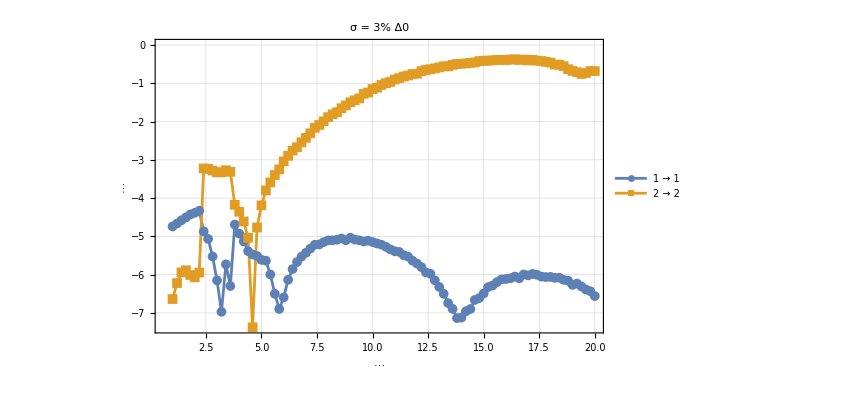

```mathematica
ListPlot[{gain3RADDπ,loss3RADDπ},PlotRange-> All,Frame->True,GridLines->Automatic, PlotLegends->Placed[{"1 → 1", "2 → 2"},{Right, Center}],PlotLabel->Style["σ = 3% Δ0",12], PlotMarkers->{Automatic,10},GridLinesStyle-> Thin, FrameLabel->{Style["",12],Style["(*GraphicsBox[{Thickness[0.017283097131005877`], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGI3IGYC4ur7P24Zcys68McG3DcqV3CA8ZWvPQpmmKPg
cPoMELxRcLijKbvm/2YFh7VCOnzp5xD8NVD+bSh/JgisRMiXHt7mOnOuAty8
Fd9eVpyZoOCwN7/m7cypCD5YX6eCw38QiIfKiyo4zACJW8o7uK85upzhh7RD
qwK76hkRWQg9RcwhIw0I2ETh/Aeu8Y6zCgXgfJDzz/Tww/n2JY61p2MQfNVP
Ki9nneRzCHl7+eOMhWIOMaoRMuf28Doo7FqwL3WdmEM6yPxlvA4gKu0Ygr8j
2Criv7o4nA/WVyPu8HXfx63p12DqxR1axGtZM9n4IPaZSDgwgECDqMPr4q2i
v7k1Ifa8E3UQ6fF6xfJFE+J+QTEHmXlxmqcNtBxEKieVnHWRgvPlQer7pOH8
A937mkweY/L1tVYKX1iC4EtMvcKZ8UgL4s4YBP88KHx0EHxwOFtIwfng+JCX
dPA5wW47+6qWQxUofWhLwPngcDguCOeD1d8XgPMh4cMPNw8WPjC+7xPPS6bC
CD4kvHgw+CycXfLJeQg+qn8R/ILlJRv++fPB+ZDwFMLgg935XxPOn9LeGnV5
j6bDfTQ+TB4cX92aUP8JOkiDzdN0kNkoNp/pAZvDm7bcbqPdEg5Lbi1/bMjM
5tAX0e3PKCDuEADy32VW1PTo888exn9T+zj7/JpfcH4zyH/HfmDwwfljpyic
b2IMAqIO66W36Z568xPOr3nR9Gvazr8IPii+Tss4wPiuoPi9IQvng9PXE1lI
unQQheY3OYh/pMUcum08d6V9UoCEi6KCQzinWLvxf2g+tUeUF8Igc1IQfFh5
AgCUldIw
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{14.435899999999998`, 8.57813}, {14.435899999999998`, 9.71094}, {13.696899999999998`, 10.5563}, {12.612499999999997`, 10.5563}, {11.0391, 10.5563}, {9.48906, 8.840629999999999}, {9.48906, 7.159379999999999}, {9.48906, 6.02656}, {10.2281, 5.1812499999999995`}, {11.3125, 5.1812499999999995`}, {12.898400000000002`, 5.1812499999999995`}, {14.435899999999998`, 6.8968799999999995`}, {14.435899999999998`, 8.57813}}, CompressedData["
1:eJxTTMoPSmViYGAQBmIQnZ4GBG7aDrc1Zdf8Z1ZygPHDOcXajfkVIfxjWg4i
lZNKzrLIOpw47LQ2856mQ4xqhMw5GSkHv4sTY/491nCouf/jlvFrMQfRHq9X
LFPUHc6AwBpRB5D2tGVqcH5m/ofWkyWqcL6RMRBMVnFoVWBXPTNFHM6HmCcF
50Psk3Vo4fVfP0VV1aH88DbXmX8VHKTmxWmevqDqsFZIhy9dT8nh19vXBywf
qzn4gtzFrOKw3aHp0XELDYefIPHFKg7GYKAJ54P9E6cF58P8HwHy/3plB/Tw
AQDksYAh
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}}, {{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAQBWIQ3e31isVkoZFDyNvLH2c4Sjvoa60UvjDFyGG9kA5f
ep2UQ/FW0d+n+4wczoCAj5RDI8vRfsN0I4cv+z5uTZ8m6cDtplrK9MrQoS+i
259RQNxhJghkGjrsCLaK+K8u5jB9An+VGTeCn54GBMsM4Pzk2DtuzB4GDiKV
k0rOpojD+fK7FuxLXScF54PtM5N1WHJ/H9+cxQYOqSBz3BQh5j0zcPiwaL3C
2QglhyeJC6+Z2Bs6RHCKtRuvV3bg918/JfWEocPPt68PWC5WgfA9jOD85S88
9P4LGsP5YPdbGjusBfl/nRKcD6Y7lRwK13TfzjAwdhAGuddEyQE9/ADhe49+

"], CompressedData["
1:eJxTTMoPSmViYGAwAmIQXbxV9Pfpc0YOwW8vf5zBKOTw51vpgzmKJg4RnGLt
xuuVHVSfNM87q2Xi4LHm6HKGHwi+1Lw4zdMCKjj5aWCg4qDxlnefAaeJQ8Nv
q4JzK1Qcpk/grzK7bQznL3/hofd/IoL/eUNA9qx0Y4cniQuvmeirOJw+7LQ2
M87YwWVCs1Bal7JDOshYM2OHC1fD3uhbqzh0e71iMXlo5DClvTXqsoyqA7//
+impHgj+Rr28xYx/DOD8H29fH7Bk1nf4sGi9wtkbinC+O8h/M2Tg/BBQeCwU
h4SHo4GDiTEIiDrclK5JNGI1hPOvC31yPL8MwYe4zwjKF3ewrYxYYZpr5LAj
2Criv7qEgzooPCyNHL7s+7g1/ZsInL9WSIcv/Z6IA7ebaimTlpFDjGqEzLk7
wpBw+G8IkbcThJj31tDh7Bkg4BGAyNcbOiy5tfyx4WEeSHgyGjrMmAkENzkc
IsS3X2ToM4Dz1UHx44XgnwCF7z19OD8V5H43fYczYPM5HdaDInStnkPJ8pIN
/85zOkiA4rlA34HHkc9rxkouB1ObvUHTFupD/BPGC+fv797XZJLMB+eD1b/k
d9jq0PToeAQ0vHcIOPjfAgboJT04/z8I2CP4D0AeWKDr0CJey5rZxg/nQ8zn
gfO3eW2wmFPJ4XAelC5m60HC/zMbJH0EGsD54PR5yxDOb2Q52m+43MjBvsSx
9vQdPgf0/AAA4EBVhA==
"]}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{23.579700000000003`, 2.3203099999999997`}, {23.579700000000003`, 2.7609399999999997`}, {22.4234, 2.7609399999999997`}, {22.4234, 13.799999999999997`}, {23.579700000000003`, 13.799999999999997`}, {23.579700000000003`, 14.240599999999999`}, {21.9828, 14.240599999999999`}, {21.9828, 2.3203099999999997`}, {23.579700000000003`, 2.3203099999999997`}}}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJZIGYC4hkzgeCkjYOJMQiIOsD4rQrsqmemiDmoPmme
dzYLwT9x2GltZpw1nH9DuibRKNTaYUewVcR/dXE4f62QDl/6PQk439xmb9C0
h5pwPgtnl3xynhacL9Lj9YqlRMuBx3/9lFQJBL9kq+jv0+esHJ4kLrxmcl7T
IT0NCMysHNaDHPZWw2GjXt5ixj8WGPzJ7a1Rl200HMSnXuHMcLKE89VB/rmF
4B9pWx5+qsnK4fzVsDf6txF8mPthfJj/wOFTaQX3v21lxArTXEs4/yQofPgw
+bDwlZ4Xp3k6wdKh6v6PW8beog71v60KznVYwfnPs7S/TX+L4IPdH2QN5zew
HO03LLeB89HjDwAjMb9b
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {{{40.773399999999995`, 8.27969}, {40.773399999999995`, 8.518749999999999}, {40.546899999999994`, 8.518749999999999}, {40.37969999999999, 8.518749999999999}, {33.882799999999996`, 8.518749999999999}, {33.715599999999995`, 8.518749999999999}, {33.4891, 8.518749999999999}, {33.4891, 8.27969}, {33.4891, 8.04219}, {33.715599999999995`, 8.04219}, {33.882799999999996`, 8.04219}, {40.37969999999999, 8.04219}, {40.546899999999994`, 8.04219}, {40.773399999999995`, 8.04219}, {40.773399999999995`, 8.27969}}}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJx11X0slHEcAPDzErOE0d3ZzJy4szvvLyHT9rXG81IbmcWkedudViiLeYmk
QiN1YZxLIitaM/rDREu1ZiyUpmxpi5ktwkQlee1+z8PvtzG/7fnjs+ee575v
v99jn3AhXGkgEAj0dFeC7tLXXT/bws5rM1nQqM1zfPfLoFceUN5fzcJVw547
nn4K7LiIcKd6RgFOk9frBrUshI3a5MaX7+0TfcZH731WgGFjeYBeGbGmRrfS
iFVo1VHY8W+HnZUFxI+naLfNtN2ufejQuZZE7K54YjXkqIABtHKJ09uFq/1V
xAcXgz6o/ux27qKuECtybC7/DuIOuDbRq5FDdlTz4cFfFGyilS+HyfiGEZ95
CiqKC6OHA+Vwi/1h6GNPwWxRSqnXC2tINvlXn2RFwe2o0lA9CzGYhrZWKi0o
KJQYSwcqRcCivB6FYIdIM/S1N4njUD2ydxuVsaZTiO3jjZaQj6eY2H+kJ8VH
TfxF1yavFuIslE9/COSMLY96HxfCldWAi++niLn3tVLYwSi+IeLt+my/7xKq
t4jGrlwyitU4Ej8t/XpW4Lfbkq76bqWZCHs7X7ughcQBV+Kipsh3XqbEXFsq
SD25+NS6fqL4Zogj5oYXNA1i7BZLF7Okb2L8vAAtsMbz8rt7oT2pyprv1zIF
kSaiYu/YQyBD811CY3P5bhBzc2HMgPmZsDGvv/bYSjTnIfY77kv4/bGPgbHg
2CBtg4TvzzoNl1H8NhIY6zar9V6hgSuXgQTyUH+WaShD89Rmt6e5+Ttth+Nz
WnSc1srt+HkxYbCPo/kTEnP9FjP4eUvUX1uGz89cwvcjg4Gpc85L1fel2Nz+
bJfy85/G8PtpVAp1gS6ftCpiLr4o4s7RknVlJAO+gS/Dq95sPX9y6370lj0Z
aF6azhpQO8DsgW6PGkuGr6O5A///ZTT2SkxKz4Y+sau6ftlTReP9+cwttVEv
nebPK0sFP2+ZND4PuHq0Ezeh86WAwc5H8QOLXYzmMYaFlbmZ10eOybHXlzLG
a+86YXPnUjIx/SrP1v+7DLjzN5LlzzNKBu4o3lMs9HU9LzPykMEayiechYko
ccfHcSk29/te4gJ0XlVLYR7VJ5oFDxTfDSm/vxOJH6B+pBJz+zOdxf3c+T34
D6pZmus=
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{55.44839999999999, 2.3203099999999997`}, {55.44839999999999, 14.240599999999999`}, {53.849999999999994`, 14.240599999999999`}, {53.849999999999994`, 13.799999999999997`}, {55.0063, 13.799999999999997`}, {55.0063, 2.7609399999999997`}, {53.849999999999994`, 2.7609399999999997`}, {53.849999999999994`, 2.3203099999999997`}, {55.44839999999999, 2.3203099999999997`}}}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{86.78978331257782, 24.508064757160646`},PlotRange->{{0., 57.86}, {0., 16.34}}])", 12]}, LabelStyle->{Bold,12},Joined->True]
```

### 11a

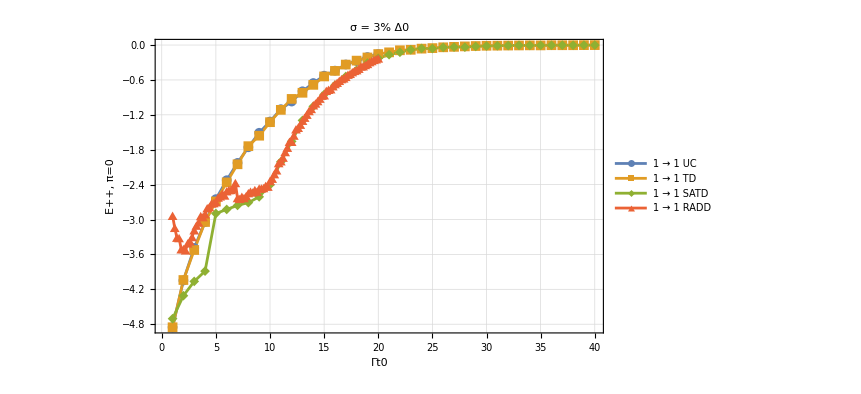

```mathematica
ListPlot[{loss3UC,loss3TD,loss3SATD,gain3RADD},PlotRange-> All,Frame->True,GridLines->Automatic, PlotLegends->Placed[{"1 → 1 UC","1 → 1 TD","1 → 1 SATD","1 → 1 RADD"},{Right, Center}],PlotLabel->Style["σ = 3% Δ0",12], PlotMarkers->{Automatic,10},GridLinesStyle-> Thin, FrameLabel->{Style["Γt0",20],Style["E++, π=0", 20]}, LabelStyle->{Bold,12},Joined->True]
```

### 11b

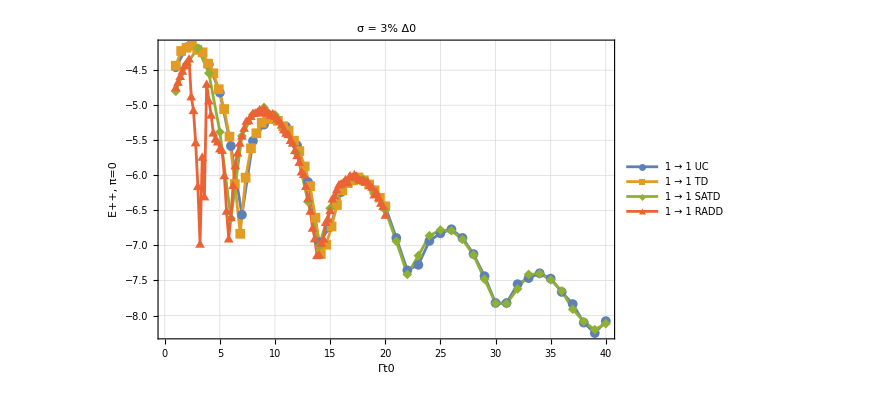

```mathematica
ListPlot[{loss3UCπ,loss3TDπ,loss3SATDπ,gain3RADDπ},PlotRange-> All,Frame->True,GridLines->Automatic, PlotLegends->Placed[{"1 → 1 UC","1 → 1 TD","1 → 1 SATD","1 → 1 RADD"},{Right, Center}],PlotLabel->Style["σ = 3% Δ0",12], PlotMarkers->{Automatic,10},GridLinesStyle-> Thin, FrameLabel->{Style["Γt0",20],Style["E++, π=0", 20]}, LabelStyle->{Bold,12},Joined->True]
```

### 11c

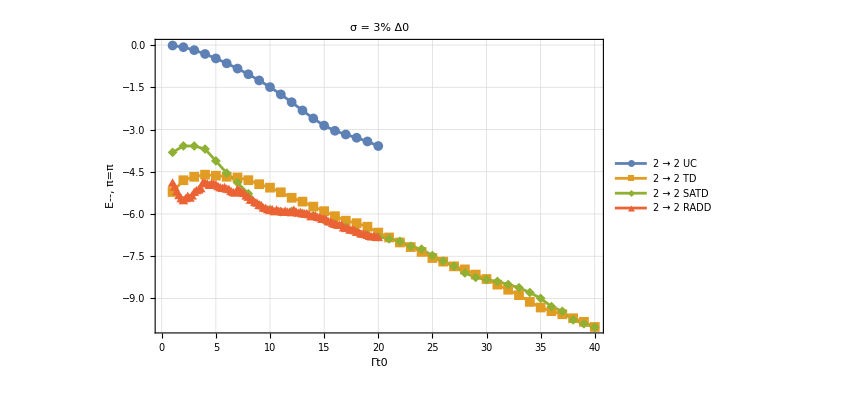

```mathematica
ListPlot[{gain3UC,gain3TD,gain3SATD,loss3RADD},PlotRange-> All,Frame->True,GridLines->Automatic, PlotLegends->Placed[{"2 → 2 UC","2 → 2 TD","2 → 2 SATD","2 → 2 RADD"},{Right, Center}],PlotLabel->Style["σ = 3% Δ0",12], PlotMarkers->{Automatic,10},GridLinesStyle-> Thin, FrameLabel->{Style["Γt0",20],Style["E--, π=π", 20]}, LabelStyle->{Bold,12},Joined->True]
```

### 11d

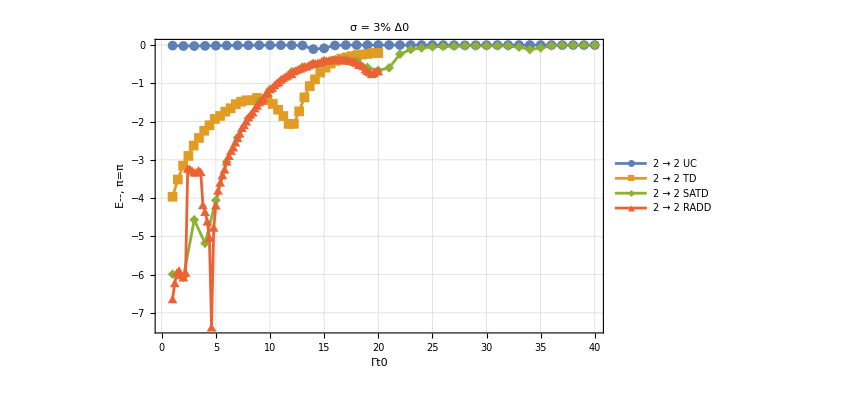

```mathematica
ListPlot[{gain3UCπ,gain3TDπ,gain3SATDπ,loss3RADDπ},PlotRange-> All,Frame->True,GridLines->Automatic, PlotLegends->Placed[{"2 → 2 UC","2 → 2 TD","2 → 2 SATD","2 → 2 RADD"},{Right, Center}],PlotLabel->Style["σ = 3% Δ0",12], PlotMarkers->{Automatic,10},GridLinesStyle-> Thin, FrameLabel->{Style["Γt0",20],Style["E--, π=π", 20]}, LabelStyle->{Bold,12},Joined->True]
```

## UC,TD, SATD & RADD RMS for ϕ=(0,π) (Fig. 12)

### Functions used for numerics

```mathematica
σx=({{0, 1}, {1, 0}});
σy=({{0, -ⅈ}, {ⅈ, 0}});
σz=({{1, 0}, {0, -1}});
```

```mathematica
(*choosen contour*)
ΔCircPath:=Function[{Δ0,φ,x},
Δ0 Sin[2 π x+φ]
];

ΩCircPath:=Function[{Δ0,Ω0,φ,x},
Ω0 + Δ0 Cos[2π x+φ]
];
(*time dependant parametrization of contour for single (ωCirc1) and double loop (ωCirc1DL)*)
ωCirc1:=#1(6(#3/#2)^5-15(#3/#2)^4+10(#3/#2)^3)&;
ωCirc1DL:=(ωCirc1[#1,#2,#3]UnitStep[#2-#3]+((#1)+ωCirc1[#1,#2,#3-#2])UnitStep[#3-#2])&;
```

```mathematica
(*constucting the holomorphic eigenvalue, works for a double loop*)
EigCircPath:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2)

];
```

```mathematica
(*constucting thederivative of the holomorphic eigenvalue, works for a double loop*)
EigDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])((2 ⅈ π Δ0 (Γ Cos[φ+2 π ω[dir,t0,t]]+2 ⅈ Ω0 Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,1][ω][dir,t0,t])/(√(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])))
];
```

```mathematica
(*constucting the holomorphic pseduo rotation angle into the adiabatic frame, works for a double loop*)
θDiagCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
-2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)+(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]
];
```

```mathematica
(*constucting the derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(4 π Δ0 (2 Δ0+2 Ω0 Cos[φ+2 π ω[dir,t0,t]]+ⅈ Γ Sin[φ+2 π ω[dir,t0,t]]))/(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])Derivative[0,0,1][ω][dir,t0,t]
];
```

```mathematica
(*constucting the 2nd derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDDotCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(4 π Δ0 (2 π (Γ^2+4 (Δ0-Ω0) (Δ0+Ω0)) (-ⅈ Γ Cos[φ+2 π ω[dir,t0,t]]+2 Ω0 Sin[φ+2 π ω[dir,t0,t]]) (Derivative[0,0,1][ω][dir,t0,t])^2+(4 Δ0 (-Γ^2+2 Δ0^2+4 Ω0^2)-2 Ω0 (Γ^2-4 (3 Δ0^2+Ω0^2)) Cos[φ+2 π ω[dir,t0,t]]+2 Δ0 (Γ^2+4 Ω0^2) Cos[2 (φ+2 π ω[dir,t0,t])]+ⅈ Γ (-Γ^2+4 (3 Δ0^2+Ω0^2)+16 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]) Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,2][ω][dir,t0,t]))/(Γ^2-4 (Δ0^2+Ω0^2)-8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]-4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])^2
];
```

```mathematica
(*SATD correction fields in the lab frame using the holomorphic functions*)
gxCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
Cos[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]/2((-EigDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]+ EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t] θDiagDDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])/(EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]^2+θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]^2))
];
gzCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
Sin[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]/2(-((-EigDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]+ EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t] θDiagDDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])/(EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]^2+θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]^2)))
];
```

```mathematica
(*RADD correcting function*)
F3:=Function[{A,σ,n,t,t0},
A Exp[-(((t-t0/2)/σ)^2)^n]
];
(*RADD correcting function derivative*)
F3dot:=Function[{A,σ,n,t,t0},
-(4 A ⅇ^(-((t-t0/2)^2/σ^2)^n) n ((t-t0/2)^2/σ^2)^n)/(2 t-t0)
];
(*the holomorphic SATD pseudo roation angle with the correct phases applied at the correct times*)
μ:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t,ts,ph},
-ArcTan[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])/((1+F3[A,σ,n,t,t0])EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])]+Total[Map[{ph[[#]]UnitStep[Boole[ts[[#,1]]≤ t<ts[[#,2]]]]}&,DeleteDuplicates[Flatten[Map[Position[ts,Flatten[Select[ts,#[[1]]≤ t<#[[2]]&][[#]]]]&,Range[1,Length[Select[ts,#[[1]]≤ t<#[[2]]&]]]],2]]],2]
];
(*the holomorphic SATD pseudo roation angle derivative*)
μdot:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t},
(2 ((1+F3[A,σ,n,t,t0]) θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t] EigDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]+EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t] (θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t] F3dot[A,σ,n,t,t0]-(1+F3[A,σ,n,t,t0]) θDiagDDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])))/(4 EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]^2 (1+F3[A,σ,n,t,t0])^2+θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]^2)
];
(*generalized gx correction in the lab frame, assumes any μ dressing angle for SATD*)
gx2:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t,ts,ph},

1/2 (-2 ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]+Cot[μ[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t,ts,ph]]Sin[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]+Cos[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] μdot[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t])

];
(*generalized gz correction in the lab frame, assumes any μ dressing angle for SATD*)
gz2:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t,ts,ph},
1/2 (ⅈ Γ+2 ΔCircPath[Δ0,φ,ω[dir,t0,t]]+Cos[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]Cot[μ[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t,ts,ph]] θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]-Sin[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] μdot[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t])

];
```

```mathematica
(*finding the times when real part of the SATD pseudo rotation angle goes to 0*)
tb0sRetimes:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{tbtest,index},
(*making a list of points to determine any sudden sign changes between two neighboring points*)
tbtest=Table[{t,N[Re[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])/EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]},{t,0,t0,t0/99}];
(*checking the sign difference between two points, then assinging an index value to the points of interest*)
index=Sort[Join[Flatten[Position[Differences[Sign[tbtest[[2;;,2]]]],2]+1],Flatten[Position[Differences[Sign[tbtest[[2;;,2]]]],-2]+1]]];
(*using the points of interest to find the roots of the function - using these "known" intervals where the sign change occurs reduces overall searching time for Find Root*)
Map[t/.FindRoot[Re[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])/EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]==0,{t,tbtest[[#,1]]},Method->"AffineCovariantNewton"]&,index]]
];
```

```mathematica
(*determining how many times the SATD pseduo rotation angle crosses the branch cut for 1 loop*)
t0CriticalCheck:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,BrCutCrossTimes},
Module[{tbtest,index,tb0sReCheckt0,tb0sImt0,tb0sRefinalt0,tb0sImfinalt0},
(*using the output of "tb0sRetimes" to check that the Re[μ]=0 and Im[μ]<0 to qualify as a branch cut crossing.*)
tb0sReCheckt0=Select[Select[Chop[Map[{Re[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#])/EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#]],#}&,BrCutCrossTimes],10^-16], #[[1]]== 0&],0<#[[2]]< t0 &][[;;,2]];
tb0sImt0=Map[Im[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#])/EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#]]&,tb0sReCheckt0];
(*making a list of the imaginary parts that satisfy Im[μ]<0 given the times from the output of "tb0sRetimes"*)
tb0sImfinalt0=Select[Map[{tb0sReCheckt0[[#]],tb0sImt0[[#]]}&,Range[1,Length[tb0sImt0]]],#[[2]]≥ 1|| #[[2]]≤ -1  &][[;;,2]];
(*# of times branch cut is crossed*)
Length[tb0sImfinalt0]
]
];
```

```mathematica
(*checking if the times found from the function "tb0sRetimes" correspond to branch cut crossings*)
tb0sRefinalList:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,tb0sRe},
Module[{tb0sReCheck,tb0sIm,tb0sImfinal,tb0sRefinal},
(*using the output of "tb0sRetimes" to check that the Re[μ]=0 and Im[μ]<0 to qualify as a branch cut crossing.*)
tb0sReCheck=Select[Select[Chop[Map[{Re[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#])/((1+F3[A,σ,n,#,t0])EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#])],#}&,tb0sRe],10^-4], Abs[#[[1]]]== 0&],0<#[[2]]< 2t0 &][[;;,2]];
tb0sIm=Map[Im[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#])/((1+F3[A,σ,n,#,t0])EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,#])]&,tb0sReCheck];
(*making a list of the real parts that satisfy Re[μ]=0 and Im[μ]<0*)
tb0sRefinal=Sort[Select[Map[{tb0sReCheck[[#]],tb0sIm[[#]]}&,Range[1,Length[tb0sIm]]],#[[2]]≥ 1|| #[[2]]≤ -1  &][[;;,1]]]
]
];
```

```mathematica
(*determining the times when the branch cut is crossed and the accompanying phase corrections*)
FinalTimesPhases:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,tb0sRefinal},
Module[{α,β,PhaseCond,Time,FinalTime,FinalPhases},
(*using the output from "tb0sRefinalList", we check the value of μ just before and after the given times to determine what sign the phase shift needs to be and at what exact time to apply it; we do not want to double count any times, so based of the FindRoot results we determine a hard cutoff when to apply the phase. We use 10^-6 as the limit of our precision.*)
(*checking just before*)
α=Map[
Re[-ArcTan[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]])])/((1+F3[A,σ,n,(tb0sRefinal[[#]]),t0])EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]])])]]-Re[-ArcTan[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]]-10^-6)])/((1+F3[A,σ,n,(tb0sRefinal[[#]]-10^-6),t0])EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]]-10^-6)])]]&,Range[1,Length[tb0sRefinal]]];
(*checking just after*)
β=Map[N[Re[-ArcTan[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]]+10^-6)])/((1+F3[A,σ,n,(tb0sRefinal[[#]]+10^-6),t0])EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]]+10^-6)])]]-Re[-ArcTan[(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]])])/((1+F3[A,σ,n,(tb0sRefinal[[#]]),t0])EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,(tb0sRefinal[[#]])])]]]&,Range[1,Length[tb0sRefinal]]];
(*assigning the necessary phase at a given branch cut crossing time depending on if α is positive or negative π. If discontinuity occurs at time given by "tb0sRefinalList", then set hard cutoff at that time. If it occurs just after at the time given by "tb0sRefinalList", set it just after.*)
PhaseCond=Map[If[Abs[ α[[#]]] >1,{α[[#]],tb0sRefinal[[#]]}, {β[[#]],tb0sRefinal[[#]]+10^-6}]&,Range[1,Length[tb0sRefinal]]];
(*making a list of the branch cut times and phases when the phases need to be applied (FinalTime), and the accompanying value of the phases(FinalPhases)*)
Time=PhaseCond[[;;,2]];
FinalTime=Partition[Insert[Insert[Time,0,1],2t0,-1],2,1];
FinalPhases=Insert[-Map[Total[Map[N[PhaseCond[[;;,1]][[##]]]&,Range[1,#]]]&,Range[1,Length[Time]]],0,1];
(*outputing a combined list FinalTime and FinalPhases*)
{FinalTime,FinalPhases}
]
];
```

```mathematica
(*creating a list of times and phases which need to be applied to produce the holomorphic angle μ*)
μF3CircPathCorr:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,BrCutCrossTimes},
Module[{tb0sRefinal},
(*getting a list of branch cut times when phases need to be applied*)
tb0sRefinal=tb0sRefinalList[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,BrCutCrossTimes];
(*if the list is empty, return{{0,2t0}},{0}} indicating no corrections need to be applied*)
If[Length[tb0sRefinal]==0,List[{{0,2t0}},{0}],
(*otherwise determine the list of times and phases that need to used to build the holomorphic angle μ*)
FinalTimesPhases[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,tb0sRefinal]
]
]
];
```

```mathematica
(*finding the RMS value for the RADD correction*)
MinimizeGxGz2:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,BrCutCrossTimes}, 
Module[{FnTs,FnPh},
(*getting the list of times and phases needed to construct the holomorphic dressing angle*)
{FnTs,FnPh}=μF3CircPathCorr[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,BrCutCrossTimes];
(*finding the RMS value for RADD*)
Sqrt [NIntegrate[1/t0(Abs[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]+gx2[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t,FnTs,FnPh]]^2+Abs[-(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)+gz2[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t,FnTs,FnPh]]^2),{t,0,t0},Method->{"LocalAdaptive","SymbolicProcessing"-> 0}]]
]
];
```

```mathematica
(*finding the maximum amplitude for the RADD gx2 and gz2 control fields*)
GxGzRMSMax2:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,BrCutCrossTimes}, 
Module[{T,P},
(*getting the list of times and phases needed to construct the holomorphic dressing angle*)
{T,P}=μF3CircPathCorr[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,BrCutCrossTimes];
(*finding the maximum amplitude from a table of values for gx2 and gz2*)
{Max[Select[N[Table[Abs[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]+gx2[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t,T,P]],{t,t0/100,99t0/100,t0/300}]],NumericQ]],
Max[Select[N[Table[Abs[-(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)+gz2[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t,T,P]],{t,t0/100,99t0/100,t0/300}]],NumericQ]]}
]
];
```

```mathematica
(*brute force search for optimized RADD parameter values that minimuze RMS value*)
RADDSearchPert0:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},

Module[{Amin,Amax, StepsA, δA, σmin,σmax, Stepsσ, δσ, nmin, nmax, δn,PossibleZeroCrossingTimes, A1to5pos,A1to5posrefined,α,β,η,αα,ββ,ηη},
(*setting initial search ranges for A, σ, and n*)
Amin=1/10;
Amax=10;
StepsA=10;
δA=(Amax-Amin)/(StepsA-1);

σmin=t0/25;
σmax=t0/3;
Stepsσ=10;
δσ=(σmax-σmin)/(Stepsσ-1);

nmin=1;
nmax=7;
δn=1;
(*getting possible branch cut times*)
PossibleZeroCrossingTimes=tb0sRetimes[Δ0,Ω0,Γ,φ,ω,dir,t0];
(*if a given set of  A, σ, and n yields a non-valid STA, then ignore the combination and produce the next set of variables in the search. Only if the STA is valid to we find the RMS value and compare it lateron*)
If [Mod[t0CriticalCheck[Δ0,Ω0,Γ,φ,ω,dir,t0,PossibleZeroCrossingTimes],2]!=0,Null,
(*finding the RMS value and storing the  A, σ, and n values that minimize the RMS*)
A1to5pos=Table[{A,σ,n,MinimizeGxGz2[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,PossibleZeroCrossingTimes]},{A,Amin,Amax,δA},{σ,σmin,σmax,δσ},{n,nmin,nmax,δn}];

α=Rationalize[Select[Flatten[A1to5pos,2],#[[4]]==Min[Flatten[A1to5pos,2][[;;,4]]]&][[1,1]]];
β=Rationalize[Select[Flatten[A1to5pos,2],#[[4]]==Min[Flatten[A1to5pos,2][[;;,4]]]&][[1,2]]];
η=Rationalize[Select[Flatten[A1to5pos,2],#[[4]]==Min[Flatten[A1to5pos,2][[;;,4]]]&][[1,3]]];
(*doing the same search but now refining the search parameters to be in the negiborhood of the intial values found for  A, σ, and n in the previous step. this is a hyperfine search so to speak. We store the final values of  A, σ, and n*)
A1to5posrefined=Table[{A,σ,n,MinimizeGxGz2[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,PossibleZeroCrossingTimes]},{A,α-(Amin 9/10),α+(Amin 9/10),Amin/5},{σ,β-t0/100,β+t0/100,t0/500},{n,η-9/10,η+9/10,1/10}];

αα=Rationalize[Select[Flatten[A1to5posrefined,2],#[[4]]==Min[Flatten[A1to5posrefined,2][[;;,4]]]&][[1,1]]];
ββ=Rationalize[Select[Flatten[A1to5posrefined,2],#[[4]]==Min[Flatten[A1to5posrefined,2][[;;,4]]]&][[1,2]]];
ηη=Rationalize[Select[Flatten[A1to5posrefined,2],#[[4]]==Min[Flatten[A1to5posrefined,2][[;;,4]]]&][[1,3]]];

(*outputting the  A, σ, and n values that minimize the RMS, the RMS value itself, and the maximum amplitudes for the associated control fields with minimum RMS*)
Flatten[{t0,αα,ββ,ηη,MinimizeGxGz2[Δ0,Ω0,Γ,φ,ω,dir,t0,αα,ββ,ηη,PossibleZeroCrossingTimes],GxGzRMSMax2[Δ0,Ω0,Γ,φ,ω,dir,t0,αα,ββ,ηη,PossibleZeroCrossingTimes]}]]
]
];
```

### Data for RADD Optimization search

φ=0 case

```mathematica
Γ=1;
Δ0=1/2 Γ;
Ω0=1/2 Γ;
φ=0;
ω=ωCirc1DL;
dir=1;
AbsoluteTiming[Dataphi0=ParallelMap[RADDSearchPert0[Δ0,Ω0,Γ,φ,ω,dir,#/Γ]&,Range[1,20,1/5]];]
```

```mathematica
(*elements listed as {t0, A, ν (called σ in code), n, RMS value, Maximum of gx_mod, Maximum of gz_mod} *)
```

```mathematica
Dataphi0={{1,899/100,2659/13500,4/5,5.14257465047306,7.830811557929698,6.416899246682768},{6/5,679/100,2713/11250,9/10,4.3052166010512725,6.733771417418353,5.253451543478002},{7/5,569/100,4606/16875,9/10,3.691748423905285,5.7948557116304915,4.505129621701359},{8/5,113/20,4492/16875,4/5,3.2186241136767966,4.803854861275129,4.096067861578489},{9/5,459/100,2273/7500,9/10,2.8694105669044663,4.309161105315162,3.5944912724246154},{2,453/100,133/450,4/5,2.591909157941355,3.875537904424736,3.314188424013389},{11/5,349/100,4763/13500,1,2.3653125703798143,3.5039661358672136,2.937002257835975},{12/5,331/100,133/375,1,2.178676765992632,3.15238437581109,2.7416165817822846},{13/5,331/100,403/1125,9/10,2.027187783748179,2.8577345706128874,2.593753276682501},{14/5,239/100,3031/6750,6/5,1.897344962632379,2.6711067942790048,2.2910961611122067},{3,237/100,319/750,11/10,1.7815010340874895,2.5038740250257057,2.1850688858889713},{16/5,221/100,496/1125,11/10,1.686446640097023,2.3241524810326673,2.0627329547842552},{17/5,221/100,391/900,1,1.6067079359810215,2.194971558835207,1.975756828242822},{18/5,221/100,311/750,9/10,1.5398991419778585,2.153747432091916,1.8813075356836577},{19/5,129/100,12293/22500,17/10,1.478815628042432,2.086407666575176,1.6377670044422308},{4,129/100,611/1125,8/5,1.4182441205557077,1.8834223745626364,1.5905363684172626},{21/5,129/100,161/300,3/2,1.3680165728708247,1.7543241918365353,1.5475391194505967},{22/5,119/100,253/450,3/2,1.3256512047912972,1.6580707585085468,1.4787323275099769},{23/5,119/100,7153/13500,7/5,1.2885618092804039,1.6305874697229854,1.4384097760515497},{24/5,111/100,622/1125,7/5,1.2549543081616414,1.534017608046871,1.382713261638761},{5,111/100,737/1350,13/10,1.226410098771716,1.479670989101558,1.3459338870159006},{26/5,111/100,18109/33750,6/5,1.2014973428932392,1.4346392994027213,1.307415963670841},{27/5,111/100,328/625,11/10,1.1795705339442368,1.39327714345922,1.2667964155903089},{28/5,111/100,1799/3375,11/10,1.1602881726196455,1.308445583922176,1.2430225676882423},{29/5,111/100,6467/13500,9/10,1.143000945014939,1.341200410285925,1.1751461237226928},{6,111/100,544/1125,9/10,1.1270682722205647,1.2627549509048763,1.151662048506368},{31/5,111/100,1519/3375,4/5,1.1130053254418788,1.2409021623784542,1.1022615602694834},{32/5,111/100,7408/16875,4/5,1.1001555211365948,1.1968665893844188,1.0747690153528986},{33/5,111/100,1859/4500,7/10,1.088533935598464,1.1486825074743097,1.0461659749165444},{34/5,111/100,2873/6750,4/5,1.0784905903203144,1.1036439920833387,1.050212892088008},
{7,19/100,497/675,39/10,1.0625153481686964,1.1829374776399135,0.8704900314203157},{36/5,19/100,1393/1875,37/10,1.0512679264812823,1.1182908114667367,0.8570982173021825},{37/5,19/100,49543/67500,7/2,1.0416633719965984,1.058795816087011,0.8459444131587927},{38/5,19/100,4883/6750,33/10,1.0334181447909154,1.0039197487101748,0.8361716814014373},{39/5,19/100,3341/4500,31/10,1.0263548163768923,1.0000974303805166,0.826358009641652},{8,19/100,514/675,31/10,1.020347208804992,1.0000842660315306,0.8176677316583832},{41/5,17/100,10537/13500,31/10,1.0151100024228847,1.0000728258755713,0.8012635356825508},{42/5,17/100,3808/5625,27/10,1.009910575445453,1.0000628600274726,0.7934031599589462},{43/5,13/100,11696/16875,31/10,1.0055857881033197,1.0000551883871416,0.7711587873924172},{44/5,11/100,11671/16875,33/10,1.0016809230386814,1.0000485385389524,0.7563944734944827},{9,9/100,517/750,7/2,0.9981650610851556,1.0000426802149074,0.7417762902018624},{46/5,7/100,23161/33750,37/10,0.9949997365934106,1.000037508608069,0.7272369461320506},{47/5,1/20,2303/3375,39/10,0.9921522430079016,1.000032934432042,0.7126995572674604},{48/5,3/100,12/25,19/10,0.9897132305755489,1.000028881373767,0.6865165756803826},{49/5,1/100,49/100,19/10,0.987334350031673,1.0000258146857648,0.679453106770149},{10,1/100,1/2,19/10,0.9852574234264256,1.000023079318399,0.6750902756414522},{51/5,1/100,51/100,19/10,0.9834470775040678,1.0000206319894682,0.6711144167111794},{52/5,1/100,39/125,4/5,0.9818641313866641,1.0000184388511482,0.6667646919568819},{53/5,1/100,159/500,9/10,0.9804751354711089,1.0000164705156827,0.6633383917451869},{54/5,1/100,81/250,9/10,0.9792600756582555,1.000014701402503,0.660288520681148},{11,1/100,33/100,1,0.9781966413099381,1.0000131091903768,0.6573949601714414},{56/5,1/100,42/125,1,0.9772654207933991,1.0000117393616978,0.6550407413942504},{57/5,1/100,171/500,1,0.9764500250832855,1.000010666371626,0.6529371518775375},{58/5,1/100,87/250,11/10,0.975736104422084,1.0000096925428035,0.6509438668379872},{59/5,1/100,177/500,11/10,0.9751112820616189,1.0000088075944709,0.6491345049939101},{12,1/100,9/25,11/10,0.9745648865643042,1.0000080024449662,0.6474508191982912},{61/5,1/100,183/500,11/10,0.974087585900622,1.0000072690559534,0.6460432458759838},{62/5,1/100,93/250,6/5,0.9736712039321221,1.0000066002989385,0.6448561925561246},{63/5,1/100,189/500,6/5,0.9733086803869683,1.0000059898405989,0.6437609771866447},{64/5,1/100,48/125,6/5,0.9729938030715163,1.0000054320440313,0.6427576995808971},{13,1/100,39/100,6/5,0.972721119092242,1.0000049218835112,0.6420813129469192},{66/5,1/100,99/250,6/5,0.9724858373016615,1.0000044548707454,0.6433108016164207},{67/5,1/100,201/500,6/5,0.9722837404552729,1.0000040941493245,0.645213328221201},{68/5,1/100,51/125,13/10,0.9721110980020462,1.0000037804679829,0.6470364797735756},{69/5,1/100,207/500,13/10,0.9719646340883097,1.0000034912251095,0.6487972536001005},{14,1/100,21/50,13/10,0.9718414500642927,1.0000032242777723,0.6504820771624418},{71/5,1/100,213/500,13/10,0.9717389730514893,1.0000029776950201,0.6520952027839338},{72/5,1/100,54/125,13/10,0.9716549209482247,1.0000027497344655,0.6536405959191489},{73/5,1/100,219/500,13/10,0.9715872669329322,1.000002538821725,0.6551219572245804},{74/5,1/100,111/250,13/10,0.9715342086926152,1.0000023435323366,0.6565427427909027},{15,1/100,9/20,13/10,0.9714941416915757,1.0000021625758222,0.6579061826913645},{76/5,1/100,57/125,13/10,0.9714656359032371,1.000001994781625,0.6592152979897264},{77/5,1/100,231/500,13/10,0.9714474155170938,1.0000018390866736,0.6604729163401617},{78/5,1/100,117/250,13/10,0.9714383412073897,1.0000016945243726,0.6616816863009384},{79/5,1/100,237/500,13/10,0.971437394612264,1.0000015602148355,0.6628440904736151},{16,1/100,12/25,13/10,0.9714436647242448,1.0000014353562117,0.6639624575699968},{81/5,1/100,243/500,13/10,0.9714563359367705,1.0000013192169703,0.6650389735002494},{82/5,1/100,123/250,13/10,0.9714746775282745,1.0000012296069927,0.6660756915673725},{83/5,1/100,249/500,13/10,0.9714980343965509,1.0000011535439894,0.6670745418456722},{84/5,1/100,63/125,13/10,0.9715258188824621,1.0000010823426413,0.6680373398139289},{17,1/100,51/100,13/10,0.9715575035444431,1.0000010156513477,0.6689657943076017},{86/5,1/100,129/250,13/10,0.9715926147642636,1.0000009531472933,0.6698615148486109},{87/5,1/100,261/500,13/10,0.97163072708075,1.0000008945338086,0.6707260184059411},{88/5,1/100,66/125,13/10,0.971671458161992,1.000000839537999,0.6715607356355047},{89/5,1/100,267/500,13/10,0.9717144643384501,1.0000007879086117,0.6723670166433203},{18,1/100,27/50,13/10,0.9717594366295095,1.0000007394141142,0.6731461363120964},{91/5,1/100,273/500,13/10,0.971806097204801,1.0000006938409622,0.6738992992276958},{92/5,1/100,69/125,13/10,0.9718541962290692,1.0000006509920356,0.6746276442386924},{93/5,1/100,279/500,13/10,0.9719035090459486,1.0000006106852242,0.6753322486792633},{94/5,1/100,141/250,13/10,0.9719538336615084,1.00000057275215,0.6760141322829668},{19,1/100,57/100,13/10,0.972004988493345,1.0000005370370089,0.6766742608125221},{96/5,1/100,72/125,13/10,0.972056810355192,1.000000503395519,0.6773135494284934},{97/5,1/100,291/500,13/10,0.9721091526506405,1.0000004716939703,0.6779328658177752},{98/5,1/100,147/250,13/10,0.9721618837527758,1.0000004418083568,0.6785330331009555},{99/5,1/100,297/500,13/10,0.9722148855492697,1.0000004136235894,0.6791148325359854},{20,1/100,3/5,13/10,0.9722680521349057,1.00000038703278,0.6796790060340823}};
```

φ=π case

```mathematica
Γ=1;
Δ0=1/2 Γ;
Ω0=1/2 Γ;
φ=π;
ω=ωCirc1DL;
dir=1;
DataphiPi=ParallelMap[RADDSearchPert0[Δ0,Ω0,Γ,φ,ω,dir,#/Γ]&,Range[1,20,1/5]];
```

```mathematica
(*elements listed as {t0, A, ν (called σ in code), n, RMS value, Maximum of gx_mod, Maximum of gz_mod} *)
```

```mathematica
DataphiPi={{1,3/20,4087/13500,36/5,2.9876146967842514,6.829489175689102,0.6102372850280201},{6/5,1/20,751/2250,69/10,2.573179941519674,5.880076609875356,0.5484685309416019},{7/5,1/100,21/500,4/5,2.2953655226892162,5.161364487018862,0.5105810236647423},{8/5,1/100,6/125,4/5,2.110354431374454,4.72751040011169,0.5663514682542413},{9/5,1/100,27/500,4/5,1.992575425656185,4.540499822092567,0.6430232203470249},{2,1/100,3/50,4/5,1.9292111988279537,4.573969089686416,0.7415289230398271},{11/5,1/100,33/500,4/5,1.9172069028602243,4.860180710976165,0.8741234068492572},{12/5,119/100,839/1125,11/2,1.7759532399705036,2.7794362293856976,1.7929310543978743},{13/5,111/100,26741/33750,26/5,1.6496136669558807,2.3914445840118423,1.6562267317670074},{14/5,111/100,28231/33750,43/10,1.565765246391496,2.0085811822493476,1.5418434015325029},{3,111/100,157/180,29/10,1.507404291771618,1.8411281243668196,1.4027124418327637},{16/5,111/100,3004/3375,3/2,1.4588475688276554,1.8635094557783267,1.272560627381716},{17/5,111/100,3757/4500,3/10,1.376318895423337,2.174820421580452,1.2628961423518317},{18/5,111/100,203/250,3/10,1.3091937819071975,1.8817228416004672,1.1899073131836853},{19/5,19/100,2983/2700,79/10,1.2016633025418424,2.448196673292339,1.1898566378906357},{4,19/100,157/135,79/10,1.1139800434357336,2.0397863677210673,1.1018394269802072},{21/5,19/100,1099/900,79/10,1.0505688503704733,1.7463287864034964,1.0395217478849392},{22/5,19/100,1727/1350,79/10,1.0036299753179743,1.5270281226534543,0.9934836052513553},{23/5,3/20,83881/67500,79/10,0.9644205389727405,1.432284930463449,0.9448784093918734},{24/5,9/100,1448/1125,79/10,0.9292355454968073,1.4005202621623893,0.907203912684063},{5,1/20,1783/1350,79/10,0.897258162619632,1.337021825267997,0.8733456637303769},{26/5,1/100,39/250,1,0.868728129148627,1.3095184744255417,0.8443311747641901},{27/5,1/100,81/500,1,0.842759235708852,1.1832148844451527,0.8176598171487283},{28/5,1/100,21/125,1,0.822145214699251,1.0805431355106359,0.7963200198223265},{29/5,1/100,87/500,1,0.805643364977087,0.9959752394258107,0.7787013222962221},{6,1/100,9/50,1,0.7923273161937894,0.9250509370327878,0.7639354840240123},{31/5,1/100,93/500,1,0.7815152201672708,0.8792245750085389,0.7514090755078123},{32/5,1/100,24/125,1,0.7726873454333691,0.8845986494913489,0.7406697667974232},{33/5,1/100,99/500,1,0.7654448629412638,0.8896975891122363,0.7313772136113694},{34/5,1/100,51/250,1,0.7594784643000736,0.8945352854599352,0.7235982773740007},{7,1/100,21/100,1,0.7545460081768917,0.8991253227401794,0.7168304068640499},{36/5,1/100,27/125,1,0.7504563338837137,0.9034808839284947,0.710844003399346},{37/5,1/100,111/500,1,0.747057373877149,0.9076146838090877,0.7055180529296381},{38/5,1/100,57/250,1,0.744227314953046,0.9115389236756264,0.7010943145483498},{39/5,1/100,117/500,1,0.7418679539216156,0.9152652633153782,0.6971318782585669},{8,1/100,6/25,1,0.7398996535995443,0.9188048066368912,0.6935527319571202},{41/5,1/100,123/500,1,0.7382574793843985,0.9221680979379858,0.6905648446734302},{42/5,1/100,63/250,1,0.7368882158393367,0.925365126353303,0.6879064866575554},{43/5,1/100,129/500,1,0.7357480454353916,0.9284053364786715,0.6854867930725986},{44/5,1/100,33/125,1,0.7348007298337772,0.9312976435532065,0.6835496163246754},{9,1/100,27/100,1,0.7340161756050024,0.9340504518992081,0.6817646944686222},{46/5,1/100,69/250,1,0.7333692962104099,0.9366716755837997,0.6802665117471627},{47/5,1/100,141/500,1,0.7328391038690921,0.9391687604832079,0.6789954536631921},{48/5,1/100,36/125,1,0.7324079809567319,0.9415487071080357,0.6778795264119805},{49/5,1/100,147/500,1,0.7320610924636202,0.9438180936923073,0.6770187606607088},{10,1/100,3/10,1,0.7317859099183859,0.9459830991660125,0.6762398125290171},{51/5,1/100,153/500,1,0.7315718238695589,0.9480495257251291,0.6757073017880924},{52/5,1/100,39/125,1,0.7314098270860717,0.9500228207886285,0.6752207053824103},{53/5,1/100,159/500,1,0.7312922545063634,0.9519080981921834,0.6749510108953986},{54/5,1/100,81/250,1,0.7312125689364856,0.9537101585159673,0.6747128939952481},{11,1/100,33/100,1,0.7311651837923269,0.9554335084814244,0.6746534997790063},{56/5,1/100,42/125,1,0.7311453159634828,0.9570823793811153,0.6746208567663151},{57/5,1/100,171/500,1,0.7311488632681661,0.9586607445282955,0.6747293983525817},{58/5,1/100,87/250,1,0.7311723020609365,0.9601723357300671,0.6748602023801704},{59/5,1/100,177/500,1,0.7312126014165432,0.9616206588008278,0.6751023538764998},{12,1/100,9/25,1,0.7312671509957375,0.9630090081421919,0.6753556655072508},{61/5,1/100,183/500,1,0.731333700242104,0.9643404804222897,0.6757035119470792},{62/5,1/100,93/250,1,0.7314103069930886,0.9656179873919305,0.6760395812049358},{63/5,1/100,189/500,1,0.731495293936747,0.9668442678780144,0.6764703529481282},{64/5,1/100,48/125,1,0.7315872116263856,0.9680218989961705,0.6768748549805388},{13,1/100,39/100,1,0.7316848069921909,0.9691533066251831,0.6773457933355521},{66/5,1/100,99/250,1,0.7317869964731167,0.9702407751855864,0.6778127709356859},{67/5,1/100,201/500,1,0.7318928430422823,0.9712864567640627,0.6782774862405319},{68/5,1/100,51/125,1,0.732001536521682,0.9722923796241045,0.6787925532539102},{69/5,1/100,207/500,1,0.7321123766824857,0.9732604561419459,0.6792806151356803},{14,1/100,21/50,1,0.7322247587098144,0.9741924902050922,0.6797685628363641},{71/5,1/100,213/500,1,0.7323381606790165,0.9750901841089992,0.6802924286334706},{72/5,1/100,54/125,1,0.7324521327468412,0.975955144985587,0.6807906899494326},{73/5,1/100,219/500,1,0.7325662878076503,0.9767888907953967,0.681265016066398},{74/5,1/100,111/250,1,0.732680293403709,0.9775928559133232,0.6817734585849866},{15,1/100,9/20,1,0.7327938647110139,0.9783683963360317,0.6822740533643736},{76/5,1/100,57/125,1,0.7329067584492384,0.9791167945373691,0.6827520547978744},{77/5,1/100,231/500,1,0.7330187675870992,0.9798392639963857,0.6832088238553105},{78/5,1/100,117/250,1,0.7331297167335212,0.9805369534209251,0.6836726471748338},{79/5,1/100,237/500,1,0.7332396606570898,0.9812109506881969,0.6841486965490252},{16,1/100,12/25,1,0.7333480708768828,0.9818622865222609,0.6846047583255789},{81/5,1/100,243/500,1,0.7334550470923497,0.9824919379269687,0.6850419525145092},{82/5,1/100,123/250,1,0.733560505098017,0.9831008313915953,0.6854613210453092},{83/5,1/100,249/500,1,0.7336643767307071,0.9836898458851738,0.6858638342392278},{84/5,1/100,63/125,1,0.7337666078194358,0.9842598156543965,0.6862917327343512},{17,1/100,51/100,1,0.733867156388737,0.9848115328388787,0.6867084695989041},{86/5,1/100,129/250,1,0.7339659910829859,0.9853457499165837,0.6871092723015417},{87/5,1/100,261/500,1,0.7340630897836865,0.9858631819912825,0.6874949538193886},{88/5,1/100,66/125,1,0.7341584383954298,0.986364508933054,0.6878662754734529},{89/5,1/100,267/500,1,0.7342520297794384,0.9868503773820401,0.6882239508379506},{18,1/100,27/50,1,0.7343438628163952,0.9873214026249183,0.6885686493080521},{91/5,1/100,273/500,1,0.7344339415826168,0.987778170352871,0.6889128422680711},{92/5,1/100,69/125,1,0.7345222746257081,0.9882212383091918,0.6892681602595954},{93/5,1/100,279/500,1,0.7346088743275876,0.9886511378340768,0.6896111441299558},{94/5,1/100,141/250,1,0.7346937563443237,0.9890683753136,0.6899423649470581},{19,1/100,57/100,1,0.7347769391135484,0.9894734335393728,0.6902623608313251},{96/5,1/100,72/125,1,0.7348584434213613,0.9898667729849057,0.6905716392227742},{97/5,1/100,291/500,1,0.7349382920216466,0.9902488330042698,0.6908706789676755},{98/5,1/100,147/250,1,0.735016509301598,0.9906200329582455,0.6911599322410239},{99/5,1/100,297/500,1,0.7350931209879961,0.9909807732727764,0.6914398263194359},{20,1/100,3/5,1,0.7351681538894524,0.991331436434205,0.6917107652176377}};
```

### 12a

```mathematica
(*checking RMS values for RADD for ϕ=0*)
```

```mathematica
(*getting  range of loop times to check*)
```

```mathematica
t0list=Range[1,20,0.2];
```

```mathematica
(*data for UC0, UCπ, TD0, TDπ, SATD0, SATDπ, stored in Fig 8a and Fig 10a*)
```

```mathematica
RADD0=Map[{t0list[[#]],Dataphi0[[#,5]]}&,Range[1,Length[t0list]]];
```

```mathematica
RADD0={{1.,5.14257465047306},{1.2,4.3052166010512725},{1.4,3.691748423905285},{1.6,3.2186241136767966},{1.8,2.8694105669044663},{2.,2.591909157941355},{2.2,2.3653125703798143},{2.4000000000000004,2.178676765992632},{2.6,2.027187783748179},{2.8,1.897344962632379},{3.,1.7815010340874895},{3.2,1.686446640097023},{3.4000000000000004,1.6067079359810215},{3.6,1.5398991419778585},{3.8000000000000003,1.478815628042432},{4.,1.4182441205557077},{4.2,1.3680165728708247},{4.4,1.3256512047912972},{4.6,1.2885618092804039},{4.800000000000001,1.2549543081616414},{5.,1.226410098771716},{5.2,1.2014973428932392},{5.4,1.1795705339442368},{5.6000000000000005,1.1602881726196455},{5.800000000000001,1.143000945014939},{6.,1.1270682722205647},{6.2,1.1130053254418788},{6.4,1.1001555211365948},{6.6000000000000005,1.088533935598464},{6.800000000000001,1.0784905903203144},{7.,1.0625153481686964},{7.2,1.0512679264812823},{7.4,1.0416633719965984},{7.6000000000000005,1.0334181447909154},{7.800000000000001,1.0263548163768923},{8.,1.020347208804992},{8.2,1.0151100024228847},{8.4,1.009910575445453},{8.600000000000001,1.0055857881033197},{8.8,1.0016809230386814},{9.,0.9981650610851556},{9.200000000000001,0.9949997365934106},{9.4,0.9921522430079016},{9.6,0.9897132305755489},{9.8,0.987334350031673},{10.,0.9852574234264256},{10.200000000000001,0.9834470775040678},{10.4,0.9818641313866641},{10.600000000000001,0.9804751354711089},{10.8,0.9792600756582555},{11.,0.9781966413099381},{11.200000000000001,0.9772654207933991},{11.4,0.9764500250832855},{11.600000000000001,0.975736104422084},{11.8,0.9751112820616189},{12.,0.9745648865643042},{12.200000000000001,0.974087585900622},{12.4,0.9736712039321221},{12.600000000000001,0.9733086803869683},{12.8,0.9729938030715163},{13.,0.972721119092242},{13.200000000000001,0.9724858373016615},{13.4,0.9722837404552729},{13.600000000000001,0.9721110980020462},{13.8,0.9719646340883097},{14.,0.9718414500642927},{14.200000000000001,0.9717389730514893},{14.4,0.9716549209482247},{14.600000000000001,0.9715872669329322},{14.8,0.9715342086926152},{15.,0.9714941416915757},{15.200000000000001,0.9714656359032371},{15.4,0.9714474155170938},{15.600000000000001,0.9714383412073897},{15.8,0.971437394612264},{16.,0.9714436647242448},{16.200000000000003,0.9714563359367705},{16.4,0.9714746775282745},{16.6,0.9714980343965509},{16.8,0.9715258188824621},{17.,0.9715575035444431},{17.2,0.9715926147642636},{17.400000000000002,0.97163072708075},{17.6,0.971671458161992},{17.8,0.9717144643384501},{18.,0.9717594366295095},{18.2,0.971806097204801},{18.400000000000002,0.9718541962290692},{18.6,0.9719035090459486},{18.8,0.9719538336615084},{19.,0.972004988493345},{19.2,0.972056810355192},{19.400000000000002,0.9721091526506405},{19.6,0.9721618837527758},{19.8,0.9722148855492697},{20.,0.9722680521349057}};
```

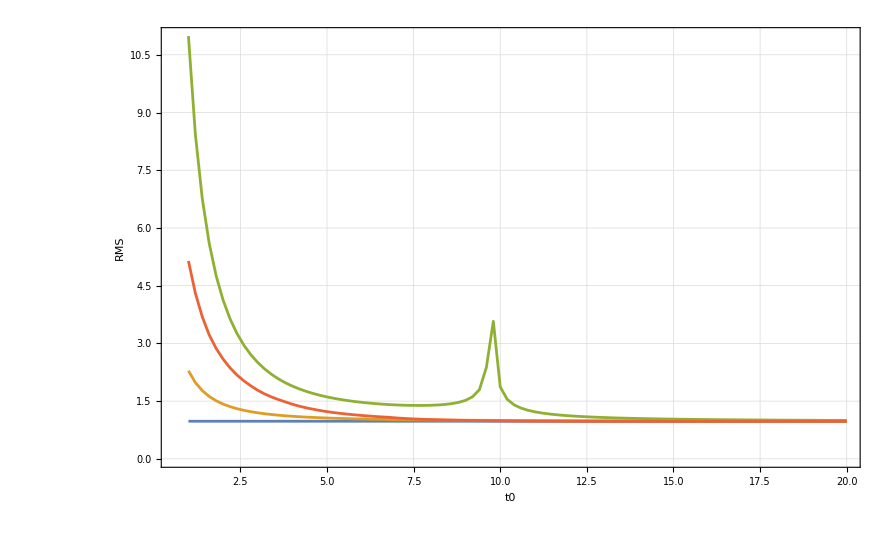

```mathematica
ListPlot[{UC0,TD0,SATD0,RADD0},GridLines->Automatic, Frame->True, FrameLabel->{"t0","RMS"}, Joined->True,PlotRange->All]
```

### 12b

```mathematica
(*checking RMS values for RADD for ϕ=π*)
```

```mathematica
RADDπ=Map[{t0list[[#]],DataphiPi[[#,5]]}&,Range[1,Length[t0list]]];
```

```mathematica
RADDπ={{1.,2.9876146967842514},{1.2,2.573179941519674},{1.4,2.2953655226892162},{1.6,2.110354431374454},{1.8,1.992575425656185},{2.,1.9292111988279537},{2.2,1.9172069028602243},{2.4000000000000004,1.7759532399705036},{2.6,1.6496136669558807},{2.8,1.565765246391496},{3.,1.507404291771618},{3.2,1.4588475688276554},{3.4000000000000004,1.376318895423337},{3.6,1.3091937819071975},{3.8000000000000003,1.2016633025418424},{4.,1.1139800434357336},{4.2,1.0505688503704733},{4.4,1.0036299753179743},{4.6,0.9644205389727405},{4.800000000000001,0.9292355454968073},{5.,0.897258162619632},{5.2,0.868728129148627},{5.4,0.842759235708852},{5.6000000000000005,0.822145214699251},{5.800000000000001,0.805643364977087},{6.,0.7923273161937894},{6.2,0.7815152201672708},{6.4,0.7726873454333691},{6.6000000000000005,0.7654448629412638},{6.800000000000001,0.7594784643000736},{7.,0.7545460081768917},{7.2,0.7504563338837137},{7.4,0.747057373877149},{7.6000000000000005,0.744227314953046},{7.800000000000001,0.7418679539216156},{8.,0.7398996535995443},{8.2,0.7382574793843985},{8.4,0.7368882158393367},{8.600000000000001,0.7357480454353916},{8.8,0.7348007298337772},{9.,0.7340161756050024},{9.200000000000001,0.7333692962104099},{9.4,0.7328391038690921},{9.6,0.7324079809567319},{9.8,0.7320610924636202},{10.,0.7317859099183859},{10.200000000000001,0.7315718238695589},{10.4,0.7314098270860717},{10.600000000000001,0.7312922545063634},{10.8,0.7312125689364856},{11.,0.7311651837923269},{11.200000000000001,0.7311453159634828},{11.4,0.7311488632681661},{11.600000000000001,0.7311723020609365},{11.8,0.7312126014165432},{12.,0.7312671509957375},{12.200000000000001,0.731333700242104},{12.4,0.7314103069930886},{12.600000000000001,0.731495293936747},{12.8,0.7315872116263856},{13.,0.7316848069921909},{13.200000000000001,0.7317869964731167},{13.4,0.7318928430422823},{13.600000000000001,0.732001536521682},{13.8,0.7321123766824857},{14.,0.7322247587098144},{14.200000000000001,0.7323381606790165},{14.4,0.7324521327468412},{14.600000000000001,0.7325662878076503},{14.8,0.732680293403709},{15.,0.7327938647110139},{15.200000000000001,0.7329067584492384},{15.4,0.7330187675870992},{15.600000000000001,0.7331297167335212},{15.8,0.7332396606570898},{16.,0.7333480708768828},{16.200000000000003,0.7334550470923497},{16.4,0.733560505098017},{16.6,0.7336643767307071},{16.8,0.7337666078194358},{17.,0.733867156388737},{17.2,0.7339659910829859},{17.400000000000002,0.7340630897836865},{17.6,0.7341584383954298},{17.8,0.7342520297794384},{18.,0.7343438628163952},{18.2,0.7344339415826168},{18.400000000000002,0.7345222746257081},{18.6,0.7346088743275876},{18.8,0.7346937563443237},{19.,0.7347769391135484},{19.2,0.7348584434213613},{19.400000000000002,0.7349382920216466},{19.6,0.735016509301598},{19.8,0.7350931209879961},{20.,0.7351681538894524}};
```

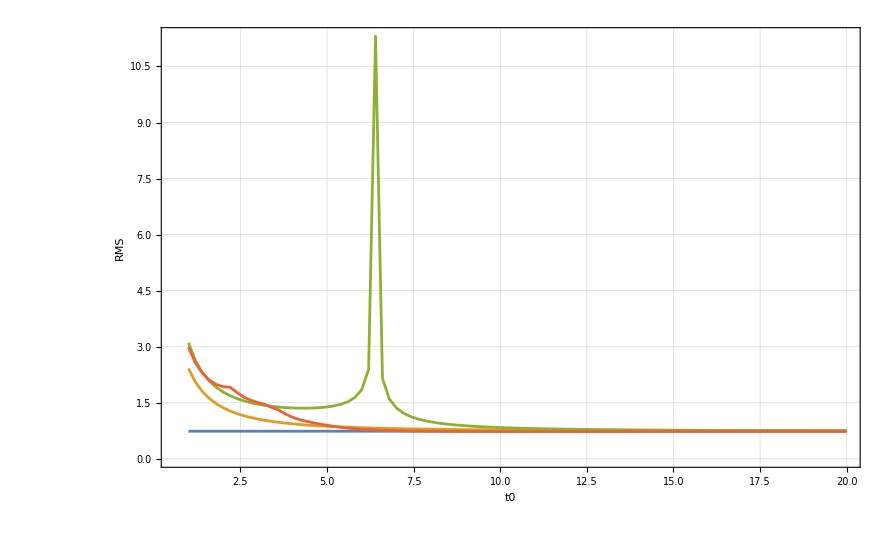

```mathematica
ListPlot[{UCπ,TDπ,SATDπ,RADDπ},GridLines->Automatic, Frame->True, FrameLabel->{"t0","RMS"}, Joined->True,PlotRange->All]
```

### 12c

```mathematica
(*from RADD0 data set, we use the optimized parameters given by the element for Γt0=7*)
```

```mathematica
{7,19/100,497/675,39/10,1.0625153481686964,1.1829374776399135,0.8704900314203157}
```

```mathematica
(*note σ here is the same as ν from the paper*)
```

```mathematica
Γ=1;
Δ0=1/2 Γ;
Ω0=1/2 Γ;
ω=ωCirc1DL;
dir=1;
t0=7;
A=19/100;
σ=497/675;
n=39/10;
φ=0;
times=tb0sRetimes[Δ0,Ω0,Γ,φ,ω,dir,t0]
{ts,ph}=μF3CircPathCorr[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,times]
```

{3.01074,3.5,3.98926}

{{{0,14}},{0}}

General::munfl: Exp[-190802.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

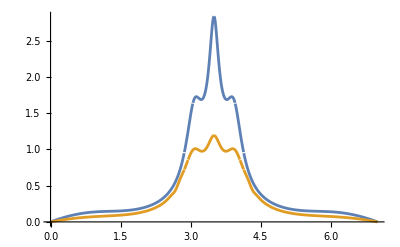

```mathematica
Plot[{Abs[gxCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]],Abs[gx2[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t,ts,ph]]},{t,0,t0},PlotRange->All
]
```

### 12d

General::munfl: Exp[-190802.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

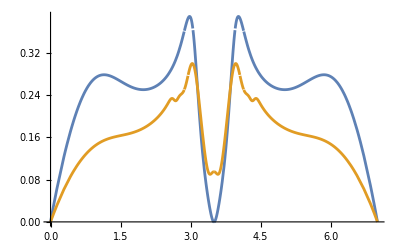

```mathematica
Plot[{Abs[gzCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]],Abs[gz2[Δ0,Ω0,Γ,φ,ω,dir,t0,A,σ,n,t,ts,ph]]},{t,0,t0},PlotRange->All
]
```